# A mathematical model for universal semantics (Question answering based on English Wikipedia)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the question-answering sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Before you start, please download the official WikiQA data set from https://www.microsoft.com/en-us/download/details.aspx?id=52419 (published: August 28, 2015) to the following file folder (or a different place that you designate)

```mathematica
WikiQACorpusDir="D:\\Documents\\WikiQACorpus";
```

so that this directory contains the following files:

{"emnlp-table", "eval.py", "EVALUATION.bat", "Guidelines_Phase1.pdf", "Guidelines_Phase2.pdf", "LICENSE.pdf", "README.txt", "WikiQA-dev-filtered.ref", "WikiQA-dev.ref", "WikiQA-dev.tsv", "WikiQA-dev.txt", "WikiQASent.pos.ans.tsv", "WikiQA-test-filtered.ref", "WikiQA-test.ref", "WikiQA-test.tsv", "WikiQA-test.txt", "WikiQA-train.ref", "WikiQA-train.tsv", "WikiQA-train.txt", "WikiQA.tsv"}

We extracted from the static dump of English Wikipedia dated Sept. 1, 2015 (enwiki-20150901-pages-articles-xml.bz2 available from the URL https://meta.wikimedia.org/wiki/Data_dump_torrents#enwiki) a subset of 1242 Wikipedia pages that match the WikiQA dataset. The result was a file named WikiSelecta.xml (uploaded to GitHub in zipped form WikiSelecta.zip).

Please download and unzip the aforementioned zipped file, before putting the XML file in the following folder (or a different place that you redesignate)

```mathematica
WikiSelectaDir="D:\\Documents";
```

```mathematica
SetDirectory[WikiSelectaDir]
```

D:\Documents

Drawing on heuristic auto-corrections (algorithms not included here), our file  WikiSelecta.xml contains information about the correspondence between page titles listed in the WikiQA dataset and those appearing in the static dump. The table below allows us to locate the correct Wikipedia page when prompted.

```mathematica
Select[s=OpenRead["WikiSelecta.xml"];TitleTab=ReadList[s,Record,RecordSeparators->{{"<WikiQAtitle>"},{"</title>"}}];Close[s];TitleComp=StringSplit[#,"</WikiQAtitle><page>"~~("\n"|" ")..~~"<title>"]&/@TitleTab,#_⟦1⟧≠#_⟦2⟧&]
```

{{antibody,Antibody},{Pitbull (entertainer),Pitbull (rapper)},{World Trade Center,World Trade Center (2001â.80.93present)},{state school,State school},{States and territories of India,States and union territories of India},{Benedict arnold,Benedict Arnold},{Central america,Central America},{Edgar allan poe,Edgar Allan Poe},{Labor day,Labor Day},{Women's roles in the World Wars,Women in the World Wars},{Bruce Jenner,Caitlyn Jenner},{Gloria in Excelsis Deo,Gloria in excelsis Deo},{ShopNBC,EVINE Live},{Automatic Document Feeder,Automatic document feeder},{Saint Joseph's Day,St Joseph's Day},{Ashanti (entertainer),Ashanti (singer)},{Myasthenia Gravis,Myasthenia gravis},{What It Takes (song),What It Takes (Aerosmith song)},{List of countries where English is an official language,List of territorial entities where English is an official language},{Major league baseball,Major League Baseball},{Julius caesar,Julius Caesar},{Myers-Briggs Type Indicator,Myersâ.80.93Briggs Type Indicator},{America's Next Top Model, Cycle 12,America's Next Top Model (cycle 12)},{Consumer Price Index,Consumer price index},{European Theatre of World War II,European theatre of World War II},{Monkeys in space,Monkeys and apes in space},{Qing Dynasty,Qing dynasty},{Youtube,YouTube},{Six sigma,Six Sigma},{Charles dickens,Charles Dickens},{Civil rights movement,African-American Civil Rights Movement (1954â.80.9368)},{Procedure codes,Procedure code},{Tropic of cancer,Tropic of Cancer},{Give me Liberty, or give me Death!,Give me liberty, or give me death!},{List of academic disciplines,Outline of academic disciplines},{K-Cup,Keurig},{Ray lamontagne,Ray LaMontagne},{When the Wind Blows (James Patterson novel),When the Wind Blows (Patterson novel)},{Race (human classification),Race (human categorization)},{Tiger Salamander,Tiger salamander},{Mount McKinley,Denali},{Go Daddy,GoDaddy},{Stevie wonder,Stevie Wonder},{Ho chi minh,Ho Chi Minh},{Cowboys Stadium,AT&amp;T Stadium},{Dave Batista,Dave Bautista},{Arctic circle,Arctic Circle},{Suicide (character),Suicide (wrestling)},{GE Building,30 Rockefeller Center},{Giant Panda,Giant panda},{Social Norms Approach,Social norms approach},{Value added tax,Value-added tax},{High-Sticking,High-sticking},{Earned Income Tax Credit,Earned income tax credit},{Judas (song),Judas (Lady Gaga song)},{TMZ (website),TMZ},{Hillary Rodham Clinton,Hillary Clinton},{Northern Cardinal,Northern cardinal},{Ratchet & Clank,Ratchet &amp; Clank},{roller coaster,Roller coaster},{Purple haze,Purple Haze},{Direct Marketing,Direct marketing},{Fruit cake,Fruitcake},{vaccine,Vaccine},{Melissa & Joey,Melissa &amp; Joey}}

```mathematica
SelectaTitles=#_⟦2⟧&/@TitleComp;
```

```mathematica
TitleConversion=Association[#_⟦1⟧->#_⟦2⟧&/@(StringSplit[#,"</WikiQAtitle><page>"~~("\n"|" ")..~~"<title>"]&/@TitleTab)];
```

Now you are ready to execute all the cells in the Mathematica Notebook, in order to reproduce our QA results reported in [1].

## Approximate clustering of English words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
RegularizeEnglishVerbs[w_]:=StringReplace[StringReplace[StringReplace[StringReplace[w,{"heaven":>"ηϵaveν",(v:("a"|"i"))~~"bilit"~~__:>v<>"ble","istic"~~___:>"ist","positiv":>"poσiτiv","lar"~~"ly"|"s"~~WordBoundary:>"lar","feet":>"foot",ff:WordCharacter~~"ful"~~"ler"|"lest"|"ness"~~___:>ff,"ificat"~~___:>"ify","ili"~~"s"|"z"~~"e"|"ing"~~___:>"ility",WordBoundary~~"inabil"~~___:>"unable",WordBoundary~~"inalien":>"unalien","alit"~~"y"|"ies"~~WordBoundary:>"al","ntit"~~"y"|"ies"~~WordBoundary:>"ntify","arit"~~"y"|"ies"~~WordBoundary:>"ar","idit"~~"y"|"ies"~~WordBoundary:>"id",(c:("c"|"g"|"n"|"d"))~~"uit"~~"y"|"ies"~~WordBoundary:>c<>"uous",(b:("barb"|"hil"))~~"arit"~~"y"|"ies"~~WordBoundary:>b<>"arious","charit"~~"y"|"ies"~~WordBoundary:>"charitable","toric"~~___:>"tory","tricit"~~"y"|"ies"~~WordBoundary:>"tric","necessit"~~"y"|"ies"~~WordBoundary:>"necessary","enmit"~~"y"|"ies"~~WordBoundary:>"enemy","circuit"~~"y"|"ies"~~WordBoundary:>"circuitous","reciprocal":>"reciprocity","virgin"~~""|"s"~~WordBoundary:>"virginity","femini"~~""|"ni"~~"t"~~"y"|"ies"~~WordBoundary:>"feminine","vanit"~~"y"|"ies"~~WordBoundary:>"vain","simplicit"~~"y"|"ies"~~WordBoundary:>"simple"}],{WordBoundary~~"clar":>"clear","Korean":>"Korea",WordBoundary~~"instab":>"unstab",WordBoundary~~"mourn":>"μouρn",WordBoundary~~"made"~~WordBoundary:>"make",WordBoundary~~"laughter":>"laugh",(s:("cent"|"cloist"|"integ"|"neut"|"sepulch"|"spect"))~~"er":>s<>"re","rebellion"~~___:>"rebel",(h0:("at"|"it"|"nt"|"g"|"ic"|"iv"))~~"ious":>h0<>"ion","inguish":>"inct","ength":>"ong","nness"~~WordBoundary:>"n",(c:Except["i"])~~"aris"~~"t"|"m"~~___:>c<>"ial","iaris"~~"t"|"m"~~___:>"iary",(h:("alchem"|"narch"))~~"is"~~"t"|"m"~~___:>h<>"y",WordBoundary~~"pacif"~~___:>"peace",WordBoundary~~"theori"~~___:>"theory","scienti"~~"st"|"fic"~~___:>"science","tician"~~___:>"tical","tenet":>"τenϵτ","tender":>"teνδer","tenab":>"τteνab",WordBoundary~~"tenac"~~___:>"τenac","tenta":>"τentα",WordBoundary~~"ten"~~""|"s"|("th"~~___)~~WordBoundary:>"10ten","Us"|"Usa":>"American","Spain":>"Spanish","Italy":>"Italian","France":>"French","Ukraine":>"Ukrainian","Belgium":>"Belgian","Wales":>"Welsh","Scotland":>"Scottish","Ireland":>"Irish","Mexico":>"Mexican","Denmark":>"Danish","ironing":>"iron","ironi"~~"c"|"es"~~___:>"iρony","irony":>"iρony","satir":>"σßaτir","tenant":>"τeνant","satin":>"σaτin","promis":>"πrωmis","lesson":>"λeκcjon","capric":>"κaπric",WordBoundary~~(c:("b"|"h"))~~"ang"~~"ed"|"ing":>c<>"ang",WordBoundary~~"hung"~~WordBoundary:>"hang","grove":>"γρove","menace":>"μeνace","breadth":>"broad","crash":>"κrash",WordBoundary~~"sow":>"σow",WordBoundary~~"roof":>"ρωoof",WordBoundary~~"rash":>"ρash","town":>"towν","flower":>"φλower","bury":>"βuρy","buri":>"βuρi","hall":>"ζaλl","homage":>"homαγe","worr":>"woρr","wear"~~"i"~~Except["n"]~~___:>"ωϵaρι","wear"~~"y"~~___:>"ωϵaρι","species":>"σπiecϵσ","mentalit"~~___:>"mental","antal"~~WordBoundary:>"ance",WordBoundary~~"conic"~~""|"al"~~""|"ly"~~WordBoundary:>"cone","sticit"~~___:>"stic","mound":>"mωund","membran":>"meμβρaν",WordBoundary~~"leg":>"λeγ","condition":>"conδτιon",WordBoundary~~"good"~~WordBoundary:>"γoωδ","salar":>"σaλαρ","usur":>"usuρ","earn":>"ϵαarn","ma"~~"d"|"'"|"’"~~"am":>"φru","children":>"child","flexi"~~"on"|"ve"~~___:>"flect",WordBoundary~~"comic":>"comedic",WordBoundary~~"traged":>"tragic","istry"~~WordBoundary:>"ister","ics"~~WordBoundary:>"ical","polite":>"πλiτe","publish":>"publication",(h5:("ap"|"im"|"multi"))~~"pl"~~"y"|("ie"~~___):>h5<>"plication","choice":>"choose","radical"~~"s"|""~~WordBoundary:>"radicalize","antas"~~"y"|"ies"~~WordBoundary:>"antasize","monopol"~~"y"|"ies"~~WordBoundary:>"monopolize",("is"|"iz"~~"e"|"ed"|"ing"|"ation"|"ement"|"er"|"able"|"ab"~~"s"|"ly"|""~~WordBoundary):>"ize",(c0:Except["p",LetterCharacter])~~"lus"~~WordBoundary:>c0<>"li","focus"~~___:>"focus","uum"~~WordBoundary:>"ua",WordBoundary~~"radii"~~WordBoundary:>"radius","dempt"~~___:>"deem","woke":>"wake",WordBoundary~~"avuncular"~~___:>"uncle",WordBoundary~~"chagrin"~~""|"s"~~WordBoundary:>"chagrine",WordBoundary~~"langu"~~"id"|"or"~~___:>"languish",WordBoundary~~"ran"~~WordBoundary:>"run",WordBoundary~~(p0:("con"|"miscon"|"per"|"precon"))~~"cept"~~___:>p0<>"ceive",WordBoundary~~(p1:(""|"un"))~~"dece"~~"it"|"pt"~~___:>p1<>"deceive",WordBoundary~~"rece"~~"pt"|"ipt"~~___:>"receive",WordBoundary~~"matrimon"~~___:>"marry",WordBoundary~~"soror"~~___:>"sister",WordBoundary~~"sis"~~WordBoundary:>"sister",WordBoundary~~"matern"~~___:>"mother",WordBoundary~~"patern"~~___:>"father",WordBoundary~~"fratern"~~___:>"brother",WordBoundary~~"marit"~~___:>"marry","hour":>"oρα","contempor"~~___:>"contempor","a"~~"c"|"n"~~"eous"~~___:>"al",(c:Except["a"|"e"|"i"|"o"|"u",LetterCharacter])~~"ar"~~""|"y"|"ily"|"ies"|"ize"~~WordBoundary:>c<>"ial",(p1:("atr"|"fer"|"prec"))~~"ocit"~~"y"|"ies"~~WordBoundary:>p1<>"ocious","acit"~~"y"|"ies"~~WordBoundary:>"acious","idiot":>"idioτ","prophet"~~___:>"prophetic","ancestress":>"ancestor","mistress":>"master",(c:Except["s"|"t",LetterCharacter])~~"tress":>c<>"tor","severed":>"sever"}],{"suspic":>"suspect","repeat"~~___:>"repetition","beautical":>"beauty",WordBoundary~~"tent":>"tenτ",WordBoundary~~"hung":>"φaiμ","weariness"~~___:>"ωϵaρι","caus"~~(v:("a"|"e"|"i")):>"κaωζ"<>v,"serious":>"sϵrious","sever"~~"e"|"it":>"σeωϵre","ϵαarnest":>"ϵαaρneστ",WordBoundary~~"comedo":>"κoμeδo","risen"|"rose"~~WordBoundary:>"rize","began":>"begin","tranquil"~~""|"l"~~"iz"~~___:>"tranquil",("s"~~("'"|"’")~~"s")~~WordBoundary:>"",(h:LetterCharacter)~~"tic"~~""|"al"~~""|"ly"~~""|("iz"~~___)~~WordBoundary:>h<>"sis",WordBoundary~~"criti"~~"c"|"que"~~""|"al"~~""|"ly":>"criticize",WordBoundary~~"pretent":>"pretend","abdomen":>"abdomin",(v:"o"|"u"|"i"|"a")~~"si"~~"on"|"ve"~~___:>v<>"de","suffer":>"sωuffer","savage":>"saβaγe","deer":>"dϵer"}],{"forg"~~"e"|"o"~~"t"~~""|"ten"~~___:>"vγeß","mad":>"μφaδ",(c:("i"|"g"|"s"|"r"))~~"onal"~~""|"ly"|"i"~~___:>c<>"on","inal"~~""|"ly"|"i"~~___:>"in",(h:___)~~"-in-law"~~WordBoundary:>"λαω"<>h,WordBoundary~~"lad"~~""|"die"|"dish"|"hood"~~""|"s"~~WordBoundary:>"λaδ","counten":>"kouten",(p5:("dissatis"|"lique"|"petri"|"putre"|"rare"|"satis"|"stupe"|"vitri"))~~"f"~~"y"|"ie"|"ying"|"ies"|"ied":>p5<>"fact","aur":>"aωr","pool":>"poωl","expence":>"expense","flatter":>"flaττer","temper":>"tempϵr","prett":>"prϵeτ",(p4:("ab"|"pre"))~~"sence":>p4<>"sent",WordBoundary~~"licen"~~"c"|"s":>"licent",(p3:("de"|"of"))~~"fen"~~"c"|"s":>p3<>"fend","visor"~~WordBoundary:>"vise",(p2:("ad"|"de"))~~"vi"~~"c"|"z":>p2<>"vis",(pf:("col"|"e"))~~"lid":>pf<>"lis","de"~~(c2:"c"|"r")~~"id":>"de"<>c2<>"is",(p1:("di"|"pro"))~~"vid":>p1<>"vis","automation":>"automasis",WordBoundary~~"won"~~WordBoundary:>"win",WordBoundary~~(h:"K"|"k")~~"ing":>h~~"oenig","duct"~~""|"ion":>"duce","four":>"φour",WordBoundary~~"typ":>"zyp",WordBoundary~~(c:("b"|"c"|"l"|"br"|"r"))~~"ook"~~WordBoundary:>c<>"ooked",WordBoundary~~"former":>"φormer","migrant":>"migrate","went"|"going"|"gone"|"goes"~~WordBoundary:>"go","heard"~~WordBoundary:>"hear","gave"~~WordBoundary:>"give","ced"~~"e"|"ed"|"es"|"ing"~~WordBoundary:>"cezß","preceden"~~"c"|"t":>"precezß","listen":>"lisztzn","mention":>"menzzion","missile":>"missle","mission":>"mit","passion":>"patzion","possess":>"pozzezz","rouse":>"rzouse","sump":>"sume","does"|"did"|"done"|"doing"~~WordBoundary:>"do","came"~~WordBoundary:>"come","rnt"~~WordBoundary:>"rn","bought"~~WordBoundary:>"buy","stood"~~WordBoundary:>"stand",WordBoundary~~"brought"~~WordBoundary:>"bring","thought":>"think",WordBoundary~~"sought"~~WordBoundary:>"seek",WordBoundary~~"eat"~~""|"en"|"ing"|"s"~~WordBoundary:>"ate",WordBoundary~~"explain":>"explan","see"~~""|"n"|"ing"|"s"~~WordBoundary:>"saw",WordBoundary~~"taught"~~WordBoundary:>"teach",WordBoundary~~"caught"~~WordBoundary:>"catch",WordBoundary~~"flew"|"flown"~~WordBoundary:>"fly",WordBoundary~~(h:(""|"in"|"mis"|"off"|"out"|"over"|"p"|"under"))~~"led"~~WordBoundary:>h<>"lead","itten"~~WordBoundary:>"iten",WordBoundary~~"'"|"’":>"",WordBoundary~~(c:""|"s")~~"lain"~~WordBoundary:>c<>"lay","ered"~~WordBoundary:>"er",WordBoundary~~"begg"~~"ed"|"ar":>"beg","dye":>"dzye",WordBoundary~~"rode"|"ridden"~~WordBoundary:>"ride",("sis"~~WordBoundary)|"siz":>"ses",WordBoundary~~"prevent":>"prezvent",WordBoundary~~"meant"~~WordBoundary:>"mean",WordBoundary~~"mete"|"metes"|"meted"|"meting"|"metings"~~WordBoundary:>"mzet",WordBoundary~~"warn":>"wxarn",WordBoundary~~"attend":>"attenzd",(h:"rt"|"mpl"|"tr")~~"aint":>h<>"ain",WordBoundary~~"prevail":>"preval",WordBoundary~~"solde":>"soldq",WordBoundary~~"soldi":>"soldw"}];
```

```mathematica
NormalizeEnglishVowelLength[w_]:=If[w==ToLowerCase[w],ToLowerCase[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[w,{"osit"~~"y"|"ies"~~WordBoundary:>"ous",(h:(LetterCharacter~~LetterCharacter))~~"oe"~~""|"d"|"s"~~WordBoundary:>h<>"o"}],{(c:LetterCharacter)~~"tr":>c<>"ter",WordBoundary~~"mode":>"modz",WordBoundary~~"some":>"somz","oo":>"ú","ll":>"λ","eed":>"ezß","ss":>"zß","manner":>"maznner",(h:"dis"|"ex"|"pre")~~"tens":>h<>"tend",(h1:"ex"|"sus")~~"pens":>h1<>"pend",WordBoundary~~"pre":>"pré","fer":>"fér","freedom":>"free","puls":>"pel",WordBoundary~~(h:(LetterCharacter~~"a"|"o")~~"tion"):>h<>"tiv","static":>"sztatic","summer":>"suzmmer","women":>"woman","deep"~~""|("e"~~___):>"depth","rough":>"rouffgh","quiet":>"cquiet","loss"|"lose":>"lost","oe":>"oue","au":>"aau","neer":>"ne",WordBoundary~~"earl"~~"y"|"i":>"earzli",WordBoundary~~"fine":>"fizne",WordBoundary~~"water":>"wazter",WordBoundary~~"sudden":>"swudden",WordBoundary~~"side":>"szide",WordBoundary~~"capab":>"kapab","soul":>"szoul",WordBoundary~~"mere":>"mzere",WordBoundary~~"stel":>"sztel",WordBoundary~~"gas":>"gazß",WordBoundary~~"ton":>"twon",WordBoundary~~"ski"~~""|"s"|"ing"|"ed"~~WordBoundary:>"szki",WordBoundary~~"singly"~~WordBoundary:>"single",WordBoundary~~"gently"~~WordBoundary:>"gentle",WordBoundary~~"idl"~~"est"|"y"~~WordBoundary:>"idle",WordBoundary~~"genera"~~WordBoundary:>"genus",WordBoundary~~"generat":>"jenerat",WordBoundary~~"genero":>"gjenero"}],x_~~x_:>ToUpperCase[x]],{(h:Except["e"|"i"|"o"|"u"|"y",CharacterRange["b","z"]])~~(v:("a"|"e"|"i"|"o"|"u"))~~(t:(Except["e"|"i"|"o"|"u"|"w"|"x"|"y",CharacterRange["b","z"]]~~"ag"|"al"|"aλ"|"at"|"e"|"ing"|"ish"|"it"|"ion"|"iv"|"ous")|"nd"|"ck"|"gh"):>h<>ToUpperCase[v]<>t,"ang"~~"e"|"ing":>"Ange"}],{"é":>"e","A":>"aa","E":>"ee","I":>"í","O":>"óó","U":>"u","ú":>"oo","T":>"tt","λ":>"ll",WordBoundary~~"beTer"|"best"~~WordBoundary:>"γoωδ",WordBoundary~~"gOv":>"góv",WordBoundary~~"inter":>"jntr","lezß":>"zlezß"}]],"zx"<>StringReplace[w,"ean"~~""|"s"~~WordBoundary:>""]]
```

```mathematica
EnglishEffSpell[w_] := StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[NormalizeEnglishVowelLength[RegularizeEnglishVerbs[w]],{"family":>"families","iv":>"ív","ióón":>"ion","gral":>"graation",(("'"|"’")~~""|"s"~~(""|"'"|"’")~~WordBoundary)|"-":>"",(c:LetterCharacter)~~"aid":>c<>"ayed","clamat":>"claimat","emn":>"μn","ck":>"c","ye":>"yme","lóó":>"lo","ld":>"llz","la":>"lôa","ng":>"zñ","enten":>"entzen","ook"~~WordBoundary:>"aaken","ou":>"í","ply":>"plie","rd":>"rzd","sh":>"š","tim":>"ztim","oi":>"zö","ui":>"zü","ble"~~""|"d"|"s"~~WordBoundary:>"bly","s"~~WordBoundary:>"","ant"~~WordBoundary:>"ance","hie"~~"r"|"st"~~WordBoundary:>"hy"}],{WordBoundary~~"dad"|"dady"~~WordBoundary:>"φaθer",WordBoundary~~"mom"|"mum"~~WordBoundary:>"mother",WordBoundary~~(s:LetterCharacter)~~"ied":>s<>"ieed",WordBoundary~~(c:"s"|"t"|"w")~~(v:"e"|"o"|"óó"):>c<>"z"<>v,WordBoundary~~(c:"c"|"w")~~"a":>c<>"βa",WordBoundary~~"móó":>"μo",WordBoundary~~"dóó":>"δo",WordBoundary~~"ba":>"βa",WordBoundary~~"f"~~(v:"i"|"í"):>"ff"<>v,WordBoundary~~"f"~~(v:"a"|"e"):>"φ"<>v}],{"f"|"fe"~~ WordBoundary :> "ve","xe"~~WordBoundary:>"x",(h:(LetterCharacter~~LetterCharacter~~LetterCharacter))~~"ly"~~WordBoundary:>h}], {"h"~~"i"|"í":>"hî","lu":>"lvu","y":>"ie"}],{(H:(LetterCharacter~~LetterCharacter~~LetterCharacter))~~"tion"|"tic"~~WordBoundary:>H<>"t",(H1:(LetterCharacter~~LetterCharacter~~LetterCharacter))~~"izñ"|"îzñ"|"ful"|"ed"|"ment"|"nezß"|"age"|"ícal"~~WordBoundary:>H1<>""}],{(h:"pel"|"s")~~"ion"~~WordBoundary:>h<>"ív","ll":>"λ","i"~~(c2:"r"):>"ï"<>c2,"iev"|"îev"|"eft":>"ääve","ea":>"ää","th":>"θ","ch":>"č","ph":>"φφ","own"~~WordBoundary:>"ow","lt"~~WordBoundary:>"l",(c:Except["d",LetterCharacter])~~"ent"~~""|"íve"~~WordBoundary:>c<>"eend","o"|"óó"~~(c:"p"|"r"):>"ô"<>c,(H:(LetterCharacter~~LetterCharacter~~LetterCharacter))~~"iš"~~WordBoundary:>H,WordBoundary~~"mi":>"μi"}],{WordBoundary~~(h:(LetterCharacter~~___))~~(c:Except["e"|"i",LetterCharacter])~~"e"~~WordBoundary:>h<>c<>If[StringMatchQ[h,"zx"~~___],"ae",""],"zx"~~(t:WordCharacter..):>"zx"<>StringReplace[t,"ie"~~WordBoundary:>"y"],WordBoundary~~"beg"~~WordBoundary:>"bbeg",WordBoundary~~"dää"~~"d"|"θ"~~WordBoundary:>"die"}]
```

```mathematica
FirstLetter[s_]:=StringTake[s,If[s=="",0,1]]
```

```mathematica
LastLetter[s_]:=StringTake[s,If[s=="",0,-1]]
```

```mathematica
EnglishVowelExt:="a"|"ä"|"e"|"i"|"í"|"î"|"ï"|"o"|"ô"|"ö"|"ó"|"u"|"ü";
```

```mathematica
BlotFirstVowel[word_]:=(wL=StringLength[word];coverage=(StringPosition[word,EnglishVowelExt..,1]∪{{-∞,+∞}})_⟦1⟧;If[(First[coverage]>1)&&(Last[coverage]<wL),StringReplacePart[word,"a",coverage],word])
```

```mathematica
BlotFirstVowel[EnglishEffSpell["automatic"]]
```

aautomaas

```mathematica
BlotFirstVowel[EnglishEffSpell["ruin"]]
```

rzan

```mathematica
BlotFirstVowel[EnglishEffSpell["find"]]
```

ffand

```mathematica
EnglishProtectedRange[word_]:=Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~(""|"be"|"co"|"cô"|"cínter"|"dee"|"di"|"fô"|"ha"|"ma"|"pre"|"pro"|"próó"|("r"~~EnglishVowelExt..)|"ster"|"su"|"te"|(EnglishVowelExt..))~~Except[EnglishVowelExt]...~~EnglishVowelExt..]]]]
```

```mathematica
EnglishEssRootPreBlot[word_]:=(tag=word;hL=EnglishProtectedRange[tag];StringReplace[StringTake[tag,hL]<>StringReplace[StringReplace[StringReplace[StringDrop[tag,hL],{(x:"a"|"o"|"u"|"ï")~~(f:(Except["a"|"o"|"u"|"ï"]..))~~WordBoundary:>x<>StringTake[f,1]}],{"a"~~WordBoundary:>""}],{"e"~~Except["e"]...~~WordBoundary:>""}],{"peλ"~~WordBoundary:>"pel",WordBoundary~~"reebel"~~WordBoundary:>"reebeλ"}])
```

### Sample words

Here we determine the effective spellings and essential roots for some English words.

```mathematica
EnglishSampleWords={#,2}&/@{"abolish","abolished","abolishes","abolishing","abolishment","abolition","abolitionism","abolitionist","abolitionists","admonish","admonishable","admonisher","admonishes","admonishing","admonishingly","admonishment","admonition","admonitory","aid","aided","aids","America","American","analyses","analysis","analytic","analytically","analyze","analyzed","ant","antenna","antennae","anterior","anxieties","anxiety","anxious","anxiously","arise","arisen","arose","automatic","automatically","bad","bat","beauties","beautiful","beautifully","beauty","bed","bedding","beds","beg","began","beggar","begged","begin","beginning","begun","belie","belied","belief","beliefs","belies","believe","believed","believes","believing","bereave","bereft","best","bestow","bestowed","bet","better","bid","bit","bitten","break","breaking","breaks","Britain","British","broke","broken","brow","brows","browse","browsed","browses","browsing","brutal","brutality","brutalize","brutally","brute","brutish","child","childhood","children","children's","child's","conquer","conquered","conquest","cycle","cylinder","dance","danced","dances","dancing","dead","deal","dealt","death","destroy","destroyed","destruction","die","died","dies","differ","difference","different","difficult","difficulty","dosage","dose","drain","drainage","dried","dries","dry","dryly","dye","dyed","dyeing","dyes","dying","elect","elected","election","elections","electoral","emphases","emphasis","emphasize","emphasized","emphasizes","emphatic","employ","employed","employee","employer","employment","England","English","enjoy","enjoyed","enjoying","enjoyment","enjoys","environment","environmental","environmentalist","establish","established","establishes","establishing","establishment","estimate","estimated","estimates","estimation","fall","fallen","falling","falls","fame","family","famous","fat","feel","feeling","feels","fell","fellow","fellows","fellowship","felt","fight","fighting","fill","find","fit","fold","follow","fond","fought","found","fret","fretting","full","fund","funding","gentleman","gentlemen","German","Germany","good","happen","happened","happening","happens","happier","happiest","happily","happiness","happy","hat","hate","hated","hating","hatred","hats","heavy","heft","held","hell","hill","hillside","hit","hits","hitting","hold","increase","increased","increases","increasing","incredible","incredulity","incredulous","infer","inference","inferior","inferiority","inferred","infers","insist","insisted","insistence","integral","integrally","integrate","integration","interfere","interference","interfering","introduce","introduced","introduces","introduction","introductory","lack","lacking","ladies","ladies'","lady","lady's","law","lawyer","leave","leaves","leaving","left","lick","lie","lied","lies","life","life's","lift","lived","lives","living","lock","love","loved","lovely","loves","loving","low","lower","lowest","lowing","lowly","luck","luckily","lucky","lying","maid","maiden","maids","male","man","manage","manipulate","mankind","manner","manners","man's","mansion","mansions","marriage","married","marries","marrow","marry","marrying","men","mend","men's","merry","mile","mind","mole","mule","natural","naturally","nature","nature's","paid","pain","painful","painfully","pay","paying","payment","payments","pays","plan","planned","planning","plans","plant","plantation","play","played","player","players","playing","plays","presidency","president","presidential","presidents","prince","princes","princess","princesses","protect","protection","protector","protectoral","protectorate","ran","rang","range","ranged","ranges","ranging","rank","rant","rate","rated","rates","rating","real","realization","realize","refer","reference","referral","rid","ridden","ride","ring","ringing","rings","road","rode","rude","ruin","ruined","ruins","run","rung","running","runs","Russell","Russia","Russian","sad","sadden","saddened","sadly","said","sang","sat","say","saying","says","secede","seceded","secedes","seceding","secession","secessionist","secessionists","secessions","sell","selling","send","sending","sent","sentence","sentences","sentiment","sentimental","sentiments","set","sets","setting","sing","singing","sit","sits","sitting","slain","slave","slave-holder","slave-holding","slavery","slavery-restricting","slaves","slay","slow","slowly","sold","solution","solutions","solve","solved","solves","son","song","sons","sore","sorely","sorrow","sorry","sort","speak","speaker","speaking","speaks","speech","speeches","spoke","spoken","spokesman","strata","stratum","strife","strifes","strive","strived","striven","strove","sun","sung","swam","swear","swell","swelled","swelling","swells","swim","swimming","swims","swollen","swoon","swooned","swoons","sword","sworn","swum","tall","tame","tamed","tax","taxes","teeth","tell","telling","thank","thanking","thanks","theft","thief","thieve","thieved","thieves","thin","thing","things","think","thinking","thrift","thrifty","thrive","thrived","thriven","thrives","throve","time","times","timing","told","tooth","traffic","trafficking","transfer","transference","transferral","want","wear","weave","weep","weeping","weeps","weft","wept","wet","wife","wife's","winter","wipe","wiped","wipes","wit","wives","woman","woman's","women","women's","word","words","wore","world","worn","woven"};
```

```mathematica
Short[SortBy[{#,es=EnglishEffSpell[#_⟦1⟧],EnglishEssRootPreBlot[es]}&/@(EnglishSampleWords),Last],5]
```

{{{automatic,2},aautomaas,aautomaas},{{automatically,2},aautomaas,aautomaas},{{abolish,2},abóól,abóól},{{abolished,2},abóól,abóól},{{abolishing,2},abóól,abóól},{{abolishment,2},abóól,abóól},{{abolishes,2},abóóliš,abóóliš},{{abolition,2},abóólit,abóólit},{{abolitionism,2},abóólitionism,abóólition},{{abolitionist,2},abóólitionist,abóólition},«541»,{{falling,2},φaλ,φaλ},{{falls,2},φaλ,φaλ},{{feel,2},φeel,φeel},{{feeling,2},φeel,φeel},{{feels,2},φeel,φeel},{{felt,2},φel,φel},{{fell,2},φeλ,φeλ},{{fellow,2},φeλow,φeλow},{{fellows,2},φeλow,φeλow},{{fellowship,2},φeλowšip,φeλow}}

### Sorting and clustering

```mathematica
ExtractEnglishRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[MatchQ[SuffixNW,_List],NW=Drop[NW,-1],SuffixNW={"",""}];rootNW=If[MatchQ[First[NW0],_String],NW=Drop[NW,1];StringJoin[Cases[NW0,_String]],"#%"];)
```

```mathematica
ExtractEnglishRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[MatchQ[SuffixSW,_List],SW=Drop[SW,-1],SuffixSW={"",""}];rootSW=If[MatchQ[First[SW0],_String],SW=Drop[SW,1];StringJoin[Cases[SW0,_String]],"#%"];)
```

```mathematica
SimpleHeredityTestEnglish[a_,b_]:=(StringContainsQ[ToLowerCase[a],EnglishVowelExt]&&(aShort=StringReplace[a,{"e"~~WordBoundary:>"",(c:LetterCharacter)~~"lie"~~"r"|"st":>c}];aL=StringLength[aShort];bL=StringLength[b];(a==b)||(a==StringReplace[b,cc:Except["a"|"e"|"i"|"o"|"u"]~~"ster":>cc])||(aShort==StringReplace[b,(c:LetterCharacter)~~"lie"~~"r"|"st":>c])||(a==StringReplace[b,"ie"~~WordBoundary:>"i"])||(b==a<>LastLetter[a])||(b==aShort<>"i")||(b==a<>"n")||(b==a<>"ív")||(b==a<>"šip")||(b==aShort<>"šip")||(b==a<>"θ")||((bL-1>aL≥bL/2)&&StringMatchQ[a,StringTake[b,aL]~~"e"|""]&&(!StringMatchQ[b,aShort~~___~~"gu"|"ow"|"zß"|"iô"~~___])&&StringMatchQ[StringTake[b,{aL+1}],"a"|"e"|"h"|"i"|"o"|"ó"|"ô"|"r"|"u"])))
```

```mathematica
AdmissibleSuffixMismatchEnglish[aL_,bL_,root_,Suffix_,Alternation_]:=((StringContainsQ[ToLowerCase[root],EnglishVowelExt])&&(Alternation=={})&&(!StringContainsQ[Suffix_⟦1⟧,"nd"|"ow"|"zß"])&&(!StringContainsQ[Suffix_⟦2⟧,"nd"|"ow"])&&((Suffix=={"i","n"}||Suffix=={"i","u"}||((Suffix=={"","s"})&&(LastLetter[root]=="í"))||(StringMatchQ[Suffix_⟦1⟧,(("a"|"e"|"h")~~___)|""|"i"]&&StringMatchQ[Suffix_⟦2⟧,(("ï"|"m"|"r"|"ív"|"io"|"ió"|"ia"|LastLetter[root])~~LetterCharacter~~___)|"en"|"í"|("íz"|"îz"~~___)]))))
```

```mathematica
AdmissibleVowelAlternationEnglish[root_,Suffix_,Alternation_]:=((StringMatchQ[FirstLetter[Suffix_⟦1⟧],""|"e"|"i"|"n"]&&StringMatchQ[FirstLetter[Suffix_⟦2⟧],""|"e"|"i"|"n"|"t"|"z"])&&(Length[Alternation]==2)&&(StringFreeQ[root,"i"|"u"])&&MatchQ[Alternation,{{"a","e"}|{"a","i"}|{"ää","óó"}|{"ää","ô"}|{"e","o"}|{"ee","oo"}|{"ee","óó"}|{"a","u"}|{"i","u"}|{"e",""}|{"oo","óó"}|{"í","ô"}|{"í","óó"},_}|{{"",LastLetter[root]},_}|{{"","e"},"e"}])
```

```mathematica
EnglishHeredityTest[a_,b_]:=SimpleHeredityTestEnglish[a,b]||(ExtractEnglishRootSuffixNW[a,b];((StringLength[rootNW]≥Max[aL,bL]/2)&&(AdmissibleSuffixMismatchEnglish[aL,bL,rootNW,SuffixNW,NW]||AdmissibleVowelAlternationEnglish[rootNW,SuffixNW,NW])))||(ExtractEnglishRootSuffixSW[a,b];((StringLength[rootSW]≥Max[aL,bL]/2)&&(AdmissibleSuffixMismatchEnglish[aL,bL,rootSW,SuffixSW,SW]||AdmissibleVowelAlternationEnglish[rootSW,SuffixSW,SW])))
```

```mathematica
EnglishHeredityTest[EnglishEffSpell["find"],EnglishEffSpell["found"]]
```

True

```mathematica
EnglishHeredityTest[EnglishEffSpell["find"],EnglishEffSpell["fond"]]
```

False

```mathematica
{NW0,rootNW,NW,SuffixNW}
```

{{f,{fí,óó},nd},fnd,{{fí,óó},nd},{,}}

```mathematica
EnglishHeredityTest[EnglishEffSpell["infer"],EnglishEffSpell["inferior"]]
```

False

```mathematica
{NW0,rootNW,NW,SuffixNW}
```

{{infe,{,riô},r},infer,{{,riô},r},{,}}

```mathematica
{SW0,rootSW,SW,SuffixSW}
```

{{infer,{,iôr}},infer,{},{,iôr}}

```mathematica
EnglishHeredityTest[EnglishEffSpell["confirm"],EnglishEffSpell["conform"]]
```

False

```mathematica
{NW0,rootNW,NW,SuffixNW}
```

{{conf,{ï,ô},rm},confrm,{{ï,ô},rm},{,}}

```mathematica
EnglishHeredityTest["apple","orange"]
```

False

```mathematica
{NW0,rootNW,NW,SuffixNW}
```

{{{,or},a,{ppl,ng},e},#%,{{,or},a,{ppl,ng},e},{,}}

```mathematica
ApproxClusterEnglishFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,EnglishEffSpell[#_⟦1⟧]}&/@wfl,Last],EnglishHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=EnglishEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowel[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(((EnglishHeredityTest[#1_⟦3⟧,#2_⟦3⟧]))||EnglishHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[];ApproxClusterEnglishFreqList[EnglishSampleWords]]
```

{0.537922,{{{automatic,automatically},{2,2}},{{abolish,abolished,abolishing,abolishment,abolishes,abolition,abolitionism,abolitionist,abolitionists},{2,2,2,2,2,2,2,2,2}},{{admonish,admonishing,admonishingly,admonishment,admonishes,admonishable,admonisher},{2,2,2,2,2,2,2}},{{admonition,admonitory},{2,2}},{{aid,aided,aids},{2,2,2}},{{analyses,analysis,analytic,analytically,analyze,analyzed},{2,2,2,2,2,2}},{{ant},{2}},{{antenna,antennae},{2,2}},{{anterior},{2}},{{anxieties,anxiety,anxious,anxiously},{2,2,2,2}},{{arise,arisen,arose},{2,2,2}},{{bed,bedding,beds},{2,2,2}},{{bid},{2}},{{beggar},{2}},{{began,begin,beginning,begun},{2,2,2,2}},{{believed,believing,belief,beliefs,believe,believes},{2,2,2,2,2,2}},{{belied,belie,belies},{2,2,2}},{{bereave,bereft},{2,2}},{{bestow,bestowed},{2,2}},{{bet},{2}},{{bit},{2}},{{bitten},{2}},{{beautiful,beautifully,beauties,beauty},{2,2,2,2}},{{beg,begged},{2,2}},{{break,breaking,breaks,broke,broken},{2,2,2,2,2}},{{brute,brutish,brutal,brutality,brutally,brutalize},{2,2,2,2,2,2}},{{brow,brows},{2,2}},{{browse,browsed,browses,browsing},{2,2,2,2}},{{cycle},{2}},{{cylinder},{2}},{{conquer,conquered},{2,2}},{{conquest},{2}},{{child,children,children's,child's,childhood},{2,2,2,2,2}},{{differ,different,difference},{2,2,2}},{{difficult,difficulty},{2,2}},{{deal,dealt},{2,2}},{{dance,danced,dances,dancing},{2,2,2,2}},{{destroy,destroyed,destruction},{2,2,2}},{{dead,death,die,died,dies,dying},{2,2,2,2,2,2}},{{drain,drainage},{2,2}},{{dried,dries,dry,dryly},{2,2,2,2}},{{dye,dyed,dyeing,dyes},{2,2,2,2}},{{elect,elected,election,elections,electoral},{2,2,2,2,2}},{{employ,employment,employed,employee,employer},{2,2,2,2,2}},{{emphases,emphasis,emphatic,emphasize,emphasized,emphasizes},{2,2,2,2,2,2}},{{enjoy,enjoying,enjoyment,enjoys,enjoyed},{2,2,2,2,2}},{{environment,environmental,environmentalist},{2,2,2}},{{establish,established,establishing,establishment,establishes},{2,2,2,2,2}},{{estimate,estimated,estimates,estimation},{2,2,2,2}},{{fond},{2}},{{fund,funding},{2,2}},{{full},{2}},{{follow},{2}},{{fold},{2}},{{fight,fighting,fought},{2,2,2}},{{find,found},{2,2}},{{fit},{2}},{{fill},{2}},{{fret,fretting},{2,2}},{{gentleman,gentlemen},{2,2}},{{happen,happened,happening,happens},{2,2,2,2}},{{happily,happiness,happy,happier,happiest},{2,2,2,2,2}},{{hate,hated,hating,hatred},{2,2,2,2}},{{hat,hats},{2,2}},{{hit,hits,hitting},{2,2,2}},{{heft,heavy},{2,2}},{{hell},{2}},{{hill},{2}},{{hillside},{2}},{{held,hold},{2,2}},{{increase,increased,increases,increasing},{2,2,2,2}},{{incredible},{2}},{{incredulous,incredulity},{2,2}},{{infer,inferred,infers,inference},{2,2,2,2}},{{inferior,inferiority},{2,2}},{{insist,insisted,insistence},{2,2,2}},{{integral,integrally,integrate,integration},{2,2,2,2}},{{introduce,introduced,introduces,introduction,introductory},{2,2,2,2,2}},{{interfere,interfering,interference},{2,2,2}},{{lick},{2}},{{lack,lacking},{2,2}},{{lock},{2}},{{ladies,ladies',lady,lady's},{2,2,2,2}},{{lift},{2}},{{leave,leaves,leaving,left},{2,2,2,2}},{{life,life's,lived,lives,living},{2,2,2,2,2}},{{love,loved,lovely,loves,loving},{2,2,2,2,2}},{{law},{2}},{{low,lowing,lowly,lower,lowest},{2,2,2,2,2}},{{lawyer},{2}},{{lie,lied,lies,lying},{2,2,2,2}},{{luck,luckily,lucky},{2,2,2}},{{maid,maids,maiden},{2,2,2}},{{male},{2}},{{mile},{2}},{{mule},{2}},{{manage},{2}},{{man,man's,men,men's},{2,2,2,2}},{{mend},{2}},{{mind},{2}},{{manipulate},{2}},{{mankind},{2}},{{mansion,mansions},{2,2}},{{marriage,married,marries,marry,marrying},{2,2,2,2,2}},{{merry},{2}},{{marrow},{2}},{{manner,manners},{2,2}},{{nature,nature's,natural,naturally},{2,2,2,2}},{{paid,pay,paying,payment,payments,pays},{2,2,2,2,2,2}},{{pain,painful,painfully},{2,2,2}},{{plan,planned,planning,plans},{2,2,2,2}},{{plant,plantation},{2,2}},{{play,playing,plays,played,player,players},{2,2,2,2,2,2}},{{prince,princes,princess,princesses},{2,2,2,2}},{{president,presidents,presidential,presidency},{2,2,2,2}},{{protect,protection,protector,protectoral,protectorate},{2,2,2,2,2}},{{rid},{2}},{{ridden,ride,rode},{2,2,2}},{{road},{2}},{{rude},{2}},{{refer,referral,reference},{2,2,2}},{{real,realization,realize},{2,2,2}},{{ran,run,running,runs},{2,2,2,2}},{{rant},{2}},{{rank},{2}},{{rate,rated,rates,rating},{2,2,2,2}},{{range,ranged,ranges,ranging},{2,2,2,2}},{{rang,ring,ringing,rings,rung},{2,2,2,2,2}},{{ruin,ruined,ruins},{2,2,2}},{{sad,sadly,sadden,saddened},{2,2,2,2}},{{said,say,saying,says},{2,2,2,2}},{{sun},{2}},{{sat,sit,sits,sitting},{2,2,2,2}},{{sang,sing,singing,sung},{2,2,2,2}},{{slave,slaves,slave-holding,slave-holder,slavery,slavery-restricting},{2,2,2,2,2,2}},{{slow,slowly},{2,2}},{{slain,slay},{2,2}},{{speech,speeches},{2,2}},{{speak,speaking,speaks,speaker,spoke,spoken,spokesman},{2,2,2,2,2,2,2}},{{strata,stratum},{2,2}},{{strive,strived,striven,strife,strifes,strove},{2,2,2,2,2,2}},{{swam,swim,swimming,swims,swum},{2,2,2,2,2}},{{swoon,swooned,swoons},{2,2,2}},{{swear,sworn},{2,2}},{{sword},{2}},{{swell,swelled,swelling,swells,swollen},{2,2,2,2,2}},{{secede,seceded,secedes,seceding,secession,secessions,secessionist,secessionists},{2,2,2,2,2,2,2,2}},{{solve,solved,solves,solution,solutions},{2,2,2,2,2}},{{son,sons},{2,2}},{{send,sending,sent},{2,2,2}},{{sentiment,sentiments,sentimental},{2,2,2}},{{sentence,sentences},{2,2}},{{sore,sorely,sorry},{2,2,2}},{{sorrow},{2}},{{sort},{2}},{{set,sets,setting},{2,2,2}},{{song},{2}},{{sell,selling,sold},{2,2,2}},{{tame,tamed},{2,2}},{{time,times,timing},{2,2,2}},{{tax,taxes},{2,2}},{{tall},{2}},{{traffic,trafficking},{2,2}},{{transfer,transferral,transference},{2,2,2}},{{teeth,tooth},{2,2}},{{tell,telling,told},{2,2,2}},{{winter},{2}},{{wipe,wiped,wipes},{2,2,2}},{{wit},{2}},{{wife,wife's,wives},{2,2,2}},{{woman,woman's,women,women's},{2,2,2,2}},{{weep,weeping,weeps,wept},{2,2,2,2}},{{wear,wore,worn},{2,2,2}},{{word,words},{2,2}},{{world},{2}},{{wet},{2}},{{weave,weft,woven},{2,2,2}},{{want},{2}},{{America,American},{2,2}},{{British,Britain},{2,2}},{{English,England},{2,2}},{{German,Germany},{2,2}},{{Russell,Russia,Russian},{2,2,2}},{{bad},{2}},{{bat},{2}},{{best,better,good},{2,2,2}},{{dosage,dose},{2,2}},{{thin},{2}},{{thank,thanking,thanks},{2,2,2}},{{think,thinking},{2,2}},{{theft,thieved,thief,thieve,thieves},{2,2,2,2,2}},{{thing,things},{2,2}},{{thrift,thrifty},{2,2}},{{thrive,thrived,thrives,thriven,throve},{2,2,2,2,2}},{{mole},{2}},{{feel,feeling,feels,felt},{2,2,2,2}},{{fame,famous},{2,2}},{{family},{2}},{{fat},{2}},{{fall,falling,falls,fallen,fell},{2,2,2,2,2}},{{fellow,fellows,fellowship},{2,2,2}}}}

### Comparison to Porter Stemming

The routine below clusters words with identical Porter stems.

```mathematica
ClearSystemCache[];Transpose[#_⟦1⟧&/@#]&/@Split[SortBy[{#,WordData[#_⟦1⟧,"PorterStem"]}&/@EnglishSampleWords,Last],#1_⟦2⟧==#2_⟦2⟧&]//AbsoluteTiming
```

{5.97651,{{{abolish,abolished,abolishes,abolishing,abolishment},{2,2,2,2,2}},{{abolition},{2}},{{abolitionism},{2}},{{abolitionist,abolitionists},{2,2}},{{admonish,admonishable,admonisher,admonishes,admonishing,admonishment},{2,2,2,2,2,2}},{{admonishingly},{2}},{{admonition},{2}},{{admonitory},{2}},{{aid,aided,aids},{2,2,2}},{{America},{2}},{{American},{2}},{{analyses},{2}},{{analysis},{2}},{{analytic,analytically},{2,2}},{{analyze,analyzed},{2,2}},{{ant},{2}},{{antenna,antennae},{2,2}},{{anterior},{2}},{{anxieties,anxiety},{2,2}},{{anxious},{2}},{{anxiously},{2}},{{arise},{2}},{{arisen},{2}},{{arose},{2}},{{automatic,automatically},{2,2}},{{bad},{2}},{{bat},{2}},{{beauties,beautiful,beauty},{2,2,2}},{{beautifully},{2}},{{bed,bedding,beds},{2,2,2}},{{beg,begged},{2,2}},{{began},{2}},{{beggar},{2}},{{begin,beginning},{2,2}},{{begun},{2}},{{belie,belied,belies},{2,2,2}},{{belief,beliefs},{2,2}},{{believe,believed,believes,believing},{2,2,2,2}},{{bereave},{2}},{{bereft},{2}},{{best},{2}},{{bestow,bestowed},{2,2}},{{bet},{2}},{{better},{2}},{{bid},{2}},{{bit},{2}},{{bitten},{2}},{{break,breaking,breaks},{2,2,2}},{{Britain},{2}},{{British},{2}},{{broke},{2}},{{broken},{2}},{{brow,brows},{2,2}},{{browse,browsed,browses,browsing},{2,2,2,2}},{{brutal,brutality,brutalize,brutally},{2,2,2,2}},{{brute},{2}},{{brutish},{2}},{{child},{2}},{{child's},{2}},{{childhood},{2}},{{children},{2}},{{children's},{2}},{{conquer,conquered},{2,2}},{{conquest},{2}},{{cycle},{2}},{{cylinder},{2}},{{dance,danced,dances,dancing},{2,2,2,2}},{{dead},{2}},{{deal},{2}},{{dealt},{2}},{{death},{2}},{{destroy,destroyed},{2,2}},{{destruction},{2}},{{died,dies},{2,2}},{{die},{2}},{{differ,difference,different},{2,2,2}},{{difficult},{2}},{{difficulty},{2}},{{dosage},{2}},{{dose},{2}},{{drain},{2}},{{drainage},{2}},{{dried,dries},{2,2}},{{dry},{2}},{{dryly},{2}},{{dyed,dying},{2,2}},{{dye,dyeing,dyes},{2,2,2}},{{elect,elected,election,elections},{2,2,2,2}},{{electoral},{2}},{{emphases,emphasize,emphasized,emphasizes},{2,2,2,2}},{{emphasis},{2}},{{emphatic},{2}},{{employ,employed},{2,2}},{{employer,employment},{2,2}},{{employee},{2}},{{England},{2}},{{English},{2}},{{enjoy,enjoyed,enjoying,enjoys},{2,2,2,2}},{{enjoyment},{2}},{{environment},{2}},{{environmental},{2}},{{environmentalist},{2}},{{establish,established,establishes,establishing,establishment},{2,2,2,2,2}},{{estimate,estimated,estimates,estimation},{2,2,2,2}},{{fall,falling,falls},{2,2,2}},{{fallen},{2}},{{fame},{2}},{{family},{2}},{{famous},{2}},{{fat},{2}},{{feel,feeling,feels},{2,2,2}},{{fell},{2}},{{fellow,fellows},{2,2}},{{fellowship},{2}},{{felt},{2}},{{fight,fighting},{2,2}},{{fill},{2}},{{find},{2}},{{fit},{2}},{{fold},{2}},{{follow},{2}},{{fond},{2}},{{fought},{2}},{{found},{2}},{{fret,fretting},{2,2}},{{full},{2}},{{fund,funding},{2,2}},{{gentleman},{2}},{{gentlemen},{2}},{{German},{2}},{{Germany},{2}},{{good},{2}},{{happen,happened,happening,happens},{2,2,2,2}},{{happiness,happy},{2,2}},{{happier},{2}},{{happiest},{2}},{{happily},{2}},{{hat,hats},{2,2}},{{hate,hated,hating},{2,2,2}},{{hatred},{2}},{{heavy},{2}},{{heft},{2}},{{held},{2}},{{hell},{2}},{{hill},{2}},{{hillside},{2}},{{hit,hits,hitting},{2,2,2}},{{hold},{2}},{{increase,increased,increases,increasing},{2,2,2,2}},{{incredible},{2}},{{incredulity,incredulous},{2,2}},{{infer,inference,inferred,infers},{2,2,2,2}},{{inferior,inferiority},{2,2}},{{insist,insisted,insistence},{2,2,2}},{{integral,integrally,integrate,integration},{2,2,2,2}},{{interfering},{2}},{{interfere,interference},{2,2}},{{introduce,introduced,introduces},{2,2,2}},{{introduction},{2}},{{introductory},{2}},{{lack,lacking},{2,2}},{{ladies,lady},{2,2}},{{ladies'},{2}},{{lady's},{2}},{{law},{2}},{{lawyer},{2}},{{leave,leaves,leaving},{2,2,2}},{{left},{2}},{{lied,lies},{2,2}},{{lick},{2}},{{lie},{2}},{{life},{2}},{{life's},{2}},{{lift},{2}},{{lived,lives,living},{2,2,2}},{{lock},{2}},{{love,loved,lovely,loves,loving},{2,2,2,2,2}},{{low,lowing},{2,2}},{{lower},{2}},{{lowest},{2}},{{lowly},{2}},{{luck},{2}},{{lucky},{2}},{{luckily},{2}},{{lying},{2}},{{maid,maids},{2,2}},{{maiden},{2}},{{male},{2}},{{man},{2}},{{man's},{2}},{{manage},{2}},{{manipulate},{2}},{{mankind},{2}},{{manner,manners},{2,2}},{{mansion,mansions},{2,2}},{{married,marries,marry,marrying},{2,2,2,2}},{{marriage},{2}},{{marrow},{2}},{{men},{2}},{{men's},{2}},{{mend},{2}},{{merry},{2}},{{mile},{2}},{{mind},{2}},{{mole},{2}},{{mule},{2}},{{natural,naturally,nature},{2,2,2}},{{nature's},{2}},{{pay,paying,pays},{2,2,2}},{{paid},{2}},{{pain,painful},{2,2}},{{painfully},{2}},{{payment,payments},{2,2}},{{play,played,playing,plays},{2,2,2,2}},{{plan,planned,planning,plans},{2,2,2,2}},{{plant},{2}},{{plantation},{2}},{{player,players},{2,2}},{{presidency,president,presidents},{2,2,2}},{{presidential},{2}},{{prince,princes},{2,2}},{{princess,princesses},{2,2}},{{protect,protection},{2,2}},{{protector,protectoral,protectorate},{2,2,2}},{{ran},{2}},{{rang,range,ranged,ranges,ranging},{2,2,2,2,2}},{{rank},{2}},{{rant},{2}},{{rate,rated,rates,rating},{2,2,2,2}},{{real},{2}},{{realization,realize},{2,2}},{{refer,reference},{2,2}},{{referral},{2}},{{rid},{2}},{{ridden},{2}},{{ride},{2}},{{ring,ringing,rings},{2,2,2}},{{road},{2}},{{rode},{2}},{{rude},{2}},{{ruin,ruined,ruins},{2,2,2}},{{run,running,runs},{2,2,2}},{{rung},{2}},{{Russell},{2}},{{Russia},{2}},{{Russian},{2}},{{sad},{2}},{{sadden,saddened},{2,2}},{{sadly},{2}},{{say,saying,says},{2,2,2}},{{said},{2}},{{sang},{2}},{{sat},{2}},{{secede,seceded,secedes,seceding},{2,2,2,2}},{{secession,secessions},{2,2}},{{secessionist,secessionists},{2,2}},{{sell,selling},{2,2}},{{send,sending},{2,2}},{{sent},{2}},{{sentence,sentences},{2,2}},{{sentiment,sentimental,sentiments},{2,2,2}},{{set,sets,setting},{2,2,2}},{{sing,singing},{2,2}},{{sit,sits,sitting},{2,2,2}},{{slay},{2}},{{slain},{2}},{{slave,slaves},{2,2}},{{slave-holder,slave-holding},{2,2}},{{slavery},{2}},{{slavery-restricting},{2}},{{slow},{2}},{{slowly},{2}},{{sold},{2}},{{solution,solutions},{2,2}},{{solve,solved,solves},{2,2,2}},{{son,sons},{2,2}},{{song},{2}},{{sore,sorely},{2,2}},{{sorry},{2}},{{sorrow},{2}},{{sort},{2}},{{speak,speaking,speaks},{2,2,2}},{{speaker},{2}},{{speech,speeches},{2,2}},{{spoke},{2}},{{spoken},{2}},{{spokesman},{2}},{{strata},{2}},{{stratum},{2}},{{strife,strifes},{2,2}},{{strive,strived},{2,2}},{{striven},{2}},{{strove},{2}},{{sun},{2}},{{sung},{2}},{{swam},{2}},{{swear},{2}},{{swell,swelled,swelling,swells},{2,2,2,2}},{{swim,swimming,swims},{2,2,2}},{{swollen},{2}},{{swoon,swooned,swoons},{2,2,2}},{{sword},{2}},{{sworn},{2}},{{swum},{2}},{{tall},{2}},{{tame,tamed},{2,2}},{{tax,taxes},{2,2}},{{teeth},{2}},{{tell,telling},{2,2}},{{thank,thanking,thanks},{2,2,2}},{{theft},{2}},{{thief},{2}},{{thieve,thieved,thieves},{2,2,2}},{{thin},{2}},{{thing,things},{2,2}},{{think,thinking},{2,2}},{{thrift},{2}},{{thrifty},{2}},{{thrive,thrived,thrives},{2,2,2}},{{thriven},{2}},{{throve},{2}},{{time,times,timing},{2,2,2}},{{told},{2}},{{tooth},{2}},{{traffic},{2}},{{trafficking},{2}},{{transfer,transference},{2,2}},{{transferral},{2}},{{want},{2}},{{wear},{2}},{{weave},{2}},{{weep,weeping,weeps},{2,2,2}},{{weft},{2}},{{wept},{2}},{{wet},{2}},{{wife},{2}},{{wife's},{2}},{{winter},{2}},{{wipe,wiped,wipes},{2,2,2}},{{wit},{2}},{{wives},{2}},{{woman},{2}},{{woman's},{2}},{{women},{2}},{{women's},{2}},{{word,words},{2,2}},{{wore},{2}},{{world},{2}},{{worn},{2}},{{woven},{2}}}}

### Comparison to WordNet Consultation

The routine below clusters words with overlapping morphological data, according to the WordNet data base. The most time-consuming step in such a method is perhaps the data base search.

Below is the result of word clustering by performing an overlap check of morphological data for nearest neighbors in an alphabetized list.

```mathematica
ClearSystemCache[];Transpose[#_⟦1⟧&/@#]&/@Split[{#,prep=StringReplace[#_⟦1⟧,"'s"~~WordBoundary:>""];{prep}∪Flatten[Values[prep1=WordData[prep,"MorphologicalSource"];If[ListQ[prep1],prep1,{}]]]∪Flatten[Values[prep2=WordData[prep,"MorphologicalDerivatives"];If[ListQ[prep2],prep2,{}]]]∪Flatten[Values[prep3=WordData[prep,"BaseNoun"];If[ListQ[prep3],prep3,{}]]]∪Flatten[Values[prep4=WordData[prep,"BaseAdjective"];If[ListQ[prep4],prep4,{}]]]∪Flatten[Values[prep5=WordData[prep,"InflectedForms"];If[ListQ[prep5],prep5,{}]]]∪Union[#_⟦1⟧&/@(prep6=WordData[prep,"BaseForm"];If[MissingQ[prep6],{{prep}},prep6])]}&/@EnglishSampleWords,((#1_⟦2⟧∩#2_⟦2⟧)≠{})&]//AbsoluteTiming
```

{4.45269,{{{abolish,abolished,abolishes,abolishing,abolishment,abolition},{2,2,2,2,2,2}},{{abolitionism,abolitionist,abolitionists},{2,2,2}},{{admonish},{2}},{{admonishable},{2}},{{admonisher,admonishes,admonishing},{2,2,2}},{{admonishingly},{2}},{{admonishment,admonition,admonitory},{2,2,2}},{{aid,aided,aids},{2,2,2}},{{America,American},{2,2}},{{analyses,analysis,analytic,analytically},{2,2,2,2}},{{analyze,analyzed},{2,2}},{{ant},{2}},{{antenna},{2}},{{antennae},{2}},{{anterior},{2}},{{anxieties,anxiety},{2,2}},{{anxious,anxiously},{2,2}},{{arise,arisen,arose},{2,2,2}},{{automatic,automatically},{2,2}},{{bad},{2}},{{bat},{2}},{{beauties},{2}},{{beautiful,beautifully},{2,2}},{{beauty},{2}},{{bed,bedding,beds},{2,2,2}},{{beg},{2}},{{began},{2}},{{beggar},{2}},{{begged},{2}},{{begin,beginning,begun},{2,2,2}},{{belie,belied},{2,2}},{{belief,beliefs},{2,2}},{{belies},{2}},{{believe,believed,believes,believing},{2,2,2,2}},{{bereave},{2}},{{bereft},{2}},{{best},{2}},{{bestow,bestowed},{2,2}},{{bet,better},{2,2}},{{bid},{2}},{{bit,bitten},{2,2}},{{break,breaking,breaks},{2,2,2}},{{Britain},{2}},{{British},{2}},{{broke,broken},{2,2}},{{brow,brows},{2,2}},{{browse,browsed,browses,browsing},{2,2,2,2}},{{brutal,brutality,brutalize},{2,2,2}},{{brutally},{2}},{{brute},{2}},{{brutish},{2}},{{child,childhood,children,children's,child's},{2,2,2,2,2}},{{conquer,conquered},{2,2}},{{conquest},{2}},{{cycle},{2}},{{cylinder},{2}},{{dance,danced,dances,dancing},{2,2,2,2}},{{dead},{2}},{{deal,dealt},{2,2}},{{death},{2}},{{destroy,destroyed,destruction},{2,2,2}},{{die,died,dies},{2,2,2}},{{differ,difference,different},{2,2,2}},{{difficult},{2}},{{difficulty},{2}},{{dosage,dose},{2,2}},{{drain,drainage},{2,2}},{{dried,dries,dry,dryly},{2,2,2,2}},{{dye,dyed,dyeing,dyes},{2,2,2,2}},{{dying},{2}},{{elect,elected,election,elections,electoral},{2,2,2,2,2}},{{emphases,emphasis,emphasize,emphasized,emphasizes,emphatic},{2,2,2,2,2,2}},{{employ,employed,employee,employer,employment},{2,2,2,2,2}},{{England,English},{2,2}},{{enjoy,enjoyed,enjoying,enjoyment,enjoys},{2,2,2,2,2}},{{environment,environmental},{2,2}},{{environmentalist},{2}},{{establish,established,establishes,establishing,establishment},{2,2,2,2,2}},{{estimate,estimated,estimates,estimation},{2,2,2,2}},{{fall,fallen,falling,falls},{2,2,2,2}},{{fame},{2}},{{family},{2}},{{famous},{2}},{{fat},{2}},{{feel,feeling,feels},{2,2,2}},{{fell},{2}},{{fellow,fellows,fellowship},{2,2,2}},{{felt},{2}},{{fight,fighting},{2,2}},{{fill},{2}},{{find},{2}},{{fit},{2}},{{fold},{2}},{{follow},{2}},{{fond},{2}},{{fought},{2}},{{found},{2}},{{fret,fretting},{2,2}},{{full},{2}},{{fund,funding},{2,2}},{{gentleman,gentlemen},{2,2}},{{German,Germany},{2,2}},{{good},{2}},{{happen,happened,happening,happens},{2,2,2,2}},{{happier,happiest,happily,happiness,happy},{2,2,2,2,2}},{{hat},{2}},{{hate,hated,hating},{2,2,2}},{{hatred},{2}},{{hats},{2}},{{heavy},{2}},{{heft},{2}},{{held},{2}},{{hell},{2}},{{hill},{2}},{{hillside},{2}},{{hit,hits,hitting},{2,2,2}},{{hold},{2}},{{increase,increased,increases,increasing},{2,2,2,2}},{{incredible},{2}},{{incredulity,incredulous},{2,2}},{{infer,inference},{2,2}},{{inferior,inferiority},{2,2}},{{inferred,infers},{2,2}},{{insist,insisted,insistence},{2,2,2}},{{integral,integrally,integrate,integration},{2,2,2,2}},{{interfere,interference,interfering},{2,2,2}},{{introduce,introduced,introduces,introduction,introductory},{2,2,2,2,2}},{{lack,lacking},{2,2}},{{ladies},{2}},{{ladies'},{2}},{{lady,lady's},{2,2}},{{law,lawyer},{2,2}},{{leave,leaves,leaving,left},{2,2,2,2}},{{lick},{2}},{{lie},{2}},{{lied},{2}},{{lies},{2}},{{life,life's},{2,2}},{{lift},{2}},{{lived,lives,living},{2,2,2}},{{lock},{2}},{{love,loved},{2,2}},{{lovely},{2}},{{loves,loving},{2,2}},{{low,lower,lowest,lowing},{2,2,2,2}},{{lowly},{2}},{{luck,luckily,lucky},{2,2,2}},{{lying},{2}},{{maid},{2}},{{maiden},{2}},{{maids},{2}},{{male},{2}},{{man},{2}},{{manage},{2}},{{manipulate},{2}},{{mankind},{2}},{{manner,manners},{2,2}},{{man's},{2}},{{mansion,mansions},{2,2}},{{marriage,married,marries},{2,2,2}},{{marrow},{2}},{{marry,marrying},{2,2}},{{men},{2}},{{mend},{2}},{{men's},{2}},{{merry},{2}},{{mile},{2}},{{mind},{2}},{{mole},{2}},{{mule},{2}},{{natural,naturally},{2,2}},{{nature,nature's},{2,2}},{{paid},{2}},{{pain},{2}},{{painful,painfully},{2,2}},{{pay,paying,payment,payments,pays},{2,2,2,2,2}},{{plan,planned,planning,plans},{2,2,2,2}},{{plant},{2}},{{plantation},{2}},{{play,played,player,players,playing,plays},{2,2,2,2,2,2}},{{presidency,president,presidential,presidents},{2,2,2,2}},{{prince,princes},{2,2}},{{princess,princesses},{2,2}},{{protect,protection,protector},{2,2,2}},{{protectoral},{2}},{{protectorate},{2}},{{ran},{2}},{{rang},{2}},{{range,ranged,ranges,ranging},{2,2,2,2}},{{rank},{2}},{{rant},{2}},{{rate,rated,rates,rating},{2,2,2,2}},{{real},{2}},{{realization,realize},{2,2}},{{refer,reference,referral},{2,2,2}},{{rid},{2}},{{ridden,ride},{2,2}},{{ring,ringing,rings},{2,2,2}},{{road},{2}},{{rode},{2}},{{rude},{2}},{{ruin,ruined,ruins},{2,2,2}},{{run},{2}},{{rung},{2}},{{running,runs},{2,2}},{{Russell},{2}},{{Russia,Russian},{2,2}},{{sad},{2}},{{sadden,saddened},{2,2}},{{sadly},{2}},{{said},{2}},{{sang},{2}},{{sat},{2}},{{say,saying,says},{2,2,2}},{{secede,seceded,secedes,seceding,secession},{2,2,2,2,2}},{{secessionist,secessionists},{2,2}},{{secessions},{2}},{{sell,selling},{2,2}},{{send,sending,sent},{2,2,2}},{{sentence,sentences},{2,2}},{{sentiment,sentimental,sentiments},{2,2,2}},{{set,sets,setting},{2,2,2}},{{sing,singing},{2,2}},{{sit,sits,sitting},{2,2,2}},{{slain},{2}},{{slave},{2}},{{slave-holder},{2}},{{slave-holding},{2}},{{slavery},{2}},{{slavery-restricting},{2}},{{slaves},{2}},{{slay},{2}},{{slow,slowly},{2,2}},{{sold},{2}},{{solution,solutions,solve,solved,solves},{2,2,2,2,2}},{{son},{2}},{{song},{2}},{{sons},{2}},{{sore,sorely},{2,2}},{{sorrow},{2}},{{sorry},{2}},{{sort},{2}},{{speak,speaker,speaking,speaks,speech,speeches,spoke,spoken},{2,2,2,2,2,2,2,2}},{{spokesman},{2}},{{strata,stratum},{2,2}},{{strife,strifes},{2,2}},{{strive},{2}},{{strived},{2}},{{striven,strove},{2,2}},{{sun},{2}},{{sung},{2}},{{swam},{2}},{{swear},{2}},{{swell,swelled,swelling,swells},{2,2,2,2}},{{swim,swimming,swims},{2,2,2}},{{swollen},{2}},{{swoon,swooned,swoons},{2,2,2}},{{sword},{2}},{{sworn},{2}},{{swum},{2}},{{tall},{2}},{{tame,tamed},{2,2}},{{tax,taxes},{2,2}},{{teeth},{2}},{{tell,telling},{2,2}},{{thank,thanking,thanks},{2,2,2}},{{theft},{2}},{{thief,thieve,thieved,thieves},{2,2,2,2}},{{thin},{2}},{{thing,things},{2,2}},{{think,thinking},{2,2}},{{thrift,thrifty},{2,2}},{{thrive,thrived},{2,2}},{{thriven},{2}},{{thrives},{2}},{{throve},{2}},{{time,times,timing},{2,2,2}},{{told},{2}},{{tooth},{2}},{{traffic,trafficking},{2,2}},{{transfer,transference,transferral},{2,2,2}},{{want},{2}},{{wear},{2}},{{weave},{2}},{{weep,weeping,weeps},{2,2,2}},{{weft},{2}},{{wept},{2}},{{wet},{2}},{{wife,wife's},{2,2}},{{winter},{2}},{{wipe,wiped,wipes},{2,2,2}},{{wit},{2}},{{wives},{2}},{{woman,woman's,women,women's},{2,2,2,2}},{{word,words},{2,2}},{{wore},{2}},{{world},{2}},{{worn},{2}},{{woven},{2}}}}

Below is the result of word clustering by performing an overlap check of morphological data for all possible pairs in the word list.

```mathematica
ClearSystemCache[];Transpose[#_⟦1⟧&/@#]&/@Gather[{#,prep=StringReplace[#_⟦1⟧,"'s"~~WordBoundary:>""];{prep}∪Flatten[Values[prep1=WordData[prep,"MorphologicalSource"];If[ListQ[prep1],prep1,{}]]]∪Flatten[Values[prep2=WordData[prep,"MorphologicalDerivatives"];If[ListQ[prep2],prep2,{}]]]∪Flatten[Values[prep3=WordData[prep,"BaseNoun"];If[ListQ[prep3],prep3,{}]]]∪Flatten[Values[prep4=WordData[prep,"BaseAdjective"];If[ListQ[prep4],prep4,{}]]]∪Flatten[Values[prep5=WordData[prep,"InflectedForms"];If[ListQ[prep5],prep5,{}]]]∪Union[#_⟦1⟧&/@(prep6=WordData[prep,"BaseForm"];If[MissingQ[prep6],{{prep}},prep6])]}&/@EnglishSampleWords,((#1_⟦2⟧∩#2_⟦2⟧)≠{})&]//AbsoluteTiming
```

{1.83524,{{{abolish,abolished,abolishes,abolishing,abolishment,abolition},{2,2,2,2,2,2}},{{abolitionism,abolitionist,abolitionists},{2,2,2}},{{admonish,admonisher,admonishes,admonishing,admonishment,admonition,admonitory},{2,2,2,2,2,2,2}},{{admonishable},{2}},{{admonishingly},{2}},{{aid,aided,aids},{2,2,2}},{{America,American},{2,2}},{{analyses,analysis,analytic,analytically,analyze,analyzed},{2,2,2,2,2,2}},{{ant},{2}},{{antenna},{2}},{{antennae},{2}},{{anterior},{2}},{{anxieties,anxiety},{2,2}},{{anxious,anxiously},{2,2}},{{arise,arisen,arose},{2,2,2}},{{automatic,automatically},{2,2}},{{bad},{2}},{{bat},{2}},{{beauties,beauty},{2,2}},{{beautiful,beautifully},{2,2}},{{bed,bedding,beds},{2,2,2}},{{beg,begged},{2,2}},{{began,begin,beginning,begun},{2,2,2,2}},{{beggar},{2}},{{belie,belied,belies},{2,2,2}},{{belief,beliefs,believe,believed,believes,believing},{2,2,2,2,2,2}},{{bereave},{2}},{{bereft},{2}},{{best,better,good},{2,2,2}},{{bestow,bestowed},{2,2}},{{bet},{2}},{{bid},{2}},{{bit,bitten},{2,2}},{{break,breaking,breaks,broke,broken},{2,2,2,2,2}},{{Britain},{2}},{{British},{2}},{{brow,brows},{2,2}},{{browse,browsed,browses,browsing},{2,2,2,2}},{{brutal,brutality,brutalize},{2,2,2}},{{brutally},{2}},{{brute},{2}},{{brutish},{2}},{{child,childhood,children,children's,child's},{2,2,2,2,2}},{{conquer,conquered},{2,2}},{{conquest},{2}},{{cycle},{2}},{{cylinder},{2}},{{dance,danced,dances,dancing},{2,2,2,2}},{{dead},{2}},{{deal,dealt},{2,2}},{{death,die,died,dies,dying},{2,2,2,2,2}},{{destroy,destroyed,destruction},{2,2,2}},{{differ,difference,different},{2,2,2}},{{difficult},{2}},{{difficulty},{2}},{{dosage,dose},{2,2}},{{drain,drainage},{2,2}},{{dried,dries,dry,dryly},{2,2,2,2}},{{dye,dyed,dyeing,dyes},{2,2,2,2}},{{elect,elected,election,elections,electoral},{2,2,2,2,2}},{{emphases,emphasis,emphasize,emphasized,emphasizes,emphatic},{2,2,2,2,2,2}},{{employ,employed,employee,employer,employment},{2,2,2,2,2}},{{England,English},{2,2}},{{enjoy,enjoyed,enjoying,enjoyment,enjoys},{2,2,2,2,2}},{{environment,environmental},{2,2}},{{environmentalist},{2}},{{establish,established,establishes,establishing,establishment},{2,2,2,2,2}},{{estimate,estimated,estimates,estimation},{2,2,2,2}},{{fall,fallen,falling,falls,fell},{2,2,2,2,2}},{{fame,famous},{2,2}},{{family},{2}},{{fat},{2}},{{feel,feeling,feels,felt},{2,2,2,2}},{{fellow,fellows,fellowship},{2,2,2}},{{fight,fighting,fought},{2,2,2}},{{fill},{2}},{{find,found},{2,2}},{{fit},{2}},{{fold},{2}},{{follow},{2}},{{fond},{2}},{{fret,fretting},{2,2}},{{full},{2}},{{fund,funding},{2,2}},{{gentleman,gentlemen},{2,2}},{{German,Germany},{2,2}},{{happen,happened,happening,happens},{2,2,2,2}},{{happier,happiest,happily,happiness,happy},{2,2,2,2,2}},{{hat,hats},{2,2}},{{hate,hated,hating},{2,2,2}},{{hatred},{2}},{{heavy},{2}},{{heft},{2}},{{held,hold},{2,2}},{{hell},{2}},{{hill},{2}},{{hillside},{2}},{{hit,hits,hitting},{2,2,2}},{{increase,increased,increases,increasing},{2,2,2,2}},{{incredible},{2}},{{incredulity,incredulous},{2,2}},{{infer,inference,inferred,infers},{2,2,2,2}},{{inferior,inferiority},{2,2}},{{insist,insisted,insistence},{2,2,2}},{{integral,integrally,integrate,integration},{2,2,2,2}},{{interfere,interference,interfering},{2,2,2}},{{introduce,introduced,introduces,introduction,introductory},{2,2,2,2,2}},{{lack,lacking},{2,2}},{{ladies,lady,lady's},{2,2,2}},{{ladies'},{2}},{{law,lawyer},{2,2}},{{leave,leaves,leaving,left},{2,2,2,2}},{{lick},{2}},{{lie,lies,lying},{2,2,2}},{{lied},{2}},{{life,life's,lived,lives},{2,2,2,2}},{{lift},{2}},{{living},{2}},{{lock},{2}},{{love,loved,loves,loving},{2,2,2,2}},{{lovely},{2}},{{low,lower,lowest,lowing},{2,2,2,2}},{{lowly},{2}},{{luck,luckily,lucky},{2,2,2}},{{maid,maids},{2,2}},{{maiden},{2}},{{male},{2}},{{man,man's,men,men's},{2,2,2,2}},{{manage},{2}},{{manipulate},{2}},{{mankind},{2}},{{manner,manners},{2,2}},{{mansion,mansions},{2,2}},{{marriage,married,marries,marry,marrying},{2,2,2,2,2}},{{marrow},{2}},{{mend},{2}},{{merry},{2}},{{mile},{2}},{{mind},{2}},{{mole},{2}},{{mule},{2}},{{natural,naturally},{2,2}},{{nature,nature's},{2,2}},{{paid,pay,paying,payment,payments,pays},{2,2,2,2,2,2}},{{pain},{2}},{{painful,painfully},{2,2}},{{plan,planned,planning,plans},{2,2,2,2}},{{plant},{2}},{{plantation},{2}},{{play,played,player,players,playing,plays},{2,2,2,2,2,2}},{{presidency,president,presidential,presidents},{2,2,2,2}},{{prince,princes},{2,2}},{{princess,princesses},{2,2}},{{protect,protection,protector},{2,2,2}},{{protectoral},{2}},{{protectorate},{2}},{{ran,run,running,runs},{2,2,2,2}},{{rang},{2}},{{range,ranged,ranges,ranging},{2,2,2,2}},{{rank},{2}},{{rant},{2}},{{rate,rated,rates,rating},{2,2,2,2}},{{real},{2}},{{realization,realize},{2,2}},{{refer,reference,referral},{2,2,2}},{{rid},{2}},{{ridden,ride,rode},{2,2,2}},{{ring,ringing,rings,rung},{2,2,2,2}},{{road},{2}},{{rude},{2}},{{ruin,ruined,ruins},{2,2,2}},{{Russell},{2}},{{Russia,Russian},{2,2}},{{sad,sadly},{2,2}},{{sadden,saddened},{2,2}},{{said,say,saying,says},{2,2,2,2}},{{sang,sing,singing,song,sung},{2,2,2,2,2}},{{sat,sit,sits,sitting},{2,2,2,2}},{{secede,seceded,secedes,seceding,secession,secessions},{2,2,2,2,2,2}},{{secessionist,secessionists},{2,2}},{{sell,selling,sold},{2,2,2}},{{send,sending,sent},{2,2,2}},{{sentence,sentences},{2,2}},{{sentiment,sentimental,sentiments},{2,2,2}},{{set,sets,setting},{2,2,2}},{{slain,slay},{2,2}},{{slave,slavery,slaves},{2,2,2}},{{slave-holder},{2}},{{slave-holding},{2}},{{slavery-restricting},{2}},{{slow,slowly},{2,2}},{{solution,solutions,solve,solved,solves},{2,2,2,2,2}},{{son,sons},{2,2}},{{sore,sorely},{2,2}},{{sorrow},{2}},{{sorry},{2}},{{sort},{2}},{{speak,speaker,speaking,speaks,speech,speeches,spoke,spoken},{2,2,2,2,2,2,2,2}},{{spokesman},{2}},{{strata,stratum},{2,2}},{{strife,strifes},{2,2}},{{strive,striven,strove},{2,2,2}},{{strived},{2}},{{sun},{2}},{{swam,swim,swimming,swims,swum},{2,2,2,2,2}},{{swear,sworn},{2,2}},{{swell,swelled,swelling,swells,swollen},{2,2,2,2,2}},{{swoon,swooned,swoons},{2,2,2}},{{sword},{2}},{{tall},{2}},{{tame,tamed},{2,2}},{{tax,taxes},{2,2}},{{teeth,tooth},{2,2}},{{tell,telling,told},{2,2,2}},{{thank,thanking,thanks},{2,2,2}},{{theft},{2}},{{thief,thieve,thieved,thieves},{2,2,2,2}},{{thin},{2}},{{thing,things},{2,2}},{{think,thinking},{2,2}},{{thrift,thrifty},{2,2}},{{thrive,thrived,thrives},{2,2,2}},{{thriven},{2}},{{throve},{2}},{{time,times,timing},{2,2,2}},{{traffic,trafficking},{2,2}},{{transfer,transference,transferral},{2,2,2}},{{want},{2}},{{wear,wore,worn},{2,2,2}},{{weave,woven},{2,2}},{{weep,weeping,weeps,wept},{2,2,2,2}},{{weft},{2}},{{wet},{2}},{{wife,wife's,wives},{2,2,2}},{{winter},{2}},{{wipe,wiped,wipes},{2,2,2}},{{wit},{2}},{{woman,woman's,women,women's},{2,2,2,2}},{{word,words},{2,2}},{{world},{2}}}}

### Caveat

It is difficult to fully reconcile Latin and Greek grammars with their English counterpart. One may have unexpected results when Latin and Greek loanwords are involved.

```mathematica
ApproxClusterEnglishFreqList[Tally[{"focus","focusing","focused","focuses","focussing","foci","stimulus","stimuli","octupus","octopuses","octopodes","radius","radii","alumnus","alumni","alumnae","alumna","addendum","addenda","continuum","continua","continuous","continue","equilibrium","equilibria","vacuum","vacua","bacterium","bacteria","bacterial","ignoramus","ignoramuses","substrata","substratum","stratum","strata","stimulating","stimulation","stimulative","continually","continuously","continual"}]]
```

{{{addenda,addendum},{1,1}},{{alumna,alumnae,alumni,alumnus},{1,1,1,1}},{{continue,continua,continuum,continual,continually,continuous,continuously},{1,1,1,1,1,1,1}},{{equilibria,equilibrium},{1,1}},{{foci,focus,focused,focuses,focusing,focussing},{1,1,1,1,1,1}},{{ignoramus},{1}},{{ignoramuses},{1}},{{octopodes},{1}},{{octopuses},{1}},{{octupus},{1}},{{radii,radius},{1,1}},{{substrata,substratum},{1,1}},{{strata,stratum},{1,1}},{{stimuli,stimulus,stimulating,stimulation,stimulative},{1,1,1,1,1}},{{vacua,vacuum},{1,1}},{{bacteria,bacterial,bacterium},{1,1,1}}}

### English stopwords

We do not consider first, find, interest, keep, part, put, show, side, see, seem, seemed, seeming, seems, take stop words.

```mathematica
EnglishStopWords={"--","a","about","above","across","after","again","against","all","almost","alone","along","already","also","although","always","am","among","an","and","another","any","anyone","anything","anywhere","are","aren't","around","as","at","back","be","became","because","become","becomes","been","before","behind","being","below","between","both","but","by","can","cannot","can't","could","couldn't","did","didn't","do","does","doesn't","doing","done","don't","down","during","each","either","enough","even","ever","every","everyone","everything","everywhere","few","for","from","full","further","get","got","getting","gets","gotten","had","hadn't","has","hasn't","have","haven't","having","he","he'd","he'll","her","here","here's","hers","herself","he's","him","himself","his","how","however","how's","i","I","i'd","I'd","if","i'll","I'll","i'm","I'm","in","into","is","isn't","it","it's","its","itself","i've","I've","last","least","less","let","let's","letting","many","may","me","might","more","most","mostly","much","must","mustn't","my","myself","never","next","no","nobody","none","nor","not","nothing","now","nowhere","of","off","often","on","once","one","only","or","other","others","ought","our","ours","ourselves","out","over","own","per","perhaps","quite","rather","same","several","shall","shan't","she","she'd","she'll","she's","should","shouldn't","since","so","some","someone","something","somewhere","still","such","than","that","that's","the","thee","their","theirs","them","themselves","then","there","therefore","there's","these","they","they'd","they'll","they're","they've","thine","this","those","thou","though","through","thus","thy","thyself","till","to","together","too","toward","towards","under","until","up","upon","us","very","was","wasn't","we","we'd","we'll","well","we're","were","weren't","we've","what","what's","when","when's","where","where's","whether","which","while","who","whole","whom","who's","whose","why","why's","will","with","within","without","won't","would","wouldn't","yet","you","you'd","you'll","your","you're","yours","yourself","yourselves","you've"}∪{"everybody","everybody's","everyone's"}∪{"away","yes"}∪{"just"}∪{"instead"}∪{"sometimes"}∪{"else"}∪{"otherwise","hardly","elsewhere","somebody","somebody's","someone's","unless","except","afterward","afterwards","beside","besides","aside","soon","sooner"}∪{"ago","hence","inside","likewise","neither","therein","thereof","thereafter","thereupon","versus","via","oneself","beyond","beneath","anyway","anyhow","albeit","ahead","somewhat","front","hither","outside"}∪{"apart","amongst","amid","amidst"}∪{"etc","&c","ones","ones'","one's","everyone's"}∪{"whatever","whichever","whoever","whomever","whatsoever","whosoever","whichsoever","wheresoever","howsoever","whyever","whysoever","whomsoever","wherever","somehow","anybody","anybody's","becoming","whenever","nobody's"}∪{"hereabout","hereabouts","hereafter","hereby","herein","hereinafter","hereof","hereon","hereto","heretofore","hereunder","hereunto","hereupon","herewith","thereabout","thereabouts","thereafter","thereat","thereby","therefor","therefore","therefrom","therein","thereof","thereon","thereto","theretofore","thereunder","thereunto","thereupon","therewith","whereabouts","whereas","whereat","whereby","wherefore","wherein","whereof","whereon","whereto","whereupon","wherewith","wherewithal"}∪{"moreover","furthermore","mere","merely"};
```

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
ClusterCount={{"happiest","happiness","happy"},{10,72,83}}
```

{{happiest,happiness,happy},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{happiest ,10},{happiness,72},{happy    ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
h
10 | 2
a
10 | 3
p
10 | 4
p
10 | 5
i
10 | 6
e
10 | 7
s
10 | 8
t
10 | 9
 
10
1
h
72 | 2
a
72 | 3
p
72 | 4
p
72 | 5
i
72 | 6
n
72 | 7
e
72 | 8
s
72 | 9
s
72
1
h
83 | 2
a
83 | 3
p
83 | 4
p
83 | 5
y
83 | 6
 
83 | 7
 
83 | 8
 
83 | 9
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9, ,10},{9,s,72},{9, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
i
10 | 5
i
72 | 5
y
83
6
e
10 | 6
n
72 | 6
 
83
7
s
10 | 7
e
72 | 7
 
83
8
t
10 | 8
s
72 | 8
 
83
9
 
10 | 9
s
72 | 9
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
y
83 | 5
i
82 | 
6
 
83 | 6
n
72 | 6
e
10
7
 
83 | 7
e
72 | 7
s
10
8
 
83 | 8
s
72 | 8
t
10
9
 
83 | 9
s
72 | 9
 
10

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{9}, ,83,0},{{9},s,72,83},{{9}, ,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[{{"exist","existed","existence","existing","exists"},{41,64,69,73,6}}]//TableForm
```

1
exist
253
0 |  |  | 
6
s
6
0 | 6
i
73
6 | 6
e
133
79 | 6
 
41
212
7
 
6
0 | 7
n
142
6 | 7
d
64
148 | 7
 
41
212
8
 
6
0 | 8
g
73
6 | 8
c
69
79 | 8
 
105
148
9
 
79
0 | 9
e
69
79 | 9
 
105
148 |

## Rectangle Packing Algorithm

We want to pack a sequence of rectangles with descending areas in the plane, in a fashion that is as compact and as neat as possible. The basic idea is to attach a new rectangle at a “hot spot” that does not cause overlap, and as close as possible to the barycenter of the region generated so far .

To implement this idea, we need to keep track of all the vertices of the rectangles used previously, except those that appeared as matching vertices between pairs of side-touching rectangles. We refer to this tracked record of vertices as “active”. We examine these active vertices, one by one, according to ascending distance from the barycenter, before landing on a “hot spot” at which a new rectangle can be attached without causing overlaps or overhangs. (An overhang is a situation where the new rectangle meets the old region at one point as opposed to one side.)

The procedures above help us decide where to attach the next rectangle.

The following enumerates the four vertices of a rectangle, given its side lengths and center position.

```mathematica
RectVertexList[sides_,center_]:={{center_⟦1⟧-sides_⟦1⟧/2,center_⟦2⟧-sides_⟦2⟧/2},{center_⟦1⟧+sides_⟦1⟧/2,center_⟦2⟧-sides_⟦2⟧/2},{center_⟦1⟧-sides_⟦1⟧/2,center_⟦2⟧+sides_⟦2⟧/2},{center_⟦1⟧+sides_⟦1⟧/2,center_⟦2⟧+sides_⟦2⟧/2}};
```

The following routine ranks potential spots of attachment by their distances (2-norm) to the center of mass. The choice of 2-norm penalty leads to an asymptotically round shape in the word cloud. (Alternatively, one can choose 1-norm for diamond shape and ∞-norm for a square shape.)

```mathematica
RankHotSpotCandidates[activelist_,mass_,moment_]:=#_⟦1⟧&/@SortBy[{#,(mass*#_⟦1⟧-moment_⟦1⟧)^2+(mass*#_⟦2⟧-moment_⟦2⟧)^2}&/@activelist,Last]
```

The next command detects potential collisions of rectangles by a naïve coordinate computation.

```mathematica
DetectCollision[CenterX_,CenterY_,Width_,Height_,RegionData_]:=(Select[RegionData,((#_⟦1⟧-CenterX)^2<((Width+#_⟦3⟧)/2)^2)&&((#_⟦2⟧-CenterY)^2<((Height+#_⟦4⟧)/2)^2)&]≠{})
```

We consider a spot “attachable” if there is only one permissible way to make a new rectangle share a side with a preexisting rectangle. Otherwise, we move down the candidate list, arranged in ascending distances from the center of mass.

```mathematica
FindHotSpotAttachDir[RankedActiveList_,NewWidth_,NewHeight_,RegionData_,ActiveList_]:=(QuadrantDirections=Flatten[Table[{i,j},{i,-1,1,2},{j,-1,1,2}],1];For[n=1,n≤Length[RankedActiveList]-1,s=Flatten[Table[DetectCollision[RankedActiveList_⟦n,1⟧+i/2 NewWidth,RankedActiveList_⟦n,2⟧+j/2 NewHeight,NewWidth,NewHeight,RegionData],{i,-1,1,2},{j,-1,1,2}],1];p=Position[s,False];If[p≠{},d=QuadrantDirections[[Position[s,False]_⟦1,1⟧]];If[(Counts[s][False]==1)&&(Select[ActiveList,((#_⟦2⟧==RankedActiveList_⟦n,2⟧&&(#_⟦1⟧-RankedActiveList_⟦n,1⟧)d_⟦1⟧>0)||(#_⟦1⟧==RankedActiveList_⟦n,1⟧&&(#_⟦2⟧-RankedActiveList_⟦n,2⟧)d_⟦2⟧>0))&]≠{}),Break[],n++],n++]];{RankedActiveList_⟦n,1⟧,RankedActiveList_⟦n,2⟧,d_⟦1⟧,d_⟦2⟧})
```

The following routine computes the center positions of packed rectangular words.

```mathematica
FindCenter[SizedWords_]:=(TotalMass=SizedWords_⟦1,1⟧*SizedWords_⟦1,2⟧;Displacement={0,0};MassMoment={0,0};ActiveVertices=RectVertexList[SizedWords_⟦1⟧,Displacement];RankedActiveVertices=ActiveVertices;CenterList={{0,0}};VertexMatch=ActiveVertices_⟦1⟧;dir={1,-1};RegionData={{0,0,SizedWords_⟦1,1⟧,SizedWords_⟦1,2⟧}};For[m=1,m≤Length[SizedWords]-1,{If[m>1,HotSpotAttachDir=FindHotSpotAttachDir[RankedActiveVertices,SizedWords_⟦m+1,1⟧,SizedWords_⟦m+1,2⟧,RegionData,ActiveVertices];VertexMatch=Take[HotSpotAttachDir,2];dir=Drop[HotSpotAttachDir,2];];m++;TotalMass+=SizedWords_⟦m,1⟧*SizedWords_⟦m,2⟧;Displacement={VertexMatch_⟦1⟧+dir_⟦1⟧*SizedWords_⟦m,1⟧/2,VertexMatch_⟦2⟧+dir_⟦2⟧*SizedWords_⟦m,2⟧/2};MassMoment+=SizedWords_⟦m,1⟧*SizedWords_⟦m,2⟧*Displacement;AppendTo[CenterList,Displacement];AppendTo[RegionData,{Displacement_⟦1⟧,Displacement_⟦2⟧,SizedWords_⟦m,1⟧,SizedWords_⟦m,2⟧}];ActiveVertices=DeleteCases[ActiveVertices∪RectVertexList[SizedWords_⟦m⟧,Displacement],VertexMatch];RankedActiveVertices=RankHotSpotCandidates[ActiveVertices,TotalMass,MassMoment]}]);
```

## Text preparation

### Wikipedia page

#### Determination of primary resources

```mathematica
SetDirectory[WikiSelectaDir]
```

D:\Documents

```mathematica
ExtractTitle[wikip_]:=Read[StringToStream[wikip],Record,RecordSeparators->{{"<title>"},{"</title>"}}]
```

```mathematica
CleanPage[wikip_]:=(pageprep=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[wikip,"&amp;":>"&"],{"“"|"”":>" ","&nbsp;"->"","&lt;":>"<","&gt;":>">","&quot;":>"\"","]]":>FromCharacterCode[10002]}],{"[["~~"File:"|"Image:":>"#[","[["~~(w:(Except["|"|FromCharacterCode[10002]]..))~~FromCharacterCode[10002]:>w,"{{cquote|"|"{{quote|"|"{{nowrap|"~~(w:(Except["}"]..))~~"}}":>"\""~~w~~"\"","<br>":>"\n"}],{"-->":>FromCharacterCode[10000],"</ref>":>FromCharacterCode[9998],"{{"~~Except["{"|"}"]..~~"}}":>""}],{"<!--"~~Except[FromCharacterCode[10000]]...~~FromCharacterCode[10000]:>"","<ref"~~Except["/"|">"]...~~"/>":>"","{{"~~Except["{"|"}"]..~~"}}":>""}],{"[["~~(w:(Except["|"|FromCharacterCode[10002]]..))~~FromCharacterCode[10002]:>w,"[["~~Except[FromCharacterCode[10002]]..~~"|"~~(w:(Except["|"|FromCharacterCode[10002]]..))~~FromCharacterCode[10002]:>w,{"{{"~~Except["{"|"}"]..~~"}}","<ref"~~Except[">"]...~~">"~~Except[FromCharacterCode[9998]]...~~FromCharacterCode[9998],"//","'''"}:>""}],{(" "|"\n"|"\r"|"\\,")..:>" ","<gallery"~~Except[">"]...~~">"~~Except["<"]...~~"</gallery>":>"","[["~~Except[FromCharacterCode[10002]]..~~"|"~~(w:(Except["|"|FromCharacterCode[10002]]..))~~FromCharacterCode[10002]:>w,{"''","{|"~~Except["}"]..~~"|}","{{"~~Except["{"|"}"]..~~"}}","<"~~Except[">"]..~~">","[http:"~~Except["]"]..~~"]",ExtractTitle[wikip]~~___~~"text/x-wiki","#["~~Except[FromCharacterCode[10002]]..~~FromCharacterCode[10002],"=="~~" "...~~"References"|"Bibliography"|"Notes"|"See also"~~" "...~~"=="~~___}:>""}],{"{{"~~Except["{"|"}"]..~~"}}":>""}],{"*"|"#":>"\n ","{{"~~Except["{"|"}"]..~~"}}":>"","&fdash;"|(FromCharacterCode[226]~~FromCharacterCode[128]~~FromCharacterCode[146]):>FromCharacterCode[8210],"&ndash;"|FromCharacterCode[8211]|(FromCharacterCode[226]~~FromCharacterCode[128]~~FromCharacterCode[147]):>"--","&mdash;"|(FromCharacterCode[226]~~FromCharacterCode[128]~~FromCharacterCode[148]):>FromCharacterCode[8212],FromCharacterCode[226]~~FromCharacterCode[128]~~FromCharacterCode[152]|FromCharacterCode[153]:>"'"}],Except[WordCharacter]~~"'":>"  "];If[StringMatchQ[StringTake[pageprep,-1],WordCharacter],pageprep<>".",pageprep])
```

```mathematica
LoadPage[ExactTitle_]:=(pos=Position[SelectaTitles,ExactTitle]_⟦1,1⟧;str1=OpenRead["WikiSelecta.xml"];pages=ReadList[str1, Record, RecordSeparators -> {{"<page>"}, {"</page>"}}];Close[str1];prep=CleanPage[FromCharacterCode[ToCharacterCode[pages_⟦pos⟧],"UTF8"]];If[StringLength[prep]>0,prep," "])
```

```mathematica
LoadPageTitleQuestion[ExactTitle_,question_]:=(pos=Position[SelectaTitles,ExactTitle]_⟦1,1⟧;str1=OpenRead["WikiSelecta.xml"];pages=ReadList[str1, Record, RecordSeparators -> {{"<page>"}, {"</page>"}}];Close[str1];prep=CleanPage[FromCharacterCode[ToCharacterCode[pages_⟦pos⟧],"UTF8"]];If[StringLength[prep]>0,question<>"\n\n"<>StringReplace[ExactTitle,{"Ã©":>"é","Ã¤":>"ä"}]<>"\n\n"<> prep<>"\n\n"<>question<>" "," "])
```

```mathematica
InitCap[s_]:=ToUpperCase[StringTake[s,UpTo[1]]]<>StringDrop[s,UpTo[1]]
```

#### Extracting words from a Wikipedia page

```mathematica
ExtractWords[ExactTitle_]:=(page=StringReplace[LoadPage[ExactTitle],{(" "|"\n")..:>" ","="~~"="..:>".\n","...":>"   ","."~~(d:DigitCharacter):>"·"<>d,","~~(d1:DigitCharacter):>d1,":"~~(d2:DigitCharacter):>"h"<>d2,WordBoundary~~(w:((WordCharacter|"-"|"'")..))~~WordBoundary:>StringTake[w,1]<>If[StringLength[w]>1,ToLowerCase[StringDrop[w,1]],""]}];AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")",FromCharacterCode[8210]}:>" ",{".","?","!","\""}:>"  ",{FromCharacterCode[8212],FromCharacterCode[8211]~~" "}:>"   "}];SepWords=StringSplit[AdjustedPage," "..];g=StringPosition[AdjustedPage," "..,Overlaps->False];)
```

```mathematica
ExtractWordsTitleQuestion[ExactTitle_,question_]:=(page=StringReplace[LoadPageTitleQuestion[ExactTitle,question],{(" "|"\n")..:>" ","="~~"="..:>".\n","...":>"   ","."~~(d:DigitCharacter):>"·"<>d,","~~(d1:DigitCharacter):>d1,":"~~(d2:DigitCharacter):>"h"<>d2,WordBoundary~~(w:((WordCharacter|"-"|"'")..))~~WordBoundary:>StringTake[w,1]<>If[StringLength[w]>1,ToLowerCase[StringDrop[w,1]],""]}];AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")",FromCharacterCode[8210]}:>" ",{".","?","!","\""}:>"  ",{FromCharacterCode[8212],FromCharacterCode[8211]~~" "}:>"   "}];SepWords=StringSplit[AdjustedPage," "..];g=StringPosition[AdjustedPage," "..,Overlaps->False];)
```

```mathematica
ExtractWordsSnippetQuestion[selection_,question_]:=(page=StringJoin[StringRiffle[selection," "]];AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")",FromCharacterCode[8210]}:>" ",{".","?","!","\""}:>"  ",{FromCharacterCode[8212],FromCharacterCode[8211]~~" "}:>"   "}];SepWords=StringSplit[AdjustedPage," "..];g=StringPosition[AdjustedPage," "..,Overlaps->False];)
```

## Text analysis

### Word cluster formation

During cluster formation, we determine the capitalization of words heuristically: words that never appear in lower case form in the text are considered to be capitalized. Capitalized words and non-capitalized words are indexed differently for approximate clustering of English words.

```mathematica
WordsToClusters[SepWords_]:=(TalW=DeleteCases[Tally[SepWords],{Alternatives@@EnglishStopWords,_}];TalLCW=DeleteCases[Tally[ToLowerCase[SepWords]],{Alternatives@@EnglishStopWords,_}];m0=(TalW∩TalLCW)∪(Complement[TalLCW,{ToLowerCase[#_⟦1⟧],#_⟦2⟧}&/@TalW])∪(({ToUpperCase[StringTake[#_⟦1⟧,1]]<>StringDrop[#_⟦1⟧,1],#_⟦2⟧}&/@TalLCW)∩TalW);ac=ApproxClusterEnglishFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

The following command generates recurrence scores for word clusters.

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@ac|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧(Log[WordClusterGap_⟦i,2⟧])^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=DeleteMissing[Table[If[LogLxy_⟦i,4⟧>LowCountCutoff,{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16]},Missing[]],{i,1,Length[LogLxy]}]];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word bar charts.)

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];SetDirectory["D:\\Documents"];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[2.54/72*0.85 ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"cm}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

## QA based on PageRank recursion on semantic cliques

### Semantic cliques and entropy production scores

We use a sigmoidal factor to simulate the up- and down-regulations from a start-cluster to an end-cluster. If the logarithmically averaged length between the start-cluster and the end-cluster is significantly larger (resp. smaller) than the logarithmically averaged length counting from a randomly picked position to the first encounter of the end-cluster, the sigmoidal factor is close to 0 (resp. 1), indicating a negative (resp. positive) feedback.

```mathematica
KeynessMeasure[StartWordCluster_,EndWordCluster_,BaselineScore_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];WriteRecord=If[(NfData=Length[frag]);NfData>1,{NfData,LfData=N[Mean[Log[frag]],16],sigm=(Erf[-(LfData-BaselineScore[StartWordCluster]_⟦1⟧)/(√2 √((BaselineScore[StartWordCluster]_⟦2⟧)/NfData))]+1)/2,NfData*Exp[-LfData]},{0,0,0,0}];WriteRecord)
```

Each sentence is scored by the sum of “pair production rates”. Here, the production rate of an ordered pair of key words occurring successively in a sentence is defined as the network score of the first key word times the sigmoidal factor governing the transition from the first word to the second word.

```mathematica
plogp[p_]:=If[p≠0,p*Log[p],0];
```

```mathematica
ScoreSentence[sentence_,ScoreTable_]:=(SentenceWords=StringSplit[StringReplace[sentence,FromCharacterCode[8210]|FromCharacterCode[8212]:>" "],Except[WordCharacter|"-"|"'"]];ClustersInSentence=Transpose[#_⟦1⟧]&/@DeleteCases[Table[Select[Transpose[#]&/@Keys[ScoreTable],((Count[#_⟦1⟧,SentenceWords_⟦n⟧]>0)||(Count[#_⟦1⟧,Capitalize[ToLowerCase[SentenceWords_⟦n⟧]]]>0)||(Count[#_⟦1⟧,ToLowerCase[SentenceWords_⟦n⟧]]>0))&,1],{n,1,Length[SentenceWords]}],{}];SourceNodes=Position[ClusterList,#]_⟦1,1⟧&/@QuestionWordClusters;TargetNodes=Position[ClusterList,#]_⟦1,1⟧&/@ClustersInSentence;If[ClustersInSentence≠{},Total[Flatten[Table[-ScoreTable[[i]]plogp[P[[i,j]]],{i,SourceNodes},{j,TargetNodes}]]],-100])
```

```mathematica
PaintSentence[sentence_,ScoreTable_]:=(PaintedWords=Alternatives@@Flatten[Transpose[#]_⟦1⟧&/@Keys[ScoreTable]];WordEnd=Alternatives@@{" ","\n",", ",". ","; ","? ","! ",": ","\""," (",") ",FromCharacterCode[8210],FromCharacterCode[8212]};StringReplace[sentence<>" ",Except["-"|FromCharacterCode[8210]|FromCharacterCode[8211],WordBoundary]~~(w:PaintedWords)~~(t:WordEnd):>"#["<>w<>"]#"<>t,IgnoreCase->True])
```

```mathematica
LongReport:=(For[n=1,n≤Length[PageNames],Print[PageNames_⟦n⟧];Print[If[Length[Report_⟦n⟧]≥1,Report_⟦n,1,2⟧,"N/A"]];Print[Take[{StringReplace[#_⟦1⟧,{"#[":>"\!\(\*StyleBox[\"","]#":>"\",FontWeight->\"Bold\"]\)"}],#_⟦2⟧}&/@Report_⟦n⟧,Min[5,Length[Report_⟦n⟧]]]];n++])
```

```mathematica
ShortReport:=(Text[Style[StringReplace[FromCharacterCode[ToCharacterCode[#_⟦1⟧],"Unicode"],{"#[":>"\!\(\*StyleBox[\"","]#":>"\",FontWeight->\"Bold\"]\)"}],20(#_⟦2⟧)/combo_⟦1,2⟧]]&/@(combo=Reverse[SortBy[Flatten[Report,1],Last]];Take[combo,Min[5,Length[combo]]])//TableForm)
```

As of Mathematica v11.0, the built-in sentence segmentation algorithm does not treat abbreviations correctly, so we need to manually delete the period after a single capital letter.

```mathematica
TextSentences["On the eve of World War II, he endorsed a letter to President Franklin D. Roosevelt alerting him to the potential development of \"extremely powerful bombs of a new type\" and recommending that the U.S. begin similar research."]
```

{On the eve of World War II, he endorsed a letter to President Franklin D.,Roosevelt alerting him to the potential development of "extremely powerful bombs of a new type" and recommending that the U.S. begin similar research.}

```mathematica
Length[%]
```

2

```mathematica
TextSentences[StringReplace["On the eve of World War II, he endorsed a letter to President Franklin D. Roosevelt alerting him to the potential development of \"extremely powerful bombs of a new type\" and recommending that the U.S. begin similar research."," "~~(cap:((CharacterRange["A","Z"]~~".")..)):>" "<>StringReplace[cap,".":>""]]]
```

{On the eve of World War II, he endorsed a letter to President Franklin D Roosevelt alerting him to the potential development of "extremely powerful bombs of a new type" and recommending that the US begin similar research.}

```mathematica
Length[%]
```

1

### Plotting thought bubbles

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
SortBubbleClusters[CombinedThoughtBubble_,MaxClustersPerBubble_]:=(SortedCluster={#_⟦1⟧,#_⟦3⟧,#_⟦4⟧}&/@Reverse[SortBy[CombinedThoughtBubble,Last]];Lscl=Length[SortedCluster];SortedCluster={CensorCluster[#_⟦1⟧],#_⟦2⟧,#_⟦3⟧}&/@Take[SortedCluster,Min[MaxClustersPerBubble,Lscl]];SizedWords=Table[Width=Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@SplitEven[EvenOut[Transpose[SortedCluster_⟦n,1⟧]]])];√(SortedCluster_⟦n,3⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[SortedCluster]}];)
```

```mathematica
RainbowRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["Rainbow"][t]//InputForm)
```

```mathematica
ThoughtBubblePlot[ScalingFactor_,MaxClustersPerBubble_,SelectedLayers_,OutputFileName_,TopLeftLabel_]:=(SetDirectory["D:\\Documents"];tab=GatherBy[Flatten[Table[Transpose[{Keys[ThoughtBubble_⟦n,2⟧],Table[ThoughtBubble_⟦n,1,1⟧,{Length[ThoughtBubble_⟦n,2⟧]}],Table[ThoughtBubble_⟦n,1,2⟧,{Length[ThoughtBubble_⟦n,2⟧]}],Values[ThoughtBubble_⟦n,2⟧]}],{n,1,Length[ThoughtBubble]}],1],#_⟦2⟧&];str=OpenWrite[OutputFileName];WriteString[str,"\\begin{minipage}{\\textwidth}
\\noindent \\fontfamily{ppl}\\selectfont\\textsf{\\textbf{"<>TopLeftLabel<>"}} \\fontfamily{ptm}\\selectfont \\textit{ Question:} "<>QuestionInput<>"\\end{minipage}
\\begin{minipage}{0.95\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{center}\\begin{spacing}{0}"];For[j=1,j≤Layer-1,SortBubbleClusters[tab_⟦j⟧,MaxClustersPerBubble];FindCenter[SizedWords];DisplacedCenterList=(#-MassMoment/TotalMass)&/@CenterList;CenterList=DisplacedCenterList;MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];SizedWords*=ScalingFactor/(MaxX-MinX);CenterList*=ScalingFactor/(MaxX-MinX);MaxX=ScalingFactor/2;MinX=-ScalingFactor/2;MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[SortedCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,Total[WCCounts_⟦2⟧],If[Length[PageNames]==1,1,1-(SortedCluster_⟦n,2⟧-1)/(Length[PageNames]-1)],CenterList_⟦n⟧},{n,1,Length[SortedCluster]}];If[MemberQ[SelectedLayers,j],WriteString[str,"\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){\\textbf{\n\\put("<>ToString[N[Round[-(MaxX-MinX)/6*StringLength[ToString[j]]+(MaxX+MinX)/2,10^-3]]]<>","<>ToString[N[Round[MinY+(MaxY-MinY)/4,10^-3]]]<>"){\\setlength{\\unitlength}{"<>ToString[N[Round[(MaxX-MinX)/3.5 2.54/72,10^-3]]]<>"cm}{\\textcolor[rgb]{0.75,0.75,0.75}{\\BC{0}{0}{"<>ToString[StringLength[ToString[j]]]<>"}{1}{"<>ToString[j]<>"}}}}
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor[rgb]"<>ToString[RainbowRGB[ArrangedCluster_⟦k,5⟧]]<>"{"<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[0.85*2.54/72 ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"cm}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H 0.85 ArrangedCluster_⟦k,1,2⟧*2.54/72<0.01),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}
",{k,1,Length[ArrangedCluster]}]]<>"}}\\end{picture}\n"]];j++];WriteString[str,"\\end{spacing}\\end{center}
\\fontfamily{ptm}\\selectfont\\textit{Answers }based on Wikipedia page"<>If[Length[PageNames]>1,"s",""]<>":"<>StringJoin[Table[" \\textcolor[rgb]"<>ToString[RainbowRGB[If[Length[PageNames]==1,1,1-(n-1)/(Length[PageNames]-1)]]]<>"{ $\\blacksquare$ } "<>ImportString[PageNames_⟦n⟧,"HTML"]<>" \\hspace{2em} ",{n,1,Length[PageNames]}]]<>"\\vspace{0.3em}
\\fontfamily{phv}\\selectfont{\\begin{spacing}{0}"<>(prep=Take[Reverse[SortBy[Flatten[Table[{#_⟦1⟧,n,#_⟦2⟧}&/@Report_⟦n⟧,{n,1,Length[Report]}],1],Last]],UpTo[5]];StringJoin[Table["\n{\\fontsize{"<>ToString[N[Round[0.3 prep_⟦m,3⟧/prep_⟦1,3⟧,10^-4]]]<>"cm}{1em}\\selectfont \\textcolor[rgb]"<>ToString[RainbowRGB[If[Length[PageNames]==1,1,1-(prep_⟦m,2⟧-1)/(Length[PageNames]-1)]]]<>"{("<>ToString[m]<>")} "<>StringReplace[ImportString[prep_⟦m,1⟧,"HTML"],{"#[":>"\\textcolor[rgb]"<>ToString[RainbowRGB[If[Length[PageNames]==1,1,1-(prep_⟦m,2⟧-1)/(Length[PageNames]-1)]]]<>"{\\textbf{","]#":>"}}","%":>"\\%","$":>"\\$"}]<>"}\n",{m,1,Length[prep]}]])<>"\\end{spacing}}\\end{minipage}"];Close[str])
```

## WikiQA tests

### Preparation of corpus

```mathematica
SetDirectory[WikiQACorpusDir]
```

D:\Documents\WikiQACorpus

```mathematica
str=OpenRead["WikiQA.tsv"];SetStreamPosition[str,0];WikiQAdataset=StringSplit[#,"\t"]&/@FromCharacterCode[ToCharacterCode[ReadList[str, Record, RecordSeparators -> {"\n"}]],"UTF-8"];Close[str];
```

```mathematica
Tally[Length/@Drop[WikiQAdataset,1]]
```

{{7,29258}}

```mathematica
QuestionPool=Union[{ToExpression[StringDrop[#_⟦1⟧,1]],#_⟦2⟧,#_⟦4⟧}&/@(Take[#,{1,4}]&/@Drop[WikiQAdataset,1])];
```

```mathematica
Short[QuestionPool,5]
```

{{0,HOW AFRICAN AMERICANS WERE IMMIGRATED TO THE US,African immigration to the United States},{1,how are glacier caves formed?,Glacier cave},{2,How are the directions of the velocity and force vectors related in a circular motion,Circular motion},{3,how large were early jails,Prison},{4,how a water pump works,Pump},{5,how did apollo creed die,Apollo Creed},«3036»,{3042,When was Apple Computer founded,Apple Inc.},{3043,what is section eight housing,Section 8 (housing)},{3044,what is the main type of restaurant,Category:Types of restaurants},{3045,what is an open mare?,Mare},{3046,what is us dollar worth based on,History of the United States dollar}}

```mathematica
AnswerPool=Split[{ToExpression[StringDrop[#_⟦1⟧,1]],#_⟦6⟧,ToExpression[#_⟦7⟧]}&/@Drop[WikiQAdataset,1],#1_⟦1⟧==#2_⟦1⟧&];
```

```mathematica
Short[AnswerPool,20]
```

{{{0,African immigration to the United States refers to immigrants to the United States who are or were nationals of Africa .,0},{0,The term African in the scope of this article refers to geographical or national origins rather than racial affiliation.,0},{0,From the Immigration and Nationality Act of 1965 to 2007, an estimated total of 0.8 to 0.9 million Africans immigrated to the United States, accounting for roughly 3.3% of total immigration to the United States during this period.,0},{0,African immigrants in the United States come from almost all regions in Africa and do not constitute a homogeneous group.,0},{0,They include people from different national, linguistic, ethnic, racial, cultural and social backgrounds.,0},{0,As such, African immigrants are to be distinguished from African American people, the latter of whom are descendants of mostly West and Central Africans who were involuntarily brought to the United States by means of the historic Atlantic slave trade .,1}},{{1,A partly submerged glacier cave on Perito Moreno Glacier .,0},{1,The ice facade is approximately 60 m high,0},{1,Ice formations in the Titlis glacier cave,0},{1,A glacier cave is a cave formed within the ice of a glacier .,1},{1,Glacier caves are often called ice caves , but this term is properly used to describe bedrock caves that contain year-round ice.,0}},«3043»,{{3045,A broodmare and foal,0},{3045,A mare is an adult female horse or other equine .,0},{3045,In most cases, a mare is a female horse over the age of three, and a filly is a female horse age three and younger.,0},{3045,However, in Thoroughbred horse racing , a mare is defined as a female horse more than four years old.,0},{3045,The word can also be used for other female equine animals, particularly mules and zebras , though a female donkey is usually called a "jenny.",0},{3045,A broodmare is a mare used for breeding.,0},{3045,A horse's female parent is known as its dam.,0},{3045,An adult male horse is called a stallion , or, if castrated , a gelding .,0},{3045,Occasionally the term "horse" is used in a restrictive sense to designate only a male horse.,0}},{{3046,U.S. Federal Reserve notes in the mid-1990s,0},{3046,The history of the United States dollar covers more than 200 years.,0}}}

```mathematica
CorpusSize=Length[%]
```

3047

```mathematica
HeurCapDiac[s_,txt_]:=(prep=TextWords[RemoveDiacritics[ToLowerCase[s]]];benchmark=Union[TextWords[txt]];DiacList=Complement[RemoveDiacritics[benchmark],benchmark];DiacList0=Complement[benchmark,RemoveDiacritics[benchmark]];StringJoin[Riffle[If[StringMatchQ[#,Alternatives@@ToLowerCase[benchmark]~~""|"s"|"'s"|"s'"]&&(!StringMatchQ[#,benchmark~~""|"s"|"'s"|"s'"]),Capitalize[#],If[StringMatchQ[#,Alternatives@@ToLowerCase[DiacList]~~""|"s"|"'s"|"s'"],DiacList0[[Position[ToLowerCase[DiacList],#]_⟦1⟧]]_⟦1⟧,#]]&/@prep," "]])
```

```mathematica
ArithMaskQuestion[q_]:=StringReplace[StringReplace[q,"how"~~" "..~~(k:"big"|"large"|"much"|"many"|"old"|"long"|"tall"|"deep"|"high"|"often"|"far"|"frequent"):>"six "<>k,IgnoreCase->True],WordBoundary~~"when ":>"five ",IgnoreCase->True]
```

```mathematica
CharacterName[FromCharacterCode[Interpreter["HexInteger"]["2007"]]]
```

FigureSpace

```mathematica
NumExpr=(DigitCharacter|"·"|"-"|"%"|"h"|FromCharacterCode[Interpreter["HexInteger"]["2007"]])..;
```

```mathematica
RomanNum=("I"|"V"|"X"|"D"|"L"|"M"|"C")..;
```

```mathematica
EnglishNums=Alternatives@@{"two","three","four","five","six","seven","eight","nine","ten","eleven","twelve","thirteen","fourteen","fifteen","sixteen","seventeen","eighteen","nineteen","twenty","thirty","forty","fifty","sixty","seventy","eighty","ninety","hundred","thousand","million","billion","-","year-old"};
```

```mathematica
IsQuestionNumerical[q_]:=StringMatchQ[q,("how"~~" "..~~("big"|"much"|"many"|"old"|"long"|"tall"|"deep"|"high"|"often"|"far"|"frequent")~~___)|("when"~~___)|(___~~"number"|"#"|"percentage"|"proportion"~~___)|("what happen"~~___)|("what bec"~~___)|("what year"~~___),IgnoreCase->True]
```

```mathematica
IsAnswerNumerical[a_]:=Or@@StringMatchQ[StringSplit[a," "|","|"."|":"|";"],("$"|"#"~~NumExpr~~___)|(NumExpr|EnglishNums)..]
```

```mathematica
Timing[QuestionPoolReg=Table[ReplacePart[QuestionPool_⟦n⟧,2->HeurCapDiac[QuestionPool_⟦n,2⟧,StringJoin[Riffle[#_⟦2⟧&/@AnswerPool_⟦n⟧," "]]]],{n,1,CorpusSize}];]
```

{40.1094,Null}

### QA/IR machine

```mathematica
ThresholdAlpha=0.84134474606854294858363176843343888237`16.;
```

```mathematica
WikiAnswerQuestionPageSelectedSentences[question_,pageinput_,selection_]:=(QuestionInput=question;QuestionWords=Cases[StringSplit[question,Except[WordCharacter|"-"|"'"]],Except[Alternatives@@(EnglishStopWords∪Capitalize[EnglishStopWords]∪ToUpperCase[EnglishStopWords])]];ThoughtBubble={};SetDirectory[WikiSelectaDir];PageNames={pageinput};If[Length[PageNames]<1,{ans={"Insufficient statistical knowledge."};Break[];},ans=Table[CurrentPageName=PageNames_⟦k⟧;ExtractWordsTitleQuestion[CurrentPageName,question];If[StringLength[page]<StringLength[BackUpRef=question<>"\n\n"<>pageinput<>"\n\n"<>StringJoin[Riffle[#_⟦1⟧&/@selection," "]]<>"\n\n"<>question<>" "],(page=BackUpRef;AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")",FromCharacterCode[8210]}:>" ",{".","?","!","\""}:>"  ",{FromCharacterCode[8212],FromCharacterCode[8211]~~" "}:>"   "}];SepWords=StringSplit[AdjustedPage," "..];g=StringPosition[AdjustedPage," "..,Overlaps->False];)];If[StringMatchQ[pageinput,"List of"~~___,IgnoreCase->True],(page=BackUpRef<>" "<>BackUpRef<>" "<>BackUpRef;AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")",FromCharacterCode[8210]}:>" ",{".","?","!","\""}:>"  ",{FromCharacterCode[8212],FromCharacterCode[8211]~~" "}:>"   "}];SepWords=StringSplit[AdjustedPage," "..];g=StringPosition[AdjustedPage," "..,Overlaps->False];)];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,2];TopicCluster=Select[FragStat,#[[4]]≠"B"&];RefScore0=<|#_⟦1⟧->{#_⟦5⟧,#_⟦6⟧}&/@FragStat|>;RefScore=<|#_⟦1⟧->{#_⟦5⟧,#_⟦6⟧}&/@TopicCluster|>;EffCounts0=<|#_⟦1⟧->#_⟦2⟧&/@DeleteCases[FragStat,{{___,{Alternatives@@EnglishStopWords,_},___},_,_,_,_,_,_,_}]|>;EffCounts=<|#_⟦1⟧->#_⟦2⟧&/@TopicCluster|>;QuestionWordClusters=DeleteMissing[Table[If[(Count[Flatten[Transpose[#]_⟦1⟧&/@Keys[EffCounts0]],QuestionWords_⟦n⟧]>0)||(Count[Flatten[Transpose[#]_⟦1⟧&/@Keys[EffCounts0]],ToLowerCase[QuestionWords_⟦n⟧]]>0)||(Count[Flatten[Transpose[#]_⟦1⟧&/@Keys[EffCounts0]],Capitalize[ToLowerCase[QuestionWords_⟦n⟧]]]>0),Transpose[Select[Transpose[#]&/@Keys[EffCounts0],((Count[#_⟦1⟧,QuestionWords_⟦n⟧]>0)||(Count[#_⟦1⟧,ToLowerCase[QuestionWords_⟦n⟧]]>0)||(Count[#_⟦1⟧,Capitalize[ToLowerCase[QuestionWords_⟦n⟧]]]>0))&,1]_⟦1⟧],Missing[]],{n,1,Length[QuestionWords]}]];If[QuestionWordClusters=={},QuestionWords=Cases[StringSplit[pageinput,Except[WordCharacter|"-"]],Except[Alternatives@@(EnglishStopWords∪Capitalize[EnglishStopWords]∪ToUpperCase[EnglishStopWords])]];QuestionWordClusters=DeleteMissing[Table[If[(Count[Flatten[Transpose[#]_⟦1⟧&/@Keys[EffCounts0]],QuestionWords_⟦n⟧]>0)||(Count[Flatten[Transpose[#]_⟦1⟧&/@Keys[EffCounts0]],ToLowerCase[QuestionWords_⟦n⟧]]>0)||(Count[Flatten[Transpose[#]_⟦1⟧&/@Keys[EffCounts0]],Capitalize[ToLowerCase[QuestionWords_⟦n⟧]]]>0),Transpose[Select[Transpose[#]&/@Keys[EffCounts0],((Count[#_⟦1⟧,QuestionWords_⟦n⟧]>0)||(Count[#_⟦1⟧,ToLowerCase[QuestionWords_⟦n⟧]]>0)||(Count[#_⟦1⟧,Capitalize[ToLowerCase[QuestionWords_⟦n⟧]]]>0))&,1]_⟦1⟧],Missing[]],{n,1,Length[QuestionWords]}]]];QuestionWordFriendClusters=DeleteMissing[Union[Flatten[Table[If[KeynessData=KeynessMeasure[QuestionWordClusters_⟦n⟧,TopicCluster_⟦m,1⟧,RefScore0];(KeynessData_⟦1⟧>1)&&(KeynessData_⟦3⟧>ThresholdAlpha),If[KeynessDataRev=KeynessMeasure[TopicCluster_⟦m,1⟧,QuestionWordClusters_⟦n⟧,RefScore0];(KeynessDataRev_⟦1⟧>1)&&(KeynessDataRev_⟦3⟧>ThresholdAlpha),TopicCluster_⟦m,1⟧,Missing[]],Missing[]],{n,1,Length[QuestionWordClusters]},{m,1,Length[TopicCluster]}],1]]];ClusterList=QuestionWordClusters∪QuestionWordFriendClusters;Praw=Table[v=Table[Last[KeynessMeasure[ClusterList_⟦i⟧,ClusterList_⟦j⟧,RefScore0]],{j,1,Length[ClusterList]}];If[Total[v]≠0,v/Total[v],Table[0,{n,1,Length[v]}]],{i,1,Length[ClusterList]}];P=17/20 Praw+(3/20)/Length[Praw];equil=Eigenvectors[Transpose[P],1]_⟦1⟧;ScoreTable=Association[Table[ClusterList_⟦k⟧->If[Total[equil]≠0,Re[equil_⟦k⟧/Total[equil]],Table[0,{n,1,Length[equil]}]],{k,1,Length[ClusterList]}]];PageAns=Reverse[SortBy[{#_⟦1⟧,#_⟦2⟧,ScoreSentence[#_⟦1⟧,ScoreTable]}&/@selection,{#_⟦3⟧,#_⟦2⟧}&]];Table[If[n≤500,{PaintSentence[PageAns_⟦n,1⟧,ScoreTable],PageAns_⟦n,3⟧},PageAns_⟦n⟧],{n,Length[PageAns]}],{k,1,1}]];Report=Reverse[SortBy[#,Last]]&/@ans)
```

The routine above uses the Brin-Page damping factor 0.85=17/20. You may wish to change to other damping factors (such as Bressan-Peserico’s 0.5) by manually modifying the code.

### Naive QA

When all the candidate answers receive zero scores, we resort to a naive scoring scheme: counting the number of non-stopwords in the question that also occur in the answer sentence.

```mathematica
NaiveQA[q_,a_,label_]:={label,1/(StringLength[a]+1)Count[ToLowerCase[TextWords[a]],Alternatives@@DeleteStopwords[ToLowerCase[TextWords[q]]]]}
```

```mathematica
QuestionPool_⟦1,2⟧
```

HOW AFRICAN AMERICANS WERE IMMIGRATED TO THE US

```mathematica
QuestionPool_⟦1,3⟧
```

African immigration to the United States

```mathematica
AnswerPool_⟦1⟧
```

{{0,African immigration to the United States refers to immigrants to the United States who are or were nationals of Africa .,0},{0,The term African in the scope of this article refers to geographical or national origins rather than racial affiliation.,0},{0,From the Immigration and Nationality Act of 1965 to 2007, an estimated total of 0.8 to 0.9 million Africans immigrated to the United States, accounting for roughly 3.3% of total immigration to the United States during this period.,0},{0,African immigrants in the United States come from almost all regions in Africa and do not constitute a homogeneous group.,0},{0,They include people from different national, linguistic, ethnic, racial, cultural and social backgrounds.,0},{0,As such, African immigrants are to be distinguished from African American people, the latter of whom are descendants of mostly West and Central Africans who were involuntarily brought to the United States by means of the historic Atlantic slave trade .,1}}

```mathematica
Reverse[SortBy[NaiveQA[QuestionPool_⟦1,2⟧,#_⟦2⟧,#_⟦3⟧]&/@AnswerPool_⟦1⟧,Last]]
```

{{0,1/121},{0,1/121},{0,1/122},{1,2/253},{0,1/231},{0,0}}

```mathematica
Flatten[Position[%,{1,_}],1]
```

{4}

```mathematica
AnswerPool_⟦1⟧
```

{{0,African immigration to the United States refers to immigrants to the United States who are or were nationals of Africa .,0},{0,The term African in the scope of this article refers to geographical or national origins rather than racial affiliation.,0},{0,From the Immigration and Nationality Act of 1965 to 2007, an estimated total of 0.8 to 0.9 million Africans immigrated to the United States, accounting for roughly 3.3% of total immigration to the United States during this period.,0},{0,African immigrants in the United States come from almost all regions in Africa and do not constitute a homogeneous group.,0},{0,They include people from different national, linguistic, ethnic, racial, cultural and social backgrounds.,0},{0,As such, African immigrants are to be distinguished from African American people, the latter of whom are descendants of mostly West and Central Africans who were involuntarily brought to the United States by means of the historic Atlantic slave trade .,1}}

```mathematica
WikiAnswerQuestionPageSelectedSentences[QuestionPool_⟦1,2⟧,QuestionPool_⟦1,3⟧,{#_⟦2⟧,#_⟦3⟧}&/@AnswerPool_⟦1⟧]
```

{{{As such, #[African]# #[immigrants]# are to be distinguished from #[African]# #[American]# people, the latter of whom are descendants of mostly West and #[Central]# #[Africans]# who were involuntarily brought to the United States by means of the historic Atlantic slave trade . ,1.375586389286},{#[African]# #[immigration]# to the United States refers to #[immigrants]# to the United States who are or were nationals of #[Africa]# . ,1.0731158550305},{From the #[Immigration]# and Nationality Act of 1965 to 2007, an estimated total of 0.8 to 0.9 million #[Africans]# #[immigrated]# to the United States, accounting for roughly 3.3% of total #[immigration]# to the United States during this period. ,1.0680412297495},{#[African]# #[immigrants]# in the United States come from almost all regions in #[Africa]# and do not constitute a homogeneous group. ,0.80737420391342},{The term #[African]# in the scope of this article refers to geographical or national origins rather than racial affiliation. ,0.27081627639816},{They include people from different national, linguistic, ethnic, racial, cultural and social backgrounds. ,-100}}}

```mathematica
QuestionWordClusters//TableForm
```

Africa
27 | African
56 | Africans
11 | African-born
4
America
4 | American
7 | Americans
10 | Usa
3
immigrant
4 | immigrants
35 | immigrated
4 | immigration
16

```mathematica
QuestionPool_⟦2,2⟧
```

how are glacier caves formed?

```mathematica
Reverse[SortBy[NaiveQA[QuestionPool_⟦2,2⟧,#_⟦2⟧,#_⟦3⟧]&/@AnswerPool_⟦2⟧,Last]]
```

{{1,3/62},{0,2/59},{0,4/129},{0,1/42},{0,0}}

```mathematica
Flatten[Position[%,{1,_}],1]
```

{1}

```mathematica
AnswerPool_⟦2⟧
```

{{1,A partly submerged glacier cave on Perito Moreno Glacier .,0},{1,The ice facade is approximately 60 m high,0},{1,Ice formations in the Titlis glacier cave,0},{1,A glacier cave is a cave formed within the ice of a glacier .,1},{1,Glacier caves are often called ice caves , but this term is properly used to describe bedrock caves that contain year-round ice.,0}}

### Sample QA/IR

```mathematica
{QuestionPoolReg_⟦1,2⟧,QuestionPoolReg_⟦1,3⟧}
```

{how African Americans were immigrated to the us,African immigration to the United States}

```mathematica
{#_⟦2⟧,#_⟦3⟧}&/@AnswerPool_⟦1⟧
```

{{African immigration to the United States refers to immigrants to the United States who are or were nationals of Africa .,0},{The term African in the scope of this article refers to geographical or national origins rather than racial affiliation.,0},{From the Immigration and Nationality Act of 1965 to 2007, an estimated total of 0.8 to 0.9 million Africans immigrated to the United States, accounting for roughly 3.3% of total immigration to the United States during this period.,0},{African immigrants in the United States come from almost all regions in Africa and do not constitute a homogeneous group.,0},{They include people from different national, linguistic, ethnic, racial, cultural and social backgrounds.,0},{As such, African immigrants are to be distinguished from African American people, the latter of whom are descendants of mostly West and Central Africans who were involuntarily brought to the United States by means of the historic Atlantic slave trade .,1}}

```mathematica
Timing[WikiAnswerQuestionPageSelectedSentences[QuestionPoolReg_⟦1,2⟧,QuestionPoolReg_⟦1,3⟧,{#_⟦2⟧,#_⟦3⟧}&/@AnswerPool_⟦1⟧];]
```

{1.5625,Null}

```mathematica
PageAns
```

{{As such, African immigrants are to be distinguished from African American people, the latter of whom are descendants of mostly West and Central Africans who were involuntarily brought to the United States by means of the historic Atlantic slave trade .,1,1.375586389286},{African immigration to the United States refers to immigrants to the United States who are or were nationals of Africa .,0,1.0731158550305},{From the Immigration and Nationality Act of 1965 to 2007, an estimated total of 0.8 to 0.9 million Africans immigrated to the United States, accounting for roughly 3.3% of total immigration to the United States during this period.,0,1.0680412297495},{African immigrants in the United States come from almost all regions in Africa and do not constitute a homogeneous group.,0,0.80737420391342},{The term African in the scope of this article refers to geographical or national origins rather than racial affiliation.,0,0.27081627639816},{They include people from different national, linguistic, ethnic, racial, cultural and social backgrounds.,0,-100}}

```mathematica
Report
```

{{{As such, #[African]# #[immigrants]# are to be distinguished from #[African]# #[American]# people, the latter of whom are descendants of mostly West and #[Central]# #[Africans]# who were involuntarily brought to the United States by means of the historic Atlantic slave trade . ,1.375586389286},{#[African]# #[immigration]# to the United States refers to #[immigrants]# to the United States who are or were nationals of #[Africa]# . ,1.0731158550305},{From the #[Immigration]# and Nationality Act of 1965 to 2007, an estimated total of 0.8 to 0.9 million #[Africans]# #[immigrated]# to the United States, accounting for roughly 3.3% of total #[immigration]# to the United States during this period. ,1.0680412297495},{#[African]# #[immigrants]# in the United States come from almost all regions in #[Africa]# and do not constitute a homogeneous group. ,0.80737420391342},{The term #[African]# in the scope of this article refers to geographical or national origins rather than racial affiliation. ,0.27081627639816},{They include people from different national, linguistic, ethnic, racial, cultural and social backgrounds. ,-100}}}

```mathematica
FindAnsPosition[ans_]:=Flatten[Position[#_⟦2⟧&/@ans,1]]
```

```mathematica
FindAnsPosition[PageAns]
```

{1}

```mathematica
FindAnsPosition[{#_⟦2⟧,#_⟦3⟧}&/@AnswerPool_⟦3⟧]//Length
```

0

It should be noted that not all the candidate answers in the WIkiQA dataset address the related question.

```mathematica
Tally[Table[Length[FindAnsPosition[{#_⟦2⟧,#_⟦3⟧}&/@AnswerPool_⟦q⟧]],{q,1,CorpusSize}]]
```

{{1,1068},{0,1805},{2,137},{3,26},{4,7},{7,2},{5,1},{6,1}}

### Associative brainstorming

There are a few questions whose referring Wikipedia page names cannot be linked to the correct data in our repository. We need to manually redirect these page names given by the WikiQA dataset.

```mathematica
ManuallyRedirect[ProblematicPageNames_]:=StringReplace[ProblematicPageNames,{"World Trade Center":>"World Trade Center (2001â.80.93present)","Automatic Document Feeder":>"Automatic document feeder","What It Takes (song)":>"What It Takes (Aerosmith song)","Julius caesar":>"Julius Caesar","High-Sticking":>"High-sticking","Judas (song)":>"Judas (Lady Gaga song)"}]
```

Q2718 contains an egregious misspelling (“jagger bomb” for “Jägerbomb”), which we correct manually. Q941 contains a Spanish phrase (absent from reference document) that needs to be translated into English. Several other misspellings and non-standard abbreviations are also replaced by their full forms.

```mathematica
Timing[Rank={};RawTable={};NaiveRank={};q0={};WikiPageLength={};SnippetLength={};IsNumerical={};QuestionWordCount={};ScoreTableLength={};HitRcd="";MissRcd="";For[q=1,q≤CorpusSize,If[(Length[FindAnsPosition[{#_⟦2⟧,#_⟦3⟧}&/@AnswerPool_⟦q⟧]]>=1),WikiAnswerQuestionPageSelectedSentences[StringReplace[QuestionPoolReg_⟦q,2⟧,{"Điện Chí Minh":>"Hồ Chí Minh","jagger bomb":>"Jägerbomb","cono sur":>"Southern Cone"," fy ":>" fiscal year "," ua's ":>" urinalysis "," ww ":>"World War"," wwii ":>"World War II","general chu chicken":>"General Tso's Chicken","a full job time":>"a full-time job","Google in math":>"googol in math","trinity 5 7":>"Trin-i-tee 5:7","tri tip":>"tri-tip","st patty":>"Saint Patrick","ti 82":>"TI-82"}],TitleConversion[QuestionPool_⟦q,3⟧],{#_⟦2⟧,#_⟦3⟧}&/@AnswerPool_⟦q⟧];AnsPos=FindAnsPosition[PageAns];AppendTo[RawTable,Drop[#,1]&/@PageAns];If[Keys[ScoreTable]=={},Print[{q,"Problematic"}]];AppendTo[Rank,If[Length[AnsPos]==0,{∞},AnsPos]];NaiveAnswerPositions=Flatten[Position[Ans=Reverse[SortBy[If[#_⟦2⟧==0,{0,0},{#_⟦1⟧,#_⟦2⟧}]&/@(NaiveQA[QuestionPool_⟦q,2⟧,#_⟦2⟧,#_⟦3⟧]&/@AnswerPool_⟦q⟧),Last]],{1,_}],1];If[(NaiveAnswerPositions≠{}),AppendTo[NaiveRank,NaiveAnswerPositions],AppendTo[NaiveRank,{∞}]];AppendTo[q0,{q}];AppendTo[WikiPageLength,{StringLength[page]}];AppendTo[SnippetLength,{StringLength[StringJoin[#_⟦2⟧&/@AnswerPool_⟦q⟧]]}];AppendTo[IsNumerical,{IsQuestionNumerical[QuestionPoolReg_⟦q,2⟧]}];AppendTo[QuestionWordCount,Length[QuestionWords]];AppendTo[ScoreTableLength,Length[ScoreTable]];If[rpt=If[IsQuestionNumerical[QuestionPoolReg_⟦q,2⟧],"$^\\sharp$",""]<>ToString[q-1]<>": "<>QuestionPool_⟦q,2⟧<>"\\hfill \\textit{"<>QuestionPool_⟦q,3⟧<>"}\n\n \\noindent "<>StringReplace[StringReplace[StringReplace[Riffle[#_⟦1⟧&/@Select[Chop[Report][[1]],#[[2]]==Chop[Report][[1,1,2]]&],"\n\n \\noindent "],{"#[":>"\\textcolor{red}{\\textbf{","]#":>"}}"}],"-\\textcolor{red}{\\textbf":>"-{"],"{{"~~(w:Except["}"]..)~~"}}":>w]<>"\n\n\\vspace{.2em}\\hrule\\vspace{.2em}\\noindent ";Reverse[SortBy[Chop[PageAns],{#[[3]],#[[2]]}&]][[1,2]]==1,HitRcd=HitRcd<>rpt,MissRcd=MissRcd<>rpt]];q++]]
```

{3519.39,Null}

```mathematica
Length[Rank]
```

1242

```mathematica
RawTable
```

{{{1,1.375586389286},{0,1.0731158550305},{0,1.0680412297495},{0,0.80737420391342},{0,0.27081627639816},{0,-100}},{{1,1.6669470913203},{0,1.3987810831935},{0,1.0703875383413},{0,0.70791123197523},{0,-100}},{{0,0.34185584088716},{0,0.28115618200717},{1,0.25247089980694},{0,0.22176815149424},{0,0.17092792044358},{0,0.17092792044358}},{{0,0.45066114389004},{0,0.42472313586191},{0,0.19373507525789},{1,0.15968401915584},{1,0.13251955835303}},{{1,0.34687268080842},{0,0.34687268080842},{0,0.34687268080842},{1,0.17343634040421},{1,0.17343634040421},{0,0.17343634040421},{0,0.17343634040421},{0,0.17343634040421},{0,-100},{0,-100}},{{0,0.37168180449151},{0,0.31861318721215},{0,0.22430126224367},{0,0.16888950584466},{1,0.13306286521654},{0,0.10830891790937},{0,0.079251820212196},{0,0.062975033367167},{0,0.041189459750314},{0,0.036339960974477},{0,0.01128500913397},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.65437914457603},{0,0.49959003392867},{0,0.38850547423633},{0,0.35224650131473},{0,0.33839161618291},{0,0.2387751430671},{0,0.13972629327928},{0,-100}},{{0,0.44669670933304},{1,0.42533129889997},{0,0.29390023429484},{0,0.14899458323133},{0,0.089888817570785}},{{0,0.32677334850657},{0,0.16338667425329},{1,0.12922590525041},{0,0.069810385690328},{0,0.069810385690328},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.6277865908808},{0,0.4177300905355},{0,0.36443424410016},{0,0.31239734725114},{0,0.20943738172307},{0,0.16535048981071},{0,0.14704685744044},{0,0.084257060778083},{0,0.058610234953526},{0,0.048141155432847},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.90291895330714},{1,0.7624385139349},{0,0.50598984345575},{0,0.50598984345575},{0,0.25644867047916},{0,-100},{0,-100}},{{0,1.1883618951849},{1,0.84251819366587},{0,0.84251819366587},{0,0.60541646821631},{0,0.60541646821631},{0,0.60541646821631},{0,0.60541646821631},{0,0.60541646821631},{0,0.60541646821631},{0,0.58294542696859},{0,0.52857443893386},{0,0.52857443893386},{0,0.31394375473201},{0,0.31394375473201},{0,0.31394375473201},{0,0.2914727134843},{0,0.2914727134843},{0,0.2914727134843},{0,0.2914727134843},{0,0.2914727134843},{0,0.2914727134843},{0,0.2914727134843},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.57639014938993},{0,0.57045327380501}},{{0,0.43322190600037},{0,0.29773297105867},{1,0.23285311633394},{0,0.22946342231239},{0,0.21684003755422},{0,0.1501449619453},{0,0.14758800911337},{0,0.10424936045137},{0,0.10424936045137},{0,0.043338648662004},{0,0.03109126960372},{0,0.01706831144755},{0,0.01706831144755},{0,0.01706831144755},{0,-100},{0,-100}},{{1,0.45680727237434},{0,0.42473903501082},{0,0.41729776339452},{0,0.33809375872037},{0,0.33809375872037},{0,0.33809375872037},{1,0.3332210301151},{1,0.28355994979704},{0,0.25569215565063},{0,0.24262786937298},{0,0.24262786937298},{0,0.22688584687694},{0,0.22688584687694},{1,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,-100},{0,-100}},{{0,0.3916501346467},{0,0.21114250682304},{0,0.19727118306353},{0,0.19727118306353},{0,0.19727118306353},{0,0.19200080252626},{1,0.14332515998506},{0,0.14332515998506},{0,0.14332515998506},{0,0.14332515998506},{0,0.14332515998506},{0,0.14332515998506},{0,-100},{0,-100},{0,-100}},{{0,0.68053285206343},{1,-100},{0,-100},{0,-100}},{{1,0.21223777270613},{0,0.053765361412657},{0,0.050617179118504},{0,0.01742615732844},{0,-100}},{{0,0.3243170891028},{0,0.30781704988265},{0,0.23711602973411},{1,0.22460966300108},{0,0.20392362094605},{0,0.16378483916161},{0,0.11097124898781},{0,0.11097124898781},{0,0.090363600527524},{0,0.026295374078312},{0,-100}},{{0,0.23571015786483},{0,0.19929998814499},{0,0.17212537207463},{0,0.1498968418156},{0,0.12589293460044},{0,0.10325950858902},{0,0.044644437177898},{0,0.042749657517629},{1,0.016774916557179}},{{1,0.29941983539177},{0,0.23076018696257},{0,0.17739776849666},{0,0.17384475172649},{0,0.16042751484153},{0,0.15031581583791},{0,0.12714986343141},{0,0.12408082079252},{0,0.11805295102876},{0,0.11140347226668},{0,0.10883388314743},{0,0.096578675711726},{0,0.096578675711726},{0,0.082973609762307},{0,0.08036681769183},{0,0.059268851244335},{0,0.044552457989296},{0,0.019825503781466},{0,0.017518691275601},{0,0.0170503129085},{0,-100},{0,-100},{0,-100}},{{0,0.19750348571699},{0,0.17129667408396},{0,0.17129667408396},{1,0.17076206963523},{0,0.098751742858496},{0,0.098751742858496},{0,0.098751742858496},{0,0.098751742858496}},{{1,0.39276875381059},{0,0.36354458630831},{0,0.31422414800438},{0,0.23790380969097},{0,0.14554935635495},{0,0.13739662416813},{0,0.13575356402067},{0,0.076723847959627},{0,0.050034613728446},{0,-100}},{{0,0.12985991196118},{1,0.11516681721938},{0,0.11516681721938},{0,0.078080095087568},{0,0.069284411551497},{0,0.069284411551497},{0,0.069284411551497},{0,0.044119901955524},{0,0.044119901955524},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.41391756569168},{0,0.29440661432671},{0,0.27800307121545},{0,0.26434413659051},{1,0.20137620476845},{0,0.18059520089435},{0,0.16722472380943},{0,0.16693626626941},{0,0.16558430728026},{0,0.14954158223612},{0,0.12742965754928},{0,0.11241876393519},{0,0.097127067759643},{0,0.094336944077155},{0,0.083468133134707},{0,0.081423354611476},{0,0.068457239520615},{0,0.043968022849954},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,2.1325410091611},{0,1.8175184740176},{0,1.5277103819978},{0,1.3122144869785},{0,0.7638551909989},{0,0.7638551909989},{0,0.51175034364356},{0,0.25964549628822},{0,0.25964549628822},{0,0.25964549628822},{0,-100}},{{0,0.89445522359073},{1,0.65196410246611},{0,0.61420947201224},{0,0.61420947201224},{0,0.44722761179536},{0,0.44722761179536},{0,0.44722761179536},{0,0.44722761179536},{0,0.44722761179536},{0,0.24249112112462},{0,0.20473649067075},{0,0.20473649067075},{0,0.20473649067075},{0,0.20473649067075},{0,0.20473649067075},{0,0.20473649067075},{0,0.20473649067075},{0,0.20473649067075},{0,0.20473649067075},{0,-100}},{{1,0.20916130611562},{0,-100},{0,-100}},{{1,0.85871367502647},{1,0.21663605476467}},{{0,0.62663447205505},{1,0.57982344742683},{1,0.55008655693914},{0,0.42371856976923},{0,0.23863799134075},{0,0.21185928488462},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.63490387037182},{0,0.63490387037182},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.55440620308671},{0,0.28235019718065},{0,0.28235019718065},{0,0.28235019718065},{0,0.28235019718065},{0,0.28235019718065},{0,0.14791901557822},{0,-100}},{{1,1.1479008113504},{0,0.6584042479711},{0,-100}},{{0,1.3804513098287},{0,1.0768237758419},{0,1.0716535636867},{0,0.71788251722791},{0,0.71529741115035},{0,0.71529741115035},{0,0.71529741115035},{1,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.33386950237795},{0,0.33386950237795},{0,0.33386950237795},{0,0.33386950237795},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.20187125999109},{1,0.08008539822341},{0,0.07854920618494},{0,-100},{0,-100},{0,-100}},{{0,2.2010640012747},{0,1.7333173938585},{0,1.2899589519002},{1,0.88147414774434},{0,0.88147414774434},{0,0.88147414774434},{0,0.84660050994194}},{{1,0.58641710489665},{1,0.48332428308807},{0,0.37081395523207},{0,0.19978713175981},{1,0.17407662818423},{0,0.14179068336787},{0,0.071652195851037},{0,0.071652195851037},{0,0.059133706964807},{0,-100}},{{0,0.56637849071187},{0,0.56461930639461},{1,0.4796756433271},{0,0.22194952234736},{0,-100}},{{0,0.61072427438893},{0,0.33912490351905},{0,0.33386506096826},{0,0.24534037081113},{1,0.2406132715487},{0,0.16224484084897},{0,0.16224484084897},{0,0.16224484084897},{0,0.16224484084897},{0,0.095928587621103},{0,0.083095529962166},{0,0.052438319037911},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.77269801636191},{1,0.50235138219742},{0,0.30318905532243},{0,0.30318905532243},{0,0.30318905532243},{0,-100}},{{0,0.2897862380073},{0,0.22605925448719},{0,0.15635424597213},{0,0.13343199203517},{0,0.13343199203517},{1,0.092627262452022},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.53589788132733},{0,0.52945944659338},{0,0.33515508289634},{0,0.33515508289634},{0,0.20074279843099},{1,0.11780358490352},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.8984642003372},{0,1.5038205002935},{1,1.3438758002124},{0,0.94923210016861},{0,0.39464370004377},{0,0.39464370004377},{0,-100}},{{1,1.3555767705357},{0,0.40979162566643}},{{0,0.67688769960555},{1,0.31686939035859},{0,0.19226250089346}},{{1,1.2575905785746},{0,0.6222724497727}},{{0,0.63422072835573},{1,0.63420022169618},{0,0.57454670917346},{0,0.44799307045769},{1,0.23129141362615},{0,0.17163790110343},{0,-100},{0,-100}},{{0,1.1097623403153},{1,1.075150640748},{0,0.55488117015764},{0,0.55488117015764},{0,-100}},{{0,0.57517860267059},{0,0.3071697659593},{1,0.26800883671129},{1,-100}},{{0,0.59501895695716},{0,0.28189371474175},{0,0.28189371474175},{0,0.26594609970478},{0,0.20523994591027},{0,0.076653768831484},{1,0.020516117684834}},{{1,2.5357609526001},{0,2.428632683127},{1,1.8437193245994},{0,1.5886344514728},{0,1.0037210929452},{0,0.92185966229969},{0,0.66855424376588},{0,0.66677478917312},{0,0.66677478917312},{0,0.66677478917312},{0,0.50661083706762}},{{0,0.91379631120296},{1,0.79372957146106},{0,0.79372957146106},{0,0.68782960106256},{1,0.67925776595721},{1,0.57845334577703},{0,0.55919102621531},{0,0.34391480053128},{1,0.33534296542593},{1,0.33534296542593},{1,-100},{1,-100},{0,-100}},{{0,0.24502521792806},{0,0.18977147046677},{0,0.14300657655112},{1,0.092257406885981},{0,0.092257406885981},{0,0.067717911899018}},{{0,1.6255892720268},{1,1.0936293702967},{0,1.0936293702967},{0,0.83793233917454},{0,0.55252574121605},{0,0.52281617437969},{0,0.28540659795849},{0,0.27626287060802},{0,-100},{0,-100}},{{0,0.78493135891539},{0,0.77241740456227},{0,0.31981778947182},{0,0.31837069186163},{0,0.27286543457599},{1,0.20146031621664},{0,0.16457568579386},{0,0.028142968505868}},{{0,0.50050327298597},{1,0.49243896094111},{0,0.49243896094111},{0,0.34117687283033},{0,0.34117687283033},{0,0.34117687283033},{1,-100},{0,-100},{0,-100}},{{0,0.2287516911716},{1,0.21713803605965},{0,0.19873630821486},{1,0.19238339119},{0,0.15165954801268},{0,0.14500552410223},{0,0.12164416505594},{0,0.099368154107432},{0,0.099368154107432},{0,0.099368154107432}},{{0,0.66044839355888},{1,0.33022419677944},{0,-100},{0,-100}},{{0,0.3198329171121},{0,0.2834706674315},{0,0.19413632945705},{1,0.067175027840525}},{{1,0.32594500900197},{0,0.14537868703101},{0,-100}},{{0,0.12089718157703},{0,0.097347051646156},{0,0.047221975385446},{1,0.023809058955683}},{{0,0.37190952334442},{0,0.29718466568639},{0,0.16663364221018},{0,0.13501231832357},{0,0.12271923737664},{1,0.087351165785043},{0,0.064613054076056},{0,0.058106183300587},{0,0.058106183300587},{0,0.058106183300587},{0,0.053735375557703},{0,0.050048882131667},{0,0.044076121516171},{0,0.026043934307611},{0,0.017457277030117},{0,0.014351401033064},{0,0.013925506933764},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.0648108913542},{0,1.8708122721286},{1,0.76221107506667},{0,0.42580851363066}},{{1,0.61639745437133},{0,0.56637444620219},{0,0.40533188478156},{1,0.3244790421646},{1,0.20266594239078},{1,0.20266594239078},{1,0.20266594239078},{0,0.20266594239078},{0,0.20266594239078},{0,0.20266594239078},{0,-100},{0,-100},{0,-100}},{{0,0.32433888471071},{0,0.19953812514698},{0,0.1744272918369},{0,0.11908860219419},{0,0.11908860219419},{0,0.11908860219419},{0,0.11908860219419},{0,0.11908860219419},{0,0.049046712051192},{0,0.037397905185809},{1,0.028593864513382},{0,0.025006147791471},{0,0.02250366563377},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.36263589676394},{0,0.1826378000446},{0,0.10915690645178},{0,0.10915690645178},{0,0.073480893592819},{0,0.048198930207731}},{{0,1.2068999873118},{0,0.84286186109535},{0,0.64499207991486},{0,0.64499207991486},{0,0.64499207991486},{1,0.5619079073969},{0,0.5619079073969},{0,0.28095395369845},{0,0.28095395369845},{0,0.28095395369845},{0,0.28095395369845}},{{1,1.4251847548901},{1,1.4251847548901},{0,0.59660492763657}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.18739416982174},{1,0.18739416982174},{0,0.18739416982174},{0,-100}},{{1,0.069098067377936},{0,0.069098067377936},{0,-100}},{{0,0.81842619434833},{1,0.58688688925768},{0,0.50625515298304},{0,0.45571468362374},{0,0.31150222081319},{0,0.30556793469941},{0,0.29215645457405},{0,0.25582560148175},{0,0.25582560148175},{0,0.24575957146097},{0,0.23818123791229},{0,0.22309155134145},{0,0.21385280484292},{0,0.11533239904062},{0,0.10405435332579},{0,0.031568079052145}},{{0,1.2638201152554},{0,1.2609778409748},{0,0.83557707140157},{0,0.83557707140157},{0,0.83557707140157},{0,0.83557707140157},{0,0.63475233190821},{0,0.63475233190821},{1,0.5066448729081},{0,0.5066448729081},{0,0.31737616595411},{0,-100}},{{1,0.27000377681501},{0,0.27000377681501},{0,0.27000377681501},{0,0.27000377681501},{0,-100}},{{0,0.64093785659589},{0,0.56942921437378},{0,0.37961947624918},{0,0.29820566716711},{1,0.26874511051007},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.2811973179853},{0,0.7578803623719},{1,0.73106789167265},{0,0.72514224882029},{0,0.55963489348412},{0,0.55963489348412},{0,0.52786797782944},{0,0.46002476908492},{0,0.32962250894166},{0,0.28640587751755},{0,0.23001238454246},{0,0.23001238454246},{0,0.17143299818853},{0,0.17143299818853},{0,-100},{0,-100},{0,-100}},{{0,1.0186188466813},{1,0.97009450397932},{0,0.97009450397932},{0,0.33114261672377},{0,-100},{0,-100}},{{0,0.41085919200138},{1,0.27030209034718},{0,0.085978094770223},{0,0.080473406821163},{0,-100}},{{0,0.14755425504082},{1,0.11053920264121},{0,0.084853488013871},{0,0.078913472974883},{0,0.076335381203018},{0,0.054196368046357},{0,0.051505150034802},{0,0.046790684560376},{0,0.040455546033844},{0,0.03952876514322},{0,0.037089857979233},{0,0.036779357504328},{0,0.023395342280188},{0,0.023395342280188},{0,0.023395342280188},{0,0.019916224591438},{0,0.014731563265325},{0,0.0072269575560432},{0,0.0059049498212777},{0,-100},{0,-100}},{{0,0.40070362356264},{0,0.38030022687763},{1,0.33772289239542},{0,0.25153638869213},{0,0.25153638869213},{0,0.21816736739955},{0,0.20035181178132},{0,0.15136048280147},{0,-100},{0,-100},{0,-100}},{{0,0.83511743022079},{0,0.48756732402226},{0,0.48071142911634},{0,0.4675176502528},{0,0.45698374558532},{0,0.39861680862945},{1,0.34333033493},{0,0.2979482618833},{0,0.28809895375955},{0,0.28593380682432},{0,0.28456652208316},{0,0.27115202448338},{0,0.24035571455817},{0,0.24035571455817},{0,0.22810057309257},{0,0.1927571997979},{0,0.12630542801188},{0,0.11405028654628},{0,0.044210807524992},{0,0.026808146787445},{0,-100},{0,-100}},{{1,0.0749396501104},{1,-100},{0,-100},{0,-100}},{{0,0.79368894224618},{0,0.71520496812427},{0,0.60046692099379},{1,0.48506394142051},{0,0.39684447112309},{0,0.072089823742699},{0,-100},{0,-100},{0,-100}},{{0,0.83489397114325},{1,0.51974709872416},{0,0.4911096387738},{1,0.37867623196298},{0,0.33204669379403},{0,0.26579672212335},{0,0.24327266810698},{0,0.20059729001282},{0,0.20059729001282},{0,0.19517518843226},{0,0.16853045188145},{0,0.138322020637},{0,0.12165130957588},{0,0.10368278400242},{0,0.089915058748147},{0,0.089915058748147},{0,0.089915058748147},{0,0.072048817188688},{0,0.058594033883847},{0,0.038720964178234},{0,0.02846774830806},{0,0.020675822856849},{0,-100}},{{0,0.2943528454841},{0,0.14598170202114},{0,0.13702984317596},{0,0.13407425456286},{1,0.13350082706393},{0,0.11041531992731},{0,0.10824924697582},{0,0.10572943467926},{0,0.09772682268115},{0,0.092173856223527},{0,0.08496475312128},{0,0.084363739001922},{0,0.084363739001922},{0,0.073173272802156},{0,0.068514921587979},{0,0.068514921587979},{0,0.068514921587979},{0,0.011913292881486},{0,-100},{0,-100}},{{0,0.67868431114155},{1,0.28186281089265},{0,0.21170800801688},{0,0.21170800801688},{0,0.09005770953058},{0,-100},{0,-100}},{{0,0.31271214575605},{0,0.29386057875569},{1,0.28664555804262},{0,0.22456279244132},{0,0.20179181162232},{0,0.18153201268781},{0,0.18153201268781},{0,0.13118013306824},{0,0.13118013306824},{0,0.13118013306824},{0,0.099297506343909},{0,0.047559212341722},{0,0.043030779753516},{0,-100}},{{1,0.47674607189702},{0,0.25531562598602},{0,0.25518903955937},{0,0.20597361092572},{0,0.16434705560786},{0,0.16119672560745},{0,0.15127167835909},{0,0.15127167835909},{0,0.14305197309879},{0,0.12652349645414},{0,0.12537957663181},{0,0.11186679680087},{0,0.083678365434531},{0,0.080536994847405},{0,0.076259508749271},{0,0.059169352227894},{0,-100}},{{1,0.96894190529633},{1,0.72540901808235},{1,0.57187653123254}},{{0,0.27380617579087},{0,0.16412679552391},{1,0.13308519764726},{0,0.12115157544881},{0,0.087339878181296},{0,0.086944733755727},{0,0.071907109573299},{0,0.062096897583757},{0,0.052891861242481},{0,0.039183908424512},{0,0.012927822301227},{0,-100},{0,-100}},{{1,0.56355163788487},{0,0.44088888718848},{0,0.34723895863609},{0,0.29147592318916},{0,0.23768299226291},{0,0.20874258224981},{0,0.20785619612674},{0,0.17685069701057},{0,0.17524431428986},{0,0.17002645264735},{0,0.14043547302152},{0,0.14043547302152},{0,0.14043547302152},{0,0.14043547302152},{0,0.11884149613146},{0,0.11884149613146},{0,0.08796198948311},{0,-100},{0,-100},{0,-100}},{{1,0.83228580323042},{0,0.79542524642592},{0,0.41238748890844},{0,-100}},{{0,0.098748813833531},{0,0.08122007814378},{0,0.070078366265992},{0,0.056698992578543},{0,0.056575276430168},{0,0.049796317694794},{0,0.038401579044505},{0,0.033064880754295},{1,0.031269351722677},{0,0.017414318610414}},{{1,0.40440525349469},{0,0.34614155174732},{0,0.2721180297343},{1,0.2480591471793},{0,0.11200013231215},{0,-100},{0,-100}},{{0,0.50467214490203},{0,0.19265730238568},{0,0.18687736463295},{0,0.17731340801038},{1,0.16381563073908},{0,0.15822088941719},{0,0.098606345704536},{0,0.094964856592136},{0,0.093174888983859},{0,0.06624242769267},{0,0.01187821431195},{0,-100}},{{0,1.1932309573336},{1,0.88910505498777},{0,0.8095406253192},{0,0.7782173953992},{0,0.58305433618925},{0,0.41697652928349},{0,0.27937680480033},{0,0.21554773728784}},{{0,0.20627144014467},{0,0.19468278797634},{0,0.17904914120472},{0,0.12802317604924},{0,0.1107672313947},{0,0.11030426170719},{0,0.10892869852844},{0,0.1062235783884},{0,0.10570327621671},{0,0.084213690828545},{1,0.077717373964049},{0,0.028576696092304},{0,0.01990165886058},{0,0.016901913755797},{0,-100}},{{1,0.61038326533453},{0,0.46458270184771},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.69132065829166},{0,-100},{0,-100}},{{0,0.88811225142963},{0,0.74173117324646},{1,0.53797647667883},{0,0.44405612571481},{0,0.44405612571481}},{{1,2.0759763849473},{0,1.376616478183},{0,1.376616478183},{0,1.0230484986764},{0,0.67336854529422}},{{0,0.6068863843083},{1,0.24669781571088},{1,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.8865064529462},{0,0.58173286460817},{0,0.41556847681701},{0,-100},{0,-100}},{{1,1.215621290837},{0,0.66737951044402},{0,0.63975090651701},{0,0.33368975522201},{0,0.33368975522201},{0,0.33368975522201},{0,-100},{0,-100},{0,-100}},{{0,0.45158040189069},{0,0.3671544346072},{0,0.20519741750901},{0,0.19732625509881},{0,0.15832582725279},{1,0.14450586532086},{0,0.084686085589824},{0,0.07730727677573}},{{0,0.52972195066537},{0,0.36392515267215},{1,0.34129579618671},{0,0.31810905587791},{0,0.30861384255617},{0,0.19617975601679},{0,0.19580592767002},{0,0.18636339560496},{0,0.14522830286283},{0,0.14522830286283},{0,0.11950729825715},{0,0.10806316548566},{0,0.10744168818181},{0,0.088797738445727},{0,0.083933127594872},{0,0.063454302444528},{0,0.063074969245509},{0,0.060843077059862},{0,-100},{0,-100}},{{1,0.45800221250345},{0,0.32115365194212},{0,0.31763142497765},{0,0.25627795742881},{0,0.17905535909791},{1,0.15881571248882},{0,0.15881571248882},{0,0.14579382068316},{0,0.13966904347656},{0,0.074793348963256},{0,0.074793348963256},{0,0.064875694513307},{0,-100},{0,-100}},{{0,0.29176062935395},{0,0.17387198842417},{0,0.16894794258154},{0,0.16646088371302},{0,0.15956709863301},{0,0.12570023516461},{0,0.1178281495042},{1,0.10858228715124},{0,0.095318473970887},{0,0.070253195111167},{0,0.06982486676394},{0,0.068842645253548},{0,0.043917800639125},{0,0.021527454022918},{0,-100},{0,-100}},{{1,0.93918364845002}},{{0,0.98830845838337},{1,0.77336175032297},{0,0.65378321791685},{0,0.43193405344929},{0,0.43193405344929},{0,0.19073635130859},{0,0.095368175654295},{0,0.091999400775923},{0,0.091999400775923},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.5028160866516},{0,0.44297816406007},{0,0.39177173552103},{0,0.24411234750101},{0,0.16240988101357},{1,0.10154956146376},{0,0.10154956146376},{1,0.081702466487446},{0,-100},{0,-100},{0,-100}},{{0,0.30412388607768},{0,0.049338338286376},{1,0.027690509617172}},{{0,0.74883828935737},{0,0.21550114743381},{1,0.067970776366532},{0,0.023422643432396},{0,-100}},{{0,0.60363415305239},{0,0.47701722842805},{0,0.37156261921079},{0,0.36064205511238},{1,0.35604338863279},{0,0.25616274600832},{0,0.18236054816712},{0,0.18236054816712},{0,0.12814341299373},{0,0.12679872379791},{0,0.10021396531767}},{{1,0.49588035001962},{0,0.17048572609908},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,-100},{0,-100}},{{0,0.30284954810636},{0,0.27129239074443},{0,0.23812098841196},{0,0.21570157625912},{1,0.19442472514512},{0,0.1474640632335},{0,0.14005669760989},{0,0.13300951478744},{0,0.12739003451582},{0,0.11683226803111},{0,0.11348243657921},{0,0.10442163034634},{0,0.10280383157357},{0,0.076704577742539},{0,0.058117579772024},{0,0.04012769028857},{0,-100},{0,-100}},{{0,1.0483631378208},{0,0.6930494702036},{0,0.6930494702036},{0,0.6930494702036},{1,0.30426867368685},{0,0.30426867368685},{0,-100},{0,-100},{0,-100}},{{1,2.0940971451179},{0,1.2428920044844},{0,0.83424728740059},{0,0.83424728740059},{0,0.42560257031677},{0,0.40864471708382},{0,0.27685329038467},{0,-100}},{{1,2.3785040795648},{0,0.69871542337056}},{{0,0.71823156191829},{0,0.40973007790701},{1,0.37181595201743},{0,0.3277611069206},{0,0.2828933902749},{0,0.23210650078445},{0,0.22163335455605},{0,0.22016676986405},{0,0.21720043231523},{0,0.1924023341709},{0,0.16991186192092},{0,0.16601418703879},{0,0.15738269129519},{0,0.14144669513745},{0,0.11608596061372},{0,0.082816369400109},{0,0.074767675433777},{0,0.05402256931716},{0,0.021041921800839},{0,-100},{0,-100},{0,-100}},{{1,0.36653322517516},{0,0.29967973127751},{0,0.29967973127751},{0,0.22282165837887},{0,0.19615381915364},{0,0.14596358548023},{0,0.14596358548023},{0,0.14596358548023},{0,0.09310861775444},{0,0.09310861775444},{0,0.09310861775444},{0,0.037005904557459}},{{0,0.93252399279714},{1,0.86179405982759},{0,0.73694636662928},{0,0.64363003821528},{0,0.63370117087322},{0,0.63039381042813},{0,0.39535775755329},{0,0.37117093231474}},{{0,0.8411483270814},{1,0.77637381532342},{0,0.70095468909403},{0,0.57173695491992},{0,0.54334591823619},{0,0.5250212890557},{0,0.46975470816347},{0,0.42451816664308},{0,0.35947787159838},{0,0.35947787159838},{0,0.30421129070614},{0,0.21225908332154},{0,0.21225908332154},{0,0.12219258388464}},{{1,1.2949077519383},{0,0.66625717806983},{0,0.62865057386843},{0,0.35193189113562},{0,0.31432528693421}},{{0,1.1344440074427},{1,-100},{1,-100}},{{1,0.9421672803197},{0,-100}},{{1,0.61094831409115},{0,-100},{0,-100}},{{0,0.24384791577605},{0,0.16791483459486},{0,0.14544006991857},{0,0.11843171109687},{0,0.09896624699598},{0,0.09235007337017},{0,0.082732327213398},{1,0.068791773629957},{0,0.068791773629957},{0,0.068791773629957},{0,0.068791773629957},{0,0.068791773629957},{0,0.068791773629957},{0,0.068791773629957},{0,0.068791773629957},{0,0.05110074603977},{0,0.046041012795298},{0,0.033249203715408},{0,0.021095003121042},{0,0.010921085151681},{0,-100}},{{1,0.66764612523039},{0,0.52514108807896},{0,0.33233302501948},{0,0.21058886851355},{0,-100}},{{0,0.19740541335533},{0,0.16368379715924},{0,0.15257771253632},{0,0.13798275561236},{0,0.12314171029922},{0,0.10226811894531},{0,0.097448639169681},{1,0.097122344463652},{0,0.074589997762132},{0,0.061734002502625},{0,0.055455368072669},{0,0.046820721289974},{0,0.039398130211697},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.90727067124258},{0,0.6017614039942},{0,0.6017614039942},{0,0.29625213674582}},{{0,0.073466030430375},{0,0.054463820249301},{0,0.047399030406047},{0,0.046365957221391},{1,0.043885474133779},{0,0.029750533130667},{0,0.028742108087482},{0,0.020146509406287},{0,-100},{0,-100},{0,-100}},{{0,0.29828091541905},{1,0.14168174048719},{0,0.10670976267007},{0,0.066799814232409},{0,0.05368306143819},{0,0.041299596756041},{0,0.037718507759366},{0,0.031919528581293},{0,0.030036388850995},{0,0.015964678162696},{0,-100}},{{0,0.92979542315689},{0,0.88064892734653},{0,0.60737517450704},{1,0.50365224961372},{0,-100}},{{1,0.37549965136464},{0,0.37549965136464},{1,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.15387878348972},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.25590820439676},{1,0.21413978099093},{0,0.18916259925689},{0,0.14798133713768},{0,0.12421486771212},{0,0.11916226371331},{0,0.067666633891135}},{{0,1.8169858846345},{1,1.3345783243347},{0,0.77953186084525},{0,0.55504646348946},{0,0.25984395361508},{0,0.25984395361508},{0,-100},{0,-100}},{{0,0.45150705679484},{0,0.42408816425012},{0,0.15538206593522},{0,0.024128593215605},{1,-100},{0,-100}},{{1,0.83730541241697},{0,0.29530358673606},{0,0.25996658924425},{0,-100}},{{1,1.4786380016442},{0,0.90685056503668}},{{1,0.67942008669963},{0,0.61648786848213},{0,0.073762208421217}},{{1,0.99894541499456},{0,0.48021164105834},{0,0.44319495685809},{0,0.39043073034663},{0,0.3306394555797},{0,0.32073932992834},{0,0.31221877936365},{0,0.21486813784239},{0,0.21127268426521},{0,0.20632446934632},{0,0.18914877378001},{0,0.16531972778985},{0,0.16531972778985},{0,0.14595746544466},{0,-100},{0,-100}},{{0,0.6216704032548},{0,0.5556792128076},{1,0.55191537841733},{0,0.52479130933533},{0,0.50968911501325},{0,0.47337467451143},{0,0.46968522595458},{0,0.36996170254301},{0,0.36402866473632},{0,0.34619428584634},{0,0.33833905032851},{0,0.33279571826581},{0,0.3254097572507},{0,0.30757537836072},{0,0.25809296891185},{0,0.2317904865979},{0,0.19287894781738},{0,0.18313061430029},{0,0.13817121594511},{0,0.13817121594511},{0,0.13223817813841},{0,0.070838504319393},{0,0.054707731872272}},{{0,0.17224128106008},{0,0.16709380403567},{0,0.16202452389922},{0,0.1479756936128},{0,0.12918131594237},{1,0.11496496417038},{0,0.10241985755957},{0,0.097218838594414},{0,0.076268655375013},{0,0.07268823440421},{0,0.054100675695886},{0,0.042296432562291},{0,0.034937482720625},{0,0.014296102781342},{0,0.0070978922660224},{0,-100}},{{1,0.},{0,-100},{0,-100},{0,-100}},{{0,1.0584593266726},{1,0.58866001387829}},{{1,0.62076580798425},{0,0.061279327100698}},{{0,0.70975046563379},{0,0.70975046563379},{0,0.62861124831562},{0,0.53301952749442},{0,0.46363058220165},{1,0.35613274066181},{0,0.0955917208212},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.26500465454713},{1,0.2184985533209},{0,0.089162269395058},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.32556284562198},{0,0.11290837169271},{0,0.10954771266974},{0,0.10708911010112},{0,0.088768016952384}},{{0,0.24894979826627},{1,0.22720067911431},{0,0.22720067911431},{0,-100},{0,-100},{0,-100}},{{0,0.35867942509408},{0,0.33029157972497},{0,0.26828381241562},{0,0.22989280863581},{0,0.22989280863581},{0,0.22668989219595},{1,0.22373257068818},{0,0.20918064576448},{0,0.20719227646323},{0,0.1693510537515},{0,0.1693510537515},{0,0.13815710210256},{0,0.11654786253784},{0,0.11654786253784},{0,0.077782262044846},{0,0.05280319121366},{0,0.036823561442121},{0,0.019349461038001},{0,-100}},{{1,0.74967979528419},{0,0.32128331786624},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.48298092007507},{1,0.33628626569152},{0,0.30037892928794},{0,0.30037892928794},{0,0.20048191328329},{0,0.15032067711233},{0,0.14113084924936},{0,0.10024095664164},{0,0.090969613078397},{0,0.080805968357849},{0,0.040889892607714}},{{0,0.64258467495708},{0,0.64258467495708},{1,0.31805892207088},{0,0.31805892207088},{0,0.31805892207088},{1,-100},{0,-100},{0,-100}},{{0,0.2104504163346},{0,0.15620330782539},{0,0.15308812927397},{0,0.14309967524206},{1,0.13681866556394},{0,0.12345366501106},{1,0.1173886822182},{0,0.10430205475869},{0,0.092118884079356},{0,0.090316109070277},{0,0.082427263937333},{0,0.079584572367687},{0,0.069482916414724},{0,0.069482916414724},{0,0.069482916414724},{0,0.041785448064291},{0,0.041402240141726},{0,0.035221065442148},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.20055216444709},{0,0.1754756712453},{0,0.16005191376759},{1,0.14242052296991},{0,0.12033602954072},{0,0.10848695632313},{0,0.10378411302279},{0,0.10057486682649},{0,0.098124594210665},{0,0.095013089466154},{0,0.08567095167071},{0,0.044437775190845},{0,0.036381893191633},{0,0.018210019927608},{0,0.015548864734921},{0,0.010493455105852},{0,-100},{0,-100},{0,-100}},{{0,1.5418277147605},{1,0.87774592000684},{0,0.66408179475363},{0,0.66408179475363},{0,0.33204089737681},{0,0.33204089737681},{0,0.33204089737681},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.0143940863741},{0,0.68600699377999},{0,0.35761990118583},{0,0.35761990118583},{1,0.32838709259416},{0,-100},{0,-100}},{{0,0.26348627225455},{1,0.22554195511172},{0,0.16447644415229},{0,0.16214477966977},{0,0.15233819474988},{0,0.14557260463385},{0,0.13737561238466},{0,0.068687806192332},{0,0.068687806192332},{0,0.068687806192332},{0,-100}},{{0,0.72414982476832},{1,0.31375049180313},{0,0.22773366643804},{0,0.20162939957315},{0,0.11958711489282}},{{0,0.27844627471354},{0,0.12622295772925},{0,0.10559342104985},{0,0.095096625428631},{0,0.094386672583117},{0,0.09253865235008},{0,0.068832868800262},{0,0.057958317195855},{0,0.052825541408265},{0,0.031520983531529},{0,0.03144759152464},{0,0.031213260563155},{0,0.026481543723259},{0,0.024142261960476},{0,0.024142261960476},{0,0.019939931147358},{0,0.015191907742022},{0,0.0085888661797909},{0,0.0079083027146365},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.39084647391333},{0,0.22265266673771},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.},{1,0.},{0,0.},{0,-100},{0,-100}},{{1,1.5193446519826},{0,1.2173878190807},{0,0.91065074244226},{1,0.63669763009033}},{{0,1.2283844000032},{1,0.92707487139432},{0,0.89329654220758},{0,0.63639738640455},{0,0.33508785779565},{0,0.33508785779565},{0,0.33508785779565}},{{1,1.4554407961539},{0,0.88314789199521},{0,-100},{0,-100},{0,-100}},{{1,0.92827156421603},{1,0.91997355947122},{0,0.75004218599306},{0,0.53040872665731},{0,0.21963345933574},{0,0.17852468319923}},{{0,0.476582443003},{0,0.42387917776504},{0,0.41482537519545},{1,0.40298083964056},{0,0.39490810570891},{0,0.37403602325648},{0,0.35148373584162},{0,0.26195787624319},{0,0.2554419660786},{0,0.19861623688937},{0,0.19861623688937},{0,0.11690176421972},{0,0.11690176421972},{0,0.10423871270469},{0,0.10257446712635},{0,0.061961341284087},{0,-100}},{{0,0.86387603056604},{1,0.84227361188019},{0,-100},{0,-100},{0,-100}},{{0,0.29007372125636},{0,0.23350876943679},{0,0.22049011933932},{0,0.20444253775232},{0,0.19338248083757},{0,0.19338248083757},{1,0.15348635987644},{0,0.14069436184291},{0,0.12575747210325},{0,0.12490508885597},{0,0.10775129733354},{0,0.10191235575176},{0,0.096691240418787},{0,0.029066231684462}},{{1,0.25320071934999},{0,0.21793351663811},{0,0.16579683938488},{0,0.14034544820791},{0,0.13290216273099},{0,0.12824662460911},{0,0.12098412633084},{0,0.11188834079817},{0,0.10619495987705},{0,0.10229704197183},{0,0.098481478173598},{0,0.086253463890861},{0,0.08186184880231},{0,0.075336126613706},{0,0.056601821911198},{0,0.011491537565241},{0,-100}},{{0,1.0691353354469},{0,0.66210163763035},{0,0.64181572103007},{0,0.64148120126812},{1,0.42765413417874},{0,0.42765413417874},{0,0.2344475034516}},{{0,1.5783210213861},{0,0.56634749327343},{1,0.48271774227257},{0,0.37343674440894},{0,0.35299603661162},{0,0.29897172903526},{0,0.29897172903526},{0,0.26737576423817},{0,-100},{0,-100}},{{0,1.3203290025416},{1,1.1961865648444},{0,0.3466614191949},{0,0.20593258462906},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.054973659927566},{1,0.045074022933003},{0,-100},{0,-100}},{{1,0.17685191504318},{0,0.16287626699412},{0,0.10586869351376},{0,0.0939985559819},{0,0.089841462848717},{0,0.089533841725748},{0,0.086030152482855},{0,0.073232252202651},{0,0.060142987290446},{0,0.052085144232336},{0,0.027077136467256},{0,0.016741630136839},{0,0.016741630136839},{0,0.0094227211103524},{0,-100}},{{1,0.75848123846904},{0,-100},{0,-100}},{{0,0.86615285000275},{0,0.57613620132599},{0,0.28806810066299},{0,0.24091286808039},{1,0.20015248201449},{0,0.20015248201449},{1,0.1440340503315},{0,0.1440340503315},{0,0.1440340503315},{0,0.1440340503315},{1,-100},{0,-100},{0,-100}},{{0,0.45167029489691},{0,0.28801546683438},{0,0.26769358634493},{0,0.26769358634493},{0,0.23312416262383},{1,0.21484543710803},{0,0.18322727036644},{0,0.18322727036644},{0,0.13368365352693},{0,0.1192451139896},{0,0.098760954387953},{0,0.098760954387953},{0,0.098760954387953},{0,0.084466315978486},{0,0.084466315978486},{0,0.084466315978486},{0,0.034697368486648},{0,0.029068319376226},{0,0.020321880489451},{0,0.016705356607331},{0,0.011830302304277},{0,-100},{0,-100}},{{0,0.51069943184153},{0,0.38236959685108},{1,0.2403752426358},{0,0.12910001298702},{0,0.12910001298702},{0,0.12910001298702}},{{1,0.63573880333652},{0,0.35128387067632},{0,0.3153283336519}},{{1,0.34158249659522},{0,0.34158249659522},{0,-100},{0,-100}},{{1,0.43266848240878},{0,0.33359519459312},{0,0.10209102626314}},{{1,0.73841605045812},{0,-100}},{{1,0.88557675345242},{1,0.81482462925631},{0,0.37858147894204},{0,0.13016106409584},{0,0.12563928855417},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.23601641509822},{0,0.23518727392847},{0,0.19690516342563},{0,0.16095679440947},{1,0.15325751033245},{0,0.15077616386621},{0,0.13867452526},{0,0.12601062308424},{0,0.12367099739646},{0,0.12176512712404},{0,0.10099363948063},{0,0.090258513227763},{0,0.081775445937095},{0,0.073228548019988},{0,0.067145085409379},{0,0.057417705248151},{0,0.055789958425316},{0,0.03222885456401},{0,0.021124356075087},{0,-100}},{{1,0.09559427533424},{0,0.09559427533424}},{{0,0.27129019758988},{1,0.12652338057574},{0,0.10164603846654},{0,0.09888673048141},{0,0.088096698845667},{0,0.024038090921754},{0,-100}},{{1,0.62467715520602},{0,-100}},{{0,0.47776359595436},{0,0.37889606338147},{1,0.3085513093658},{0,0.16786180133445},{0,0.16786180133445},{0,0.070344754015672},{0,0.067549292602796},{0,0.040837925433619},{0,0.027299406153789},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.16633937820297},{0,0.15841550138407},{0,0.11650381838578},{0,0.098104037091434},{0,0.094031936832409},{0,0.093360424617822},{0,0.08969201361065},{1,0.072928803453139},{0,0.015297640551155}},{{0,0.65388200307616},{0,0.35148228844802},{0,0.28917578318183},{0,0.25669774570941},{0,0.23779025141019},{1,0.22448176761752},{0,0.19114485115512},{0,0.18592751129429},{0,0.17571105081798},{0,0.15150675048519},{0,0.10481981528092},{0,0.080079149689679},{0,0.072975017132328},{0,0.05534654614415},{0,0.028210139212342},{0,0.023130568052258}},{{1,0.67311102090502},{0,0.54234539960261},{0,0.50875555145553},{0,0.39784199494894},{0,0.3565246399494},{0,0.28109873219921},{0,0.27526902595608},{0,0.14362592562525},{0,-100},{0,-100},{0,-100}},{{0,0.22632810452339},{0,0.18297451301449},{0,0.17342618728886},{1,0.16802229211727},{0,0.14230439854516},{1,0.14071670815329},{0,0.14014140629684},{0,0.11845467985598},{1,0.10300868887413},{0,0.096740150436808},{0,0.081072496063073},{0,0.079773347559759},{0,0.057682096918531},{0,0.025775314956983}},{{1,1.0398976150581},{0,0.9978861217054},{0,0.65609293443378},{0,0.45084073082588},{0,0.31862141394464},{0,0.20389326993847},{0,0.20389326993847},{0,-100},{0,-100},{0,-100}},{{0,0.97435607037056},{0,0.97435607037056},{1,0.68683181813432},{0,0.36544762443977},{0,-100},{0,-100},{0,-100}},{{0,1.1567358135834},{0,0.45429560863661},{0,0.45238802314827},{0,0.37913334591763},{1,0.3649633747145},{0,0.32871030357076},{0,0.22967171567271},{0,0.20111356099985}},{{0,0.42397439043281},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{1,0.1630547874347},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.71459649874274},{1,0.5430542688335},{0,0.48208158089643},{0,0.43000494761077},{0,0.42000103183266},{0,0.40755406641576},{0,0.406328507055},{0,0.36869100656279},{0,0.3170575940985},{0,0.19989372106408},{0,0.14316021834744},{0,0.13503431589808},{0,0.097396815405871}},{{1,1.3064649242126},{0,-100}},{{0,0.2113603002435},{0,0.17168092547905},{0,0.10568015012175},{0,0.10568015012175},{0,0.0268125145747},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.88247896270372},{0,0.86113310199127},{0,0.65121208355175},{0,0.48860287268884},{1,0.47997307002668},{0,0.31908876317965},{0,0.25293123900658},{0,0.24430143634442},{0,0.24430143634442},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.1338452569292},{0,0.76273741070093},{0,-100}},{{1,0.70877333770996},{0,0.55632501000902},{0,0.37525530706819},{0,0.31888545805372},{0,0.31439402848491},{0,0.31439402848491},{0,0.19283974054915},{0,0.19283974054915},{0,-100}},{{0,0.28892304329265},{0,0.28892304329265},{0,0.28176612300165},{0,0.26812464854007},{0,0.20023515470822},{0,0.19876472111836},{1,0.14446152164632},{0,0.14446152164632},{0,0.14446152164632},{0,0.14446152164632},{0,0.14446152164632},{0,-100}},{{1,0.71557639620915},{0,0.71557639620915},{0,0.71557639620915},{0,0.34809295562419},{0,0.26738367187038},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.76613969885435},{0,-100}},{{1,0.97214342320733},{0,0.24972228101263},{0,0.18407438149816},{0,0.1194701814231},{0,-100},{0,-100}},{{1,0.79934588925308},{0,0.63282633757591},{0,0.48144542529139},{0,0.31790046396169},{0,0.14840632193706}},{{1,1.4215200196248},{0,0.31904121391856},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.95417127829389},{1,0.2010322239288},{0,0.052180346399686},{0,-100}},{{1,0.35280496295788},{0,0.22874841809558},{0,0.17112961862216},{0,-100}},{{0,2.7972268375221},{0,1.6414868390314},{1,1.1741348514686},{0,0.89110086508896},{0,0.85894315140613},{0,0.71507113427479},{0,0.50199808812943},{0,0.20065881805088}},{{1,0.68007046077782},{0,0.68007046077782},{0,0.41013105458746}},{{0,0.44871243298585},{1,0.38375883857338},{0,0.33160081223358},{0,0.26752816295825},{0,0.18504429720358},{0,0.11125754058658},{0,0.11125754058658},{0,0.11125754058658},{0,0.04749165315802},{0,-100}},{{0,0.38030062851037},{0,0.18409927317463},{1,0.16561536729662},{0,0.14353468712014},{0,0.1185816700236},{0,0.11048330767519},{0,0.10709979262805},{0,0.10364328062063},{0,0.087886873023228},{0,0.081576766335498},{0,0.073885426548839},{0,0.050566013210327},{0,0.0077074126786768}},{{0,0.29210633337305},{0,0.23940807406326},{1,0.18205385937571},{0,0.16217458724229},{0,0.13684273181197},{0,-100},{0,-100}},{{1,0.34978723419308},{0,0.34978723419308},{0,-100}},{{1,1.4120081665652},{0,1.0730262033452},{0,0.71161211465111},{0,0.27301449715872},{0,-100}},{{0,1.1995656182957},{1,0.88625407296406},{0,0.88625407296406},{0,0.59978280914785},{0,0.59978280914785},{0,0.28647126381621},{0,-100},{0,-100}},{{0,1.0576217777647},{0,0.71270541045752},{0,0.69029861837237},{0,0.45702507829482},{1,0.33097823758764},{0,0.33097823758764},{0,0.10246569844023}},{{0,2.1945213748926},{0,0.98415684740904},{0,0.86992820814633},{0,0.8502456576571},{1,0.43496410407317},{0,0.43496410407317},{0,0.22632320429782},{0,0.18895834928612},{0,-100},{0,-100}},{{1,0.52041714984903},{0,-100},{0,-100}},{{0,1.2459146975902},{0,1.2459146975902},{1,0.62295734879508},{0,0.62295734879508},{0,0.31724740980705},{0,-100},{0,-100},{0,-100}},{{0,0.2797956967955},{0,0.25281231960977},{0,0.22692521979437},{0,0.22494444594834},{1,0.20942990786517},{0,0.1944775112416},{0,0.17001313813006},{0,0.16405054973913},{0,0.16086389826344},{0,0.14369986621234},{0,0.083225353582029},{0,0.083225353582029},{0,0.043101524478517},{0,0.024283004800865},{0,-100},{0,-100}},{{0,0.5575519452326},{1,0.36677724332182},{0,-100}},{{0,0.9462320661722},{1,0.68648942234908},{0,0.6525883925242},{0,0.64929720868154},{0,0.58399676323189},{0,0.36867168210035},{0,0.26701429253322},{0,0.18433584105018}},{{1,0.71749937636914},{1,0.34026580304397},{0,0.20193301496585}},{{1,0.16229917661898},{0,0.16229917661898},{0,0.16229917661898},{0,-100}},{{1,1.0941599724357},{1,0.69210194004729},{0,0.5210374194777}},{{1,0.363441126572},{0,0.11097709723507},{0,0.11097709723507},{0,0.11097709723507},{0,0.11097709723507},{0,0.11097709723507},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.1038029114099},{0,0.1038029114099},{1,-100},{0,-100},{0,-100},{0,-100}},{{1,0.27579128642134},{0,0.2463943932464},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.72302717368378},{0,0.61516093518314},{0,0.38238061139055},{1,0.29227478738247},{0,0.23593669869887},{0,0.15858842381869},{0,0.15041448998974}},{{1,1.2548852377959},{0,0.66688075451604},{0,0.46330102951356},{0,0.40755716944319},{0,0.32057027494103},{0,0.20888907569699},{0,-100},{0,-100}},{{1,1.6946510633069},{0,0.96268909425294},{0,0.63705532215833},{0,0.63705532215833},{0,0.32563377209461},{0,0.32563377209461},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.5053865037641},{1,0.4742758284739},{0,0.41406722312833},{0,0.36825230846686},{0,0.36711130411157},{0,0.31976873034591},{0,0.3132026731142},{0,0.28419734402714},{0,0.18577391757884},{0,0.18333279401302},{0,0.18333279401302},{0,0.18333279401302},{0,0.18333279401302},{0,0.061461661549023},{0,0.034147703011766},{0,-100},{0,-100}},{{0,0.61832585583361},{0,0.16040966566559},{1,0.14395314985454}},{{1,0.56528924283025},{0,0.54494761571633},{0,0.45970531237627},{0,0.42421348481694},{0,0.37823973652245},{0,0.3392910882186},{0,0.32047835261936},{0,0.30057935682233},{0,0.27011698490634},{0,0.19327026907916},{0,0.18451411721843},{0,0.16067855287588},{0,0.12041422415767},{0,0.12041422415767},{0,0.12041422415767},{0,-100},{0,-100},{0,-100}},{{1,0.072315751575057},{0,0.071945511672429},{0,0.070678971380625},{0,0.047524744432362},{0,0.041803989419974},{0,0.040066579869345},{0,0.03525324394916},{0,0.031211947428124},{0,0.028259468709683},{0,0.026833184309371},{0,0.0071033358909803},{0,0.0070580350456193},{0,0.0066430788104614},{0,0.0059028830645831},{0,-100},{0,-100}},{{0,0.17560166191564},{1,0.14365441227977},{0,0.10770542932317},{0,0.10008134270533},{0,0.095465000442989},{0,0.091950353975376},{0,0.090253617352968},{0,0.087500313833411},{0,0.082328752921846},{0,0.07070104116819},{0,0.07070104116819},{0,0.07070104116819},{0,0.07070104116819},{0,0.07070104116819},{0,0.048002072478809},{0,0.03250791201115},{0,0.025951472804224},{0,0.016466086043361},{0,0.0049888146136189},{0,-100}},{{0,0.41367982738722},{0,0.25987372177083},{0,0.22502867254572},{0,0.18951885228344},{0,0.12358728820609},{0,0.10401842939897},{0,0.10015640777555},{0,0.070790164233523},{0,0.057292729837837},{0,0.055049930967522},{0,0.034295402943662},{1,0.024715856994607}},{{0,1.1550050317214},{0,0.63784425144323},{0,0.62035981168591},{0,0.5330131377735},{0,0.46743640634267},{0,0.29702856124212},{0,0.22977284717143},{1,0.22421936423335},{0,0.17040784510055},{0,0.17040784510055},{0,-100},{0,-100},{0,-100}},{{1,0.37034832358039},{0,0.24449030281616},{0,0.12585802076423},{0,0.12585802076423},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.0578193224116},{1,0.98650016965747},{0,0.6859397741372},{0,0.6859397741372},{0,0.6859397741372},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.54129064326719},{1,0.36349522535097},{0,0.32779642453514},{0,0.15697695188435},{0,0.11596122338544},{0,0.088321472958712},{1,-100}},{{0,0.53775404031616},{1,0.14948100141447},{0,0.14948100141447},{0,0.14948100141447},{0,0.14948100141447},{0,0.14948100141447},{0,0.14948100141447},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.70684108413509},{1,0.39011029921298},{0,0.39011029921298},{0,0.2356136947117},{0,0.2356136947117},{0,0.2356136947117}},{{1,0.34735986004509},{0,0.17367993002254},{0,0.17367993002254},{0,-100}},{{0,0.53078426242384},{0,0.26726351967287},{1,0.24615608525023},{0,0.15487019115768},{0,0.15487019115768},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.39059646584743},{0,0.25673775033976},{0,0.18224725392341},{0,-100},{0,-100}},{{1,1.0201713866827},{0,0.2172235446464},{0,-100},{0,-100},{0,-100}},{{1,1.4079719865481},{0,0.30706174961238},{0,0.29355133781855},{0,-100}},{{1,0.67772389704786}},{{0,0.75267062116983},{0,0.54341933866872},{0,0.53338435477497},{1,0.50692655450179},{0,0.40065776723517},{0,0.38128570807338},{0,0.35806090993706},{0,0.33880769392543},{0,0.32389327986786},{0,0.19470558940315},{0,0.17225470003088},{0,0.1307623700389},{0,-100}},{{0,0.19233062342998},{1,0.10465684513237},{0,-100},{0,-100}},{{1,0.69817959029369},{0,0.61692870279487},{0,0.61692870279487},{0,0.61692870279487},{0,-100},{0,-100}},{{0,0.66470529089132},{0,0.5691344917678},{0,0.51453660185588},{0,0.41896580273236},{1,0.39590817719441},{0,0.15009842428496},{0,-100},{0,-100},{0,-100}},{{1,1.1162569015176},{0,0.55812845075882},{0,-100},{0,-100}},{{0,0.28737616010819},{0,0.17288006462066},{0,0.089987702124749},{0,0.040469140450942},{0,0.03264590741291},{0,0.031859372438702},{0,0.030010832559189},{1,0.027103597605032},{0,0.026873237492676},{0,0.017329331540492},{0,0.016687734748},{0,0.0025137165676192},{0,-100},{0,-100},{0,-100}},{{0,0.90846840786485},{0,0.86740975701253},{0,0.83681553362356},{0,0.7398871167525},{0,0.62444515173355},{0,0.62444515173355},{0,0.54015450617738},{0,0.48946450660024},{1,0.29058854801926},{1,0.19498477877301},{0,0.19498477877301}},{{1,0.56483009412072},{0,0.56483009412072},{0,0.47783682469587},{0,0.28664986810831},{0,0.28664986810831},{0,0.28664986810831},{0,0.28664986810831},{0,0.28664986810831},{0,0.28664986810831},{0,0.27818022601241},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.4105028330815},{1,1.1656911899601},{0,1.1656911899601},{0,0.57253199822461},{0,-100}},{{0,1.2290570277319},{0,0.61452851386595},{1,-100},{0,-100}},{{0,0.23496770621819},{0,0.16733663060682},{0,0.12177407191835},{1,0.045948398492519},{0,-100},{0,-100},{0,-100}},{{0,0.},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.22095563796517},{0,0.20499809797093},{0,0.14105137547275},{0,0.12613133263312},{1,0.12144897321607},{0,0.11830996468459},{0,0.10474020555187},{0,0.0974459711138},{0,0.09694334848257},{0,0.086588548283724},{0,0.07777587219342},{0,0.054436770086391},{0,0.051148211019966},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.4342223802083},{1,0.26565480741005},{0,0.15417227121608},{0,-100},{0,-100}},{{0,1.6590074068101},{1,1.1021229068658},{0,0.82659218014932},{0,0.27553072671644},{0,0.27553072671644},{0,0.27553072671644},{1,-100},{0,-100}},{{1,1.2283766291147},{0,1.0344710255888},{1,0.32332990926859},{0,0.19390560352583},{0,0.19390560352583},{0,0.19390560352583},{0,-100}},{{1,0.32975550281166},{0,0.12528061985169},{0,0.11767074072155}},{{1,0.93392345570758},{0,0.61934297003777}},{{1,0.1003533508426},{0,0.1003533508426},{0,0.1003533508426},{0,0.1003533508426}},{{0,0.97834325074808},{0,0.95926606325885},{0,0.61073641628057},{0,0.50979313882574},{0,0.50979313882574},{0,0.50979313882574},{1,0.48951873307666},{0,0.22473646221655},{0,0.22473646221655},{0,0.19990161443659},{0,-100},{0,-100},{0,-100}},{{0,0.25530171031725},{0,0.25497680718102},{0,0.25497680718102},{0,0.22848904896777},{0,0.21198783181413},{1,0.17284176986353},{0,0.16888082538548},{0,0.16888082538548},{0,0.16888082538548},{0,0.16888082538548},{0,0.064187806633769},{0,0.064187806633769},{0,-100},{0,-100}},{{1,0.1669643063024},{0,0.16129362629144},{0,0.073978571159464},{0,0.064739039197844},{0,0.064739039197844},{0,0.064739039197844},{0,0.039714212334088},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.39086516039703},{0,0.19925983080107},{0,-100}},{{1,0.62029118217342},{1,0.29107992958885},{0,0.16456620311069},{0,0.16456620311069},{0,0.15751009103582},{0,0.023397369793036}},{{0,0.23257798378989},{0,0.17199231556665},{1,0.14566545138011},{0,0.13112502356639},{0,0.1230618685722},{0,0.089255105618358},{0,0.081569583321037},{0,0.08009710722696},{0,0.058071324460758},{0,0.055567834244327},{0,0.050526492604685},{0,0.041143949717228},{0,0.040307385833218},{0,0.015575264402855}},{{0,0.76576593918586},{1,0.52005237907084}},{{0,0.57619059112417},{1,0.46118806254614},{0,0.39601464409501},{0,0.30571667152761},{0,0.27238857499998},{0,0.20119304250922},{0,0.17571916150915},{0,0.12999751001846},{0,0.12999751001846},{0,0.12999751001846},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.37742035681234},{0,0.1733137112071},{0,0.13536625153783},{0,0.13536625153783},{0,0.087521459491946},{0,0.075777262018805},{0,0.065729253795478},{0,0.04308682397181},{0,0.034378222396484},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.},{0,0.},{0,-100}},{{1,0.96533299169353},{1,0.53999387383192},{0,0.53999387383192},{0,0.53999387383192},{0,0.2126695589308}},{{0,0.24135588688963},{0,0.24135588688963},{0,0.24135588688963},{0,0.24135588688963},{0,0.24135588688963},{0,0.24135588688963},{1,0.21487814799274},{0,-100},{0,-100},{0,-100}},{{0,0.44236920613913},{0,0.32827041078799},{0,0.32827041078799},{0,0.1656817096288},{0,0.14129509310837},{1,-100}},{{0,0.71575352334197},{0,0.33918916408781},{0,0.28630140933679},{0,0.28630140933679},{0,0.28630140933679},{0,0.28630140933679},{1,0.19603845941941},{0,0.17860905043822},{0,0.14315070466839},{0,0.14315070466839},{0,0.14315070466839},{0,0.14315070466839},{0,0.10577550950204},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.28090076112002},{0,0.14914748929821},{0,0.12428458522459},{0,0.11861684177066},{0,0.10381399181506},{0,0.097421983085215},{0,0.076539364829542},{1,0.071571159629558},{0,0.069209327876707},{0,0.069209327876707},{0,0.043380337266623},{0,0.034604663938354},{0,0.018822493875016},{0,-100}},{{1,2.0275497812043},{0,1.3158606169689},{0,0.82896409396649},{0,0.71168916423543},{0,0.50636688007026},{0,0.4868965230024},{0,0.44711079278429},{0,0.4185446105136},{0,0.37999612513636},{0,0.28281148367811},{0,0.26334112661026},{0,0.26334112661026},{0,0.22479264123303},{0,0.22355539639214},{0,0.22355539639214},{0,0.22355539639214},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.26734148213816},{1,0.21564635533632},{0,0.19164830932538},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.039054671660633},{0,0.034935490634462},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.7136399435851},{0,0.57613520310276},{0,0.43532562040745},{1,0.38092895601916},{0,0.087605018557675},{0,0.036449397649119},{1,-100}},{{0,0.41284773785606},{0,0.36256025766073},{0,0.28805599414119},{1,0.21308222992665},{0,0.21308222992665},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.070664176547468},{0,0.070664176547468},{0,0.046534016868617},{0,0.041996124376299},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.79037371861001},{0,0.71431383320755},{0,0.67228674813411},{0,0.59581944253927},{1,0.52771409929201},{0,0.41843611399652},{0,0.32332318141087},{0,0.21425231165891},{0,0.064961363555454},{0,0.063484751918672},{0,0.063484751918672},{0,0.050829546568959},{0,0.018555635286902},{0,-100}},{{0,0.54943643384839},{0,0.3727737378331},{0,0.36776501976285},{0,0.36102141620545},{1,0.2736052064795},{0,0.23213680315879},{0,0.20802028771814},{0,0.17594589026109},{0,0.13720537667113},{0,0.038740513589962},{0,0.038740513589962},{0,-100},{0,-100}},{{0,0.19826440121583},{0,0.19826440121583},{1,0.1934098378975},{0,0.099132200607913},{0,0.073090802929104}},{{0,0.26728056040251},{0,0.18776620833612},{1,0.18392559972884},{0,0.1651739230758},{0,0.15702603076583},{0,0.13273111173353},{0,0.1191389067353},{0,0.11507048485006},{0,0.095343204302903},{0,0.095343204302903},{0,0.095343204302903},{0,0.095343204302903},{0,0.095343204302903},{0,0.095343204302903},{0,0.061682826462925},{0,0.061682826462925},{0,-100},{0,-100}},{{0,0.26226037644468},{1,0.20804128036139},{0,0.13113018822234},{0,0.13113018822234},{0,0.13113018822234},{0,0.13113018822234},{0,-100},{0,-100}},{{1,0.82994532098907},{0,0.2114988204636}},{{0,1.1329123066788},{0,0.89373960330252},{0,0.61051152663282},{1,0.58848383998611},{0,-100},{0,-100}},{{0,0.31094874926097},{0,0.13551152347494},{1,0.06945488808298},{0,0.068331269869063}},{{0,0.21454200774244},{0,0.19750027411495},{0,0.14979254639502},{0,0.1438348414858},{1,0.13519676258153},{0,0.13195525730847},{0,0.12614717993587},{0,0.10447145741656},{0,0.10300199197283},{0,0.088381675176938},{0,0.087122889660178},{0,0.082037111902751},{0,0.079233293955871},{0,0.073783806055033},{0,0.072969812098447},{0,0.069775782772758},{0,0.067461980953697},{0,0.063003290636226},{0,0.059241848321507},{0,0.045862564435655},{0,0.021882460361079},{0,0.0060717155068766},{0,-100}},{{0,0.22071608154367},{0,0.21937680100412},{0,0.21937680100412},{1,0.15422280984126},{0,0.14879613780198},{0,0.14879613780198},{0,0.14879613780198},{1,0.14510925734141},{0,0.11438758451418},{0,0.093557717424687},{0,0.08230286609957},{0,0.07191994374169},{0,0.043750351665071},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.27308096028003},{0,0.20860992924329},{0,0.20096329305829},{0,0.1792173352225},{0,0.16510653550707},{0,0.1358414558251},{0,0.12803497885098},{1,0.083232032974552},{0,0.083232032974552},{0,0.083232032974552},{0,0.083232032974552},{0,0.017993331297735},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.6191063437487},{0,0.52857711212751},{0,0.39319692475342},{1,0.3593123467233},{0,0.3593123467233},{0,0.19659846237671},{0,0.19659846237671}},{{1,0.44778503261427},{0,0.20688091639006},{0,0.16295543405911}},{{1,3.9392237089245},{0,0.7162638785826},{0,0.7162259413693},{0,0.7162259413693},{0,0.7162259413693},{0,0.7162259413693},{0,0.7162259413693},{0,0.7162259413693},{0,0.57554491499452},{0,0.3581319392913},{0,0.3581319392913},{0,0.3581319392913},{0,-100},{0,-100}},{{0,0.80597136320665},{0,0.71173866315729},{0,0.53971783713218},{0,0.53971783713218},{1,0.27346431105771},{0,-100},{0,-100}},{{1,2.3360184217762},{0,1.4574347236046},{0,1.4574347236046},{0,1.4368204035601},{0,0.87858369817163},{0,0.87858369817163},{0,0.8579693781272},{1,0.82473741492783},{0,0.57885102543294},{0,0.57885102543294},{0,0.57885102543294},{0,0.57885102543294},{0,0.57885102543294},{0,0.49177277898978},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.33038336753981},{0,0.33038336753981},{0,0.33038336753981},{0,-100}},{{0,0.31401723475355},{0,0.26775231720233},{0,0.22540788047919},{0,0.1847694669517},{0,0.18148504847628},{0,0.17193838989038},{1,0.16041875478073},{0,0.15610733353872},{0,0.13889962431785},{0,0.10749259783239},{0,0.088144955642766},{0,0.078053666769359},{0,0.078053666769359},{0,0.014951006390536},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.0350258962635},{1,1.3164819556641},{0,1.0267729671223},{0,1.0082529291412},{0,0.93467587074776}},{{0,0.23665600969982},{0,0.16826034149201},{1,-100},{0,-100},{0,-100}},{{1,0.60221713120428},{0,0.4356900802026}},{{1,0.44742333356973},{0,0.34365823460338},{1,0.10687284775561},{0,0.0343606104648},{0,-100},{0,-100}},{{0,0.25993618243374},{0,0.24765610107864},{0,0.20345839228006},{0,0.16061364813436},{1,0.093511649917956},{1,-100},{1,-100},{1,-100},{0,-100},{0,-100}},{{0,0.26031556159544},{1,0.17844163723128},{0,0.17602093596105},{0,0.13443497888362},{0,0.035600685163694}},{{0,0.86208671505985},{1,0.45627084004491},{0,0.1897636335864},{0,-100}},{{0,1.4331876956169},{1,1.418679635112},{0,0.71659384780845},{0,0.71659384780845},{0,0.70208578730354},{0,0.70208578730354},{0,0.70208578730354},{0,0.70208578730354},{0,0.70208578730354},{0,0.35961043240622},{0,0.35961043240622},{0,0.34247535489732},{0,0.34247535489732},{0,-100}},{{0,0.20301489527861},{0,0.20196629702758},{0,0.14667639872604},{0,0.14433054111266},{0,0.12409192318267},{0,0.12184950917862},{0,0.12184950917862},{1,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.025354262615282},{0,0.020342061539317},{0,0.020238617929993},{0,0.015742881774518},{0,-100},{0,-100}},{{0,0.82884627044531},{1,0.79121167329612},{0,0.72074731595223},{0,0.64482624759315},{0,0.62394535797103},{0,0.61833882433013},{0,0.58017124824427},{0,0.53412832896774},{0,0.49412955111573},{0,0.43607237349362},{0,0.43024397347962},{0,0.38750610635244},{0,0.34754759806502},{0,0.33959785784586},{0,0.31112531577171},{0,0.28008642538711},{0,0.27750658220813},{0,0.23129244019935},{0,0.20745231355781},{0,0.19655486997148},{0,0.15621366615309},{0,0.13896435168237},{0,0.051238647404721}},{{1,1.0178873172606},{0,0.666409033313},{0,0.478969116504},{0,0.478969116504},{0,0.29152919969499}},{{0,0.58142007880347},{0,0.51077898250472},{0,0.47827347673336},{0,0.40566438146967},{1,0.39323061292035},{0,0.36383123523756},{0,0.3289526100143},{0,0.28096988459879},{0,0.23913673836668},{0,0.1960571046295},{0,0.17009224424642},{0,0.16458275660848},{0,0.045817210062254},{0,-100}},{{1,1.2552831811579},{0,0.95011600191156},{0,0.95011600191156},{0,0.94319310907703},{0,0.94319310907703},{0,0.6311030369962}},{{1,0.42211983564132},{0,0.3163404023876},{1,0.2817291244507},{0,0.27261898288098},{0,0.24832609760607},{0,0.24463740201705},{0,0.19085693156855},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.056581136221986},{0,0.056581136221986},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.68481088853711},{0,0.54965177247261},{0,0.34658410944663},{0,0.31244999471406},{0,0.13491557351382}},{{0,0.24373397752343},{0,0.23246419075297},{1,0.13125532318549},{0,0.11998553641502},{0,-100}},{{0,0.38961721487032},{0,0.17469742663702},{0,0.16640780014981},{0,0.16464313387949},{0,0.15960276650101},{0,0.15266827882107},{0,0.1458148350688},{0,0.14158297479854},{0,0.14070215030797},{0,0.13071485976216},{1,0.12154841763213},{0,0.11685788537511},{0,0.1084688015828},{0,0.095837561611639},{0,0.080809563780666},{0,0.07903273989038},{0,0.075827416490425},{0,0.06582445180464},{0,0.059720963817066},{0,0.037335676863713},{0,0.019233616234749},{0,-100},{0,-100}},{{0,0.38400833536872},{1,0.19200416768436},{0,0.19200416768436},{0,0.19200416768436}},{{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100}},{{1,0.66229757162025},{1,0.60935954008037},{0,0.28526353778159},{0,-100},{0,-100},{0,-100}},{{1,0.96500976875792},{0,0.77748819283148},{0,0.76089670253698},{0,0.50331015108125},{0,0.27417804175022},{0,0.27417804175022},{0,0.27417804175022},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.7158107425043},{1,0.5203432024329},{0,0.40223435101202},{0,0.25045020399443},{0,0.18501769719204},{1,-100},{1,-100},{0,-100},{0,-100}},{{1,0.41721937969476},{1,0.36349731967572},{0,0.22029945393549},{0,0.21500375002618},{0,0.21500375002618},{1,0.13390366493535},{1,0.11293513080097},{0,-100}},{{0,0.91600102460268},{0,0.48657304829424},{0,0.36483615096885},{0,0.33204750874335},{1,0.24669303251194},{0,0.23010936760344},{0,0.21445414344261},{1,0.15720059130116},{1,0.15720059130116},{0,0.15720059130116},{0,0.068472330491199},{0,0.068472330491199}},{{1,0.34124023476656},{0,0.24029161417157},{1,0.14636074336576},{0,0.14636074336576},{0,0.14636074336576}},{{0,0.63463218093084},{0,0.63314674053009},{1,0.31073682445462},{0,0.31073682445462},{0,-100},{0,-100},{0,-100}},{{0,0.18953257325582},{0,0.11605824521247},{0,0.10891804513169},{0,0.10596841356779},{0,0.10361453153444},{0,0.077111329206268},{0,0.076833809425227},{1,0.070249503813623},{0,0.061788491665204},{0,0.061399830724529},{0,0.057761982039602},{0,0.051807265767219},{0,0.050674481936736},{0,0.050571195639327},{0,0.050554947523009},{0,0.046303000114932},{0,0.015366761885045},{0,0.0085917822169886},{0,-100},{0,-100}},{{0,0.48263891575991},{0,0.12282035232076},{0,0.12282035232076},{0,0.11893596131988},{1,0.074107637932771},{0,0.074107637932771},{0,0.046324659359938},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.97619060204387},{0,0.30096257011083},{1,-100},{0,-100}},{{1,0.88325675635576},{0,0.26744095298465},{0,0.22244125186584},{0,-100}},{{0,0.44603276749988},{0,0.37252399877781},{0,0.36053004789331},{0,0.35127046315979},{0,0.32190931159435},{1,0.2267860220588},{0,0.22448894002727},{0,0.18026502394666},{0,0.18026502394666},{0,0.1416442876477},{0,0.1416442876477},{0,0.1416442876477},{0,0.085502719606567}},{{0,0.55765927746298},{0,0.53043205618659},{0,0.35382114589644},{0,0.35322182058029},{0,0.26707110742914},{0,0.1772102356063},{1,0.17661091029015},{0,0.17661091029015},{0,0.17661091029015},{0,0.17661091029015},{0,0.17661091029015},{0,0.10361658149011},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.6825536329907},{0,1.2687443270465},{0,1.2115085035837},{0,0.96468737885812},{0,0.96468737885812},{0,0.85268060242611},{0,0.71786625413255},{0,0.71786625413255},{0,0.71786625413255},{0,0.71786625413255},{0,0.48457167023118},{0,0.48011570862694},{0,0.33858338836642},{0,0.33858338836642},{0,0.23775054550561},{0,0.23775054550561},{0,0.13481434829356},{0,0.13481434829356},{0,0.13481434829356},{1,-100},{0,-100},{0,-100},{0,-100}},{{0,1.189605545366},{0,0.99463709741385},{1,0.55627148403085},{1,0.2191828066915}},{{1,1.6184170594185},{0,1.5455914429363},{0,1.3838589235371},{0,1.3297595624579},{0,1.3297595624579},{0,1.2756602013787},{0,1.0411020654972},{0,1.0411020654972},{0,1.0411020654972},{0,0.69834520745741},{0,0.69834520745741},{0,0.68551371607966},{0,0.63141435500046},{0,0.34275685803983},{0,0.34275685803983},{0,0.34275685803983},{0,-100}},{{0,0.64327800655919},{0,0.55955939405793},{0,0.31135959483507},{0,0.29518655193682},{0,0.27169317557984},{1,-100}},{{0,0.67219051933771},{0,0.46238444203478},{0,0.23119222101739},{0,0.21707430140856},{1,0.19328367652907},{0,0.16272516113093},{0,0.1536478071177},{0,0.1536478071177},{0,0.1155961105087},{0,0.1155961105087},{0,0.06645790009006},{0,0.050831253729303},{0,0.050646937170562}},{{0,0.46278075887507},{1,0.45991648161885},{0,0.42465465107505},{0,0.32857276637473},{0,0.16428638318736}},{{0,1.5863481635441},{0,0.39658704088602},{0,0.39658704088602},{0,0.39658704088602},{1,-100},{0,-100}},{{0,0.31762631725537},{0,0.14966271735553},{0,0.13539897274158},{0,0.13460168980684},{0,0.11155894734422},{0,0.082214103970051},{0,0.082214103970051},{0,0.081583051004519},{0,0.042984534123108},{0,0.041327854324658},{1,-100},{0,-100},{0,-100}},{{0,0.7631199943647},{0,0.6444994043917},{0,0.27684642944932},{0,0.22325650721064},{1,0.17146022735477},{0,0.14870365076816},{0,0.047501642892752},{0,-100}},{{1,0.45731277149568},{0,0.44874493762308},{0,0.35200007069402},{0,0.30049579190703},{0,0.28185112466304},{0,0.269009645911},{0,0.22823951296366},{0,0.20895791046661},{0,0.13880896443563},{0,0.13781794991603},{0,0.1369762593642},{0,0.12376055773036},{0,0.12376055773036},{0,0.12269447237334},{0,0.12198498121914},{0,0.11745435335788},{0,0.11745435335788},{0,0.1044789552333},{0,0.1044789552333},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.3787613977242},{0,0.21120814304849},{0,0.13299084441125},{0,0.12689786621485},{0,0.11996148135878},{0,0.10006990273486},{0,0.088192078611361},{0,0.085959306475664},{0,0.078494112331091},{1,0.056729504215852}},{{1,0.90678219587335},{0,-100}},{{1,0.56961740750296},{0,0.34085892406303},{0,0.30228576415036},{0,0.25084185166109},{0,0.22824770501085},{0,0.17024310798759},{0,0.11125843116915},{0,0.033066871495418},{0,0.033066871495418},{0,-100}},{{0,0.71044143703204},{1,0.64503651304376},{0,0.64503651304376},{0,0.64503651304376},{0,0.64503651304376},{0,0.35522071851602}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100}},{{1,1.0631838145271},{1,1.0568739378756},{0,0.35763558613062},{0,0.34791264226587},{0,-100}},{{0,2.4718818816699},{0,1.8608767255876},{0,0.61090828858358},{0,0.55344475518112},{0,0.38796597221458},{0,0.33050243881211},{1,0.27333537896652},{0,0.10756012244311}},{{0,1.9344069067304},{1,1.3661719111984},{0,1.1364699910641},{0,0.7979369156663},{0,0.7979369156663},{0,0.56823499553206},{0,0.33253056161497},{0,-100}},{{1,1.6395917214353},{0,0.55569639969467},{0,0.27784819984733},{0,0.23934340337937},{0,-100},{0,-100}},{{1,1.5816916980337},{0,0.64276452744015}},{{0,0.96394862504537},{0,0.28327923343735},{0,0.22748057181603},{0,0.19116445472911},{0,0.17583132494549},{0,0.14892569951679},{0,0.14892569951679},{0,0.14892569951679},{0,0.14892569951679},{1,0.091139342614032},{0,0.046876540481493},{0,0.036558924216533},{0,0.029158118291412},{0,-100},{0,-100}},{{1,0.40914496454067},{0,0.13708104489925},{0,0.12689912064004},{0,0.12543145287198},{0,0.095023255942884},{0,0.093708094213017},{0,0.093708094213017},{0,0.086745901372459},{0,0.07398507053739},{0,0.045699711983032},{0,0.031723358658965},{0,0.019562292823793},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.49182835828226},{0,0.48585204588245},{0,0.43179921981055},{0,0.16181266092914},{0,0.10813977504803},{0,0.10813977504803},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.73357117105375},{0,0.63483715488541},{0,0.3767437231211},{1,0.32809375290468},{0,0.27099567925931},{0,0.23701006303625},{0,0.20070941231138},{0,0.15460238004505},{0,0.10421983431193},{0,0.052109917155965}},{{1,0.33488973182477}},{{0,0.46665140193154},{0,0.35485033994309},{1,0.17742516997155},{0,0.17742516997155},{0,0.17742516997155},{0,0.17742516997155},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.68701624545181},{1,0.21031258697684},{0,-100}},{{0,0.22280428521841},{0,0.089203866626185},{0,0.086994660612052},{1,0.084146911820012},{0,0.077503775670062},{0,0.064622932898417},{0,0.049425107440938},{0,0.046834182896128},{0,0.039811930376679},{0,0.035109585268295},{0,0.030045882197377},{0,0.030045882197377},{0,0.029604054373068},{0,0.024208668190292},{0,0.021921964030418},{0,0.021625687779421},{0,0.017276188464075},{0,0.016372980566309},{0,0.012135250286158},{0,0.012135250286158},{0,0.010586759763163},{0,0.0093309492606455},{0,0.0025402234736478},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.6757777618387},{0,1.2967102443278},{0,0.67674336602914},{1,-100},{0,-100},{0,-100}},{{1,0.13744322607925},{0,0.07907514105579},{0,0.06142178414367},{0,0.06142178414367},{0,-100},{0,-100}},{{1,0.23337501716591},{0,0.23337501716591},{0,0.23337501716591},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,-100},{0,-100}},{{0,0.23217860035286},{0,0.17876601334466},{0,0.17331885384546},{0,0.15563521977651},{0,0.15563521977651},{0,0.13350350874335},{1,0.11444483128759},{0,0.11444483128759},{0,0.11444483128759},{0,0.11444483128759},{0,0.11444483128759},{0,0.11444483128759},{0,0.058874022557872},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.2366693329845},{0,1.0675928289447},{0,1.0365040596366},{0,0.70136562952712},{0,0.36622719941762},{0,0.3351384301095},{0,-100},{0,-100}},{{1,1.2734569537007},{0,0.95085144425738},{0,0.67228288620736},{0,0.44856289948873}},{{0,0.26686719886223},{1,0.24676469331633},{0,0.16835488710853},{0,0.10732888611356},{0,0.10732888611356},{0,0.055280876924168},{0,-100}},{{1,1.1639409624577},{0,0.85849782971903},{0,0.63687349350132},{0,0.19399016040962},{0,-100}},{{1,2.3683167384534},{0,2.0369648198835},{1,1.7056129013136},{0,1.6811862470815},{0,1.3498343285116},{0,1.3498343285116},{0,1.3498343285116},{0,1.0429090641739},{1,1.0184824099417},{0,1.0184824099417},{0,1.0184824099417},{0,1.0184824099417},{0,1.0184824099417},{0,1.0184824099417},{0,0.68713049137189},{0,0.68713049137189},{0,0.68713049137189},{0,0.68713049137189},{0,0.66270383713972},{0,0.66270383713972},{0,0.66270383713972},{0,0.35577857280203},{0,0.35577857280203},{0,0.33135191856986},{0,0.33135191856986},{0,0.33135191856986},{0,0.33135191856986},{0,-100},{0,-100}},{{0,1.9170123364479},{1,1.4193154727597},{0,0.85667015496228},{0,0.76271285407485},{0,0.74100906423544},{0,0.72560354600996},{0,0.64851883941359},{0,0.51386442223076},{0,0.50578064295947},{0,0.25693221111538},{0,0.25693221111538},{0,0.25693221111538},{0,-100}},{{0,0.64599000631461},{0,0.31280776845698},{0,0.037427980672604},{1,-100}},{{1,1.1219516069023},{0,0.86815852347371},{0,0.66337004345866},{0,0.66337004345866},{1,0.43833031018184}},{{1,1.5488828780076},{0,1.3118975449117},{0,0.60094154562392},{0,0.47397066619182},{0,0.47397066619182},{0,0.23698533309591},{0,0.23698533309591},{0,0.23698533309591},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.6816173281015},{0,0.39721768247984},{1,0.33381267248822},{0,0.26256887685599},{0,0.20900573040345},{1,0.11127089082941},{0,-100}},{{0,0.35114892020536},{0,0.1749902723731},{0,0.13557348673266},{0,0.13270649324396},{1,0.10664827223246},{0,0.096995923604652},{0,0.079072572444773},{0,0.069012711253556},{0,0.054285271568235},{0,0.04380907536854},{0,0.042135548411709},{0,0.040210566299926},{0,0.030594239948195},{0,0.024363681404417},{0,0.020311572650949},{0,0.010578367179193},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.2565307733642},{1,1.1221732335085},{0,0.31259476003447},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.31701909986079},{0,0.23381301082235},{0,0.18183140476613},{0,0.13105679417305},{0,0.11357243375913},{0,0.10838409848242},{0,0.08817449523132},{0,0.080282183579965},{0,0.050774610593084},{0,0.050774610593084},{0,-100},{0,-100}},{{1,2.1002706978784},{0,0.9154372030057},{0,-100},{0,-100},{0,-100}},{{0,0.4723421545501},{1,0.45054479131036},{0,0.32662806826702},{0,0.22527239565518},{0,-100}},{{0,1.2208170954288},{1,-100},{0,-100}},{{1,1.9852324670462}},{{0,0.27998901724481},{0,0.26027404353423},{0,0.18544855307126},{0,0.17883190055995},{0,0.1670793381241},{0,0.15412793772099},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.068285882177924},{0,0.048694878792839},{0,0.048694878792839},{1,0.048178867305319},{0,0.048178867305319},{0,-100}},{{1,0.35764384256464},{0,0.35764384256464},{0,0.18738889621242},{0,0.18738889621242},{0,0.18738889621242},{0,0.17025494635222},{0,-100},{0,-100},{0,-100}},{{0,1.0342013825191},{1,1.0090265818961}},{{1,0.9556436555757},{0,0.77603216273594},{0,0.25867708582922},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,3.6878416773631},{0,1.9275792790638},{0,1.3257396588911},{1,1.2016872461969},{0,0.9637896395319},{0,0.63043097301309},{0,0.57125627318379},{0,0.47579521332997},{0,0.36195001935915},{0,0.23789760666498},{0,0.23789760666498},{0,0.23789760666498},{0,0.23789760666498},{0,0.15112134290168},{0,0.15112134290168},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.6213600916495},{0,0.42056372745856},{0,0.41805962603203},{0,0.41782538403033},{0,0.36181180854972},{0,0.10877213047178},{0,-100}},{{0,0.76980247890235},{0,0.46883042881323},{0,0.45243736203827},{0,0.45243736203827},{0,0.34571153916862},{1,0.29757498128626},{0,0.075623431544553},{0,-100},{0,-100}},{{0,0.3321783713677},{1,0.17040647122877},{0,0.17040647122877},{0,0.17040647122877},{0,0.17040647122877},{0,0.17040647122877},{0,-100}},{{0,1.4127392461117},{0,0.85718358320058},{1,0.70636962305585},{0,0.70636962305585},{0,0.70636962305585},{0,0.70636962305585},{0,0.70636962305585},{0,0.70636962305585},{0,0.70636962305585},{0,0.3580509380929},{1,0.34831868496296},{0,0.34831868496296},{0,0.34831868496296},{0,0.34831868496296},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.2907469793316},{0,1.0837824261788},{0,1.0069043492278},{0,1.0069043492278},{0,0.72306171912407},{0,0.64510343883},{0,0.64510343883},{0,0.64510343883},{1,0.36180091039781},{0,0.36180091039781},{0,0.36180091039781},{0,0.22248612730906},{0,0.22248612730906},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.29989760507513},{1,0.26537022873057},{1,0.26495011255635},{0,0.25039975573498},{0,0.13163328152055},{0,0.10668799022844},{0,0.091839730123396},{0,0.085986590382837},{0,0.077411681032663},{0,0.058726164484903},{0,0.055710069582236},{0,0.030207878725293},{0,0.027171235975274},{0,0.02097120253084},{0,0.015967971715061},{0,-100}},{{1,1.1478752555728},{0,0.57393762778639},{0,0.44869478047842},{0,0.44869478047842},{0,0.44869478047842},{0,0.44869478047842},{0,0.22434739023921},{0,0.22434739023921},{0,0.22434739023921},{0,0.22434739023921},{0,0.22434739023921},{0,0.22434739023921},{0,-100}},{{0,1.2512899414541},{1,0.69003325040879},{0,0.43239917736149},{0,-100},{0,-100}},{{0,0.20808655479571},{0,0.20537598334921},{0,0.18158181195289},{0,0.13481551032927},{1,0.13309819205414},{0,0.13142927690902},{1,0.12924191594505},{0,0.12169008292473},{0,0.11206287159384},{0,0.10911278053385},{0,0.10708678983405},{0,0.10554504773232},{0,0.10478203745642},{0,0.10257357107399},{0,0.07785499086658},{0,0.073977122141518},{0,0.065792098858582},{1,0.064991511265498},{1,0.063450804545913},{1,0.062006881694743},{0,0.044638738140391},{1,0.044190654231093},{1,0.033417504421443},{0,0.03170553500053},{0,0.025394905812521},{0,-100},{0,-100},{0,-100}},{{0,0.74303910354799},{1,0.63051222924549},{0,0.60312944259491},{0,0.56524233131707},{0,0.33665384985918},{0,0.21083964947159},{0,0.14823113021805},{0,0.044535116190415}},{{0,0.88688737524699},{0,0.77927261623421},{0,0.52154159183511},{0,0.49891657473043},{0,0.49283703169353},{0,0.49283703169353},{1,0.38896504585833},{0,0.25773102439911},{0,0.23510600729442},{0,0.23510600729442},{0,0.13631931915435},{0,-100}},{{0,0.20185493740365},{0,0.12656180169565},{0,0.12648133313397},{1,0.10448817036654},{0,0.10448817036654},{0,0.080383232084507},{0,0.075293135708005},{0,0.075293135708005},{0,0.075293135708005},{0,0.05118819742597},{0,0.05118819742597}},{{0,1.6802269360674},{0,1.0566031840361},{1,1.0219838823249},{0,1.0219838823249},{0,0.93665042923325},{0,0.69286235545368},{0,0.69286235545368},{0,0.69286235545368},{0,0.69286235545368},{0,0.36374082858244},{0,0.36374082858244},{0,0.36374082858244},{0,0.32912152687124},{0,0.32912152687124},{0,0.32912152687124},{0,0.32912152687124},{0,0.32912152687124},{0,0.24378807377957},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.47124189695162},{0,0.43034902764324},{0,0.41543045611664},{0,0.41524591627088},{0,0.39820263375382},{0,0.38023716205363},{0,0.33027385411595},{0,0.32849832441078},{0,0.28471898732195},{0,0.28471898732195},{0,0.2811233159248},{0,0.26246102144078},{0,0.23683700538986},{0,0.22512733524406},{0,0.22512733524406},{0,0.22308630927918},{0,0.19011858102682},{0,0.19011858102682},{0,0.19011858102682},{0,0.19011858102682},{0,0.19011858102682},{0,0.19011858102682},{1,0.091004734897983},{0,0.043645995224431},{0,-100},{0,-100},{0,-100}},{{0,0.18813564272297},{1,0.12520336569183},{1,0.062932277031139},{0,0.062932277031139},{0,-100},{0,-100},{0,-100}},{{0,0.27366449914214},{0,0.2274933398946},{1,0.14063020746134},{0,0.043903687286626},{0,0.019371804547641},{0,-100}},{{1,1.8446181626745},{0,1.1073621173156},{0,0.2910504791935},{0,-100}},{{1,0.30995140904535},{0,0.17223965293246},{0,0.097878485048336},{0,0.05204156361334}},{{0,0.13032331635295},{0,0.1214460083043},{0,0.11999576886656},{0,0.10424544768873},{0,0.099047883662855},{0,0.089393562939676},{1,0.070173140641194},{0,0.066752365270792},{0,0.052836107526951},{0,0.042769442942402},{0,0.041811215845766},{0,0.033103015740684},{0,0.030667398873959},{0,0.030091916759311},{0,0.020982723824898},{0,0.019244484682103},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.13092458613802},{0,0.11246232456235},{0,0.1081175114716},{0,0.079640894062348},{0,0.070015884636344},{1,0.067854578253934},{0,0.056464714470349},{1,0.051652797001248},{0,0.035764014375123},{0,-100},{0,-100}},{{0,0.3796429868405},{1,0.31900684916059},{0,0.30059836717448},{0,0.24521072374099},{0,0.23910758210789},{0,0.20549462300148},{0,0.17075498260186},{0,0.11011562160052},{0,0.11011562160052},{0,0.11011562160052},{0,0.10614345414496},{0,0.080600535067381},{0,0.080600535067381},{0,-100}},{{0,0.3427251475928},{0,0.20320647137815},{0,0.16381549908076},{0,0.16058308747477},{0,0.12163578978254},{1,0.086248899039199},{0,0.086248899039199}},{{1,0.3085044114572},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,-100},{0,-100}},{{0,0.70321738729765},{0,0.40124085225463},{0,0.33105486027044},{1,0.12124788678649},{0,0.12056272388033}},{{0,0.22315154800615},{0,0.13585287602881},{0,0.13228580015965},{0,0.10901607327146},{0,0.082378785821344},{1,0.066811679565977},{0,0.06216456431128},{0,0.034350230257556},{0,0.025987308728982},{0,0.017656619521686}},{{0,0.5661266404259},{0,0.50536877347947},{0,0.47514471100738},{0,0.45779653525582},{0,0.42201841294648},{0,0.38044156495086},{0,0.37796604873235},{0,0.36202849588983},{0,0.34886640417598},{0,0.34487265597063},{0,0.30466200146811},{1,0.27504856083761},{0,0.26135801337645},{0,0.25538601479617},{0,0.23541153299065},{0,0.22889826762791},{0,0.21713047814618},{0,0.14278765558995},{0,0.10856523907309},{0,0.10856523907309},{0,0.10856523907309}},{{0,0.15281790322028},{0,0.12536939660084},{0,0.12169282574214},{1,0.10912015903682},{0,0.086080910355262},{0,0.081283693331089},{0,0.078629933821002},{0,0.053016648000586},{0,0.052988205258719},{0,0.043997839824593},{0,0.04250514209883},{0,0.039502964319978},{0,0.03110131198211},{0,0.027084977902713}},{{1,1.1449008697507},{0,0.20971667197848},{0,0.16387769570532},{0,-100},{0,-100}},{{1,0.47101035325304},{0,0.32421082997124},{0,0.24220761093424},{0,0.18571012426579},{0,0.17648204566493},{0,0.15396658810178},{0,0.15396658810178},{0,0.15396658810178},{0,0.088241022832463},{0,0.052248078121311},{0,-100},{0,-100}},{{1,0.59580880741969},{1,0.59580880741969},{0,0.59580880741969},{0,0.59580880741969},{0,-100},{0,-100},{0,-100}},{{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100}},{{1,0.92688637128549},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.21875499413975},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.5007747181894},{0,1.4726073428071},{0,0.34308311663254},{1,-100},{0,-100},{0,-100},{0,-100}},{{0,1.0441672781684},{0,0.9955230762625},{0,0.9955230762625},{0,0.67989678481028},{0,0.36427049335807},{1,0.31562629145221},{0,-100},{0,-100}},{{0,0.26232660537069},{0,0.26232660537069},{0,0.21668522247092},{0,0.21321008998541},{1,0.16792339593549},{0,0.1214320529532},{0,0.10059570405795},{0,0.072898570215715},{0,0.057408851103942},{0,0.05200861522299},{0,0.05200861522299},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.85303485449436},{0,0.57133661331426},{0,0.28566830665713},{0,-100},{0,-100}},{{0,0.19751658305631},{0,0.19449509986213},{0,0.1821289830976},{0,0.15533765775836},{0,0.15080553484307},{0,0.14854945161893},{0,0.13034431482947},{0,0.1047108434324},{0,0.087379130038101},{0,0.085239221986012},{0,0.063760485488927},{0,0.05235246794011},{0,0.048497038227784},{1,0.046107616117162},{0,0.043192717984919},{0,0.037286669889928},{0,0.015061486227906},{0,-100}},{{0,0.40502250388594},{1,0.40136136909568},{0,0.39111240041635},{0,0.32727574024669},{0,0.27996884028161},{0,0.25732309179271},{1,0.16070259605291}},{{0,0.33525184837221},{1,0.12971501134729},{0,0.12971501134729},{0,0.12971501134729},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.2088028597143},{1,0.20510827194059},{0,0.1774174085444},{0,0.1728174762658},{0,0.15673164517022},{0,0.098151988528024},{0,0.079470790328256},{0,0.072886913574818},{0,0.067461081640481},{0,0.048012715193301},{0,0.041549928968015}},{{1,0.6263360796672},{0,-100},{0,-100}},{{0,0.56841964274773},{0,0.52567669854326},{1,0.45044845793409}},{{1,0.6915403285906},{0,0.34838872105671},{0,0.32318929776606},{0,0.28636990027053},{0,0.27654966991541},{0,0.26878335485447},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.10235530938705},{0,-100},{0,-100},{0,-100}},{{0,1.6472506047561},{0,0.92825742668829},{0,0.92825742668829},{0,0.84500858204579},{1,0.71899317806776},{0,0.71899317806776},{0,0.71899317806776},{0,0.71899317806776},{0,0.71899317806776},{0,0.36121274230418},{0,0.36121274230418},{0,0.36121274230418},{0,0.36121274230418},{0,0.35778043576358},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.37847267812329},{0,0.32263760075117},{0,0.25892205808306},{0,0.22413535319359},{1,0.16131880037558},{0,0.16131880037558},{0,0.16131880037558}},{{0,0.37203311246206},{0,0.33084321435643},{0,0.29663182238897},{0,0.27281345251782},{0,0.22411142446809},{0,0.22411142446809},{1,0.21643701427647},{0,0.14792168799397},{0,0.11205571223405},{0,0.11205571223405},{0,0.11205571223405},{0,0.11147048758132},{0,0.049264493548206},{0,0.039396250042573},{0,-100},{0,-100}},{{1,0.28678602592382},{0,0.13569287836492},{0,0.12485385933503},{1,0.10275947576646},{0,0.083263916752557},{0,0.081611845643106},{0,0.052428961612362},{0,0.049502435656381},{0,0.023493198670413},{0,-100}},{{0,0.47538030047016},{0,0.3825974909998},{0,0.29399487867585},{0,0.1771806882796},{1,0.14725203020742},{0,0.12870486143731},{0,0.11848546508172},{0,0.11115698287547},{0,0.058695223197877},{0,-100},{0,-100}},{{0,0.35392929464663},{1,0.29689994508506},{0,0.25684762932409},{0,0.19878106175441},{0,0.1920427421972},{0,0.16385544445913},{0,0.16382105519978},{0,0.15647094102931},{0,0.15437462224304},{0,0.15346752621869},{0,0.080962702271066},{0,0.036672187237969},{0,0.034925617295282},{0,-100}},{{0,0.18361849384817},{1,0.091809246924087},{0,0.091809246924087},{0,0.091809246924087},{0,-100}},{{1,0.59379248465535},{0,0.56738171283587},{0,0.44226466559318},{0,0.3030558055228},{0,0.28017558124644},{0,0.24893655461628},{0,0.20233828235293},{0,0.16296801489958},{0,0.16296801489958},{0,0.099000318916644},{0,0.085968539716696},{0,0.064851704675618},{0,0.062250491729707}},{{1,0.17043850394383},{0,0.17027373374591},{0,0.15466982184756},{0,0.11822147821128},{0,0.10336475298175},{0,0.098475980171988},{0,0.094310989217951},{0,0.090890710240829},{0,0.076510671238518},{0,0.070400500224621},{0,0.054731773611544},{0,0.054731773611544},{0,0.010229871211571},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.93801008482602},{0,0.84557311350785},{0,0.69513512391058},{0,0.67345588541148},{0,0.57445724884942},{0,0.43513149730224},{1,0.41507262158784},{0,0.37250105410535},{0,0.36957397097353},{0,0.36044325155268},{0,0.2416367434371},{0,0.2416367434371},{0,0.22871236309161},{0,0.16747391839566},{0,0.16534658701666},{0,0.043306900360547}},{{0,0.82451275595202},{1,0.54139953963069},{0,0.53784419323943},{0,0.52286115632611},{0,0.49527341185461},{0,0.48175887982173},{0,0.25606139702628},{0,0.21065858162864},{0,-100}},{{0,2.8014893467573},{1,1.3917476132072}},{{1,0.35322791400585},{0,0.26864047906807},{0,0.24958883479206},{0,0.23568835195989},{0,0.18175145828549},{0,0.17046765882527},{0,0.15609052788346},{0,0.14427925647704},{0,0.13579111755268},{0,0.13016495302319},{0,0.11365652454134},{0,0.11365652454134},{0,0.1028389904445},{0,0.099416179239021},{0,0.097143483306305},{0,0.060476213392148},{0,0.035431384210986},{0,0.029789712764187},{0,0.022907562624417},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.31902162494007},{0,0.25818109995649},{0,0.25763944392739},{0,0.25763944392739},{0,0.25763944392739},{0,0.16581147194753},{0,0.14236333795499},{0,0.14236333795499},{0,0.14236333795499},{0,0.14236333795499},{0,0.14236333795499},{0,0.14236333795499},{1,0.10442929093485},{0,-100}},{{1,0.64922257060737},{0,0.12133785145456},{0,0.12133785145456}},{{0,0.64166481759007},{1,0.31223155818711},{0,0.31223155818711},{0,0.31223155818711},{0,0.31223155818711},{0,0.31223155818711},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.78271733470176},{1,0.72154950067024},{0,0.7160495876793},{1,0.49598770595924},{0,0.44662429156417},{0,0.44564463606657},{0,0.41370777567533},{0,0.38746107131176},{0,0.33609304313759},{0,0.077614732537748},{0,-100},{0,-100}},{{0,0.29803114830765},{0,0.20985948081203},{1,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.3340722208136},{0,1.9514707466304},{0,1.2897372242632},{0,1.2897372242632},{0,0.91234565925432},{0,0.83356439463608},{0,0.83356439463608},{0,0.45617282962716},{0,0.45617282962716},{0,0.45617282962716},{0,0.45617282962716},{1,0.37739156500892}},{{0,0.10574226525091},{0,0.10019566769591},{1,0.092171402756209},{0,0.092171402756209},{0,-100}},{{1,1.0100387192101},{0,0.24363805467289},{0,0.24363805467289},{0,-100}},{{1,0.63097705887138},{0,0.3267722918317},{0,0.18726149041011},{0,-100}},{{0,0.36709494901264},{1,0.31433532955858},{0,0.28219026660866},{0,0.069324040873819},{1,-100}},{{1,0.56869864662976},{0,0.26498482811403},{0,0.22727457980263},{0,0.15046292096186},{0,0.1466444171286},{0,0.14541590058434},{0,0.13290411489993},{0,0.11782624872479},{0,0.1006669910575},{0,0.098992886599312},{0,0.053283468164417},{0,0.050433610142046},{0,-100}},{{0,0.20475819315384},{0,0.18136362613862},{0,0.13684436610248},{0,0.13377725265429},{0,0.095172746968653},{0,0.089257992618158},{0,0.047586373484326},{0,0.044519260036133},{0,0.044519260036133},{1,0.026799494894541},{0,0.026242207917522},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.12739134892697},{0,0.093836524577087},{0,0.07367979253003},{0,0.054075788021588},{0,0.044586287575071},{0,0.037967571497234},{1,0.035590815956354},{0,0.013102206678258},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.47836062290538},{0,0.25002400318234},{0,0.25002400318234},{0,-100}},{{0,0.45025785608855},{1,0.44167725739627},{0,-100}},{{1,0.89853293117399},{0,0.55779488747622},{0,0.46546033314863},{0,0.41564707237787},{0,0.40327630294516},{0,0.38302303712206},{0,0.3332097763513},{0,0.3332097763513},{0,0.3332097763513},{0,0.30739884261657},{0,0.18785778561225},{0,0.18785778561225},{0,0.12331236728799},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.42953657046608},{1,0.41164895977446},{0,0.30199867381688},{0,0.28007918392716},{0,0.26251640727563},{0,0.24561640189595},{0,0.24236930249712},{0,0.18621962577701},{0,0.17426511797811},{0,0.17273940861537},{0,0.15099933690844},{0,0.12992141725334},{0,0.09461706498751},{0,0.09461706498751},{0,0.066865928141358},{0,-100},{0,-100}},{{0,0.45378758068658},{0,0.40283281280768},{1,0.25038554740024},{0,0.13884478004835}},{{0,0.43560615268956},{1,0.3358645983559},{0,0.09974155433366}},{{0,0.48884456844208},{0,0.28481686701708},{1,0.25848642445313},{0,0.25848642445313},{0,0.25848642445313},{0,0.25848642445313},{0,0.25848642445313},{0,-100}},{{0,0.37153836868812},{0,0.16640185592742},{0,0.12354996150881},{0,0.093637150874736},{0,0.092841409118959},{0,0.078258955860209},{0,0.062845262118022},{0,0.061774980754405},{0,0.061774980754405},{0,0.061774980754405},{0,0.061007962291161},{0,0.033039976289299},{1,0.030195880960916},{0,-100}},{{1,0.24652726767278},{0,0.20794094675129},{0,0.17849269141933},{0,0.17849269141933},{0,0.050114743516938},{0,0.030139557925848},{0,0.029448255331966},{0,0.021261737201942},{0,0.016457030979759},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.35080994812572},{0,0.34138085484748},{0,0.17540497406286},{0,0.17540497406286},{0,0.17540497406286},{0,0.17540497406286},{1,0.16597588078462}},{{0,0.41147955491279},{1,0.29922970885245},{0,0.25340208390653},{0,0.22128497957218},{0,0.21849285511847},{0,0.21849285511847},{1,0.19008099743124},{0,0.16467255824512},{0,0.16084032583519},{0,0.14045040970017},{0,0.11203855201294},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.080834569872005},{0,0.06240796428187},{0,0.055426130685881},{1,-100},{0,-100},{0,-100}},{{1,0.58630810852632},{0,0.47450211232933},{0,0.23725105616466},{0,0.23725105616466},{0,0.23725105616466},{0,-100},{0,-100}},{{1,1.0990789975801},{0,0.70539188215976},{0,0.54229072300056},{0,0.20107355003027},{0,-100},{0,-100}},{{0,0.64937507755423},{0,0.47593959502463},{0,0.47226338256183},{0,0.41252776637247},{1,0.39790917244369},{0,0.32595376048648},{0,0.27710472318022},{0,0.26543182147732},{0,0.2449318668163},{0,0.20490988246815},{0,0.19724699276935},{0,0.13855236159011},{0,0.13855236159011},{0,0.13855236159011},{0,0.13855236159011},{0,0.066357520878043},{0,0.066357520878043}},{{1,1.461027807622},{0,0.59230618706023},{0,0.59230618706023},{0,0.30273231353963},{0,0.30273231353963},{0,0.30273231353963},{0,0.2895738735206}},{{0,0.24189880805809},{0,0.21784053065998},{1,0.20358605629547},{0,0.19130496659197},{0,0.18471299821525},{0,0.17527845103956},{0,0.15477617577891},{0,0.15364961545832},{0,0.15328454764667},{0,0.14284761107768},{0,0.1341015950267},{0,0.12986283518325},{0,0.12293335108191},{0,0.11503073286081},{0,0.083454637432283},{0,0.049633330545638},{0,0.030546855588829},{0,0.028981871292413},{0,0.026870197384198},{0,0.015187694455768},{0,0.015187694455768},{0,0.013157166429264},{0,-100}},{{1,0.20504397059701},{0,0.18454055265728},{0,0.14926489889165},{0,0.1388684839202},{0,0.13431924077487},{0,0.11129880842929},{0,0.084105053129903},{0,0.080863279035428},{0,0.073487763899528},{0,0.072003064241961},{0,0.058878014206297},{0,0.054842790217852},{0,0.051934914033185},{0,0.051237593734084},{0,0.028521084641308},{0,0.027674932010305},{0,0.024137062841681},{0,0.020053585186664},{0,-100}},{{1,0.1198370735609},{0,0.1198370735609},{0,0.1198370735609},{1,-100},{0,-100}},{{0,0.75020907407032},{0,0.58147711597703},{0,0.43494969920629},{0,0.30260276920663},{0,0.27074590833406},{0,0.26213773049353},{0,0.15978130045358},{0,0.13131232920419},{0,0.074420595661635},{0,0.049707258670312},{0,0.015780497304779},{1,-100},{0,-100}},{{0,0.99043442118155},{0,0.99043442118155},{1,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.34256248885532},{0,0.34256248885532},{0,0.34256248885532},{0,0.34256248885532},{0,0.34256248885532},{0,0.30530944347092},{0,0.20326533187468},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.39675435321085},{0,0.26622862137136},{1,0.13303765419105},{0,0.13303765419105},{0,0.13303765419105},{0,-100}},{{0,0.53420339591113},{0,0.53420339591113},{0,0.53420339591113},{1,0.25250908807075},{0,0.25250908807075},{0,0.25250908807075},{0,0.25250908807075},{0,-100}},{{0,0.8776942019237},{0,0.74235486802608},{0,0.53191698186813},{0,0.44286042508257},{0,0.22143021254128},{0,0.22143021254128},{0,0.22143021254128},{0,0.22143021254128},{0,0.22143021254128},{0,0.22143021254128},{1,0.21340356429985},{0,-100},{0,-100},{0,-100}},{{0,1.0471974455689},{0,0.78962856423079},{1,0.621369534495},{0,0.4596617583556},{0,0.207123178165},{0,0.207123178165},{0,0.207123178165},{0,0.207123178165},{0,0.207123178165},{0,0.207123178165},{0,-100},{0,-100}},{{1,0.26980816797106},{0,0.12157441235953},{0,0.10161370281449},{0,0.095090956201357},{0,0.092317313215577},{0,0.089254312730025},{0,0.066370922571388},{0,0.056447927071674},{0,0.051073708459787},{0,0.030414842673043},{0,0.03025150515965},{0,0.030094505088212},{0,0.022952396841879},{0,0.022952396841879},{0,0.020817575660477},{0,0.015297214111601},{0,0.014050094876664},{0,0.0092165311693178},{0,0.0083148485414384},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.2654957336737},{0,0.31801478210836},{0,-100},{0,-100},{0,-100}},{{1,0.51865331544096},{0,0.30335826616334},{0,0.30335826616334},{0,0.15485638990252},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.097918310722192},{0,-100}},{{0,0.41786074598179},{0,0.31107884653655},{1,0.15553942326828},{0,0.15553942326828},{0,0.15553942326828},{0,0.15553942326828},{0,0.15553942326828},{0,-100}},{{0,0.60912614939122},{0,0.41511866185511},{0,0.39380958069234},{0,0.37598943488697},{1,0.36376200968965},{0,0.27277103601422},{0,0.27277103601422},{0,0.10321839887274},{0,-100}},{{0,0.85753328245044},{0,0.40366566453668},{1,-100},{0,-100}},{{1,2.0489311515241},{0,1.6490895984299},{0,1.3570315079146},{0,1.3570315079146},{0,1.2629559967238},{0,1.2629559967238},{0,1.2539146793954},{0,1.0649734173993},{0,1.055932100071},{1,1.0020403687815},{0,1.0020403687815},{0,0.61590676707537},{0,0.3549911391331},{0,0.3549911391331},{0,-100},{0,-100}},{{1,0.23136355253656},{0,0.23136355253656},{0,0.23136355253656},{0,0.15099017347257},{0,0.15099017347257},{0,0.15099017347257},{0,0.13329955461879},{0,-100}},{{0,0.5345595080735},{0,0.5345595080735},{1,-100},{1,-100},{0,-100},{0,-100}},{{1,0.66775084840801},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.5082720160123},{0,1.5092067933034},{0,1.1090198045992},{0,1.1090198045992},{0,1.1090198045992},{0,1.0292945538617},{1,0.81829472254426},{0,0.81829472254426},{0,0.81829472254426},{0,0.29072508205494},{0,0.29072508205494},{0,0.20009349435209},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.89754175695924},{0,0.57140881846773},{0,-100}},{{1,0.3611770074284},{0,0.29448744454453},{0,0.2446020701003},{0,0.2446020701003},{0,0.2446020701003},{0,0.2292818423397},{0,0.22415245957279},{0,0.17939646789547},{0,0.12951109345123},{0,0.12951109345123},{0,0.12951109345123},{0,0.12951109345123},{0,0.12951109345123},{0,0.12951109345123},{0,0.11509097664906},{0,0.11509097664906},{0,0.11509097664906},{0,0.11509097664906},{0,0.11509097664906},{0,-100},{0,-100}},{{1,0.2947926787566},{0,0.08609910279564},{0,-100}},{{0,2.3857963943496},{0,2.0970122681744},{0,1.7972627906973},{1,1.2232964033091},{0,1.2232964033091},{0,1.2008136921099},{0,1.2008136921099},{0,0.62684730472174},{0,0.60436459352247},{0,0.5964490985874},{0,0.5964490985874},{0,0.5964490985874},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.62541014010284},{0,0.56184159322607},{0,0.52663836674094},{0,0.50763920909556},{0,0.44798549922729},{0,0.36124876223096},{0,0.33598994156053},{0,0.30332440448718},{0,0.29189054808489},{1,0.242586187944},{0,0.242586187944},{0,0.11954987989419},{0,0.082697196848948},{0,-100},{0,-100}},{{1,1.0868183900735},{0,-100}},{{0,0.52588889687134},{1,0.52280244680044},{0,0.52280244680044},{0,0.34798832175094},{0,0.34634839340287},{0,0.34634839340287},{0,0.17317419670143},{0,0.17317419670143},{0,0.16329731752821},{0,0.16329731752821},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.2375367245361},{0,0.85897335765037},{0,0.63947068968749},{0,0.58632484076581},{0,0.58632484076581},{1,0.58455861692678},{0,0.46292184163214},{0,0.40800976887142},{0,0.40388341458071},{0,0.23146092081607},{0,0.17654884805535},{0,-100},{0,-100},{0,-100}},{{0,2.1052090680192},{0,1.2142310917296},{0,0.96699661312084},{0,0.88874500191019},{1,0.83416586767424},{0,0.61156048806839},{0,0.59544808293856},{0,0.58907688462174},{0,0.39808872479111},{0,0.39808872479111},{0,0.21347176327729},{0,0.19098815983064},{0,0.19098815983064}},{{1,0.69001263854918},{0,0.33752189575175},{0,0.33752189575175}},{{1,1.3508762311994},{0,1.0791766244789},{0,0.98283047977501},{0,0.71945108298591},{0,0.71945108298591},{0,-100}},{{0,0.70832164858541},{1,0.46024767609172},{0,0.45335416753723},{0,0.36470549967699},{0,0.33321599208904},{0,0.30561002551163},{0,0.20986535417216},{0,0.073271609006743},{0,0.073271609006743}},{{1,1.7342351034272}},{{0,1.149402957061},{0,0.60200357378784},{1,0.4378516327122},{0,0.4378516327122},{0,0.4378516327122},{0,0.4378516327122},{0,0.4378516327122},{0,0.4378516327122},{0,0.27369969163656},{0,0.27369969163656},{0,0.16415194107564},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.48832357013252},{0,0.22581001691449},{1,-100}},{{0,1.3992620523031},{0,1.3834735287209},{0,1.3599282392479},{0,1.3441397156657},{0,1.0572720530683},{0,1.0337267635953},{1,0.69173676436047},{1,0.69173676436047},{0,0.69173676436047},{0,0.6839799984696},{0,0.32620147565263},{0,-100},{0,-100}},{{0,0.80117597839135},{0,0.59141945027364},{1,0.35995823633769},{0,0.3510393097291},{0,0.21625592978479}},{{1,0.18722098925182},{0,0.14147215968262},{0,0.1217953267352},{0,0.12125995868229},{0,0.092778590195853},{0,0.086013401754869},{0,0.074931231821578},{0,0.068771076347865},{0,0.053997320286834},{0,0.049831860592696},{0,0.037731174997898}},{{1,0.68291085359856},{0,0.072322251512027}},{{1,0.18229497125045},{0,0.18229497125045},{0,0.18229497125045},{0,0.18229497125045},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.38251945776909},{0,0.095097126687312},{0,0.091033729872051},{0,0.088966329605054},{0,0.08587012151303},{0,0.081473078626464},{0,0.080701698529166},{0,0.080058698247309},{0,0.068498020598372},{0,0.063921530536846},{0,0.056170671858397},{0,0.049603927964373},{0,0.043579418917686},{0,0.043386614946741},{0,0.039864151446577},{0,0.038788362205107},{0,0.038390386207127},{0,0.031096618905433},{0,0.024525476240791},{0,0.024104381849546},{0,0.012376687941058},{0,0.0064187057120815},{0,0.0025810834395232},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.31266044874886},{0,0.20195226375637},{0,0.16891381938233},{0,0.16618556669689},{0,0.16266333707431},{0,0.1358723517616},{0,0.12220795495455},{0,0.087994558569979},{0,0.077968233065595},{1,0.062653893873175},{0,0.056142497830973},{0,0.055053136449914},{0,0.041861519126121},{0,0.037212470922191},{0,0.018297227496464},{0,0.011362981545285},{0,0.0088855697632725}},{{1,0.70612710080314},{0,0.54008529331536},{0,0.39196886024348},{0,0.3809199965389},{0,0.34175131372418}},{{1,0.78598813030141}},{{0,0.32529477129033},{1,0.18574543215511},{0,0.10088420442292},{0,0.046247029547719},{0,0.03636771582133},{0,0.035627209329326},{0,0.024690762713175},{0,0.021298642126637},{0,0.02013210888803},{0,0.019078018562852},{0,0.015349926362443},{0,0.0029611996060339},{0,-100},{0,-100},{0,-100}},{{1,0.63647890700451},{0,0.39019690681763},{0,0.35388030375435},{0,0.33478364490253},{0,0.23953502950677},{0,0.23200478895535},{0,0.17972960788426},{0,0.16207631859497},{0,0.14022979269571},{0,0.096693924106644},{0,0.084385756006273}},{{1,0.49601086335689},{0,-100}},{{1,0.10753072310483},{0,0.085299919925274},{0,0.039931639988551},{0,0.038107433617707},{0,0.023596243153784},{0,0.013674442374653},{0,0.013674442374653},{0,-100},{0,-100}},{{0,0.079607651367899},{1,0.048605254982274},{0,0.04710881047978},{0,0.04399092769423},{0,0.040405224253845},{0,0.039828599224899},{0,0.038613271966034},{0,0.035408511352539},{0,0.034309047314337},{0,0.023846086010539},{0,0.015438881402397},{0,0.012999144764354},{0,0.010142075909264},{0,0.0095992365330008},{0,0.0084737909195509},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.20835096274699},{0,0.1710860026754},{0,0.08554300133768},{0,0.08554300133768},{0,0.08554300133768},{0,0.08554300133768},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.3514372430877},{1,0.24589269056274},{0,0.23754594407601},{0,0.21890399301735},{0,0.21255115081432},{0,0.16912073450676},{0,0.16651943279957},{0,0.11877297203801},{0,0.078092701795921},{0,0.076819310733596},{0,-100}},{{0,0.57510662295984},{1,0.34182623609189},{0,0.20275150099121},{0,0.20275150099121},{0,-100},{0,-100}},{{1,0.39915512681693},{0,0.20859317964466},{0,0.17444710870643},{0,0.17391039995312},{0,0.16576966735604},{0,0.15878337908793},{0,0.14394820569083},{1,0.11973352784152},{0,0.045835709578227},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.31777844333362},{0,0.22936030085539},{0,0.1862859360205},{0,0.1656517950487},{0,0.13621733284514},{0,0.11644359340456},{1,0.093142968010249},{0,0.087863669587641},{0,0.052906301432312},{0,0.038482221476433},{0,0.029605676038004},{0,0.029434462203561},{0,-100},{0,-100}},{{1,0.70135035965421}},{{0,1.0303535894484},{1,0.8701053840701},{1,0.8701053840701},{0,0.8701053840701},{0,0.8701053840701},{0,0.77275396355272},{0,0.66672801868911},{0,0.66672801868911},{0,0.63961688843175},{0,0.63961688843175},{0,0.5817453322847},{0,0.44860825716373},{0,0.44860825716373},{0,0.44860825716373},{0,0.44860825716373},{0,0.44860825716373},{0,0.44860825716373},{0,0.41926164378335},{0,0.32414570638899},{0,0.32414570638899},{0,0.32414570638899},{0,0.28542857072039},{0,0.19100863126801}},{{1,0.74632311015377},{0,0.43163359420857},{0,0.4171814022108},{1,0.27594635351653},{0,0.12482417808564},{0,-100}},{{1,0.55062201628076},{0,0.20320085858636},{0,0.20320085858636},{0,-100},{0,-100}},{{1,0.87950842362309},{0,0.66960852404494},{0,0.58017364081753},{0,0.4271887969758},{0,0.39818965693188},{0,0.2971561889893},{0,0.28476751088988},{0,0.17374591937919},{0,0.17320602455307},{0,0.17320602455307},{0,0.17320602455307},{0,0.11156148633681},{0,0.064474386930143},{0,-100},{0,-100},{0,-100}},{{1,1.0162930619577},{0,0.66860849553243},{0,0.33430424776622}},{{1,0.9239172992565},{0,0.76967716059808},{0,0.62685315082209},{0,0.29384558519261},{1,0.16650378281474}},{{0,1.0131894839532},{1,0.65445629581946},{0,0.35873318813373},{0,-100},{0,-100},{0,-100}},{{1,1.4974560973758},{0,0.96960161742372},{0,0.70654548062437},{0,0.70654548062437}},{{0,1.3248665851686},{0,1.0774556651611},{0,0.69872087137944},{0,0.62082991972263},{1,0.45760382562626},{0,0.45760382562626},{0,0.26936391629027},{0,0.26936391629027},{0,0.26936391629027},{0,0.18823990933599},{0,-100}},{{1,2.0198167907656},{0,0.68013005827843}},{{1,0.44351238847682},{0,0.14838527130064},{0,0.14838527130064},{0,0.14838527130064},{0,0.14838527130064},{0,0.14838527130064},{0,0.14838527130064},{0,-100},{0,-100}},{{0,0.64444100504878},{1,0.64129547729954},{0,0.20871926412612},{0,0.1943731683795},{0,0.17244668802567},{0,0.087682837122073},{0,0.080308142600124},{0,0.0757406013888},{0,0.051857877004293},{0,0.051857877004293},{0,0.038970487867024},{0,-100}},{{0,0.27265725144873},{0,0.17766654671596},{0,0.14986709401535},{0,0.096997063041982},{0,0.094031118147335},{0,0.094031118147335},{1,0.087601348171967},{0,0.078912825800769},{0,0.065378907778397},{0,0.065378907778397},{0,0.048498531520991},{0,0.028652210368938}},{{0,0.99369114011858},{0,0.86460314508469},{1,0.56384032721788},{0,0.56384032721788},{0,0.56384032721788},{0,0.30076281786681},{0,0.30076281786681},{0,0.30076281786681},{0,0.30076281786681},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.6415974539198},{0,0.62638039270591},{0,0.46606453819956},{0,0.45711020178365},{0,0.38388533421476},{0,0.36636473427024},{0,0.32587752785977},{0,0.29929959946231},{0,0.29929959946231},{0,0.28344458234341},{0,0.26982460233807},{0,0.23363390179169},{0,0.23363390179169},{0,0.13886152090247},{0,0.092243626068074},{0,0.064761681738051},{0,0.03722804090973},{0,0.02841672430404},{0,-100},{0,-100}},{{0,0.14417382410916},{0,0.13189298842306},{0,0.12511144380423},{0,0.11777921277055},{0,0.113167725745},{0,0.093010601064594},{0,0.090769020720372},{0,0.084498027607703},{0,0.079498343543035},{0,0.079294804265539},{0,0.051851787738066},{0,0.047374991323804},{1,0.047263920549562},{0,0.046889388692213},{0,0.036344506989086}},{{1,0.40398592063253},{1,0.30838863500944},{0,0.30838863500944},{0,0.30838863500944},{0,0.095597285623092}},{{1,0.33116944433385},{0,0.062197416372295},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.14917752054721},{0,0.10187309575236},{0,0.060892657875192},{0,0.048821096804379},{0,0.043116277661343},{0,0.036088758755869},{0,0.035855124651175},{0,0.034845008989672},{0,0.019911005233078},{0,0.014660543129708},{0,0.0122509274895},{1,0.0082712686716709}},{{1,0.36291153351661},{0,0.1591704228932},{0,0.0795852114466},{0,-100}},{{0,1.0071183666848},{0,0.74879657261556},{0,0.50355918334238},{0,0.50355918334238},{1,0.49047477854635},{0,0.25832179406921},{0,0.25832179406921},{0,0.24523738927318},{0,0.24523738927318},{0,0.24523738927318},{0,0.24523738927318},{0,0.24523738927318},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.49679829563259},{0,0.32795802325901},{0,0.30545189910539}},{{0,0.2650772750103},{1,0.21350059712484},{0,0.19102521545681},{0,0.14597514553395},{0,0.12513510414492},{0,0.12226322257029},{0,0.11067192072011},{0,0.10385041964926},{0,0.099946007937271},{0,0.085567038812199},{0,0.085567038812199},{0,0.085567038812199},{0,0.085567038812199},{0,0.076162993714865},{0,0.062715761341833},{0,0.030740371467841},{0,0.017321503255557},{0,0.010867977227634},{0,-100},{0,-100},{0,-100}},{{1,0.81756939603602},{0,0.65931698249718},{0,0.6420832863647},{0,0.63522346090815},{0,0.49212255948837},{0,0.46176382365928},{0,0.4168683864851},{0,0.34691927449772},{0,0.34674660327262},{0,0.29516401186698},{0,0.28830418641042},{0,0.25557363570869},{0,0.25557363570869},{0,0.17345963724886},{0,0.17345963724886},{0,0.17345963724886},{0,0.17345963724886},{0,0.17345963724886},{0,0.17345963724886},{0,-100},{0,-100}},{{0,0.75137788439729},{1,0.59944127960441},{0,0.59024280070709},{0,0.35820667998999},{0,0.3100180030091},{0,0.28199808483282},{0,0.21781299526787},{0,0.17293384004716},{0,0.1154366567931},{0,0.06406493298015}},{{0,2.5150919178799},{0,1.2538737297165},{0,1.2206859191959},{0,0.91367832478518},{0,0.87314605581766},{0,0.77342060939647},{1,0.75682670413616}},{{1,1.0528896405253},{0,-100}},{{1,0.51340961831051},{1,0.40381525395057},{0,0.3588425296465},{0,0.15456708866401}},{{0,0.42539628741003},{1,0.28200221760976},{0,0.1715416855842},{0,-100}},{{0,0.14883439490756},{0,0.14535497119282},{0,0.14084031470947},{1,0.13728803229462},{0,0.12575997352575},{0,0.10903121726939},{0,0.10723177990026},{0,0.085435862333721},{0,0.078941851434201},{0,0.077467261880607},{0,0.066953819780524},{0,0.058872611000172},{0,0.055991057680078},{0,0.054635419009378},{0,0.048359168900089},{0,0.048359168900089},{0,0.048359168900089},{0,0.048359168900089},{0,0.044121976909295},{0,0.044121976909295},{0,0.041641549374519},{0,0.029910385207008},{0,0.029910385207008},{0,0.018594650880435},{0,0.0090635709184192},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.6903156236625},{1,0.99510096968081},{0,0.68551877606569},{0,0.63796658813991},{1,0.6324828481871},{0,0.62003721974158},{0,0.59965396178841},{0,0.4443019997741},{0,0.4252166887077},{0,0.29035487833001},{0,0.17443727308071},{0,0.096832294182906},{0,-100}},{{1,1.4009340528339},{0,0.5776031621225},{0,0.5776031621225},{0,0.29932138030684},{0,0.29932138030684},{0,-100},{0,-100}},{{1,0.61022668813735},{0,0.56829281811929},{0,0.41690047771397},{0,0.3020237409102},{0,0.26279900410039},{0,0.15410147361358},{0,0.15410147361358},{0,0.15410147361358},{0,0.15410147361358},{0,0.11487673680376},{0,-100}},{{1,1.381995711867},{0,1.0344392548234},{0,0.69099785593349},{0,0.69099785593349},{0,0.69099785593349},{0,0.69099785593349},{0,0.69099785593349},{0,0.69099785593349},{0,0.34755645704355},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.80100665883256},{0,0.60102877662942},{0,0.20052544721314},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.76931238334276},{0,0.76931238334276},{0,0.55299094473264},{0,0.55299094473264},{0,0.55299094473264},{1,0.21632143861012},{0,0.21632143861012},{0,0.21632143861012},{0,0.21632143861012},{1,-100},{0,-100}},{{1,0.34285477383315},{0,0.2935559650895},{0,0.26455630688476},{0,0.12605104834447},{0,0.098529662760173},{0,0.081833176382181},{0,0.080144965459248},{0,0.059743162108335},{0,0.03057828505549},{0,0.028109459575006},{0,0.013294310126425}},{{1,0.27009242964561},{0,-100},{0,-100}},{{1,1.2233607352253},{0,0.79655797259108},{0,0.29743408156927},{0,0.16806540050432},{0,-100},{0,-100}},{{0,0.44658527268965},{0,0.36817611614943},{1,0.23080535210585},{0,0.23080535210585},{0,0.23080535210585},{0,0.23080535210585},{0,0.17050327102715},{0,0.13737076404358},{0,0.10531924801519},{0,0.10531924801519},{0,0.10531924801519},{0,0.10531924801519},{0,-100},{0,-100},{0,-100}},{{1,0.086925706164581},{0,0.082086098379491},{0,0.081351442534555},{0,0.038525407508207},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.5292245781414},{0,0.58899668360204},{0,0.58899668360204},{0,0.35123121093729},{1,0.23776547266474},{0,0.23776547266474},{0,-100}},{{0,0.22168097643624},{0,0.19378714838492},{1,0.14567023266012},{0,0.14332091189656},{0,0.10093247297673},{0,0.095203996171759},{0,0.063635413730501},{0,0.050466236488364},{0,0.048116915724796},{0,0.048116915724796},{0,0.029252308519613},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.41867167697575},{1,0.34860137156094},{0,0.21807768126141},{0,0.16356932346228},{0,-100},{0,-100}},{{0,0.10971783872911},{0,0.059504144954375},{0,0.058497782587405},{0,0.049232810373815},{1,0.048771619891992},{0,0.046575921540557},{0,0.039804103222588},{0,0.026664665953384},{0,0.019952786783087},{0,-100}},{{0,1.0420864736208},{1,0.98832224394175},{1,0.67680290585417},{0,0.67680290585417},{0,0.67680290585417},{0,0.67680290585417},{0,0.67680290585417},{0,0.62303867617516},{0,0.36528356776659},{0,0.36528356776659},{0,0.36528356776659},{0,0.36528356776659},{0,0.31151933808758},{0,0.31151933808758},{0,-100},{0,-100}},{{1,1.6249007566226},{0,1.3256001977759},{0,0.70170479321018},{0,-100}},{{0,0.13297202672332},{1,0.058924908861788},{0,0.054761024309124},{0,0.038308916347677},{0,0.033700507500952},{0,0.029138722980193},{0,0.029138722980193},{0,0.017926947702305},{0,0.016417134802546},{0,0.0091701933674838},{0,0.0083095917932005},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.70963982613863},{0,0.49927368508549},{0,-100}},{{0,0.1348977719077},{0,0.1166248916225},{0,0.1153561905957},{1,0.084769415608475},{0,0.070448886489152},{0,0.064490548668462},{0,0.059681736291254},{0,0.053142688003626},{0,0.05255174696288},{0,0.042658964774044},{0,0.039467363193784},{0,0.039358090787638},{0,0.023969485406281},{0,0.022083571861425},{0,-100},{0,-100},{0,-100}},{{0,0.23890385581473},{0,0.10810621246531},{0,0.095247791568746},{0,0.091528871761901},{0,0.085237899736719},{1,0.080658576475601},{0,0.058894454472065},{0,0.051233043639526},{0,0.046493447860521},{0,0.038292825407289},{0,0.027548859543987},{0,0.027147432849613},{0,0.02705104565004},{0,0.020922190631366},{0,0.01292027266005},{0,0.012401006611543},{0,0.011881878021077},{0,0.0081582567856141},{0,0.0073529861656482},{0,0.0062188478748341},{0,0.003210478334164},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.3180029197611},{1,0.9965204904856},{0,0.65900145988056},{0,0.33751903060505},{0,0.32148242927551},{0,-100},{0,-100}},{{1,0.19275998309154},{0,0.086255525047814},{0,0.067765674245486},{0,0.06251159036665},{0,0.059682993427637},{0,0.0498433177605},{0,0.047286532223484},{0,0.046790185590246},{0,0.037959967290001},{0,0.03210672179415},{0,0.030036975931043},{0,0.029687523896726},{0,0.029646017496594},{0,0.028692344051491},{0,0.027801019975301},{0,0.024737840197618},{0,0.022568480924987},{0,0.01022341753185},{0,0.0048771619519007},{0,-100}},{{0,0.36862141426799},{1,0.30433398176874},{0,0.18431070713399},{0,-100},{0,-100},{0,-100}},{{0,0.3684125301974},{0,0.34008988494256},{0,0.2986062709644},{0,0.2986062709644},{0,0.28901493658706},{1,0.22568987907686},{0,0.22568987907686},{0,0.1842062650987},{0,0.1842062650987},{0,0.032851022938385},{0,0.032851022938385}},{{0,0.55282342147208},{0,0.55282342147208},{1,0.38742134200262},{0,0.32883966253892},{0,0.20002356502175},{0,0.20002356502175}},{{0,0.11394752192958},{1,-100},{0,-100}},{{0,1.2352917574662},{0,1.2166557357344},{0,1.0208330649756},{0,0.39949920736917},{0,0.33721322806561},{0,0.2519941135555},{1,0.20486676543222},{0,-100},{0,-100}},{{0,0.53329593406011},{0,0.5015414588746},{0,0.38855787418111},{0,0.38855787418111},{0,0.35620232339206},{0,0.3039137076941},{0,0.23797570341192},{0,0.17357222674995},{1,0.1730216193263},{0,0.1730216193263},{0,0.16284997796913},{0,0.13456268447205},{0,0.09666989440262},{0,0.09666989440262},{0,0.09666989440262},{0,0.09666989440262},{0,0.09666989440262},{0,0.09666989440262},{0,0.09666989440262},{0,0.09666989440262},{0,0.09666989440262},{0,0.086510809663148},{0,0.086510809663148},{0,0.086510809663148},{0,-100},{0,-100},{0,-100}},{{0,0.4591064608835},{1,0.23994734918292},{0,0.15287941396768},{0,0.15287941396768},{0,0.12944112009973},{0,-100}},{{0,0.21928614220251},{0,0.16134160118257},{1,0.15639382061505},{0,0.11834777347523},{0,0.11150126937364},{0,0.10129489557724},{0,0.082511121648764},{0,0.082511121648764},{0,0.07832012461089},{0,0.073004463375497},{0,0.071047876147141},{0,0.069189452708925},{0,0.036648419797057},{0,0.022864672723116},{0,-100}},{{0,0.52660692992349},{0,0.49350791470202},{0,0.47284523579724},{0,0.41535923249843},{0,0.37608115136351},{0,0.36021176624637},{0,0.31426413680157},{0,0.31426413680157},{1,0.22700301247848},{0,0.14392087963911}},{{1,0.60876301649868},{0,0.3849854575188},{0,0.19696804307248},{0,-100},{0,-100}},{{1,1.7275573718933},{0,0.53077962141882},{1,0.47256532863714},{1,0.43097183470518}},{{0,1.6057915361879},{1,0.95967903365858},{0,-100}},{{0,1.436043945322},{1,1.017158308549},{0,0.71457321033713},{0,0.71457321033713},{0,0.36073536749245},{0,0.36073536749245},{0,0.35383784284468},{0,0.33166023285214},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.59022841607584},{0,0.55813617760544},{1,0.52610009315101},{0,0.49194226587485},{0,0.39643736423283},{0,0.39061910967994},{0,0.24888026021387},{0,0.22995115472437},{0,0.095504901642023},{0,-100},{0,-100}},{{1,0.49176141673051},{0,0.35248512225135},{0,0.2904529152474},{0,0.22952093070609},{0,0.22952093070609},{0,0.21417253837909},{0,0.13612471036657},{0,-100}},{{0,0.68402842843481},{0,0.68402842843481},{1,0.63438199914235},{0,0.45922740194442},{0,0.45682106470351},{0,0.22961370097221},{0,0.20358731770552},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.69130201658942},{1,0.54990515340447},{0,0.24912554228233},{0,0.1569947747252},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.23809497266809},{1,0.10683207422312},{0,0.10683207422312},{0,0.10683207422312},{0,0.10683207422312},{0,0.066525091322417},{1,-100},{0,-100},{0,-100}},{{1,0.23365671495255},{1,0.23365671495255},{0,-100},{0,-100}},{{0,1.7029170938943},{0,1.0428787398378},{0,1.0164681354613},{1,0.98676440980798},{0,0.98676440980798},{0,0.66003835405658},{0,0.65674523277969},{0,0.33001917702829},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.16563772997631},{1,0.080066066944099},{0,0.076928961575101},{0,0.046421847413623},{0,0.04570820801392},{0,0.044877004994133},{0,0.03636789749403},{0,0.035536694474244},{0,0.033544901998925},{0,0.031655569434123},{0,0.028769130159999},{0,0.023490952079332},{0,0.023490952079332},{0,0.023490952079332},{0,0.023490952079332},{0,0.020147011494078},{0,0.012873803035733},{0,0.0081012690991654},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.1154310949594},{1,1.1097218666362},{0,1.1097218666362},{0,0.63285832217908},{0,0.63285832217908},{0,0.3309063670266}},{{0,0.055191500072729},{0,0.054683973060918},{1,0.034137946312899},{0,0.033508193693897},{0,0.029813693299179},{0,0.024398955887212},{0,0.017652669447457},{0,0.012656046191683},{0,0.011467448438829},{0,0.009186019311412},{0,0.008332650843135},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.40821922888001},{0,0.25352403262141},{0,0.2422506448503},{0,0.15026679764307},{0,0.09475497161103},{0,0.094262167422192},{0,0.089721896453749},{0,0.073630884111285}},{{1,0.91531931293542},{0,-100}},{{0,0.2068837909726},{1,0.20303008376829},{0,0.1357966378676},{0,0.10298368304999},{0,0.10298368304999},{0,0.10298368304999},{0,0.10298368304999},{0,0.061183904248378},{0,0.058682289271294},{0,0.056754482364271},{0,0.050418447050938},{0,0.044116420462749},{0,0.041252898308024},{0,0.013802123929115},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.20430948732571},{0,0.11541696768369},{0,0.098542775823909},{1,0.089267463127293},{0,0.079775291156212},{0,0.051680849577866},{0,0.030441066209672}},{{1,0.34065850733406},{0,0.31276239435421},{0,0.28936990985864},{0,0.13213732432793},{0,0.12875085131336},{0,0.1004034141837},{0,0.082823402877092},{0,0.069616918808287},{0,0.031728342778875},{0,0.028297426264885},{0,0.014853085350441}},{{1,0.96554485783914},{0,0.34664777043402}},{{0,0.4989719889748},{0,0.26226151042589},{0,0.26226151042589},{0,0.26226151042589},{0,0.26226151042589},{0,0.26226151042589},{1,0.1892660611611}},{{0,0.40942805047636},{1,0.28315356241759},{0,0.20568008701363},{0,0.20004752446174},{0,0.19022306668586},{0,0.052259568374624},{0,0.044281743581306},{0,0.019494056222736},{0,0.012072889501984},{0,-100},{0,-100}},{{0,0.11331086562386},{0,0.11278286119788},{0,0.096598919205714},{0,0.080650634945055},{0,0.064878372778237},{0,0.063818822115606},{0,0.056077604364129},{1,0.05476750437801},{0,0.042045364984634},{0,0.0074556896250377},{0,-100}},{{0,0.26041541296496},{1,0.20201791383997},{0,0.19278733618528},{0,0.17668786178367},{0,0.12612913367541},{0,0.12612913367541},{0,0.12612913367541},{0,0.048006980155487},{0,0.047798263749135},{0,-100},{0,-100},{0,-100}},{{0,0.16545193419057},{0,0.14690063757774},{1,0.11734157114711},{0,0.11013697176368},{0,-100},{0,-100}},{{0,0.64028553052367},{0,0.56965783733964},{1,0.28482891866982},{0,0.28482891866982},{0,0.28482891866982},{0,-100}},{{1,0.34864169657594},{0,0.34864169657594},{0,0.34864169657594},{0,0.34864169657594},{0,0.34864169657594},{0,0.20721925136634},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.46094146915525},{1,0.24005469272337},{0,0.24005469272337},{0,0.24005469272337},{0,-100}},{{0,0.47143242863534},{1,0.22436993715622},{0,0.056054277877593},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.0116672930263},{1,0.80997500868513},{0,0.40552181622928}},{{1,1.3820914500738}},{{0,0.44379904118896},{1,0.42185480249037},{0,0.42185480249037},{0,0.22189952059448},{0,0.22189952059448},{0,-100},{0,-100}},{{0,0.47523987182747},{0,0.32966083050731},{1,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366}},{{0,1.320655649934},{0,0.95930597279443},{0,0.95930597279443},{0,0.95930597279443},{0,0.69698106195216},{0,0.52916536954587},{0,0.52916536954587},{1,0.52464982168453},{0,0.43014060324856},{0,0.43014060324856},{0,0.26232491084227},{0,0.16781569240629},{0,-100},{0,-100},{0,-100}},{{0,0.5927450293141},{1,-100},{0,-100},{0,-100},{0,-100}},{{1,1.2744747137181},{0,0.52154503530472},{0,0.28720832440166}},{{1,0.66681805903111},{0,0.34542648846408},{0,-100},{0,-100}},{{1,0.73802424349423},{0,0.41632732082733},{0,0.30514930255599},{0,0.28445098605266},{0,0.23357272341443},{0,0.22273027645295},{0,0.22273027645295},{0,0.18220359257416},{0,0.17086727126401},{1,0.152574651278},{0,0.152574651278},{0,0.152574651278},{0,0.152574651278},{0,0.152574651278},{0,0.152574651278},{0,0.13187633477467}},{{0,1.2518765850199},{0,1.200000388829},{1,0.72838951987534},{0,0.26582441100369}},{{1,1.4882527309536},{0,1.3151233110502},{0,1.1339661668499},{0,0.60655018284271}},{{0,0.37799198194113},{0,0.27655651736031},{0,0.072451445900152},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.52976857994458},{0,0.42328675533804},{0,0.31420656925228},{0,0.18815554498676},{0,0.17532481515732},{0,0.17532481515732},{0,0.12229069671035},{0,-100},{0,-100}},{{1,0.29947163678444},{0,0.19826238227771},{0,0.15290507479078},{0,0.11122088890837},{0,0.10894178620423},{0,0.096869784612163},{0,0.089290228063473},{0,0.062098084713636},{0,0.021403335132477},{0,0.021206590740268},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.69736894255239},{1,0.49753856895679},{0,0.39532404483656},{0,0.29227918646793},{0,0.17925090363737},{0,0.15914383265971},{0,0.11302828283056},{0,0.087683220944116},{0,-100},{0,-100},{0,-100}},{{0,0.35999656090171},{0,0.35999656090171},{1,0.34526704043108},{0,0.28122506606992},{0,0.27636021507847},{0,0.15229709353412},{0,0.15229709353412},{0,0.15229709353412},{0,0.14743224254267},{0,0.087587024195552},{0,0.078771494831791},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.86743781256032},{0,0.61245240387561},{0,0.61245240387561},{0,0.61245240387561},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.87905674222456},{1,0.51794665659877},{0,0.48077206303689},{0,0.35536803080643},{1,0.35394437320466},{0,0.35394437320466},{0,0.31301038562129},{0,0.30110252119997},{0,0.2290342549557},{0,0.2290342549557},{0,0.2290342549557},{0,0.2290342549557},{0,0.2290342549557},{0,0.2290342549557},{0,0.12662446880934},{0,0.12491011824896},{0,0.083976130665594},{0,0.042648338143747},{0,0.042648338143747},{0,0.042357645185137},{0,0.038126962990852},{0,0.033941303253425}},{{0,0.85590168980152},{0,0.52440310639028},{0,0.33561778880105},{1,0.32536529492},{0,0.27447996917193},{0,0.19903781147029},{0,0.12564276542834},{0,0.12290196591427},{0,0.11449922553007},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.4891282520259},{0,1.2988449275078},{0,1.0377416926027},{0,0.99154884633186},{0,0.62208490242809},{0,0.60767445407106},{0,0.48998517538332},{1,0.4156567901746},{0,0.4156567901746},{0,0.4156567901746},{0,0.4156567901746},{0,0.4156567901746},{0,0.20922867792111},{0,0.20642811225349},{0,0.097324399851419},{0,0.053647945450892},{0,0.039169015009543},{0,-100}},{{1,0.21797604342564},{0,0.16477932746491},{0,0.076521347902145},{0,0.068000566143622},{0,0.042898779886857},{0,0.042898779886857},{0,0.039627376143675},{0,-100},{0,-100}},{{0,0.62030478276596},{1,0.57143020703257},{0,0.53687016571818},{0,0.47046105052966},{0,0.45393028968304},{0,0.42351357121809},{0,0.41865640755698},{0,0.36928915404867},{0,0.32254874851924},{0,0.29170647786406},{0,0.25228191447406},{0,0.25228191447406},{0,0.18938603255613},{0,0.15452415402267},{0,0.15228112170067},{0,0.15228112170067},{0,0.11700723957461}},{{1,0.3387239401877},{0,0.33850171650677},{0,0.16925085825339},{0,-100},{0,-100}},{{0,1.2663544400899},{0,0.65182155827634},{0,0.61453288181361},{0,0.33067258328272},{0,0.32114897499363},{1,-100},{0,-100}},{{1,0.62426983136137},{0,0.52607753594911},{0,0.39960544683549},{0,0.2566612693845},{0,0.24560662672893},{0,0.087534988999704},{0,-100},{0,-100}},{{1,0.57906486260429},{0,0.23793583959401},{0,0.23762974587784},{0,0.12240481167498},{0,0.1127170471904},{0,0.045044873456675},{0,0.020106450177643},{0,0.019481436083462},{0,0.0073218137927668},{0,-100},{0,-100}},{{0,0.92809425100473},{1,0.63821502108043},{0,0.63821502108043}},{{0,0.90720776208289},{0,0.63564863776511},{0,0.61766000551565},{0,0.48344200357281},{0,0.42376575851007},{0,0.42376575851007},{0,0.42376575851007},{1,0.27155912431777},{0,0.27155912431777},{0,0.27155912431777},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.31316142585239},{0,0.24660861107361},{0,0.21300039742007},{0,0.18776432449546},{0,0.15880508398106},{0,0.15880508398106},{0,0.084802191593804},{0,0.054195313439011},{0,0.033608213653534},{0,-100}},{{0,0.45389784561834},{1,0.31646479339692},{0,0.21798553581156},{0,-100}},{{0,0.43425736246483},{0,0.35843102113871},{0,0.31310042886034},{0,0.27342112472584},{0,0.25990112002842},{0,0.22880945832001},{1,0.22588775608203},{0,0.19705980222057},{0,0.16137121891814},{0,0.087178121218201},{0,0.064516537163891},{0,0.048821081529256},{0,-100},{0,-100},{0,-100}},{{0,0.58075133652973},{0,0.53020592958522},{0,0.40775173463498},{0,0.28094680683581},{1,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.12680492779917},{0,-100},{0,-100}},{{1,0.23784567502278},{0,0.23445849139106},{0,0.21388441480049},{0,0.18846012225209},{0,0.1818770449977},{0,0.15970145330628},{0,0.14449962960238},{0,0.1207533622416},{0,0.11842250835008},{0,0.11314710663498},{0,0.10652166029549},{0,0.1047988678791},{0,0.1036402180977},{0,0.099715172216199},{0,0.087507353506377},{0,0.087507353506377},{0,0.048018215345298},{0,0.03910266937527},{0,0.0085810436602134},{0,0.005859532186196}},{{1,1.6732951212873},{0,1.0221447041854},{0,0.55776504042909},{0,-100}},{{0,0.74804667526325},{1,0.66572053356207},{0,0.49386559878618},{0,0.47880567138201},{0,0.34266444567098},{0,0.18165911366584}},{{1,1.1457859989901},{1,-100},{0,-100},{0,-100}},{{0,0.28749942985584},{0,0.22901178074411},{1,0.19075330107709},{0,0.18938636975075},{0,0.17829036667488},{0,0.1555487572885},{0,0.1553599422878},{0,0.13247325000916},{0,0.10974602521521},{0,0.10732222066555},{0,0.10220234781704},{0,0.083194361505719},{0,0.079520906517253},{0,0.07365183845631},{0,0.062850643706564},{0,0.057832568036828},{0,0.053080895120462},{0,0.052410747279712},{0,0.044755024549819},{0,0.038429842555021},{0,0.031701942889687},{0,0.026205373639856},{0,0.021187297970121},{0,0.019056110262827},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.4768634174298},{0,0.14376977825508},{0,0.14376977825508},{1,0.13910747132854},{0,-100},{0,-100}},{{1,0.25048256087594},{0,0.18481694639524},{0,0.16062852873897},{0,0.1325152780044},{1,0.11494744419108},{0,0.10836811883361},{0,0.070293816121863},{0,0.06050449718624},{0,0.06050449718624},{0,0.06050449718624},{0,0.06050449718624},{0,0.041267315247651}},{{0,1.0251791213623},{0,0.97833813396876},{0,0.72979964290421},{1,0.65222542264584},{0,0.65222542264584},{0,0.65222542264584},{0,0.65222542264584},{0,0.65222542264584},{0,0.65222542264584},{0,0.49274855053751},{0,0.4737890713916},{0,0.43868368183284},{0,0.32611271132292},{0,0.32611271132292},{0,0.32611271132292},{0,-100},{0,-100}},{{0,0.},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.42640337297916},{0,0.36506873744807},{0,0.17179566032116},{1,0.084875141514249},{0,0.06244522102956},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.26019847479183},{0,0.2250938855658},{0,0.21657969587342},{0,0.15499627994661},{0,0.12653196408802},{0,0.093096762175637},{0,0.090102846881229},{0,0.090005991044832},{0,0.084656393615087},{0,0.072660803374827},{0,0.061879744058161},{0,0.057890499871619},{0,0.043556460006041},{0,0.040534740160587},{0,0.034394570440681},{0,0.016972031999405},{0,0.013305258412311},{0,-100},{0,-100}},{{1,0.55429196155025},{0,0.3879343946147},{0,0.29149073518277},{0,0.19504707575085},{0,0.19288731886384},{0,0.098603416318931},{0,0.098603416318931},{0,0.096443659431922}},{{0,0.20472202058347},{0,0.18561670087962},{0,0.13470890344481},{0,0.13302254352042},{0,0.12659308939476},{0,0.11342612594024},{0,0.10931877806919},{0,0.1011455518715},{1,0.10021669632292},{0,0.085394120644285},{0,0.08153320652932},{0,0.08038934291948},{0,0.079453258218793},{0,0.06637052226922},{0,0.06599200064206},{0,0.056685577468248},{0,0.056685577468248},{0,0.042779181991759}},{{1,0.096369291780944},{0,0.096369291780944}},{{1,0.57378854100083},{0,-100}},{{0,0.27616468396608},{1,0.26452770750146},{0,0.25628470618381},{0,0.24956459367572},{0,0.23950351603585},{0,0.222491313198},{0,0.19826880135432},{0,0.1916301472962},{0,0.1916301472962},{0,0.1916301472962},{0,0.064654558887603},{0,0.047873368739647},{0,0.047873368739647},{0,0.038967650336395},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.9123653813742},{0,0.59140759793496},{0,0.59140759793496},{0,0.59140759793496},{0,0.59140759793496},{0,0.32095778343924},{0,0.27044981449573},{0,0.27044981449573},{0,0.27044981449573},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.44105926751886},{0,0.29156124291591},{0,0.27399687923673},{0,0.18561823049041},{0,0.16906097307267},{0,0.15793559725332},{0,0.15222965741999},{0,0.14114746669457},{0,0.12998821864327},{0,0.12998821864327},{0,0.12065123521428},{0,0.1192082823134},{0,0.11824674025699},{0,0.097086972234417},{0,0.097086972234417},{0,0.021159768022573},{0,0.018899675931868},{0,0.01610187485291},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.9639725662408},{1,0.35503626044173}},{{0,0.44363934350961},{1,0.37831962011065},{0,0.3549343970106},{0,0.24882022234249},{0,0.19239610900544},{0,0.16311077871532},{0,0.15616819822851},{0,0.13161953695196},{0,0.12658634052946},{0,0.12658634052946},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.21921484384304},{0,0.15385819072448},{0,0.13247355428235},{0,0.12859947929767},{0,0.10998455804565},{0,0.10437516841208},{0,0.10115766186104},{0,0.098916946941369},{0,0.094558592723615},{0,0.092090304124236},{0,0.08847976256807},{0,0.079808164618756},{0,0.078050900592733},{0,0.066868337562759},{0,0.06560948746951},{0,0.062143506901169},{0,0.06127094854648},{1,0.058385872919553},{0,0.053505821090666},{0,0.053505821090666},{0,0.053505821090666},{0,0.042221965217641},{0,0.041101156298672},{0,0.035308297918131},{0,0.025792620465571},{0,0.015918250727925},{0,0.013862958868583},{0,0.0076014425199682},{0,-100},{0,-100}},{{0,0.37550231505405},{0,0.37292510351535},{0,0.283876330681},{1,0.18775115752702},{0,0.18775115752702},{0,0.18775115752702},{0,0.18775115752702},{0,0.13169406991274},{0,0.096125173153978},{0,-100},{0,-100},{0,-100}},{{1,0.61502294345846},{0,0.51208091552698},{0,0.40343149093584},{0,0.40343149093584},{0,0.40343149093584},{0,0.21159145252262},{0,0.21159145252262},{0,0.11964762618507},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.74626964741609},{0,0.43152750439761},{0,0.41710999879947},{1,0.275909445607},{0,0.12484443071234},{0,-100}},{{0,0.44756675699609},{1,0.3064423926955},{0,0.29500440918678},{0,0.28482839285949},{0,0.23506010542492},{0,0.23506010542492},{0,0.21430328721034},{0,0.20060965382281},{0,0.15322119634775},{0,0.15322119634775},{0,-100}},{{1,0.42431484882405},{0,0.42431484882405},{0,0.19025263366402}},{{0,0.513401433829},{0,0.44610548161652},{1,0.28132725976669},{0,0.036961401170502},{0,-100}},{{1,0.77285405787141},{0,0.4278722627016},{0,0.11662362297064}},{{0,1.4300085128623},{0,0.39905437874281},{0,0.35032602783929},{0,0.34313146570729},{1,0.3280394973968},{1,0.26353444818756},{1,0.15997919670384},{0,0.15997919670384},{0,-100},{0,-100}},{{0,0.63548164279525},{0,0.38128898567715},{0,0.2541926571181},{1,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,-100}},{{1,0.94399913553695},{0,0.66362409059386},{0,0.34243754097411},{0,-100},{0,-100}},{{1,0.27701208348808},{0,0.14832744237498},{0,0.091541022375758},{0,0.058560753323629},{0,0.053707734960318},{0,0.034425511071998},{0,0.026873390950472},{0,0.024899395584351},{0,0.024899395584351},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.60704225724801},{0,0.60704225724801},{0,0.30415395624743},{0,0.30415395624743},{1,0.23712750352125}},{{0,1.5501085107734},{0,0.5231427337016},{0,0.45350643091753},{0,0.35936988005886},{0,0.33450080764958},{0,0.23977274258396},{0,0.22871779251241},{1,0.17169202218101},{0,-100},{0,-100},{0,-100}},{{1,0.35400598319823},{0,0.35400598319823},{0,0.32893349554772},{0,0.32460501199532},{0,0.32460501199532},{0,0.27034934865234},{0,0.17700299159911},{0,0.15193050394861},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.355147788758},{1,0.67757389437898},{0,0.67757389437898},{0,0.3518298852881},{0,0.32574400909088},{0,-100},{0,-100}},{{1,0.79617424078893},{0,0.28204231526932},{0,0.2402972472595}},{{1,0.50974050881561},{0,0.11664711196638},{0,0.069604831663016},{0,-100}},{{0,1.0967548066791},{1,0.98476612301282},{0,0.54837740333953},{0,0.54837740333953},{0,0.54837740333953},{0,0.33018304350288},{0,0.21819435983665}},{{1,1.0010170153022},{1,0.78899438446029},{0,0.60719259796719},{0,0.54575678677758},{0,-100}},{{1,0.28138769920883},{0,0.22227181418834},{1,0.19379963495147},{0,0.16059824399375},{0,0.14516777315767},{0,0.13051326212814},{0,0.12325629354258},{0,0.11951961907881},{0,0.1011094071096},{1,0.075291711738791},{0,0.039173217181824}},{{0,0.55666217023924},{0,0.2949783273918},{1,-100},{0,-100},{0,-100}},{{0,0.73968429928764},{1,0.70279834701173},{0,0.53591005328982},{0,0.51401272319069},{0,0.51401272319069},{0,0.51401272319069},{0,0.51401272319069},{0,0.43818028087306},{0,0.43818028087306},{0,0.26461806613867},{0,0.17356221473439},{0,0.16688829372191},{0,0.16688829372191},{0,0.16688829372191},{0,0.16688829372191},{0,0.16688829372191}},{{1,0.56458803508141},{0,0.31256738283634},{0,0.28085508761459},{0,0.27121483643025},{0,0.27121483643025},{0,0.25202065224507},{0,0.19047872190216},{0,0.19047872190216},{0,0.19047872190216},{0,0.19047872190216},{0,0.13141760846566},{0,0.13141760846566},{0,0.090376365712437},{0,0.080736114528096},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.30132894089884},{0,0.29973814571198},{0,0.27725612410281},{0,0.2429783488683},{0,0.22723630251067},{0,0.21089712829765},{1,0.20564050456202},{0,0.17768308731622},{0,0.064064936060885},{0,0.017216157451516},{0,-100}},{{1,1.8124450239174},{1,0.72402625734763},{0,-100},{0,-100}},{{1,0.07671180459697},{0,0.07671180459697},{0,0.07671180459697},{0,0.07671180459697},{0,0.07671180459697},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.59609218245918},{1,0.36764856234223},{0,0.36764856234223},{1,0.11091364752198},{0,-100},{0,-100},{0,-100}},{{1,0.60587362736331},{0,0.41684810984281},{0,0.32078528904979},{0,0.32012750171856},{0,0.25092861763943},{0,0.19020492764427},{0,0.16163081882733},{0,0.11575971470959},{0,0.022225646402102},{0,-100}},{{1,0.},{1,0.},{0,0.},{1,-100},{1,-100},{1,-100},{1,-100}},{{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{1,0.},{0,0.},{0,0.},{0,0.}},{{0,0.88355846217579},{0,0.67151430196305},{1,0.60965780657866},{0,0.60965780657866},{0,0.60965780657866},{0,0.60965780657866},{0,0.60965780657866},{0,0.33575715098153},{0,0.33575715098153},{0,0.33575715098153},{0,0.33575715098153},{0,0.33575715098153},{1,-100},{0,-100}},{{1,0.57910632097745},{0,0.54951839554889},{0,0.38500364770774}},{{1,0.19453143619281},{0,0.15198283073136},{0,0.14585753474226},{0,0.054733220334152},{0,0.041440004445987},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.0859080925543},{0,0.53653321930346},{0,0.26184578267806},{0,-100},{0,-100},{0,-100}},{{0,1.6015934516396},{0,0.66877741776352},{1,0.51607319636602},{0,0.33463511886972},{0,0.26354579613668},{0,-100},{0,-100},{0,-100}},{{1,0.42848993724548},{0,0.27114337598529},{0,0.14943259866846},{0,0.14943259866846},{0,0.14875083121006},{0,0.13986955301771},{0,0.13986955301771},{0,0.13295993800373},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.25292088386641},{0,-100},{0,-100},{0,-100}},{{0,0.76518909965507},{0,0.47749544443047},{1,0.37522909901055},{0,0.32259051673705},{0,0.24492938354735},{0,0.23653170763081},{0,0.18707885929786},{0,0.18707885929786},{0,0.18376559590096},{0,0.15439940061625},{0,0.1449097357637},{0,0.11851867127919},{0,0.08481251387794},{0,0.066573685085379},{0,0.015180945444441},{0,-100}},{{1,0.053835679499708},{0,0.041570192717235},{0,0.038333347833165},{1,0.031727855305867},{0,0.026446064880533}},{{0,0.12485842703949},{0,0.12430742433397},{0,0.12155528374312},{0,0.11740899232588},{0,0.10546043735104},{0,0.10193465909767},{0,0.10097729682827},{1,0.094887686501999},{0,0.085044131920817},{0,0.080269726029425},{0,0.080269726029425},{0,0.080269726029425},{0,0.080269726029425},{0,0.080269726029425},{0,0.050634117148645},{0,0.029014937910092},{0,0.028543815154799},{0,0.019651581404266},{0,0.0061191417419689},{0,-100}},{{1,0.91810612669565},{0,-100}},{{1,0.21048009741882},{1,0.21048009741882},{0,0.21048009741882},{0,0.21048009741882},{0,0.21048009741882},{0,0.1752661482932},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.29645911183916},{1,0.24998087712286},{0,0.22251948418501},{0,0.19396407958322},{0,0.15713544988131},{0,0.15713544988131},{0,0.12087439461809},{0,0.092845427241549},{0,0.092845427241549},{0,0.064290022639763},{0,0.064290022639763},{0,0.064290022639763},{0,-100},{0,-100}},{{0,0.8344506350056},{1,0.33585045894777},{0,0.28236584863901},{0,0.16509593790823},{0,0.031575339902482},{0,0.030561995413483},{0,-100}},{{1,0.075455536235361},{0,0.075455536235361},{0,-100},{0,-100}},{{0,0.94634503694299},{0,0.45071228082081},{0,0.22675703109455},{0,0.15167449336465},{0,0.13192141955946},{1,0.12191890008941},{0,0.11108251794047},{0,0.081103041748659}},{{0,0.395796225773},{1,0.1726719119475},{0,0.1726719119475},{0,0.1726719119475},{0,-100},{0,-100}},{{1,0.50688532496053},{0,0.33883879957391},{0,0.31612341422937},{0,0.2759978292445},{0,0.21988310340861},{0,0.20204384299942},{0,0.12808985675433},{0,0.10893899558082},{0,0.10537447140979},{0,0.10537447140979},{0,0.091793246654274},{0,0.073953986245084},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.46618347668828},{1,0.2683437180646},{0,0.17514856059626},{0,0.17514856059626},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.17584861743936},{0,0.15175878553481},{1,0.13227537893438},{0,0.1041398279155},{0,0.090286643475283},{0,0.078521648849609},{0,0.06973045441083},{0,0.069613021124527},{0,0.065983022147692},{0,0.065047183641844},{0,0.064109982830652},{0,0.054655373373878},{0,0.053272934407636},{0,0.050503109767528},{0,0.049478220044274},{0,0.047999695554116},{0,0.041587774948657},{0,0.041068892271621},{0,0.034161410257144},{0,0.033319422442408},{0,0.030415728790598},{0,0.022731264949771},{0,0.01627008773199},{0,0.014791563241832},{0,0.012209677188129},{0,-100}},{{1,0.27704468971957},{0,0.26055598423861},{1,0.24520123395676},{0,-100}},{{1,0.21136219298222},{0,0.1030066870571},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.6574762888307},{0,0.45435521802451},{0,0.44252439020772},{0,0.22757249158474},{0,0.22757249158474},{0,0.22757249158474},{0,0.22757249158474}},{{1,0.44120992117208},{0,0.34195138250429},{0,0.246834251555},{0,0.23613671680918},{0,0.18809274954678},{0,0.16779880759619},{0,0.15629722664447},{0,0.13246231865683},{0,0.13058132171684},{0,0.10946811253258},{0,0.095696558780258},{0,0.082278083851665},{0,0.05401942823897}},{{0,1.8798548832961},{0,0.69174383088525},{0,0.34587191544262},{1,0.21673942423652}},{{0,0.44502228772312},{1,0.28848533859138},{0,0.21691655738063},{0,0.20743439886427},{0,0.15653694913174},{0,0.11884467057673},{0,0.060379608248892},{0,-100},{0,-100}},{{0,0.12106921715378},{0,0.057160236040363},{0,0.057160236040363},{1,0.020288603799779}},{{0,0.36528529635701},{0,0.35442213076216},{0,0.30054127725325},{0,0.27939555506518},{0,0.1826426481785},{1,0.049612337407121},{0,0.040926803792015},{1,-100},{0,-100},{0,-100}},{{1,0.8366043616294},{1,-100}},{{0,0.51748628090351},{1,0.41533054165199},{0,0.35609876862301},{0,0.25754397883539},{0,0.2443000166143},{0,0.15824367299965},{0,0.10558680145021},{0,0.10454762459557},{0,0.071884602312844},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.52754540038485},{0,0.2089204847658}},{{1,0.50286651752974},{0,0.17990427488153},{0,0.17990427488153},{0,0.17990427488153}},{{0,0.48348596175523},{0,0.28970766018293},{0,0.28970766018293},{1,0.28036274303037},{0,-100}},{{1,1.0246634602162},{0,-100},{0,-100}},{{0,0.29815608223818},{0,0.24312509419575},{0,0.21560161625896},{0,0.20775949835239},{0,0.19475073085012},{0,0.19475073085012},{0,0.19311176767657},{0,0.1763229141337},{0,0.14907804111909},{0,0.14907804111909},{0,0.14907804111909},{0,0.14907804111909},{0,0.058681457233302},{0,0.058681457233302},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.3709388297101},{0,0.33985141464508},{1,-100}},{{0,0.36728035255539},{0,0.35035342688335},{0,0.29065343299415},{0,0.29065343299415},{0,0.29065343299415},{0,0.26967109061234},{0,0.25674778588634},{1,0.23234915662879},{0,0.18364017627769},{0,0.18364017627769},{0,0.18364017627769},{0,0.18364017627769},{0,0.18364017627769},{0,0.18364017627769},{0,-100},{0,-100}},{{1,1.0072995590251},{0,0.86995974496592},{0,0.65700587408298},{0,0.48075981050269},{0,0.48075981050269},{1,0.43497987248296},{0,0.43497987248296},{0,0.21748993624148},{0,0.21748993624148},{0,0.21748993624148},{0,0.21748993624148},{0,-100},{0,-100}},{{0,0.1406686669336},{1,0.10509313564367},{0,0.092338160486819},{0,0.087060446686653},{0,0.085347996698664},{0,0.066962058266509},{0,0.055210902593162},{0,0.037450331889458},{0,0.0091838632227377}},{{0,0.32290768827142},{0,0.31143821845334},{1,0.25825513401841},{0,0.22014261057546},{0,0.22014261057546},{0,0.18456212497854},{0,0.18456212497854},{0,0.064864386757541},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.55070632057083},{0,0.43577485210691},{1,0.23090431909104},{0,0.23090431909104},{0,0.18836897465504},{0,0.13551196267938},{0,0.13551196267938},{0,0.13551196267938},{0,0.13528365858439},{0,0.095392356411656},{0,-100},{0,-100}},{{0,0.77854102110647},{1,0.59470420572701},{0,0.59470420572701},{0,0.59470420572701},{0,0.59077659401325},{0,0.29931590872038},{0,0.29931590872038},{0,0.29931590872038},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.46010125388871},{0,0.25295373694538},{0,0.25295373694538},{0,0.25295373694538},{0,0.20714751694333},{1,0.19790377580002},{0,-100}},{{1,0.6186336187302},{0,0.26440169907751},{0,0.26440169907751},{0,0.26440169907751},{0,-100}},{{0,0.19779010629674},{0,0.14601502683753},{0,0.13162711230535},{0,0.12198570894614},{0,0.10957578465173},{0,0.10386794209942},{0,0.075339670302072},{0,0.064932464527412},{1,0.047322083565474},{0,0.023407348840345},{0,0.0076257944766214},{0,-100}},{{0,0.26354900423663},{0,0.15740595381118},{0,0.1204115183861},{0,0.099342708609153},{0,0.085741403940472},{0,0.049230292792502},{1,0.030884620244864},{0,0.028321791283243},{0,-100}},{{1,0.30174749931116},{0,0.216913859326},{0,0.21520214549952},{0,0.16406918258143},{0,0.15400274333649},{0,0.15400274333649},{0,0.14605296965407},{0,0.14605296965407},{0,0.1251814730261},{0,0.1251814730261},{0,0.1251814730261},{0,0.027865634180549},{0,-100}},{{1,0.59268983524492},{0,0.52081481333489},{0,0.46444565823805},{0,0.46162415853626},{1,0.3472098755566},{0,0.3472098755566},{0,0.22179433697376},{0,0.20466645472135},{0,0.1736049377783},{0,-100}},{{1,0.52510778478468}},{{0,0.86470884652679},{0,0.64481259307751},{0,0.60101137043638},{0,0.59311015092528},{0,0.52161694846947},{0,0.32429382576613},{0,0.32051876731139},{0,0.3134145171474},{0,0.3134145171474},{0,0.25458337074949},{0,0.20623273974834},{0,0.19751380287556},{1,0.18001969756478},{0,0.13172459971873},{0,0.081612390193595},{0,0.07450814002961}},{{0,0.65043174560909},{1,0.4065683491798},{0,0.4065683491798},{0,0.4065683491798},{0,0.4065683491798},{0,0.4065683491798},{0,0.23380191711108}},{{1,0.86864813153538},{0,0.31611171837986},{0,0.31611171837986},{0,0.28415646055132},{0,0.14605364506216},{0,0.14207823027566},{0,-100}},{{1,1.4321339156495},{0,0.25655847911185},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.13955013183043},{0,0.052115975560864}},{{1,0.35187229807991},{0,0.12829671432937},{0,0.12829671432937}},{{1,0.71427906578253},{0,0.65382038677451},{0,0.46548567995121},{0,0.43424523988042},{0,0.26860257054928},{1,0.19688310940192},{0,0.19688310940192},{0,0.13430128527464},{0,0.062581824127282}},{{0,0.25997049225905},{0,0.23497992797516},{0,0.17376338254879},{0,0.16947752729457},{0,0.16052438979254},{0,0.14976816955779},{0,0.13438685017131},{0,0.12072519273501},{0,0.11655388878214},{0,0.1074894499104},{0,0.1061539312174},{0,0.10323804179842},{0,0.098265872416418},{0,0.097096469644759},{1,0.091803509351026},{0,0.091803509351026},{0,0.075673602645313},{0,0.075673602645313},{0,0.057850681195119},{0,0.051339176435256},{0,0.043381086054195},{0,0.033540690196385},{0,0.032956944216427},{0,0.028913680227728},{0,0.027564439153103},{0,0.021661048446357},{0,0.020942997691158},{0,0.016353355624273},{0,-100}},{{1,0.89759040154523},{0,0.38500997371272},{0,0.26244201474689},{0,0.1343544013597},{0,0.1343544013597}},{{0,0.34575890731807},{0,0.26712364057742},{1,0.14520752384909},{0,0.13056654501146},{0,0.12097678398706},{0,0.11021742235246},{0,0.10719240210668},{0,0.089506554690502},{0,0.02944969832439},{0,0.016807892076744},{0,-100},{0,-100}},{{0,0.62976593724404},{0,0.27058238775273},{0,0.27058238775273},{0,0.27058238775273},{1,-100},{0,-100},{0,-100}},{{0,0.37758765510211},{0,0.30770386990915},{0,0.29127341546998},{0,0.27972095301726},{0,0.25565331702183},{0,0.20254450700375},{0,0.15131968947853},{0,0.14259968176418},{0,0.12426246091446},{0,0.12399519383152},{0,0.1161543537961},{0,0.1147524405308},{0,0.079164361040773},{0,0.073120497695944},{0,0.072110388493652},{0,0.036999966914308},{0,0.0349974012498},{1,0.023015386897328}},{{0,1.4139702861771},{0,1.002035365661},{1,0.40601567069608},{0,0.15070907204877},{0,0.10139451400369},{0,0.070160911249786},{0,0.042861711802156},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.95526603083569},{0,0.76595697007879},{0,0.58592921985839},{1,0.54975555516635},{0,0.19325734640259},{0,0.062303579473935}},{{1,1.0095831946989},{1,0.65376093361763},{0,0.65376093361763},{0,0.65376093361763},{0,0.65376093361763}},{{0,0.45246936221142},{0,0.41167135605144},{0,0.34542083811777},{0,0.33441597443569},{0,0.26238071239624},{0,0.23629849970814},{0,0.23378267289318},{0,0.22927505532721},{0,0.18307840836054},{0,0.16169732026647},{0,0.13957511126525},{1,0.13614447616793},{0,0.09411958520573},{0,0.09411958520573},{0,-100}},{{0,1.4268458688556},{0,1.0622040457452},{1,0.71188671527583},{0,0.70063466093869},{0,0.69756222263471},{0,0.54309180212708},{0,0.35031733046935},{0,0.35031733046935},{0,-100}},{{0,0.41440910179097},{1,0.351976157925},{0,0.34653928232746},{0,0.32966772026012},{0,0.3191095503453},{0,0.27620534006437},{0,0.25017460173079},{0,0.25017460173079},{0,0.24454182010669},{0,0.22403224412128},{0,0.22403224412128},{0,0.21625909020181},{0,0.18300456864189},{1,0.15391369748676},{0,0.13879190946623},{0,0.11340863005832},{0,0.11340863005832},{0,0.11340863005832},{0,0.11340863005832},{0,0.11340863005832},{0,0.11340863005832},{0,0.11340863005832},{0,0.11340863005832},{0,0.10285046014349},{0,0.1010931186761},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.28823862821157},{0,0.095091781575828},{0,0.064793450838566},{0,-100}},{{1,0.},{1,0.},{0,0.},{0,-100},{0,-100}},{{1,0.31412700537254},{0,0.16448815382871},{0,0.15099660042475},{0,0.1461917668144},{0,0.13522838471035},{0,0.13128190387381},{0,0.12357063345229},{0,0.11706697051365},{0,0.10345852806612},{0,0.1029251027269},{1,0.10235343042839},{0,0.096144666479824},{0,0.096144666479824},{0,0.096144666479824},{1,0.094256981207218},{0,0.060675962378938},{0,0.057041764906979},{0,0.057041764906979},{0,0.051176715214197},{0,0.041883952933295},{0,0.03908371823053},{0,0.0076737409025287},{0,0.0062586980837134},{1,-100},{0,-100},{0,-100},{0,-100}},{{0,1.3856463556813},{1,1.042334991007},{0,1.042334991007},{0,0.69282317784064},{0,0.69282317784064},{0,0.69282317784064},{0,0.69282317784064},{0,0.69282317784064},{0,0.34951181316635},{0,0.34951181316635},{0,0.34951181316635},{0,0.34331136467429},{0,-100},{0,-100},{0,-100}},{{0,0.71742109471845},{0,0.60127741439667},{0,0.4851337340749},{0,0.4851337340749},{0,0.4851337340749},{0,0.26481069676377},{0,0.26481069676377},{0,0.26481069676377},{0,0.26481069676377},{0,0.22032303731113},{1,-100},{0,-100},{0,-100}},{{0,0.57965924744237},{0,0.38193786831934},{1,0.35915737046133},{0,0.29287146414136},{0,0.27312841621412},{0,0.26663362751594},{0,0.2592510382132},{0,0.2592510382132},{0,0.16640134313978},{0,0.15712360784413},{0,0.13656420810706},{0,0.13656420810706},{0,0.12268683010614},{0,0.021157220606781}},{{0,0.30217324370337},{0,0.26684182438017},{0,0.17489224420777},{0,0.17489224420777},{0,0.16156539368237},{0,0.16042511829729},{0,0.11827408335857},{0,0.11827408335857},{0,0.11827408335857},{0,0.11827408335857},{0,0.091949580172396},{1,0.065314866500443}},{{0,0.86700315406044},{0,0.62632210106663},{0,0.46788483748177},{0,0.44456333898002},{0,0.43949901198743},{0,0.41305468059729},{1,0.33686088990565},{0,0.32049000668909},{0,0.27172297795405},{0,0.23579423450776},{0,0.027837045733293}},{{1,0.18526022939499},{0,0.16194856205572},{0,0.1588470641172},{1,0.12421843666565},{0,0.12341417178144},{0,0.11335054812265},{0,0.11194134157416},{0,0.10826475504689},{0,0.10262987160566},{0,0.088642330069456},{0,0.079389664160077},{0,0.076269163563599},{0,0.068753538201005},{0,0.067392003545207},{0,0.063122968663021},{0,0.05529459184865},{0,0.046314396549506},{0,0.021280111151738},{0,0.018125066916933},{0,0.0042974705556835}},{{1,0.95907658528287},{0,0.44340381714162}},{{0,0.98182437323579},{0,0.98182437323579},{0,0.89644672486279},{0,0.77318411835133},{0,0.69772938075508},{0,0.69772938075508},{0,0.69772938075508},{0,0.69772938075508},{0,0.64438808686283},{0,0.59840327869488},{0,0.55419526188477},{1,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.31299609525514},{0,0.12725334674667},{0,-100}},{{0,0.64845759608258},{0,0.36386473767275},{0,0.23265183404522},{0,0.23265183404522},{0,0.21615253202753},{1,-100}},{{0,0.2680604955308},{1,0.1340302477654},{0,0.1340302477654},{0,0.1340302477654},{0,0.1340302477654},{0,0.1340302477654}},{{0,0.46257665628069},{1,0.38369592787455},{0,0.25167286401497},{0,0.19946900178274},{0,0.17908494262245},{0,0.12583643200748},{0,0.12583643200748},{0,0.020078858764873},{0,-100},{0,-100}},{{1,0.49773159326798},{0,0.40871860493414},{0,0.2095151101834},{0,0.20677306056874},{0,0.18431439448589},{0,0.18431439448589},{0,0.13315127639679},{0,-100}},{{1,0.85677844233466},{0,-100}},{{0,0.28475073127029},{0,0.17853707449931},{0,0.16996982397699},{0,0.1690187950214},{1,0.14608120220323},{0,0.14608120220323},{0,0.14608120220323},{0,0.07195287919901},{0,0.06564982303902},{0,0.064942738263025},{0,0.060338471134617},{0,0.049246999139017},{0,0.049246999139017},{0,0.033162957072083},{0,0.032455872296088},{0,0.032455872296088},{0,0.032455872296088},{0,0.032455872296088},{0,0.032455872296088},{0,-100},{0,-100},{0,-100}},{{0,0.64212095539299},{0,0.50952140729661},{0,0.31139448800253},{0,0.30776718172555},{1,0.23658200789342},{0,0.22776925659347},{0,0.15207079499515},{0,0.15194525184498},{0,0.14383857716768},{0,0.11656736428522},{0,0.049539304484609},{0,0.035377887559761},{0,-100},{0,-100},{0,-100}},{{0,0.28002856139355},{0,0.22418381889724},{0,0.20562957759771},{0,0.19324252419623},{0,0.14001428069678},{0,0.14001428069678},{0,0.14001428069678},{0,0.14001428069678},{0,0.14001428069678},{0,0.14001428069678},{0,0.084169538200466},{1,0.040554330068348},{0,0.039713399030812},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.68757441652083},{0,0.28740939350215},{0,0.28740939350215},{0,0.28740939350215},{0,0.28740939350215},{0,-100}},{{1,0.27847706900827},{0,0.16790592902288},{0,0.11057113998539},{0,0.11057113998539},{0,0.11057113998539},{0,0.11057113998539},{0,0.11057113998539},{0,0.059705577842265},{0,0.051360604447117},{0,0.050751646240529},{0,-100},{0,-100},{0,-100}},{{1,1.1680903340918},{0,0.70286225092559},{0,0.70286225092559},{0,0.67154120902997},{0,0.35143112546279},{0,-100},{0,-100}},{{1,0.6004927021032},{0,0.39722376931296},{0,0.39722376931296},{0,0.19621539441611},{0,-100},{0,-100}},{{1,0.203571264448},{0,0.17558375115397},{0,0.16686975726114},{0,0.14912101635188},{0,0.13231915850007},{0,0.13081225734603},{0,0.13069589621815},{0,0.12577213718607},{0,0.11437434988381},{0,0.10609363961949},{0,0.10255041038383},{0,0.10035539144043},{0,0.085890060833688},{0,0.071140767525164},{0,0.071121571921985},{0,0.063506123493746},{0,0.048758767643988},{0,0.026900423738107},{0,0.019904622292425},{0,0.01507648423813},{0,-100}},{{1,0.42151545451561},{0,0.36585898952892},{0,0.35119550355257},{0,0.33361448892543},{0,0.28222451857371},{0,0.26909448000168},{0,0.19915515095218},{0,0.17770931047977},{0,0.16670383857673},{0,0.14525799810432},{0,0.10508031142761},{0,0.09407483952457},{0,-100},{0,-100}},{{0,0.15724764435128},{1,0.071549110556333},{0,0.063104686188155},{0,0.045455471075191},{0,0.028845137056609},{0,0.028845137056609},{0,0.021083649330438},{0,-100}},{{0,0.38451594466587},{0,0.19683546019315},{0,0.17258236848474},{0,0.14916579183499},{0,0.14696914740926},{0,0.13309701133175},{0,0.094462055908157},{0,0.074977717517822},{1,0.07308966584779},{0,0.067914721574225},{0,0.056695896205799},{0,0.043002799677242},{0,0.016574110137824},{0,0.016386228920559},{0,0.011413950050907},{0,0.0059918027525461},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.94473346484114},{0,0.49144816602818}},{{0,0.25901222479715},{0,0.21403784259551},{0,0.16075452030153},{0,0.12093963578516},{0,0.10655727715741},{0,0.10100397627367},{0,0.083110799953841},{0,0.072284459641965},{0,0.071081935228842},{0,0.06135981446389},{0,0.061334574538356},{0,0.047596633748827},{1,0.047243092593584},{0,0.044520694218616},{0,0.043730468972682},{0,0.042903298597648},{0,0.036222635131139},{0,0.033528293978144},{0,0.032771517383258},{0,0.030784080712606},{0,0.030489827735835},{0,0.026780429077566},{0,0.026730742885176},{0,0.02434533100801},{0,0.019254645775563},{0,0.018602253379785},{0,0.017106806012991}},{{0,0.40797627206708},{0,0.38856499335682},{0,0.33076757047777},{0,0.29085415180037},{0,0.27575175437384},{0,0.22033200439592},{0,0.21759817974405},{0,0.21759817974405},{0,0.21695509024519},{0,0.20584815249235},{1,0.19038940144601},{0,0.16710487278282},{0,0.16110993487982},{0,0.15965664621062},{0,0.15720185904264},{0,0.15428111712723},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.1269154740258},{0,0.10543592676264},{0,0.075844341447525},{0,0.059526774347227},{0,-100}},{{1,0.30122951239632},{0,0.13291470374482},{0,0.08823012243496},{0,0.049700035981096},{0,0.049700035981096},{0,0.048236050825094},{0,-100},{0,-100}},{{0,0.087772420931469},{0,0.07518499112658},{0,0.046190144775906},{0,0.034116634248525},{0,0.017605646332804},{1,-100}},{{0,0.33704019919144},{0,0.31357164401753},{0,0.18101480667576},{0,0.17645706990319},{0,0.12343721157175},{0,0.12343721157175},{0,0.074304568514265},{0,0.057577595104008},{0,0.057577595104008},{1,-100}},{{1,0.44417671321695},{0,0.44052547674593},{0,0.33627188592679},{0,0.30017346013766},{0,0.15849242235911},{0,0.15849242235911},{0,0.15849242235911},{0,0.14284214542892},{0,-100},{0,-100},{0,-100}},{{1,1.2480116033588},{0,0.74735135460655},{0,-100},{0,-100}},{{1,0.40334431422489},{0,0.36302774002769},{0,0.36302774002769},{0,0.32652177080086},{0,0.32652177080086},{0,0.32333050392449},{0,0.27847943628512},{0,0.24511593547368},{0,0.23365021837937},{0,0.18151387001385},{0,0.18151387001385},{0,0.18151387001385},{0,0.175906964582},{0,0.087953482291001},{0,-100}},{{0,1.2523863742912},{0,0.97502798606191},{0,0.97502798606191},{0,0.51681527438408},{1,0.48751399303096},{0,0.48751399303096},{0,0.27735838822932}},{{1,0.57496292800734},{0,0.57496292800734},{0,0.57496292800734},{0,0.57496292800734},{0,0.35056316304367},{1,0.22439976496367},{0,0.22439976496367},{0,-100}},{{1,0.53053267550615},{0,0.38160636246773},{0,0.27078232782728},{0,0.23402686569017},{0,0.15332422928459},{0,0.15332422928459},{0,0.15332422928459},{0,0.15332422928459},{0,0.12262916218917},{0,-100},{0,-100},{0,-100}},{{1,1.0906288074012},{0,0.24411946790484}},{{1,0.98560465939393},{0,0.24895609235196}},{{1,0.15927864777086},{0,-100}},{{0,0.78880429269713},{0,0.32387667867844},{0,0.32387667867844},{1,0.23789399711471},{0,0.21978041088799},{0,0.19144446435658},{0,0.18501173041952},{0,0.17990700299777},{0,0.16070370446149},{0,0.15051141046832},{0,0.12850613640482},{0,0.12299104502943},{0,0.1030454153074},{0,0.1030454153074},{0,0.1030454153074},{0,0.1030454153074},{0,0.1030454153074},{0,0.080796958005661},{0,0.03532712985619},{0,0.032417915336411},{0,0.024978474009817},{0,0.017079273735713},{0,0.012347050162338},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.3903114892575},{0,0.35368734384361},{0,0.35368734384361},{0,0.35368734384361},{1,0.32518737129436}},{{1,0.18321126300203},{0,0.15729686580875},{0,0.11953572207715},{0,0.11483652757894},{0,0.0923949570193},{0,0.078587540305379},{0,0.068954549199837},{0,0.060084678004914},{0,0.054065492030131},{0,0.042608578128601},{0,0.037618702479982},{0,0.03494721910596},{0,0.034052749006558},{0,0.031612227370859},{0,0.026592317107887},{0,0.02623622070655},{0,0.025595427343125},{0,0.01326724214151},{0,0.013056941850287},{0,0.010332207082085},{0,0.0085558291220426},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.11689585301227},{0,0.027162453164274}},{{1,0.88693181729288},{0,0.59534845488224},{0,-100},{0,-100}},{{1,0.64451898133522},{0,0.64451898133522},{1,0.28552655751503},{1,-100},{1,-100},{0,-100}},{{0,0.18134723494294},{0,0.13326160235518},{1,0.12774205984917},{0,0.12696879783085},{0,0.11737065517849},{0,0.11449301574631},{0,0.10150737559302},{0,0.092338905667798},{0,0.080713765751559},{0,0.074136132870533},{0,0.074136132870533},{0,0.073771932433684},{0,0.069841182716769},{0,0.053424549437477},{0,0.019092330923862},{0,0.019092330923862},{0,0.018202772797265},{0,-100},{0,-100},{0,-100}},{{0,1.0780494657133},{0,1.0683947200499},{0,1.0683947200499},{1,0.53544221515217},{0,0.53544221515217}},{{0,1.6398545494699},{0,1.4006720747658},{0,1.273831453066},{1,0.73204619280788},{0,0.66862588195796},{0,0.66862588195796},{0,0.66862588195796},{0,0.66862588195796},{0,0.36602309640394},{1,0.30260278555402},{0,0.30260278555402},{0,0.30260278555402},{0,0.30260278555402}},{{1,0.},{0,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.1059321376164},{0,0.87189760701556},{1,0.75121691352562},{0,0.67364676229812},{1,0.63419964822522},{0,0.55296606880818},{0,0.53203437444929},{1,0.43594880350778},{0,0.43594880350778},{0,0.43594880350778},{0,0.43594880350778},{0,0.43594880350778},{0,0.43594880350778},{0,0.23769795879034},{0,0.23769795879034},{0,0.23769795879034},{0,0.19825084471744},{0,-100}},{{0,1.0405234941499},{1,0.86900898586842}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100}},{{1,0.28386170330083},{1,0.28386170330083}},{{1,0.31195913319595},{0,0.14698479099272},{0,0.067322654898864},{0,0.027439787394109},{0,-100},{0,-100}},{{0,0.47634964906697},{1,0.22137360792048},{0,-100},{0,-100},{0,-100}},{{0,0.9029964339065},{1,0.84974200146563},{0,0.63655663799384},{0,0.53720727592944},{0,0.49206858639521},{0,0.35396973823759},{0,0.18323753769186},{0,0.18323753769186},{0,0.18323753769186},{0,0.072950358872602},{0,-100},{0,-100},{0,-100}},{{0,1.0443973182562},{0,0.9952110024975},{0,0.71266031742369},{0,0.68806715954435},{0,0.68806715954435},{1,0.35633015871185},{0,0.35633015871185},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.6593817303067}},{{1,0.20025925564671},{1,0.20025925564671},{1,0.20025925564671},{0,-100}},{{1,0.},{0,-100}},{{1,0.28469116470789},{0,0.22230466188918},{0,0.22225342028862},{1,0.19380085137605},{0,0.13141434855734},{0,0.13141434855734},{0,0.10606438798773},{0,0.077560577474604},{0,0.0548011525779},{0,0.023272068590118}},{{0,0.81039599750464},{1,0.59134453363282},{0,0.26381778580905},{0,0.20980265809596}},{{0,0.657899300234},{0,0.40950835018894},{0,0.20758030912408},{0,0.19221671034649},{0,0.13502141145236},{0,0.1323304074054},{0,0.13023915612315},{1,0.12936914339313},{0,0.10379015456204},{0,0.10379015456204},{0,0.10379015456204},{0,0.10379015456204},{0,0.10379015456204},{1,0.031231256890314},{1,-100},{0,-100},{0,-100}},{{0,2.7539025917027},{1,0.67879817385385},{0,0.67879817385385},{0,-100}},{{0,1.0154323599822},{1,0.68762356791249},{0,0.35981477584276},{0,0.35981477584276}},{{1,1.2113095791492},{0,-100}},{{1,0.21693063966396},{0,0.19496394434258},{0,0.17684518327272},{0,0.14971618639671},{0,0.14911944915493},{0,0.11397534607992},{0,0.074858093198356},{0,-100}},{{1,0.43035756551075},{1,0.21517878275537},{0,0.21517878275537},{0,0.21517878275537},{0,0.21517878275537},{0,0.19242965486807},{0,-100}},{{0,0.07318073084015},{1,0.070707608452586},{0,0.05992955717359},{0,0.050151897874507},{0,0.041269046415148},{0,0.027504933154833},{0,0.021592976706096},{0,0.012113138607534},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.81108238866971},{0,0.76951181322053},{0,0.5571778761568},{0,0.35801397897784},{0,0.34487873384728},{0,0.27362986150155},{0,0.19190124947106}},{{1,0.3327308045943},{0,0.15436008477225},{0,0.11910742631611},{0,0.11910742631611},{0,0.067153418132397},{0,0.048349221745531},{0,0.041747585395996},{0,-100},{0,-100},{0,-100}},{{0,0.334368635803},{0,0.2514077834922},{1,0.22097658675999},{0,0.1671843179015},{0,0.1671843179015},{0,0.1671843179015},{0,0.1671843179015},{0,0.11256474005453},{0,0.053792268858492}},{{0,0.36129429006512},{0,0.2873542842046},{0,0.27235408745301},{0,0.25671538489415},{0,0.23823420542776},{1,0.19841408159249},{0,0.18064714503256},{0,0.18064714503256},{0,0.18064714503256},{0,0.057587060395197},{0,0.057587060395197},{0,-100},{0,-100}},{{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.30984202405534},{0,0.24335288210662},{0,0.20541783459807},{0,-100},{0,-100}},{{0,0.4692508629556},{0,0.39890039457368},{0,0.26086465827371},{0,0.1995196217134},{0,0.18123634322916},{0,0.1401762791541},{0,0.13852911950794},{1,0.12618040780527},{0,0.077204244904547},{0,0.077204244904547},{0,0.073339213908125},{0,-100},{0,-100}},{{0,0.75091925458823},{1,0.62576604549019},{0,0.39443796573842},{0,0.25030641819608},{0,0.12515320909804},{0,0.12515320909804}},{{0,0.45018045143173},{0,0.30589656860481},{0,0.11596031335914},{0,0.04543579469656},{1,0.03257437357271}},{{0,0.49557226601649},{1,0.35356356648731},{0,0.35356356648731},{0,0.31879048277284}},{{1,0.07454206883701},{0,0.07454206883701},{1,-100}},{{0,0.25099499164858},{0,0.16345080265342},{0,0.12252902071601},{0,0.11629595465083},{0,0.11629595465083},{0,0.09880722011414},{0,0.091989074130757},{1,0.091035930119297},{0,0.082302659093023},{0,0.073257435034819},{0,0.073257435034819},{0,0.06869611122406},{0,0.059143687667344},{0,0.058147977325417},{0,0.058147977325417},{0,0.058147977325417},{0,0.058147977325417},{0,0.058147977325417},{0,0.054052358341467},{0,0.046159137660656},{0,0.044487686771118},{0,0.033504370032203},{0,0.018221905729933},{0,0.016609002083291},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.37658476721819},{0,0.2439572648815},{1,0.24237212663067},{0,0.23397368471457},{0,0.20574011186567},{0,0.15994883194722},{0,0.14432550293973},{0,0.13969645165349},{0,0.12438825783868},{0,0.10287005593284},{0,0.10287005593284},{0,0.10287005593284},{0,0.10287005593284},{0,0.10287005593284},{0,0.07178996843244},{0,-100},{0,-100},{0,-100}},{{1,1.32761844683}},{{1,1.210508744688},{0,0.8817780281971},{0,0.76235659352956},{0,0.66744305064845},{0,0.66744305064845},{0,0.51104827193447},{0,0.51104827193447},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.25552413596723},{0,0.25552413596723},{0,0.25130832159509},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.81406927733467},{0,0.5030948139341},{0,0.42012289175038},{0,0.21006144587519},{0,0.21006144587519},{0,0.21006144587519},{0,0.21006144587519},{0,0.21006144587519},{0,0.21006144587519}},{{1,0.40341469591123},{0,0.3026440139378},{0,0.18217536061111},{0,0.18217536061111},{0,0.18217536061111},{0,0.18217536061111},{0,0.18217536061111},{0,-100},{0,-100}},{{1,0.7554549990676},{0,0.7554549990676},{0,0.52409262984446},{0,0.4435366593376},{0,0.26622237480671}},{{0,0.093202498078214},{0,0.066639122811873},{0,0.06402318359688},{0,0.062460460569003},{0,0.061763892309184},{0,0.050524817814777},{1,0.046923615954296},{0,0.045689336320597},{0,0.045073926975905},{0,0.041548502523775},{0,0.01206712598525},{0,0.012043835206724}},{{1,1.2094609251933},{1,0.27247414347952}},{{1,0.35144732079379},{0,0.35144732079379},{0,0.35144732079379},{0,0.35144732079379},{0,0.200294769124},{0,0.17882586865252},{0,-100},{0,-100},{0,-100}},{{0,0.31297497178084},{1,0.21321821432241},{0,0.20361684373934},{0,0.11135848811983},{0,0.082792844496537},{0,0.082792844496537},{0,0.073157889711124},{0,0.03803115474627},{0,0.03803115474627},{0,0.03803115474627},{0,0.0096013705830605},{0,-100}},{{1,0.43611935367021},{0,0.37237128633999},{0,0.31241268589152},{0,0.24007504706139},{0,0.1696210502363}},{{0,0.36759131667177},{0,0.19373745177268},{0,0.19373745177268},{0,0.18379565833589},{1,-100},{0,-100}},{{1,0.71775263767687},{0,0.63883613009796},{0,0.61793662452694},{0,-100},{0,-100},{0,-100}},{{0,0.6840819619936},{0,0.25041967317255},{0,0.16937561003655},{0,0.16937561003655},{1,0.1292582579299},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.84837044105488},{0,0.75458288011946},{1,0.54235758019584},{0,0.30601286085904},{0,0.27117879009792},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.82842351173032},{0,0.53731351245924},{0,0.53731351245924},{0,0.53731351245924},{0,0.29110999927108},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.60305949111042},{0,0.19892435547121}},{{0,0.48172614164341},{1,0.44854152968024},{0,0.3971125400862},{0,0.21342937212607},{0,0.19602343168555},{0,0.19228364524515},{0,0.1697712628703},{0,0.15124995433373},{0,0.14963075478349},{0,0.13682585453421},{0,0.13682585453421},{0,0.024752969625372},{0,-100}},{{0,0.24445131698807},{0,0.15455093468709},{0,0.095544630467874},{0,0.067291350538843},{0,0.061924210344301},{1,0.06090624004633},{0,0.044962591833339},{0,0.03772687344942},{0,0.022481295916669},{0,-100}},{{1,0.43796366858409},{0,0.43796366858409},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.17259659003592},{0,0.09310772318862},{0,0.077182301185618},{0,0.067331151166928},{0,0.054898717261442},{0,0.050988371365097},{0,0.036596850960996}},{{1,0.33062970297914},{0,-100}},{{1,0.69940305398741},{0,0.36231810698141},{0,0.35623789507008},{0,0.32726124783942},{0,0.25702902575165},{0,0.11701658145438},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.42482201772677},{0,0.31762830091229},{0,0.15881415045615},{0,0.15881415045615},{0,0.15881415045615},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.07435909209015},{0,0.07435909209015},{0,0.07435909209015},{1,-100}},{{0,0.31589322503377},{1,0.2127032103329},{0,0.20812739148062},{0,0.13092808769114},{1,0.10406369574031},{0,0.10406369574031},{0,0.10406369574031},{0,-100},{0,-100}},{{1,0.49215545105416},{0,0.416439009963},{0,0.2082195049815},{0,0.2082195049815},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.0944580840286},{0,1.0391569906891},{1,0.77380145653996},{0,0.65630379329646},{0,0.43815429073213}},{{0,0.25831600191886},{1,0.18088106111722},{0,0.18088106111722},{0,0.18088106111722},{0,0.098639111449377},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.49745450698612},{0,0.22102994242449},{0,0.16792858105998},{0,0.16226776655514},{0,0.15301544287577},{0,0.14549941785217},{0,0.10576558204279},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.5445169009044},{0,1.3759517590343},{0,1.2935725650321},{0,0.69147449630795},{0,0.68594346052344},{0,0.65709311663587},{0,0.6122016255314},{0,0.6122016255314},{0,0.50017399389809},{0,0.42338025461764},{0,0.39529813958058},{1,0.38173215926557},{0,0.25936226626323}},{{1,0.44370940154179},{0,0.26913065116595},{0,0.1017692326066},{0,0.1017692326066},{0,-100},{0,-100}},{{0,0.49672816982649},{0,0.42682625944961},{0,0.36807236159975},{0,0.29078725046614},{0,0.25880206661252},{0,0.2437482548115},{1,0.15249235380036},{0,0.1323052576835},{0,0.10927029498723},{0,0.10927029498723},{0,0.10927029498723},{0,0.10927029498723},{0,0.081859128205094},{0,0.065623681231639},{0,0.065623681231639},{0,-100},{0,-100}},{{0,1.2261280482954},{1,0.64872279420501},{0,-100}},{{1,0.57250505318407},{0,0.24954884589676},{0,0.15980888541001},{0,0.13968870320662},{0,0.13913935781325},{0,0.098028142850959},{0,0.040443558836729},{0,0.020764122730494},{0,-100}},{{0,0.50725402573202},{0,0.29291319879339},{0,0.27939311819933},{0,0.27939311819933},{1,0.24625711491016},{0,0.2149789553815},{0,0.18557129564441},{0,0.13969655909967},{0,0.13969655909967},{0,0.13969655909967},{0,0.13969655909967},{0,0.084253504453751},{0,-100}},{{0,0.5619506451332},{0,0.32746215082479},{0,0.23849959173796},{0,0.088962559086825},{1,-100}},{{0,0.32061483845294},{1,0.12271772601639},{0,0.1169509295152},{0,0.11377590189938},{0,-100},{0,-100}},{{1,5.0640816498113},{0,0.89415921616932},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.43263964560134},{0,0.21004993205165},{0,0.21004993205165},{0,0.21004993205165},{0,0.21004993205165},{0,-100}},{{1,0.57039076563237},{1,0.1274640480771},{0,0.1274640480771},{0,0.1274640480771},{0,0.1274640480771},{0,0.075991264755115}},{{1,0.54837356630275},{0,0.47287058886786},{0,0.47287058886786},{0,0.45667583750412},{0,0.43998956542998},{0,0.23643529443393}},{{0,0.3639786198629},{0,0.27924575300696},{0,0.23286034659434},{0,0.22157418507908},{0,0.2071060001125},{1,0.14963118438266},{0,0.14500509465465},{0,0.14139995221872},{0,0.12558219049729},{0,0.12558219049729},{0,-100}},{{0,0.36181845164513},{1,0.35743258937971},{0,0.16424017576714},{0,0.06477308979685},{0,-100},{0,-100},{0,-100}},{{0,0.56277343871828},{1,0.25123106481958},{0,0.19676965883672},{0,0.080020961554951},{0,0.070454041243172},{0,0.050320169379847},{0,0.050320169379847},{0,0.050320169379847},{0,0.043393240408709},{0,0.029797009282812},{0,-100},{0,-100}},{{0,0.68872479585058},{0,0.63239262124784},{1,0.63093210583252},{0,0.55823109437656},{0,0.55038768937388},{0,0.54123114673832},{0,0.5247364695757},{0,0.4310551148307},{0,0.4310551148307},{0,0.40267501283429},{0,0.33989364032117},{0,0.32339896315855},{0,0.31562249104187},{0,0.22971760841355},{0,0.22971760841355},{0,0.22971760841355},{0,0.22971760841355},{0,0.20133750641715},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.32213806095719},{0,0.32213806095719},{0,0.32213806095719}},{{1,0.90905269351083},{0,0.31316073964196},{0,-100}},{{0,1.1290159748438},{1,0.53046714670826},{0,0.40713884056011},{0,0.34765823709789},{0,0.24616166471257}},{{1,0.21212204292477},{0,0.14978195431025},{0,0.14978195431025},{0,0.14978195431025},{0,0.14978195431025},{0,0.05741764470332},{0,-100},{0,-100},{0,-100}},{{0,0.22363363809044},{0,0.17532589040324},{1,0.15918220331327},{0,0.1227235394462},{0,0.090854450845633},{0,0.059178828191105},{0,0.041402797934302},{0,0.024138141250542},{0,0.020625147026131},{0,0.017667754048465},{0,0.0054043509314336},{0,-100},{0,-100}},{{1,0.177174631997},{0,0.177174631997},{0,-100}},{{0,0.76140659638393},{0,0.5873856033624},{0,0.53362646529669},{0,0.34544758250422},{0,0.20237967901073},{1,0.17272379125211},{1,0.17272379125211},{0,0.17272379125211},{0,0.17272379125211},{0,0.11220443981687}},{{1,0.64219722357431},{0,0.64219722357431},{0,0.6349867348305},{0,0.32470385615906},{1,0.31749336741525},{0,0.31749336741525},{0,-100},{0,-100}},{{0,0.45930771641602},{0,0.23196697273898},{0,0.16604843753292},{1,0.069959047193175},{0,-100},{0,-100}},{{1,0.32017835662757},{0,0.059754202780028},{0,0.059754202780028},{0,-100}},{{1,0.21764439225929},{0,0.10820450079494},{0,0.10820450079494},{1,-100}},{{1,1.3800678661215},{0,1.3764725074546},{0,1.0812686887115},{0,0.71964733958542},{0,0.71964733958542},{0,0.36162134912613}},{{1,0.44076276343197},{0,0.43971255185793},{0,0.33337093074557},{0,0.21985627592897},{0,0.21985627592897},{0,0.21985627592897},{0,0.21985627592897},{0,0.21985627592897},{0,0.15698565495703},{0,0.15698565495703},{1,-100},{0,-100},{0,-100},{0,-100}},{{0,0.46965380100179},{1,0.38013558421898},{0,0.19006779210949},{0,0.098726696002095},{1,-100}},{{1,0.7524733337433},{0,0.37623666687165},{0,0.37623666687165},{0,0.24045875040498},{0,0.15896202720348},{0,0.12022937520249},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.91673785076112},{1,0.89620730007973},{0,0.45836892538056},{0,0.43783837469917},{0,0.22918446269028},{0,0.22918446269028},{0,0.22918446269028},{0,0.22918446269028}},{{0,2.3056266833863},{1,-100},{0,-100},{0,-100}},{{1,2.0659865444179},{0,0.44390574708142},{0,0.2102362536499}},{{1,0.47161687921926},{0,0.35769419021612}},{{1,2.0789351956042},{0,1.7370667801399},{0,0.35849819834185},{0,-100}},{{0,0.63231293725417},{1,0.44729084672509},{0,0.40628245549608},{0,0.2945841273614},{0,0.2945841273614},{0,0.2260304817581},{0,0.2260304817581},{0,0.2260304817581},{0,0.18025197373798},{0,-100}},{{1,0.37244569337816},{0,0.27249906614299},{0,0.17936549789688},{0,0.11882497928286},{0,0.058382794922648}},{{1,0.51995145980663},{0,-100}},{{0,2.2156180671885},{0,1.1844846204013},{1,0.58022514753176},{0,0.3788053232419},{0,-100}},{{1,0.65157785262248},{0,0.32578892631124},{0,0.21367642576294},{0,-100}},{{1,0.62364638026951},{0,0.43939411436342},{0,0.33846565327486},{0,0.22598058554483},{0,-100}},{{0,0.32935044795162},{1,0.23216023469075},{0,0.12840532969388},{0,0.1022850051727},{0,0.08301531324523},{0,0.08301531324523},{0,0.08301531324523},{0,0.08301531324523},{0,0.08301531324523},{0,0.064202664846942},{0,-100},{0,-100},{0,-100}},{{0,0.64873261034767},{1,0.37291194453744},{0,0.15892362018974},{0,0.1560137970482},{0,0.095139764481724}},{{0,0.96334212317202},{0,0.70039767367888},{0,0.35019883683944},{0,0.30265160441582},{0,0.29723133387337},{1,0.17509941841972},{0,0.17509941841972}},{{0,0.61474658077843},{1,0.57593049888278},{0,-100}},{{0,0.095801272950985},{0,0.040458011668099},{1,0.033496851581292},{0,0.030069020597624},{0,0.029183877510523},{0,0.028493232392099},{0,0.024271910774926},{0,0.022665442051835},{0,0.018346766241915},{0,0.016014629580353},{0,0.013784939630586},{0,0.012375210271273},{0,0.012288138612007},{0,0.010840919133621},{0,0.007570646715616},{0,0.0068749800803309},{0,0.0039454957576307},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.42987201731784},{1,0.25164439605702},{0,0.163995860375},{0,0.12784939938589},{0,0.12784939938589},{0,-100},{0,-100},{0,-100}},{{1,0.15682254974316},{0,0.1044190972856},{0,0.076370702553487},{0,0.074057267363754},{0,0.039317556315703},{0,0.034739711048051},{0,0.034739711048051},{0,-100}},{{0,0.33926042218824},{0,0.33926042218824},{0,0.33926042218824},{0,0.31252910994796},{0,0.25664182375699},{0,0.25664182375699},{0,0.25664182375699},{0,0.25664182375699},{0,0.25664182375699},{0,0.11177457238194},{1,0.074693093813201},{0,-100},{0,-100},{0,-100}},{{1,0.18830111997602},{0,0.10871076312572},{0,0.070044447875616},{0,0.070044447875616},{0,0.061939943651113},{1,0.060385786500313},{0,0.043076914909987},{0,0.038546627520896},{0,0.018080091965778},{0,0.015292396561686},{0,0.011088382763822},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.34596793556874},{0,0.22756081683095},{0,0.22756081683095},{0,0.2106230773219},{1,0.097293841510352},{0,0.097293841510352},{0,0.097293841510352},{0,0.097293841510352},{0,0.097293841510352},{0,0.063622680682671},{0,0.06117178163496},{0,0.055298836964309},{0,-100},{0,-100},{0,-100}},{{0,0.24872055428023},{0,0.21472191394324},{0,0.15817846093061},{0,0.14830914742698},{1,0.13729143271099},{0,0.13622342622313},{0,0.077991678126681},{0,0.06505158996271},{0,0.056089458073337},{0,0.055162381146994},{0,0.048035655151661},{0,0.047423716852026},{0,0.041339731536697},{0,0.028843176302101},{0,0.01442158815105},{0,-100},{0,-100}},{{1,1.2756249666065},{0,0.95896281729251},{0,0.665656401611},{0,0.3328282008055},{0,0.3328282008055},{0,0.3328282008055},{0,0.3328282008055}},{{1,1.3626021352886},{0,0.33423162744928},{0,-100},{0,-100}},{{1,0.71330600518},{0,0.43073632390803}},{{1,0.49851611974993},{1,0.36818578060174},{0,0.11214187311594},{0,0.10683558054344},{0,0.076463926862425},{0,-100}},{{0,0.19409626717765},{0,0.1628667693002},{0,0.15387720482453},{1,0.12525882027011},{0,0.090192221064768},{0,0.064796820778675},{0,0.027777352823957},{0,0.025395400286092},{0,0.023772929922519},{0,-100},{0,-100},{0,-100}},{{0,0.33914185607647},{1,0.28343089180638},{0,0.27615782006288},{0,0.2630074606134},{1,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,-100},{0,-100},{0,-100}},{{1,0.092475569769941},{0,0.084055703330169},{0,0.076379344221118},{0,0.074648458175421},{0,0.065520999525908},{0,0.043490946645651},{0,0.035766402524178},{0,0.03069975610011},{0,0.028850652384815},{0,0.02683207483371},{0,0.02683207483371},{0,0.026323176935398},{0,0.021421083174165},{0,0.018929544756955},{0,0.0071899695429655}},{{0,1.7507848471016},{1,0.88046189413679},{0,0.75686974561705},{0,0.75115303586524},{0,0.5026742604941},{0,0.5026742604941},{0,0.25419548512295},{0,0.24847877537114},{0,0.24847877537114},{0,0.24847877537114},{0,0.24847877537114},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.42036776721835},{1,0.41568537701337},{0,0.30530344822352},{0,0.23298794845645},{0,0.10012606758744},{0,-100}},{{0,0.75326167800154},{0,0.32134969408069},{0,0.24021847765304},{0,0.16067484704034},{1,0.079543630612698},{1,0.079543630612698},{0,-100},{0,-100}},{{0,1.4002079510031},{1,1.036382649317},{0,1.036382649317},{0,-100},{0,-100}},{{0,0.4431285215898},{1,0.30007198992819},{0,0.30007198992819},{0,0.23355381521196},{0,0.17672508491689},{0,0.10348872611378},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.1241650050472},{1,0.39978424106836},{0,0.31176993487574},{0,0.2568983170866},{0,0.13902636983478},{0,-100}},{{1,0.58237728264238},{0,0.56692857472153},{0,0.19089915730437},{0,-100},{0,-100}},{{1,0.4197000397127},{0,0.26364649120735},{0,0.25283940754295},{0,0.226778627906},{0,0.21695892796601},{0,0.19757707578831},{0,0.16773359360467},{0,0.16609802699345},{0,0.15919885951248},{0,0.15322307416526},{0,0.14285426822733},{0,0.13333170654875},{0,0.12214561751273},{0,0.11521357205556},{0,0.11454830022248},{0,0.11452648951893},{0,0.10692861760918},{0,0.1049301980566},{0,0.08660824587012},{0,0.08660824587012},{0,0.08660824587012},{0,0.08660824587012},{0,0.065085683874443},{0,0.06491149683168},{0,0.046340884958632},{0,0.02461683504457},{0,0.02461683504457},{0,-100},{0,-100},{0,-100}},{{0,0.33905795837797},{0,0.28098365870965},{0,0.26687598661649},{0,0.25506892034522},{0,0.16888907190923},{0,0.16848863641472},{0,0.16252868753554},{0,0.13486097115173},{0,0.12522547256255},{1,0.12341856552965},{0,0.12294317208276},{0,0.10826029584852},{0,0.1002019048925},{0,0.092415435207137},{0,0.080966814319683},{0,0.054723750855081},{0,0.054723750855081},{0,0.054723750855081},{0,0.043663599346686},{0,0.026768272496718},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.32517401186884},{0,0.2751938768004},{0,0.2751938768004},{0,0.2751938768004},{0,0.17888564167598},{1,0.1375969384002},{1,0.1375969384002},{0,0.1375969384002},{0,0.1375969384002},{0,0.1375969384002},{0,0.1375969384002},{0,0.031889137961752},{0,-100},{0,-100},{0,-100}},{{0,0.27572079560774},{1,0.15987914937247},{0,0.15558004860121},{0,0.11316262872305},{0,0.10441044555089},{0,0.067899899817557},{0,0.06597136577403},{0,0.054609473367159},{0,0.027449327745148}},{{1,0.17829572986709},{1,0.15748983569388},{0,0.15748983569388},{0,0.15748983569388},{1,-100},{0,-100}},{{1,-100}},{{1,0.57021558525468},{0,0.30057702361259},{0,-100}},{{1,0.64537970726803},{0,0.49562489851858},{1,0.2566663040627},{0,0.2566663040627},{0,0.23895859445588},{0,-100},{0,-100}},{{1,0.38095553445514},{0,0.17869795447606},{0,0.12311620387798},{0,0.12311620387798},{0,0.12311620387798},{0,0.12311620387798},{0,0.077307128133613},{0,0.055581750598082},{0,0.03592178560837},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.96485947381116},{0,0.67304366883551},{0,0.67304366883551},{0,0.33306703575229},{0,0.33306703575229},{0,-100},{0,-100}},{{1,0.90537557190562},{1,0.45820694047788},{0,-100}},{{0,0.54549708923751},{0,0.46960835705929},{0,0.41663654160881},{0,0.40714621894957},{0,0.36366472615834},{0,0.36366472615834},{1,0.23637170991761},{0,0.23637170991761},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.05453934683844},{0,0.042541160756609},{0,0.042541160756609}},{{1,1.3356810612739},{0,0.53666975608997},{0,0.27432820699606},{0,0.27432820699606},{0,0.26234154909391},{0,0.26234154909391},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.53232052118954},{1,0.42586485896285},{0,0.26926845788549},{0,0.26740431642775},{0,0.17797626938603},{0,0.16312762493218},{0,0.124665022778},{0,0.10136447120967},{0,0.095538169270671},{0,-100}},{{0,0.44630598417675},{1,0.30679636956417},{1,0.18676902670715},{1,0.18676902670715},{0,0.18676902670715},{0,0.18676902670715},{0,0.12002734285703},{0,0.12002734285703},{0,0.12002734285703},{0,-100},{0,-100}},{{1,0.83129441018379},{0,0.83129441018379},{0,0.55774622610574},{0,0.54709636815609},{0,0.27354818407804},{0,-100},{0,-100}},{{1,0.79405017158265},{0,-100}},{{0,0.041879658010132},{0,0.022174046206893},{0,0.021994283342283},{0,0.0205582173014},{1,0.019186732962633},{0,0.017138457284958},{0,0.0063316275547244},{0,0.0050935357502633},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.24983540734664},{0,0.19600805447924},{0,0.15632962193878},{0,0.13791678504778},{1,0.12383039221467},{0,0.098004027239621},{0,0.098004027239621},{0,0.0934278137721},{0,0.086765454016987},{0,0.08193165693392},{0,0.025826364975053},{0,0.025826364975053},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.0110383146718},{0,0.28783403010115},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.0434374819369},{0,0.50284090699773},{0,0.40707107336881},{0,0.35463259568623},{0,0.21530894063583},{0,0.1482083113115},{0,0.1482083113115},{0,0.1482083113115},{0,0.11065445074581},{0,0.067052322532316},{1,-100},{0,-100},{0,-100}},{{0,1.5494604194817},{0,1.4986087600457},{1,0.82772349521951},{0,0.61434112025666},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.58496942900678},{0,0.52356746353737},{1,0.45386943504633},{0,0.45386943504633},{0,0.32733372874891},{0,0.32733372874891},{0,0.32733372874891},{0,0.32733372874891},{0,0.25763570025787},{0,0.19623373478846},{0,0.19623373478846},{0,0.13109999396045},{0,-100}},{{1,0.24318714052512},{0,0.22550212838807}},{{1,0.85843646128317}},{{0,0.69222729518663},{1,0.27502975808196},{0,0.19840105183667},{0,0.16632902779995},{0,0.13515660806755},{0,0.13515660806755},{0,0.089809654737964},{0,0.031172419732395},{0,-100},{0,-100}},{{1,0.29396667751871},{0,0.27461729991517},{0,0.26248924278512},{1,0.1492515875329},{0,0.14851836729055},{0,0.11366445445136},{0,0.028212674003242},{0,-100},{0,-100}},{{0,1.7312962593582},{0,1.5163537478079},{1,0.5770987531194},{0,0.46962749734426},{0,0.38756595069432},{0,0.2885493765597},{0,0.2885493765597},{0,0.2885493765597},{0,0.2885493765597},{0,-100}},{{1,0.6809166285077},{0,0.6809166285077},{0,0.31688311432578},{0,-100},{0,-100}},{{0,0.095458909366781},{0,0.084257423611846},{0,0.045689771198313},{1,0.045245223951513},{0,0.026573287935299},{0,0.01735504338458},{0,0.015625398832796},{0,0.012979865276374},{0,0.011611713946642},{0,0.010831794780124},{0,0.010831794780124},{0,0.0063626518677856},{0,0.0025267007301485},{0,-100},{0,-100},{0,-100}},{{1,0.1121127672561},{0,0.1037404555318},{0,0.090169504612518},{0,0.076941465944309},{0,-100},{0,-100},{0,-100}},{{0,0.49237557142171},{0,0.39500710208124},{0,0.29893471814615},{1,0.23779083918171},{0,0.16327140421086}},{{1,0.70450629604927},{0,0.68997973085381},{0,0.47544724584621},{0,0.29416686071534},{0,0.18128038513087},{0,-100},{0,-100},{0,-100}},{{1,0.63853920593},{0,0.55616061920205},{0,0.17928908622848},{0,0.058010922532375},{0,0.05614108895495},{0,-100},{0,-100},{0,-100}},{{1,0.35259542213511},{0,0.18707649414394},{0,0.18707649414394},{0,0.14755379750396},{0,0.12627256240662},{0,0.12627256240662},{0,0.020330464822005},{0,-100},{0,-100},{0,-100}},{{1,1.122994584564},{0,0.46909521220258},{0,-100}},{{0,0.45193081673229},{1,0.20502700050093},{0,-100},{0,-100}},{{1,0.53065870591629},{0,0.53065870591629},{0,0.2889585169258},{0,0.2889585169258},{0,-100},{0,-100},{0,-100}},{{1,0.18331688383844},{0,-100}},{{1,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.40691179882219},{0,0.25126326066708},{1,0.12312241155984},{0,-100},{0,-100},{0,-100}},{{1,0.2580805750417},{1,-100},{0,-100}},{{0,0.62505822614036},{0,0.33628530759775},{1,0.039724662766952}},{{1,0.62993286209304},{0,0.54487200841033},{0,0.54487200841033},{0,0.44948206097752},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.55415298325537},{1,0.45627777884214},{0,0.18471766108512},{0,0.18471766108512},{0,0.18471766108512},{0,0.18471766108512},{0,0.18471766108512},{0,0.1529429750412},{0,0.14379634893783},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.16702515439832},{0,0.16054548288746},{0,0.15718620135687},{0,0.12714127063581},{0,0.033404212251648},{1,-100},{0,-100},{0,-100}},{{1,0.78703935954633},{0,0.18384603338997},{0,0.18384603338997},{0,0.17260681220186},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.3324020739877},{0,1.2978532275456},{0,1.0140526985226},{0,0.98455041245888},{1,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.63669875093007},{0,0.31330281508668},{0,-100},{0,-100}},{{0,0.},{0,0.},{0,0.},{1,-100},{0,-100},{0,-100}},{{0,1.143862680881},{0,0.66734400762024},{0,0.51543268264635},{0,0.38657451198476},{0,0.33993309907392},{0,0.25771634132317},{1,0.13118457383113},{0,0.13118457383113},{0,0.12885817066159},{0,0.12885817066159}},{{0,0.06264259159691},{1,0.015178458309992},{1,0.012982950817978},{1,0.01205639114112},{1,0.01121239566391},{0,0.011210729335253},{0,0.0059289664775768},{0,-100}},{{1,0.70694055521616},{0,0.66422131956098},{1,0.5744935539602},{0,0.35767076564152},{0,0.32104692901615},{0,0.28203933266725},{0,0.23920290702365},{0,0.18298029605928}},{{1,0.40945596908259},{0,0.29911397086585},{0,0.27379782659859},{0,0.20667700272861},{0,0.19993114353901},{0,0.16262094938872},{0,0.16262094938872},{0,0.16262094938872},{0,0.16262094938872},{0,0.11657942690902},{0,0.069723709688712},{0,0.044056053339891},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.23790855478838},{1,0.23407446931507},{0,0.20474079815639},{0,0.14422732001917},{0,0.11387150387571},{0,-100}},{{0,0.71376837900814},{1,0.21749428949002},{0,0.21749428949002},{0,0.21749428949002},{0,0.21749428949002},{0,-100}},{{1,0.63807723791073},{0,0.2767453616668},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.24714155674046},{0,0.24714155674046},{0,-100}},{{1,0.40296855759048},{0,0.20064239262676},{0,0.16676408048975},{0,0.16277214628736},{0,0.13750561179374},{0,0.13545841335589},{0,0.12464302972365},{0,0.12205698215937},{0,0.11305317389498},{0,0.064412275783147},{0,0.048238436648813},{0,0.010539284296396}},{{0,0.58469551884111},{0,0.50675125594308},{0,0.46037608601113},{0,0.358587082085},{1,0.25337562797154}},{{0,0.66825476684021},{1,0.33996022168655}},{{1,0.74695839807414},{0,0.28959827122971},{0,0.28959827122971},{0,0.2547613457802},{0,-100}},{{1,0.38751335675624},{1,-100}},{{1,0.42285324837109},{0,0.26272538755697},{0,0.23711767856448},{0,0.22386632612772},{0,0.213404525386},{0,0.18632347450724},{0,0.17454546395675},{0,0.17454546395675},{0,0.12844480736044},{0,0.10487971128937},{0,0.10487971128937},{0,0.049525375266392},{0,-100},{0,-100}},{{1,0.71132243894306},{0,0.19204033305382},{0,0.19204033305382},{0,-100}},{{0,1.4383288050069},{1,0.5744949679727},{0,0.5744949679727},{0,0.5744949679727},{0,0.5744949679727},{0,0.24756422277261},{0,-100},{0,-100}},{{1,1.0542893799817},{0,0.83483280417247},{0,0.60046215090979},{0,0.56255483273011},{0,0.54409670044556},{0,0.40176839775433},{0,0.33062244546425},{0,0.29723991504092},{0,0.28127741636505},{0,0.11596619363293},{0,0.11596619363293}},{{1,0.59897196091716},{0,0.26961800460944}},{{1,0.68691224071692},{0,0.47098551773931},{0,0.31407030625117},{0,0.28732175528084},{0,0.16028933045515},{0,-100},{0,-100}},{{0,1.4000000841033},{0,1.0059676633831},{0,0.70000004205165},{0,0.6775322958612},{0,0.36123389412105},{1,-100},{0,-100},{0,-100}},{{1,2.3866800465512},{0,0.32595709121677},{0,-100},{0,-100}},{{0,0.18422317028901},{0,0.13388366302846},{0,0.12511620809126},{1,0.10908840335656},{0,0.092111585144507},{0,0.092111585144507},{0,0.05454420167828},{0,0.05454420167828},{0,0.047439273426666}},{{0,0.0232243208831},{0,0.021538592495867},{0,0.016611491741494},{1,0.013807839006581},{0,0.011621642683967},{0,0.011574609036208},{0,0.01029025388203},{0,0.0077829827817714},{0,0.0077829827817714},{0,0.0073114973686511},{0,0.0040157685912436},{0,0.0037850127076635},{0,0.0037850127076635},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.31219341423235},{1,0.1694334105672}},{{1,1.2423515461335},{0,0.31713055499037},{0,0.30404521807639},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,-100}},{{0,0.56198159718243},{1,0.29830597577643},{0,0.29830597577643},{0,0.27087077493744},{0,0.18732719906081},{0,0.18732719906081},{0,0.18732719906081},{0,0.040092930044903},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.56513093086925},{1,0.22979118507343},{0,0.22979118507343},{0,0.22979118507343},{0,0.22979118507343},{0,-100},{0,-100},{0,-100}},{{0,0.25851990681292},{0,0.15139377183862},{0,0.12624488699312},{0,0.10669623268158},{1,0.086045321894654},{0,0.085490912747274},{0,0.085490912747274},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.33033287678499},{0,0.12342992349904},{0,0.12342992349904},{0,-100},{0,-100}},{{1,0.4492530813098},{0,0.44130365007596},{0,-100}},{{1,0.57496937504119},{0,0.40565279882331},{0,-100}},{{0,0.48909737960417},{0,0.42523194796195},{0,0.33335717955664},{0,0.25855335818363},{0,0.25855335818363},{1,0.16667858977832},{0,0.16667858977832},{0,0.13777416597169},{0,0.087261032230174},{0,0.0649569443065},{0,0.0649569443065},{0,-100},{0,-100},{0,-100}},{{0,0.60368952027402},{1,0.38675461538085},{0,-100}},{{0,0.21559313050569},{0,0.20534465628017},{0,0.1886756737233},{1,0.18334220622871},{0,0.16902188187711},{0,0.14445997839716},{0,0.11719995970163},{0,0.1140912772412},{0,0.11134149170121},{0,0.095641716553978},{0,0.095641716553978},{0,0.086673460309015},{0,0.086581675540514},{0,0.066929335125045},{0,0.035144920705801},{0,0.022370445524009},{0,0.021599283270089},{0,0.018223062413349},{0,0.013114696492413},{0,0.0086887960537185},{0,-100},{0,-100},{0,-100}},{{0,0.082437268274011},{0,0.043268733700037},{1,0.039307020060132},{0,0.031412149031666},{0,0.017844606178243},{0,0.013255785945736},{0,0.012900204152796},{0,0.010758592938116},{0,0.009639262260551},{0,0.0087420772021094},{0,0.0067176552017231},{0,0.0047707595688942},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.66451130340873},{0,0.66439890607529},{1,0.51051523458625},{0,0.51051523458625},{0,0.48200150596181},{0,0.40919748744888},{0,0.40919748744888},{0,0.40919748744888},{0,0.40919748744888},{0,0.25531381595985},{0,0.2552014186264},{0,0.15388367148903},{0,-100}},{{0,1.2803532644306},{1,0.95408572168875},{0,0.95408572168875},{0,0.95408572168875},{0,0.9417471207755},{0,0.92936881515204},{0,0.64019648457039},{0,0.64019648457039},{0,0.62781817894693},{0,0.32626754274182},{0,0.31392894182857},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.48827422209109},{0,0.48827422209109},{0,0.48827422209109},{0,0.2696007868469},{0,0.2696007868469},{0,-100},{0,-100}},{{0,0.35253190284421},{1,0.18612848535453},{0,-100}},{{1,0.15087973452478},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.52473937726899},{0,0.41881820451367},{0,0.31777713077624},{0,0.31777713077624},{0,0.31777713077624},{0,0.18010156363703},{0,0.17555544039171},{0,-100}},{{0,0.87576063134976},{0,0.74354445427214},{0,0.49067626468244},{0,0.44301657618035},{0,0.37946233268142},{0,0.26301360204316},{0,0.21356101059176},{0,0.21356101059176},{0,0.21356101059176},{0,0.15155215353941},{1,0.13292586477011},{0,0.12880917822987},{0,0.063554243498931},{0,0.050416626332826},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.37817405693544},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.30609187261542},{0,0.19534008154469},{0,-100},{0,-100},{0,-100}},{{1,0.28475300261116},{0,0.28162576638744},{0,0.24622747835595},{0,0.20449125702003},{0,0.092573566381319},{0,0.068372351591621},{0,-100}},{{0,0.39315047680514},{0,0.19657523840257},{1,-100},{0,-100}},{{0,0.89227822057605},{1,0.18473520015728},{0,0.18473520015728},{0,-100}},{{0,0.94149688010657},{1,0.76371264657223},{0,0.40529563272518},{0,0.17893116284479},{0,0.10187397315781}},{{0,0.24190440552571},{1,0.12095220276286},{0,0.12095220276286},{0,-100},{0,-100}},{{0,0.73028540168234},{1,0.38204395619527},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.},{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.9931302587828},{1,0.66384035358604}},{{1,0.51305016599467}},{{0,0.21562238990589},{0,0.11649934042036},{0,0.11205518411197},{0,0.080596396643773},{0,0.080596396643773},{1,0.038266551194206}},{{1,2.934784789713},{0,1.2468306569084},{0,0.99003317135224},{0,0.91746563050945},{0,0.73323568579605},{0,0.66066814495327},{0,0.66066814495327},{0,0.62341532845421},{0,0.58810060411048},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.41489406095546},{0,0.33060395312103},{0,0.20946466324945}},{{0,1.2127056622325},{1,0.52151207147072}},{{0,0.82725684907898},{1,0.28851448818933},{1,0.28851448818933},{0,0.13149128178245},{0,-100}},{{1,0.30567386770732},{0,0.29565734834321},{0,-100}},{{0,0.47947259643786},{1,0.43799002384436},{0,0.3761235966225},{0,0.35170952483024},{0,0.2391217837011},{0,0.23001824423558},{0,0.23001824423558},{0,0.23001824423558},{0,0.19765145223004},{0,0.15926024606857},{0,0.084304224362299},{0,0.04215211218115},{0,0.021114909104825},{0,-100},{0,-100},{0,-100}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100}},{{0,0.39198620887599},{0,0.35503434365555},{0,0.35409368488506},{0,0.22626191191057},{0,0.22528728569554},{0,0.21088564013281},{0,0.19147253628242},{0,0.16655503086399},{0,0.1634926671548},{0,0.13199812732245},{0,0.12382825454064},{0,0.12062156319977},{1,0.11689489554879},{0,0.11579400535184},{0,0.10483178954943},{0,0.097084600126165},{0,0.086509000442301},{0,0.074137742324965},{0,0.074137742324965},{0,0.050182051435254},{0,0.036073478438027},{0,0.026983422531801},{0,0.0094568341343609},{0,-100}},{{1,1.7724156310505},{0,0.89914450503531},{0,0.62010345105938},{0,0.62010345105938},{0,0.62010345105938},{0,0.62010345105938}},{{0,0.36028183592214},{0,0.36028183592214},{0,0.27044195677388},{0,0.227829045491},{1,0.18014091796107},{0,0.18014091796107},{0,0.18014091796107},{0,0.18014091796107},{0,0.11452039305253},{0,0.11330865243847},{0,0.11330865243847},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.27798037227211},{0,0.14565921234341},{0,0.091302992705576},{0,0.058320323904352},{0,0.053993953574337},{0,0.034709777207471},{0,0.02686248841147},{0,0.025097907371065},{0,0.025097907371065},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.27790426251886},{0,0.23088563473821},{0,0.21800297913294},{0,0.21311547786522},{0,0.21311547786522},{0,0.15403873629635},{0,0.12396555996195},{0,0.11859357833374},{0,0.11564025950605},{0,0.086284162252535},{0,0.083873673357287},{0,0.051346245432116},{0,0.04662718579397},{0,0.02413773463968}},{{0,0.52590563689612},{1,0.51975069929039},{0,-100},{0,-100}},{{1,1.0405927780615},{0,0.92118000632687},{0,0.77843445387991},{0,0.26215832418162}},{{1,0.43140928307112},{0,0.43140928307112},{0,0.3422001844727},{0,0.31517186860876},{0,0.28992184100246},{0,0.27649164250682},{0,0.17851708073231},{0,0.16399937513149}},{{1,1.4026934352301},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.3494236957822},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,3.2835218677823},{0,2.0893839954881},{0,2.0893839954881},{1,1.921956120143},{0,1.7362226802365},{0,1.3877703868221},{0,1.3676045344749},{0,1.0393180934076},{0,1.0346090715705},{0,0.68615677815606},{0,-100}},{{0,0.25727579782436},{0,0.23678510055728},{0,0.22625999114539},{1,0.15881904387567},{0,0.13557959930185},{0,0.12806105691402},{0,0.11723296076075},{0,0.078926087059772},{0,0.053002738303761},{0,0.037525481965296},{0,0.028166505220275},{0,0.023934673778806},{0,0.013447210844162},{0,0.01092656078025},{0,-100},{0,-100}},{{1,0.1411869724923},{0,0.12514766163714},{0,0.10157247529084},{0,0.097282350871424},{0,0.0725350048783},{0,0.066267088490562},{0,0.044347325897668},{0,0.037975486382284},{0,0.036314871277954},{0,0.034352903509446},{0,0.023441929949495},{0,0.018440378701603},{0,0.010222634776348},{0,0.0066225631606693},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.3664367531684}},{{1,0.89667897396943},{0,0.49852459715452},{0,0.46429460535303},{0,0.46429460535303},{0,0.39494927167438},{0,-100},{0,-100},{0,-100}},{{1,0.61359274073585},{0,0.49293049070507},{0,0.44077571333433},{0,-100}},{{1,0.25390730853321},{0,0.22045167229729},{0,0.13185019819754},{0,0.12193253614035},{0,0.11729111430242},{0,0.117291114

```mathematica
Length[%]
```

1242

```mathematica
NaiveAP=Mean[Table[n,{n,1,Length[#]}]/#]&/@NaiveRank;
```

```mathematica
Mean[NaiveAP]//N
```

0.487044

```mathematica
NaiveRR=1/Min[#]&/@NaiveRank;
```

```mathematica
Mean[NaiveRR]//N
```

0.491448

```mathematica
(nonnum=Select[Transpose[{q0,Rank,NaiveRank,WikiPageLength,SnippetLength,IsNumerical}],MatchQ[#_⟦6⟧,{False}]&]);
```

```mathematica
nonnumRawTable=(RawTable[[#]]_⟦1⟧&/@Position[q0,Alternatives@@(Take[#,1]_⟦1⟧&/@nonnum)])
```

{{{1,1.375586389286},{0,1.0731158550305},{0,1.0680412297495},{0,0.80737420391342},{0,0.27081627639816},{0,-100}},{{1,1.6669470913203},{0,1.3987810831935},{0,1.0703875383413},{0,0.70791123197523},{0,-100}},{{0,0.34185584088716},{0,0.28115618200717},{1,0.25247089980694},{0,0.22176815149424},{0,0.17092792044358},{0,0.17092792044358}},{{1,0.65437914457603},{0,0.49959003392867},{0,0.38850547423633},{0,0.35224650131473},{0,0.33839161618291},{0,0.2387751430671},{0,0.13972629327928},{0,-100}},{{0,0.32677334850657},{0,0.16338667425329},{1,0.12922590525041},{0,0.069810385690328},{0,0.069810385690328},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.6277865908808},{0,0.4177300905355},{0,0.36443424410016},{0,0.31239734725114},{0,0.20943738172307},{0,0.16535048981071},{0,0.14704685744044},{0,0.084257060778083},{0,0.058610234953526},{0,0.048141155432847},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.90291895330714},{1,0.7624385139349},{0,0.50598984345575},{0,0.50598984345575},{0,0.25644867047916},{0,-100},{0,-100}},{{1,0.45680727237434},{0,0.42473903501082},{0,0.41729776339452},{0,0.33809375872037},{0,0.33809375872037},{0,0.33809375872037},{1,0.3332210301151},{1,0.28355994979704},{0,0.25569215565063},{0,0.24262786937298},{0,0.24262786937298},{0,0.22688584687694},{0,0.22688584687694},{1,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,0.16904687936018},{0,-100},{0,-100}},{{0,0.12985991196118},{1,0.11516681721938},{0,0.11516681721938},{0,0.078080095087568},{0,0.069284411551497},{0,0.069284411551497},{0,0.069284411551497},{0,0.044119901955524},{0,0.044119901955524},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,2.1325410091611},{0,1.8175184740176},{0,1.5277103819978},{0,1.3122144869785},{0,0.7638551909989},{0,0.7638551909989},{0,0.51175034364356},{0,0.25964549628822},{0,0.25964549628822},{0,0.25964549628822},{0,-100}},{{1,0.85871367502647},{1,0.21663605476467}},{{1,0.63490387037182},{0,0.63490387037182},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.55440620308671},{0,0.28235019718065},{0,0.28235019718065},{0,0.28235019718065},{0,0.28235019718065},{0,0.28235019718065},{0,0.14791901557822},{0,-100}},{{1,1.1479008113504},{0,0.6584042479711},{0,-100}},{{0,1.3804513098287},{0,1.0768237758419},{0,1.0716535636867},{0,0.71788251722791},{0,0.71529741115035},{0,0.71529741115035},{0,0.71529741115035},{1,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.35894125861396},{0,0.33386950237795},{0,0.33386950237795},{0,0.33386950237795},{0,0.33386950237795},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.20187125999109},{1,0.08008539822341},{0,0.07854920618494},{0,-100},{0,-100},{0,-100}},{{1,0.58641710489665},{1,0.48332428308807},{0,0.37081395523207},{0,0.19978713175981},{1,0.17407662818423},{0,0.14179068336787},{0,0.071652195851037},{0,0.071652195851037},{0,0.059133706964807},{0,-100}},{{0,0.56637849071187},{0,0.56461930639461},{1,0.4796756433271},{0,0.22194952234736},{0,-100}},{{0,0.61072427438893},{0,0.33912490351905},{0,0.33386506096826},{0,0.24534037081113},{1,0.2406132715487},{0,0.16224484084897},{0,0.16224484084897},{0,0.16224484084897},{0,0.16224484084897},{0,0.095928587621103},{0,0.083095529962166},{0,0.052438319037911},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.77269801636191},{1,0.50235138219742},{0,0.30318905532243},{0,0.30318905532243},{0,0.30318905532243},{0,-100}},{{0,0.53589788132733},{0,0.52945944659338},{0,0.33515508289634},{0,0.33515508289634},{0,0.20074279843099},{1,0.11780358490352},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.8984642003372},{0,1.5038205002935},{1,1.3438758002124},{0,0.94923210016861},{0,0.39464370004377},{0,0.39464370004377},{0,-100}},{{1,1.3555767705357},{0,0.40979162566643}},{{0,0.63422072835573},{1,0.63420022169618},{0,0.57454670917346},{0,0.44799307045769},{1,0.23129141362615},{0,0.17163790110343},{0,-100},{0,-100}},{{0,1.1097623403153},{1,1.075150640748},{0,0.55488117015764},{0,0.55488117015764},{0,-100}},{{0,0.57517860267059},{0,0.3071697659593},{1,0.26800883671129},{1,-100}},{{1,2.5357609526001},{0,2.428632683127},{1,1.8437193245994},{0,1.5886344514728},{0,1.0037210929452},{0,0.92185966229969},{0,0.66855424376588},{0,0.66677478917312},{0,0.66677478917312},{0,0.66677478917312},{0,0.50661083706762}},{{0,0.91379631120296},{1,0.79372957146106},{0,0.79372957146106},{0,0.68782960106256},{1,0.67925776595721},{1,0.57845334577703},{0,0.55919102621531},{0,0.34391480053128},{1,0.33534296542593},{1,0.33534296542593},{1,-100},{1,-100},{0,-100}},{{0,0.24502521792806},{0,0.18977147046677},{0,0.14300657655112},{1,0.092257406885981},{0,0.092257406885981},{0,0.067717911899018}},{{0,1.6255892720268},{1,1.0936293702967},{0,1.0936293702967},{0,0.83793233917454},{0,0.55252574121605},{0,0.52281617437969},{0,0.28540659795849},{0,0.27626287060802},{0,-100},{0,-100}},{{0,0.78493135891539},{0,0.77241740456227},{0,0.31981778947182},{0,0.31837069186163},{0,0.27286543457599},{1,0.20146031621664},{0,0.16457568579386},{0,0.028142968505868}},{{0,0.50050327298597},{1,0.49243896094111},{0,0.49243896094111},{0,0.34117687283033},{0,0.34117687283033},{0,0.34117687283033},{1,-100},{0,-100},{0,-100}},{{0,0.66044839355888},{1,0.33022419677944},{0,-100},{0,-100}},{{1,0.32594500900197},{0,0.14537868703101},{0,-100}},{{0,0.12089718157703},{0,0.097347051646156},{0,0.047221975385446},{1,0.023809058955683}},{{0,2.0648108913542},{0,1.8708122721286},{1,0.76221107506667},{0,0.42580851363066}},{{1,0.61639745437133},{0,0.56637444620219},{0,0.40533188478156},{1,0.3244790421646},{1,0.20266594239078},{1,0.20266594239078},{1,0.20266594239078},{0,0.20266594239078},{0,0.20266594239078},{0,0.20266594239078},{0,-100},{0,-100},{0,-100}},{{0,0.32433888471071},{0,0.19953812514698},{0,0.1744272918369},{0,0.11908860219419},{0,0.11908860219419},{0,0.11908860219419},{0,0.11908860219419},{0,0.11908860219419},{0,0.049046712051192},{0,0.037397905185809},{1,0.028593864513382},{0,0.025006147791471},{0,0.02250366563377},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.4251847548901},{1,1.4251847548901},{0,0.59660492763657}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.18739416982174},{1,0.18739416982174},{0,0.18739416982174},{0,-100}},{{1,0.069098067377936},{0,0.069098067377936},{0,-100}},{{0,0.81842619434833},{1,0.58688688925768},{0,0.50625515298304},{0,0.45571468362374},{0,0.31150222081319},{0,0.30556793469941},{0,0.29215645457405},{0,0.25582560148175},{0,0.25582560148175},{0,0.24575957146097},{0,0.23818123791229},{0,0.22309155134145},{0,0.21385280484292},{0,0.11533239904062},{0,0.10405435332579},{0,0.031568079052145}},{{1,0.27000377681501},{0,0.27000377681501},{0,0.27000377681501},{0,0.27000377681501},{0,-100}},{{0,0.64093785659589},{0,0.56942921437378},{0,0.37961947624918},{0,0.29820566716711},{1,0.26874511051007},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,0.18980973812459},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.41085919200138},{1,0.27030209034718},{0,0.085978094770223},{0,0.080473406821163},{0,-100}},{{0,0.14755425504082},{1,0.11053920264121},{0,0.084853488013871},{0,0.078913472974883},{0,0.076335381203018},{0,0.054196368046357},{0,0.051505150034802},{0,0.046790684560376},{0,0.040455546033844},{0,0.03952876514322},{0,0.037089857979233},{0,0.036779357504328},{0,0.023395342280188},{0,0.023395342280188},{0,0.023395342280188},{0,0.019916224591438},{0,0.014731563265325},{0,0.0072269575560432},{0,0.0059049498212777},{0,-100},{0,-100}},{{0,0.40070362356264},{0,0.38030022687763},{1,0.33772289239542},{0,0.25153638869213},{0,0.25153638869213},{0,0.21816736739955},{0,0.20035181178132},{0,0.15136048280147},{0,-100},{0,-100},{0,-100}},{{0,0.83511743022079},{0,0.48756732402226},{0,0.48071142911634},{0,0.4675176502528},{0,0.45698374558532},{0,0.39861680862945},{1,0.34333033493},{0,0.2979482618833},{0,0.28809895375955},{0,0.28593380682432},{0,0.28456652208316},{0,0.27115202448338},{0,0.24035571455817},{0,0.24035571455817},{0,0.22810057309257},{0,0.1927571997979},{0,0.12630542801188},{0,0.11405028654628},{0,0.044210807524992},{0,0.026808146787445},{0,-100},{0,-100}},{{1,0.0749396501104},{1,-100},{0,-100},{0,-100}},{{0,0.79368894224618},{0,0.71520496812427},{0,0.60046692099379},{1,0.48506394142051},{0,0.39684447112309},{0,0.072089823742699},{0,-100},{0,-100},{0,-100}},{{0,0.83489397114325},{1,0.51974709872416},{0,0.4911096387738},{1,0.37867623196298},{0,0.33204669379403},{0,0.26579672212335},{0,0.24327266810698},{0,0.20059729001282},{0,0.20059729001282},{0,0.19517518843226},{0,0.16853045188145},{0,0.138322020637},{0,0.12165130957588},{0,0.10368278400242},{0,0.089915058748147},{0,0.089915058748147},{0,0.089915058748147},{0,0.072048817188688},{0,0.058594033883847},{0,0.038720964178234},{0,0.02846774830806},{0,0.020675822856849},{0,-100}},{{0,0.2943528454841},{0,0.14598170202114},{0,0.13702984317596},{0,0.13407425456286},{1,0.13350082706393},{0,0.11041531992731},{0,0.10824924697582},{0,0.10572943467926},{0,0.09772682268115},{0,0.092173856223527},{0,0.08496475312128},{0,0.084363739001922},{0,0.084363739001922},{0,0.073173272802156},{0,0.068514921587979},{0,0.068514921587979},{0,0.068514921587979},{0,0.011913292881486},{0,-100},{0,-100}},{{0,0.67868431114155},{1,0.28186281089265},{0,0.21170800801688},{0,0.21170800801688},{0,0.09005770953058},{0,-100},{0,-100}},{{0,0.31271214575605},{0,0.29386057875569},{1,0.28664555804262},{0,0.22456279244132},{0,0.20179181162232},{0,0.18153201268781},{0,0.18153201268781},{0,0.13118013306824},{0,0.13118013306824},{0,0.13118013306824},{0,0.099297506343909},{0,0.047559212341722},{0,0.043030779753516},{0,-100}},{{1,0.47674607189702},{0,0.25531562598602},{0,0.25518903955937},{0,0.20597361092572},{0,0.16434705560786},{0,0.16119672560745},{0,0.15127167835909},{0,0.15127167835909},{0,0.14305197309879},{0,0.12652349645414},{0,0.12537957663181},{0,0.11186679680087},{0,0.083678365434531},{0,0.080536994847405},{0,0.076259508749271},{0,0.059169352227894},{0,-100}},{{1,0.96894190529633},{1,0.72540901808235},{1,0.57187653123254}},{{1,0.83228580323042},{0,0.79542524642592},{0,0.41238748890844},{0,-100}},{{1,0.40440525349469},{0,0.34614155174732},{0,0.2721180297343},{1,0.2480591471793},{0,0.11200013231215},{0,-100},{0,-100}},{{0,1.1932309573336},{1,0.88910505498777},{0,0.8095406253192},{0,0.7782173953992},{0,0.58305433618925},{0,0.41697652928349},{0,0.27937680480033},{0,0.21554773728784}},{{0,0.20627144014467},{0,0.19468278797634},{0,0.17904914120472},{0,0.12802317604924},{0,0.1107672313947},{0,0.11030426170719},{0,0.10892869852844},{0,0.1062235783884},{0,0.10570327621671},{0,0.084213690828545},{1,0.077717373964049},{0,0.028576696092304},{0,0.01990165886058},{0,0.016901913755797},{0,-100}},{{1,0.61038326533453},{0,0.46458270184771},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,0.15939106918044},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.69132065829166},{0,-100},{0,-100}},{{1,2.0759763849473},{0,1.376616478183},{0,1.376616478183},{0,1.0230484986764},{0,0.67336854529422}},{{0,0.6068863843083},{1,0.24669781571088},{1,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,0.24669781571088},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.8865064529462},{0,0.58173286460817},{0,0.41556847681701},{0,-100},{0,-100}},{{1,1.215621290837},{0,0.66737951044402},{0,0.63975090651701},{0,0.33368975522201},{0,0.33368975522201},{0,0.33368975522201},{0,-100},{0,-100},{0,-100}},{{0,0.52972195066537},{0,0.36392515267215},{1,0.34129579618671},{0,0.31810905587791},{0,0.30861384255617},{0,0.19617975601679},{0,0.19580592767002},{0,0.18636339560496},{0,0.14522830286283},{0,0.14522830286283},{0,0.11950729825715},{0,0.10806316548566},{0,0.10744168818181},{0,0.088797738445727},{0,0.083933127594872},{0,0.063454302444528},{0,0.063074969245509},{0,0.060843077059862},{0,-100},{0,-100}},{{1,0.45800221250345},{0,0.32115365194212},{0,0.31763142497765},{0,0.25627795742881},{0,0.17905535909791},{1,0.15881571248882},{0,0.15881571248882},{0,0.14579382068316},{0,0.13966904347656},{0,0.074793348963256},{0,0.074793348963256},{0,0.064875694513307},{0,-100},{0,-100}},{{1,0.93918364845002}},{{1,1.5028160866516},{0,0.44297816406007},{0,0.39177173552103},{0,0.24411234750101},{0,0.16240988101357},{1,0.10154956146376},{0,0.10154956146376},{1,0.081702466487446},{0,-100},{0,-100},{0,-100}},{{0,0.74883828935737},{0,0.21550114743381},{1,0.067970776366532},{0,0.023422643432396},{0,-100}},{{1,0.49588035001962},{0,0.17048572609908},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,0.128500291064},{0,-100},{0,-100}},{{0,0.30284954810636},{0,0.27129239074443},{0,0.23812098841196},{0,0.21570157625912},{1,0.19442472514512},{0,0.1474640632335},{0,0.14005669760989},{0,0.13300951478744},{0,0.12739003451582},{0,0.11683226803111},{0,0.11348243657921},{0,0.10442163034634},{0,0.10280383157357},{0,0.076704577742539},{0,0.058117579772024},{0,0.04012769028857},{0,-100},{0,-100}},{{1,2.0940971451179},{0,1.2428920044844},{0,0.83424728740059},{0,0.83424728740059},{0,0.42560257031677},{0,0.40864471708382},{0,0.27685329038467},{0,-100}},{{1,2.3785040795648},{0,0.69871542337056}},{{0,0.71823156191829},{0,0.40973007790701},{1,0.37181595201743},{0,0.3277611069206},{0,0.2828933902749},{0,0.23210650078445},{0,0.22163335455605},{0,0.22016676986405},{0,0.21720043231523},{0,0.1924023341709},{0,0.16991186192092},{0,0.16601418703879},{0,0.15738269129519},{0,0.14144669513745},{0,0.11608596061372},{0,0.082816369400109},{0,0.074767675433777},{0,0.05402256931716},{0,0.021041921800839},{0,-100},{0,-100},{0,-100}},{{1,0.36653322517516},{0,0.29967973127751},{0,0.29967973127751},{0,0.22282165837887},{0,0.19615381915364},{0,0.14596358548023},{0,0.14596358548023},{0,0.14596358548023},{0,0.09310861775444},{0,0.09310861775444},{0,0.09310861775444},{0,0.037005904557459}},{{1,1.2949077519383},{0,0.66625717806983},{0,0.62865057386843},{0,0.35193189113562},{0,0.31432528693421}},{{1,0.9421672803197},{0,-100}},{{1,0.61094831409115},{0,-100},{0,-100}},{{0,0.19740541335533},{0,0.16368379715924},{0,0.15257771253632},{0,0.13798275561236},{0,0.12314171029922},{0,0.10226811894531},{0,0.097448639169681},{1,0.097122344463652},{0,0.074589997762132},{0,0.061734002502625},{0,0.055455368072669},{0,0.046820721289974},{0,0.039398130211697},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.90727067124258},{0,0.6017614039942},{0,0.6017614039942},{0,0.29625213674582}},{{0,0.29828091541905},{1,0.14168174048719},{0,0.10670976267007},{0,0.066799814232409},{0,0.05368306143819},{0,0.041299596756041},{0,0.037718507759366},{0,0.031919528581293},{0,0.030036388850995},{0,0.015964678162696},{0,-100}},{{0,0.92979542315689},{0,0.88064892734653},{0,0.60737517450704},{1,0.50365224961372},{0,-100}},{{1,0.37549965136464},{0,0.37549965136464},{1,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.22162086787493},{0,0.15387878348972},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.45150705679484},{0,0.42408816425012},{0,0.15538206593522},{0,0.024128593215605},{1,-100},{0,-100}},{{1,0.83730541241697},{0,0.29530358673606},{0,0.25996658924425},{0,-100}},{{1,1.4786380016442},{0,0.90685056503668}},{{1,0.99894541499456},{0,0.48021164105834},{0,0.44319495685809},{0,0.39043073034663},{0,0.3306394555797},{0,0.32073932992834},{0,0.31221877936365},{0,0.21486813784239},{0,0.21127268426521},{0,0.20632446934632},{0,0.18914877378001},{0,0.16531972778985},{0,0.16531972778985},{0,0.14595746544466},{0,-100},{0,-100}},{{0,0.17224128106008},{0,0.16709380403567},{0,0.16202452389922},{0,0.1479756936128},{0,0.12918131594237},{1,0.11496496417038},{0,0.10241985755957},{0,0.097218838594414},{0,0.076268655375013},{0,0.07268823440421},{0,0.054100675695886},{0,0.042296432562291},{0,0.034937482720625},{0,0.014296102781342},{0,0.0070978922660224},{0,-100}},{{1,0.},{0,-100},{0,-100},{0,-100}},{{0,1.0584593266726},{1,0.58866001387829}},{{1,0.62076580798425},{0,0.061279327100698}},{{0,0.70975046563379},{0,0.70975046563379},{0,0.62861124831562},{0,0.53301952749442},{0,0.46363058220165},{1,0.35613274066181},{0,0.0955917208212},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.26500465454713},{1,0.2184985533209},{0,0.089162269395058},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.24894979826627},{1,0.22720067911431},{0,0.22720067911431},{0,-100},{0,-100},{0,-100}},{{0,0.35867942509408},{0,0.33029157972497},{0,0.26828381241562},{0,0.22989280863581},{0,0.22989280863581},{0,0.22668989219595},{1,0.22373257068818},{0,0.20918064576448},{0,0.20719227646323},{0,0.1693510537515},{0,0.1693510537515},{0,0.13815710210256},{0,0.11654786253784},{0,0.11654786253784},{0,0.077782262044846},{0,0.05280319121366},{0,0.036823561442121},{0,0.019349461038001},{0,-100}},{{1,0.74967979528419},{0,0.32128331786624},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.64258467495708},{0,0.64258467495708},{1,0.31805892207088},{0,0.31805892207088},{0,0.31805892207088},{1,-100},{0,-100},{0,-100}},{{0,0.2104504163346},{0,0.15620330782539},{0,0.15308812927397},{0,0.14309967524206},{1,0.13681866556394},{0,0.12345366501106},{1,0.1173886822182},{0,0.10430205475869},{0,0.092118884079356},{0,0.090316109070277},{0,0.082427263937333},{0,0.079584572367687},{0,0.069482916414724},{0,0.069482916414724},{0,0.069482916414724},{0,0.041785448064291},{0,0.041402240141726},{0,0.035221065442148},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.20055216444709},{0,0.1754756712453},{0,0.16005191376759},{1,0.14242052296991},{0,0.12033602954072},{0,0.10848695632313},{0,0.10378411302279},{0,0.10057486682649},{0,0.098124594210665},{0,0.095013089466154},{0,0.08567095167071},{0,0.044437775190845},{0,0.036381893191633},{0,0.018210019927608},{0,0.015548864734921},{0,0.010493455105852},{0,-100},{0,-100},{0,-100}},{{0,1.5418277147605},{1,0.87774592000684},{0,0.66408179475363},{0,0.66408179475363},{0,0.33204089737681},{0,0.33204089737681},{0,0.33204089737681},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.26348627225455},{1,0.22554195511172},{0,0.16447644415229},{0,0.16214477966977},{0,0.15233819474988},{0,0.14557260463385},{0,0.13737561238466},{0,0.068687806192332},{0,0.068687806192332},{0,0.068687806192332},{0,-100}},{{0,0.27844627471354},{0,0.12622295772925},{0,0.10559342104985},{0,0.095096625428631},{0,0.094386672583117},{0,0.09253865235008},{0,0.068832868800262},{0,0.057958317195855},{0,0.052825541408265},{0,0.031520983531529},{0,0.03144759152464},{0,0.031213260563155},{0,0.026481543723259},{0,0.024142261960476},{0,0.024142261960476},{0,0.019939931147358},{0,0.015191907742022},{0,0.0085888661797909},{0,0.0079083027146365},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.39084647391333},{0,0.22265266673771},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.},{1,0.},{0,0.},{0,-100},{0,-100}},{{1,1.5193446519826},{0,1.2173878190807},{0,0.91065074244226},{1,0.63669763009033}},{{0,1.2283844000032},{1,0.92707487139432},{0,0.89329654220758},{0,0.63639738640455},{0,0.33508785779565},{0,0.33508785779565},{0,0.33508785779565}},{{1,1.4554407961539},{0,0.88314789199521},{0,-100},{0,-100},{0,-100}},{{0,0.86387603056604},{1,0.84227361188019},{0,-100},{0,-100},{0,-100}},{{0,0.29007372125636},{0,0.23350876943679},{0,0.22049011933932},{0,0.20444253775232},{0,0.19338248083757},{0,0.19338248083757},{1,0.15348635987644},{0,0.14069436184291},{0,0.12575747210325},{0,0.12490508885597},{0,0.10775129733354},{0,0.10191235575176},{0,0.096691240418787},{0,0.029066231684462}},{{0,1.0691353354469},{0,0.66210163763035},{0,0.64181572103007},{0,0.64148120126812},{1,0.42765413417874},{0,0.42765413417874},{0,0.2344475034516}},{{0,1.5783210213861},{0,0.56634749327343},{1,0.48271774227257},{0,0.37343674440894},{0,0.35299603661162},{0,0.29897172903526},{0,0.29897172903526},{0,0.26737576423817},{0,-100},{0,-100}},{{0,1.3203290025416},{1,1.1961865648444},{0,0.3466614191949},{0,0.20593258462906},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.054973659927566},{1,0.045074022933003},{0,-100},{0,-100}},{{1,0.75848123846904},{0,-100},{0,-100}},{{0,0.86615285000275},{0,0.57613620132599},{0,0.28806810066299},{0,0.24091286808039},{1,0.20015248201449},{0,0.20015248201449},{1,0.1440340503315},{0,0.1440340503315},{0,0.1440340503315},{0,0.1440340503315},{1,-100},{0,-100},{0,-100}},{{0,0.45167029489691},{0,0.28801546683438},{0,0.26769358634493},{0,0.26769358634493},{0,0.23312416262383},{1,0.21484543710803},{0,0.18322727036644},{0,0.18322727036644},{0,0.13368365352693},{0,0.1192451139896},{0,0.098760954387953},{0,0.098760954387953},{0,0.098760954387953},{0,0.084466315978486},{0,0.084466315978486},{0,0.084466315978486},{0,0.034697368486648},{0,0.029068319376226},{0,0.020321880489451},{0,0.016705356607331},{0,0.011830302304277},{0,-100},{0,-100}},{{1,0.63573880333652},{0,0.35128387067632},{0,0.3153283336519}},{{1,0.34158249659522},{0,0.34158249659522},{0,-100},{0,-100}},{{1,0.43266848240878},{0,0.33359519459312},{0,0.10209102626314}},{{1,0.73841605045812},{0,-100}},{{1,0.88557675345242},{1,0.81482462925631},{0,0.37858147894204},{0,0.13016106409584},{0,0.12563928855417},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.23601641509822},{0,0.23518727392847},{0,0.19690516342563},{0,0.16095679440947},{1,0.15325751033245},{0,0.15077616386621},{0,0.13867452526},{0,0.12601062308424},{0,0.12367099739646},{0,0.12176512712404},{0,0.10099363948063},{0,0.090258513227763},{0,0.081775445937095},{0,0.073228548019988},{0,0.067145085409379},{0,0.057417705248151},{0,0.055789958425316},{0,0.03222885456401},{0,0.021124356075087},{0,-100}},{{1,0.09559427533424},{0,0.09559427533424}},{{1,0.62467715520602},{0,-100}},{{0,0.47776359595436},{0,0.37889606338147},{1,0.3085513093658},{0,0.16786180133445},{0,0.16786180133445},{0,0.070344754015672},{0,0.067549292602796},{0,0.040837925433619},{0,0.027299406153789},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.67311102090502},{0,0.54234539960261},{0,0.50875555145553},{0,0.39784199494894},{0,0.3565246399494},{0,0.28109873219921},{0,0.27526902595608},{0,0.14362592562525},{0,-100},{0,-100},{0,-100}},{{0,0.22632810452339},{0,0.18297451301449},{0,0.17342618728886},{1,0.16802229211727},{0,0.14230439854516},{1,0.14071670815329},{0,0.14014140629684},{0,0.11845467985598},{1,0.10300868887413},{0,0.096740150436808},{0,0.081072496063073},{0,0.079773347559759},{0,0.057682096918531},{0,0.025775314956983}},{{1,1.0398976150581},{0,0.9978861217054},{0,0.65609293443378},{0,0.45084073082588},{0,0.31862141394464},{0,0.20389326993847},{0,0.20389326993847},{0,-100},{0,-100},{0,-100}},{{0,0.42397439043281},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{0,0.21198719521641},{1,0.1630547874347},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.71459649874274},{1,0.5430542688335},{0,0.48208158089643},{0,0.43000494761077},{0,0.42000103183266},{0,0.40755406641576},{0,0.406328507055},{0,0.36869100656279},{0,0.3170575940985},{0,0.19989372106408},{0,0.14316021834744},{0,0.13503431589808},{0,0.097396815405871}},{{0,0.2113603002435},{0,0.17168092547905},{0,0.10568015012175},{0,0.10568015012175},{0,0.0268125145747},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.88247896270372},{0,0.86113310199127},{0,0.65121208355175},{0,0.48860287268884},{1,0.47997307002668},{0,0.31908876317965},{0,0.25293123900658},{0,0.24430143634442},{0,0.24430143634442},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.1338452569292},{0,0.76273741070093},{0,-100}},{{0,0.28892304329265},{0,0.28892304329265},{0,0.28176612300165},{0,0.26812464854007},{0,0.20023515470822},{0,0.19876472111836},{1,0.14446152164632},{0,0.14446152164632},{0,0.14446152164632},{0,0.14446152164632},{0,0.14446152164632},{0,-100}},{{1,0.71557639620915},{0,0.71557639620915},{0,0.71557639620915},{0,0.34809295562419},{0,0.26738367187038},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.76613969885435},{0,-100}},{{1,0.97214342320733},{0,0.24972228101263},{0,0.18407438149816},{0,0.1194701814231},{0,-100},{0,-100}},{{1,0.79934588925308},{0,0.63282633757591},{0,0.48144542529139},{0,0.31790046396169},{0,0.14840632193706}},{{1,1.4215200196248},{0,0.31904121391856},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.35280496295788},{0,0.22874841809558},{0,0.17112961862216},{0,-100}},{{1,0.68007046077782},{0,0.68007046077782},{0,0.41013105458746}},{{0,0.44871243298585},{1,0.38375883857338},{0,0.33160081223358},{0,0.26752816295825},{0,0.18504429720358},{0,0.11125754058658},{0,0.11125754058658},{0,0.11125754058658},{0,0.04749165315802},{0,-100}},{{0,0.38030062851037},{0,0.18409927317463},{1,0.16561536729662},{0,0.14353468712014},{0,0.1185816700236},{0,0.11048330767519},{0,0.10709979262805},{0,0.10364328062063},{0,0.087886873023228},{0,0.081576766335498},{0,0.073885426548839},{0,0.050566013210327},{0,0.0077074126786768}},{{1,0.34978723419308},{0,0.34978723419308},{0,-100}},{{1,1.4120081665652},{0,1.0730262033452},{0,0.71161211465111},{0,0.27301449715872},{0,-100}},{{0,1.1995656182957},{1,0.88625407296406},{0,0.88625407296406},{0,0.59978280914785},{0,0.59978280914785},{0,0.28647126381621},{0,-100},{0,-100}},{{0,1.0576217777647},{0,0.71270541045752},{0,0.69029861837237},{0,0.45702507829482},{1,0.33097823758764},{0,0.33097823758764},{0,0.10246569844023}},{{1,0.52041714984903},{0,-100},{0,-100}},{{0,1.2459146975902},{0,1.2459146975902},{1,0.62295734879508},{0,0.62295734879508},{0,0.31724740980705},{0,-100},{0,-100},{0,-100}},{{0,0.5575519452326},{1,0.36677724332182},{0,-100}},{{1,0.16229917661898},{0,0.16229917661898},{0,0.16229917661898},{0,-100}},{{1,1.0941599724357},{1,0.69210194004729},{0,0.5210374194777}},{{1,0.363441126572},{0,0.11097709723507},{0,0.11097709723507},{0,0.11097709723507},{0,0.11097709723507},{0,0.11097709723507},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.1038029114099},{0,0.1038029114099},{1,-100},{0,-100},{0,-100},{0,-100}},{{1,0.27579128642134},{0,0.2463943932464},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.72302717368378},{0,0.61516093518314},{0,0.38238061139055},{1,0.29227478738247},{0,0.23593669869887},{0,0.15858842381869},{0,0.15041448998974}},{{1,1.2548852377959},{0,0.66688075451604},{0,0.46330102951356},{0,0.40755716944319},{0,0.32057027494103},{0,0.20888907569699},{0,-100},{0,-100}},{{1,1.6946510633069},{0,0.96268909425294},{0,0.63705532215833},{0,0.63705532215833},{0,0.32563377209461},{0,0.32563377209461},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.5053865037641},{1,0.4742758284739},{0,0.41406722312833},{0,0.36825230846686},{0,0.36711130411157},{0,0.31976873034591},{0,0.3132026731142},{0,0.28419734402714},{0,0.18577391757884},{0,0.18333279401302},{0,0.18333279401302},{0,0.18333279401302},{0,0.18333279401302},{0,0.061461661549023},{0,0.034147703011766},{0,-100},{0,-100}},{{0,0.61832585583361},{0,0.16040966566559},{1,0.14395314985454}},{{0,0.17560166191564},{1,0.14365441227977},{0,0.10770542932317},{0,0.10008134270533},{0,0.095465000442989},{0,0.091950353975376},{0,0.090253617352968},{0,0.087500313833411},{0,0.082328752921846},{0,0.07070104116819},{0,0.07070104116819},{0,0.07070104116819},{0,0.07070104116819},{0,0.07070104116819},{0,0.048002072478809},{0,0.03250791201115},{0,0.025951472804224},{0,0.016466086043361},{0,0.0049888146136189},{0,-100}},{{0,1.1550050317214},{0,0.63784425144323},{0,0.62035981168591},{0,0.5330131377735},{0,0.46743640634267},{0,0.29702856124212},{0,0.22977284717143},{1,0.22421936423335},{0,0.17040784510055},{0,0.17040784510055},{0,-100},{0,-100},{0,-100}},{{1,0.37034832358039},{0,0.24449030281616},{0,0.12585802076423},{0,0.12585802076423},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.0578193224116},{1,0.98650016965747},{0,0.6859397741372},{0,0.6859397741372},{0,0.6859397741372},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.54129064326719},{1,0.36349522535097},{0,0.32779642453514},{0,0.15697695188435},{0,0.11596122338544},{0,0.088321472958712},{1,-100}},{{0,0.53775404031616},{1,0.14948100141447},{0,0.14948100141447},{0,0.14948100141447},{0,0.14948100141447},{0,0.14948100141447},{0,0.14948100141447},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.70684108413509},{1,0.39011029921298},{0,0.39011029921298},{0,0.2356136947117},{0,0.2356136947117},{0,0.2356136947117}},{{1,0.34735986004509},{0,0.17367993002254},{0,0.17367993002254},{0,-100}},{{0,0.53078426242384},{0,0.26726351967287},{1,0.24615608525023},{0,0.15487019115768},{0,0.15487019115768},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.0201713866827},{0,0.2172235446464},{0,-100},{0,-100},{0,-100}},{{1,1.4079719865481},{0,0.30706174961238},{0,0.29355133781855},{0,-100}},{{0,0.75267062116983},{0,0.54341933866872},{0,0.53338435477497},{1,0.50692655450179},{0,0.40065776723517},{0,0.38128570807338},{0,0.35806090993706},{0,0.33880769392543},{0,0.32389327986786},{0,0.19470558940315},{0,0.17225470003088},{0,0.1307623700389},{0,-100}},{{0,0.19233062342998},{1,0.10465684513237},{0,-100},{0,-100}},{{1,0.69817959029369},{0,0.61692870279487},{0,0.61692870279487},{0,0.61692870279487},{0,-100},{0,-100}},{{0,0.66470529089132},{0,0.5691344917678},{0,0.51453660185588},{0,0.41896580273236},{1,0.39590817719441},{0,0.15009842428496},{0,-100},{0,-100},{0,-100}},{{1,1.1162569015176},{0,0.55812845075882},{0,-100},{0,-100}},{{0,0.28737616010819},{0,0.17288006462066},{0,0.089987702124749},{0,0.040469140450942},{0,0.03264590741291},{0,0.031859372438702},{0,0.030010832559189},{1,0.027103597605032},{0,0.026873237492676},{0,0.017329331540492},{0,0.016687734748},{0,0.0025137165676192},{0,-100},{0,-100},{0,-100}},{{0,1.4105028330815},{1,1.1656911899601},{0,1.1656911899601},{0,0.57253199822461},{0,-100}},{{0,1.2290570277319},{0,0.61452851386595},{1,-100},{0,-100}},{{0,0.23496770621819},{0,0.16733663060682},{0,0.12177407191835},{1,0.045948398492519},{0,-100},{0,-100},{0,-100}},{{0,0.},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.22095563796517},{0,0.20499809797093},{0,0.14105137547275},{0,0.12613133263312},{1,0.12144897321607},{0,0.11830996468459},{0,0.10474020555187},{0,0.0974459711138},{0,0.09694334848257},{0,0.086588548283724},{0,0.07777587219342},{0,0.054436770086391},{0,0.051148211019966},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.4342223802083},{1,0.26565480741005},{0,0.15417227121608},{0,-100},{0,-100}},{{1,0.32975550281166},{0,0.12528061985169},{0,0.11767074072155}},{{1,0.1003533508426},{0,0.1003533508426},{0,0.1003533508426},{0,0.1003533508426}},{{0,0.97834325074808},{0,0.95926606325885},{0,0.61073641628057},{0,0.50979313882574},{0,0.50979313882574},{0,0.50979313882574},{1,0.48951873307666},{0,0.22473646221655},{0,0.22473646221655},{0,0.19990161443659},{0,-100},{0,-100},{0,-100}},{{1,0.39086516039703},{0,0.19925983080107},{0,-100}},{{0,0.76576593918586},{1,0.52005237907084}},{{1,0.},{0,0.},{0,-100}},{{1,0.96533299169353},{1,0.53999387383192},{0,0.53999387383192},{0,0.53999387383192},{0,0.2126695589308}},{{0,0.24135588688963},{0,0.24135588688963},{0,0.24135588688963},{0,0.24135588688963},{0,0.24135588688963},{0,0.24135588688963},{1,0.21487814799274},{0,-100},{0,-100},{0,-100}},{{0,0.44236920613913},{0,0.32827041078799},{0,0.32827041078799},{0,0.1656817096288},{0,0.14129509310837},{1,-100}},{{0,0.71575352334197},{0,0.33918916408781},{0,0.28630140933679},{0,0.28630140933679},{0,0.28630140933679},{0,0.28630140933679},{1,0.19603845941941},{0,0.17860905043822},{0,0.14315070466839},{0,0.14315070466839},{0,0.14315070466839},{0,0.14315070466839},{0,0.10577550950204},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,2.0275497812043},{0,1.3158606169689},{0,0.82896409396649},{0,0.71168916423543},{0,0.50636688007026},{0,0.4868965230024},{0,0.44711079278429},{0,0.4185446105136},{0,0.37999612513636},{0,0.28281148367811},{0,0.26334112661026},{0,0.26334112661026},{0,0.22479264123303},{0,0.22355539639214},{0,0.22355539639214},{0,0.22355539639214},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.26734148213816},{1,0.21564635533632},{0,0.19164830932538},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.11161419567546},{0,0.039054671660633},{0,0.034935490634462},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.7136399435851},{0,0.57613520310276},{0,0.43532562040745},{1,0.38092895601916},{0,0.087605018557675},{0,0.036449397649119},{1,-100}},{{0,0.41284773785606},{0,0.36256025766073},{0,0.28805599414119},{1,0.21308222992665},{0,0.21308222992665},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.16654821305803},{0,0.070664176547468},{0,0.070664176547468},{0,0.046534016868617},{0,0.041996124376299},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.79037371861001},{0,0.71431383320755},{0,0.67228674813411},{0,0.59581944253927},{1,0.52771409929201},{0,0.41843611399652},{0,0.32332318141087},{0,0.21425231165891},{0,0.064961363555454},{0,0.063484751918672},{0,0.063484751918672},{0,0.050829546568959},{0,0.018555635286902},{0,-100}},{{0,0.54943643384839},{0,0.3727737378331},{0,0.36776501976285},{0,0.36102141620545},{1,0.2736052064795},{0,0.23213680315879},{0,0.20802028771814},{0,0.17594589026109},{0,0.13720537667113},{0,0.038740513589962},{0,0.038740513589962},{0,-100},{0,-100}},{{0,0.19826440121583},{0,0.19826440121583},{1,0.1934098378975},{0,0.099132200607913},{0,0.073090802929104}},{{1,0.82994532098907},{0,0.2114988204636}},{{0,1.1329123066788},{0,0.89373960330252},{0,0.61051152663282},{1,0.58848383998611},{0,-100},{0,-100}},{{0,0.31094874926097},{0,0.13551152347494},{1,0.06945488808298},{0,0.068331269869063}},{{0,0.22071608154367},{0,0.21937680100412},{0,0.21937680100412},{1,0.15422280984126},{0,0.14879613780198},{0,0.14879613780198},{0,0.14879613780198},{1,0.14510925734141},{0,0.11438758451418},{0,0.093557717424687},{0,0.08230286609957},{0,0.07191994374169},{0,0.043750351665071},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.44778503261427},{0,0.20688091639006},{0,0.16295543405911}},{{1,3.9392237089245},{0,0.7162638785826},{0,0.7162259413693},{0,0.7162259413693},{0,0.7162259413693},{0,0.7162259413693},{0,0.7162259413693},{0,0.7162259413693},{0,0.57554491499452},{0,0.3581319392913},{0,0.3581319392913},{0,0.3581319392913},{0,-100},{0,-100}},{{0,0.80597136320665},{0,0.71173866315729},{0,0.53971783713218},{0,0.53971783713218},{1,0.27346431105771},{0,-100},{0,-100}},{{1,0.33038336753981},{0,0.33038336753981},{0,0.33038336753981},{0,-100}},{{0,0.31401723475355},{0,0.26775231720233},{0,0.22540788047919},{0,0.1847694669517},{0,0.18148504847628},{0,0.17193838989038},{1,0.16041875478073},{0,0.15610733353872},{0,0.13889962431785},{0,0.10749259783239},{0,0.088144955642766},{0,0.078053666769359},{0,0.078053666769359},{0,0.014951006390536},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.0350258962635},{1,1.3164819556641},{0,1.0267729671223},{0,1.0082529291412},{0,0.93467587074776}},{{1,0.44742333356973},{0,0.34365823460338},{1,0.10687284775561},{0,0.0343606104648},{0,-100},{0,-100}},{{0,1.4331876956169},{1,1.418679635112},{0,0.71659384780845},{0,0.71659384780845},{0,0.70208578730354},{0,0.70208578730354},{0,0.70208578730354},{0,0.70208578730354},{0,0.70208578730354},{0,0.35961043240622},{0,0.35961043240622},{0,0.34247535489732},{0,0.34247535489732},{0,-100}},{{0,0.20301489527861},{0,0.20196629702758},{0,0.14667639872604},{0,0.14433054111266},{0,0.12409192318267},{0,0.12184950917862},{0,0.12184950917862},{1,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.1015074476393},{0,0.025354262615282},{0,0.020342061539317},{0,0.020238617929993},{0,0.015742881774518},{0,-100},{0,-100}},{{1,1.0178873172606},{0,0.666409033313},{0,0.478969116504},{0,0.478969116504},{0,0.29152919969499}},{{1,1.2552831811579},{0,0.95011600191156},{0,0.95011600191156},{0,0.94319310907703},{0,0.94319310907703},{0,0.6311030369962}},{{1,0.42211983564132},{0,0.3163404023876},{1,0.2817291244507},{0,0.27261898288098},{0,0.24832609760607},{0,0.24463740201705},{0,0.19085693156855},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.14950085276034},{0,0.056581136221986},{0,0.056581136221986},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.68481088853711},{0,0.54965177247261},{0,0.34658410944663},{0,0.31244999471406},{0,0.13491557351382}},{{0,0.38400833536872},{1,0.19200416768436},{0,0.19200416768436},{0,0.19200416768436}},{{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100}},{{1,0.66229757162025},{1,0.60935954008037},{0,0.28526353778159},{0,-100},{0,-100},{0,-100}},{{1,0.96500976875792},{0,0.77748819283148},{0,0.76089670253698},{0,0.50331015108125},{0,0.27417804175022},{0,0.27417804175022},{0,0.27417804175022},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.41721937969476},{1,0.36349731967572},{0,0.22029945393549},{0,0.21500375002618},{0,0.21500375002618},{1,0.13390366493535},{1,0.11293513080097},{0,-100}},{{0,0.91600102460268},{0,0.48657304829424},{0,0.36483615096885},{0,0.33204750874335},{1,0.24669303251194},{0,0.23010936760344},{0,0.21445414344261},{1,0.15720059130116},{1,0.15720059130116},{0,0.15720059130116},{0,0.068472330491199},{0,0.068472330491199}},{{1,0.34124023476656},{0,0.24029161417157},{1,0.14636074336576},{0,0.14636074336576},{0,0.14636074336576}},{{0,0.63463218093084},{0,0.63314674053009},{1,0.31073682445462},{0,0.31073682445462},{0,-100},{0,-100},{0,-100}},{{0,0.48263891575991},{0,0.12282035232076},{0,0.12282035232076},{0,0.11893596131988},{1,0.074107637932771},{0,0.074107637932771},{0,0.046324659359938},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.97619060204387},{0,0.30096257011083},{1,-100},{0,-100}},{{1,0.88325675635576},{0,0.26744095298465},{0,0.22244125186584},{0,-100}},{{0,0.44603276749988},{0,0.37252399877781},{0,0.36053004789331},{0,0.35127046315979},{0,0.32190931159435},{1,0.2267860220588},{0,0.22448894002727},{0,0.18026502394666},{0,0.18026502394666},{0,0.1416442876477},{0,0.1416442876477},{0,0.1416442876477},{0,0.085502719606567}},{{0,0.55765927746298},{0,0.53043205618659},{0,0.35382114589644},{0,0.35322182058029},{0,0.26707110742914},{0,0.1772102356063},{1,0.17661091029015},{0,0.17661091029015},{0,0.17661091029015},{0,0.17661091029015},{0,0.17661091029015},{0,0.10361658149011},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.189605545366},{0,0.99463709741385},{1,0.55627148403085},{1,0.2191828066915}},{{0,0.64327800655919},{0,0.55955939405793},{0,0.31135959483507},{0,0.29518655193682},{0,0.27169317557984},{1,-100}},{{0,0.67219051933771},{0,0.46238444203478},{0,0.23119222101739},{0,0.21707430140856},{1,0.19328367652907},{0,0.16272516113093},{0,0.1536478071177},{0,0.1536478071177},{0,0.1155961105087},{0,0.1155961105087},{0,0.06645790009006},{0,0.050831253729303},{0,0.050646937170562}},{{0,0.46278075887507},{1,0.45991648161885},{0,0.42465465107505},{0,0.32857276637473},{0,0.16428638318736}},{{0,1.5863481635441},{0,0.39658704088602},{0,0.39658704088602},{0,0.39658704088602},{1,-100},{0,-100}},{{0,0.31762631725537},{0,0.14966271735553},{0,0.13539897274158},{0,0.13460168980684},{0,0.11155894734422},{0,0.082214103970051},{0,0.082214103970051},{0,0.081583051004519},{0,0.042984534123108},{0,0.041327854324658},{1,-100},{0,-100},{0,-100}},{{0,0.7631199943647},{0,0.6444994043917},{0,0.27684642944932},{0,0.22325650721064},{1,0.17146022735477},{0,0.14870365076816},{0,0.047501642892752},{0,-100}},{{1,0.45731277149568},{0,0.44874493762308},{0,0.35200007069402},{0,0.30049579190703},{0,0.28185112466304},{0,0.269009645911},{0,0.22823951296366},{0,0.20895791046661},{0,0.13880896443563},{0,0.13781794991603},{0,0.1369762593642},{0,0.12376055773036},{0,0.12376055773036},{0,0.12269447237334},{0,0.12198498121914},{0,0.11745435335788},{0,0.11745435335788},{0,0.1044789552333},{0,0.1044789552333},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.90678219587335},{0,-100}},{{1,0.56961740750296},{0,0.34085892406303},{0,0.30228576415036},{0,0.25084185166109},{0,0.22824770501085},{0,0.17024310798759},{0,0.11125843116915},{0,0.033066871495418},{0,0.033066871495418},{0,-100}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100}},{{1,1.0631838145271},{1,1.0568739378756},{0,0.35763558613062},{0,0.34791264226587},{0,-100}},{{0,2.4718818816699},{0,1.8608767255876},{0,0.61090828858358},{0,0.55344475518112},{0,0.38796597221458},{0,0.33050243881211},{1,0.27333537896652},{0,0.10756012244311}},{{0,1.9344069067304},{1,1.3661719111984},{0,1.1364699910641},{0,0.7979369156663},{0,0.7979369156663},{0,0.56823499553206},{0,0.33253056161497},{0,-100}},{{1,1.6395917214353},{0,0.55569639969467},{0,0.27784819984733},{0,0.23934340337937},{0,-100},{0,-100}},{{1,1.5816916980337},{0,0.64276452744015}},{{1,0.40914496454067},{0,0.13708104489925},{0,0.12689912064004},{0,0.12543145287198},{0,0.095023255942884},{0,0.093708094213017},{0,0.093708094213017},{0,0.086745901372459},{0,0.07398507053739},{0,0.045699711983032},{0,0.031723358658965},{0,0.019562292823793},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.49182835828226},{0,0.48585204588245},{0,0.43179921981055},{0,0.16181266092914},{0,0.10813977504803},{0,0.10813977504803},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.73357117105375},{0,0.63483715488541},{0,0.3767437231211},{1,0.32809375290468},{0,0.27099567925931},{0,0.23701006303625},{0,0.20070941231138},{0,0.15460238004505},{0,0.10421983431193},{0,0.052109917155965}},{{1,0.33488973182477}},{{0,0.46665140193154},{0,0.35485033994309},{1,0.17742516997155},{0,0.17742516997155},{0,0.17742516997155},{0,0.17742516997155},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.68701624545181},{1,0.21031258697684},{0,-100}},{{0,0.22280428521841},{0,0.089203866626185},{0,0.086994660612052},{1,0.084146911820012},{0,0.077503775670062},{0,0.064622932898417},{0,0.049425107440938},{0,0.046834182896128},{0,0.039811930376679},{0,0.035109585268295},{0,0.030045882197377},{0,0.030045882197377},{0,0.029604054373068},{0,0.024208668190292},{0,0.021921964030418},{0,0.021625687779421},{0,0.017276188464075},{0,0.016372980566309},{0,0.012135250286158},{0,0.012135250286158},{0,0.010586759763163},{0,0.0093309492606455},{0,0.0025402234736478},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.6757777618387},{0,1.2967102443278},{0,0.67674336602914},{1,-100},{0,-100},{0,-100}},{{1,0.23337501716591},{0,0.23337501716591},{0,0.23337501716591},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,0.11668750858295},{0,-100},{0,-100}},{{0,0.23217860035286},{0,0.17876601334466},{0,0.17331885384546},{0,0.15563521977651},{0,0.15563521977651},{0,0.13350350874335},{1,0.11444483128759},{0,0.11444483128759},{0,0.11444483128759},{0,0.11444483128759},{0,0.11444483128759},{0,0.11444483128759},{0,0.058874022557872},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.2366693329845},{0,1.0675928289447},{0,1.0365040596366},{0,0.70136562952712},{0,0.36622719941762},{0,0.3351384301095},{0,-100},{0,-100}},{{1,1.2734569537007},{0,0.95085144425738},{0,0.67228288620736},{0,0.44856289948873}},{{0,0.26686719886223},{1,0.24676469331633},{0,0.16835488710853},{0,0.10732888611356},{0,0.10732888611356},{0,0.055280876924168},{0,-100}},{{1,1.1639409624577},{0,0.85849782971903},{0,0.63687349350132},{0,0.19399016040962},{0,-100}},{{1,2.3683167384534},{0,2.0369648198835},{1,1.7056129013136},{0,1.6811862470815},{0,1.3498343285116},{0,1.3498343285116},{0,1.3498343285116},{0,1.0429090641739},{1,1.0184824099417},{0,1.0184824099417},{0,1.0184824099417},{0,1.0184824099417},{0,1.0184824099417},{0,1.0184824099417},{0,0.68713049137189},{0,0.68713049137189},{0,0.68713049137189},{0,0.68713049137189},{0,0.66270383713972},{0,0.66270383713972},{0,0.66270383713972},{0,0.35577857280203},{0,0.35577857280203},{0,0.33135191856986},{0,0.33135191856986},{0,0.33135191856986},{0,0.33135191856986},{0,-100},{0,-100}},{{0,1.9170123364479},{1,1.4193154727597},{0,0.85667015496228},{0,0.76271285407485},{0,0.74100906423544},{0,0.72560354600996},{0,0.64851883941359},{0,0.51386442223076},{0,0.50578064295947},{0,0.25693221111538},{0,0.25693221111538},{0,0.25693221111538},{0,-100}},{{0,0.64599000631461},{0,0.31280776845698},{0,0.037427980672604},{1,-100}},{{1,1.1219516069023},{0,0.86815852347371},{0,0.66337004345866},{0,0.66337004345866},{1,0.43833031018184}},{{1,1.5488828780076},{0,1.3118975449117},{0,0.60094154562392},{0,0.47397066619182},{0,0.47397066619182},{0,0.23698533309591},{0,0.23698533309591},{0,0.23698533309591},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.6816173281015},{0,0.39721768247984},{1,0.33381267248822},{0,0.26256887685599},{0,0.20900573040345},{1,0.11127089082941},{0,-100}},{{0,1.2565307733642},{1,1.1221732335085},{0,0.31259476003447},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.31701909986079},{0,0.23381301082235},{0,0.18183140476613},{0,0.13105679417305},{0,0.11357243375913},{0,0.10838409848242},{0,0.08817449523132},{0,0.080282183579965},{0,0.050774610593084},{0,0.050774610593084},{0,-100},{0,-100}},{{1,2.1002706978784},{0,0.9154372030057},{0,-100},{0,-100},{0,-100}},{{0,0.4723421545501},{1,0.45054479131036},{0,0.32662806826702},{0,0.22527239565518},{0,-100}},{{0,1.2208170954288},{1,-100},{0,-100}},{{1,1.9852324670462}},{{0,0.27998901724481},{0,0.26027404353423},{0,0.18544855307126},{0,0.17883190055995},{0,0.1670793381241},{0,0.15412793772099},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.13013702176711},{0,0.068285882177924},{0,0.048694878792839},{0,0.048694878792839},{1,0.048178867305319},{0,0.048178867305319},{0,-100}},{{1,0.35764384256464},{0,0.35764384256464},{0,0.18738889621242},{0,0.18738889621242},{0,0.18738889621242},{0,0.17025494635222},{0,-100},{0,-100},{0,-100}},{{0,1.0342013825191},{1,1.0090265818961}},{{1,0.9556436555757},{0,0.77603216273594},{0,0.25867708582922},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,3.6878416773631},{0,1.9275792790638},{0,1.3257396588911},{1,1.2016872461969},{0,0.9637896395319},{0,0.63043097301309},{0,0.57125627318379},{0,0.47579521332997},{0,0.36195001935915},{0,0.23789760666498},{0,0.23789760666498},{0,0.23789760666498},{0,0.23789760666498},{0,0.15112134290168},{0,0.15112134290168},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.6213600916495},{0,0.42056372745856},{0,0.41805962603203},{0,0.41782538403033},{0,0.36181180854972},{0,0.10877213047178},{0,-100}},{{0,0.76980247890235},{0,0.46883042881323},{0,0.45243736203827},{0,0.45243736203827},{0,0.34571153916862},{1,0.29757498128626},{0,0.075623431544553},{0,-100},{0,-100}},{{0,0.3321783713677},{1,0.17040647122877},{0,0.17040647122877},{0,0.17040647122877},{0,0.17040647122877},{0,0.17040647122877},{0,-100}},{{0,1.2907469793316},{0,1.0837824261788},{0,1.0069043492278},{0,1.0069043492278},{0,0.72306171912407},{0,0.64510343883},{0,0.64510343883},{0,0.64510343883},{1,0.36180091039781},{0,0.36180091039781},{0,0.36180091039781},{0,0.22248612730906},{0,0.22248612730906},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.29989760507513},{1,0.26537022873057},{1,0.26495011255635},{0,0.25039975573498},{0,0.13163328152055},{0,0.10668799022844},{0,0.091839730123396},{0,0.085986590382837},{0,0.077411681032663},{0,0.058726164484903},{0,0.055710069582236},{0,0.030207878725293},{0,0.027171235975274},{0,0.02097120253084},{0,0.015967971715061},{0,-100}},{{1,1.1478752555728},{0,0.57393762778639},{0,0.44869478047842},{0,0.44869478047842},{0,0.44869478047842},{0,0.44869478047842},{0,0.22434739023921},{0,0.22434739023921},{0,0.22434739023921},{0,0.22434739023921},{0,0.22434739023921},{0,0.22434739023921},{0,-100}},{{0,1.2512899414541},{1,0.69003325040879},{0,0.43239917736149},{0,-100},{0,-100}},{{0,0.20808655479571},{0,0.20537598334921},{0,0.18158181195289},{0,0.13481551032927},{1,0.13309819205414},{0,0.13142927690902},{1,0.12924191594505},{0,0.12169008292473},{0,0.11206287159384},{0,0.10911278053385},{0,0.10708678983405},{0,0.10554504773232},{0,0.10478203745642},{0,0.10257357107399},{0,0.07785499086658},{0,0.073977122141518},{0,0.065792098858582},{1,0.064991511265498},{1,0.063450804545913},{1,0.062006881694743},{0,0.044638738140391},{1,0.044190654231093},{1,0.033417504421443},{0,0.03170553500053},{0,0.025394905812521},{0,-100},{0,-100},{0,-100}},{{0,0.74303910354799},{1,0.63051222924549},{0,0.60312944259491},{0,0.56524233131707},{0,0.33665384985918},{0,0.21083964947159},{0,0.14823113021805},{0,0.044535116190415}},{{0,0.88688737524699},{0,0.77927261623421},{0,0.52154159183511},{0,0.49891657473043},{0,0.49283703169353},{0,0.49283703169353},{1,0.38896504585833},{0,0.25773102439911},{0,0.23510600729442},{0,0.23510600729442},{0,0.13631931915435},{0,-100}},{{0,0.20185493740365},{0,0.12656180169565},{0,0.12648133313397},{1,0.10448817036654},{0,0.10448817036654},{0,0.080383232084507},{0,0.075293135708005},{0,0.075293135708005},{0,0.075293135708005},{0,0.05118819742597},{0,0.05118819742597}},{{0,0.47124189695162},{0,0.43034902764324},{0,0.41543045611664},{0,0.41524591627088},{0,0.39820263375382},{0,0.38023716205363},{0,0.33027385411595},{0,0.32849832441078},{0,0.28471898732195},{0,0.28471898732195},{0,0.2811233159248},{0,0.26246102144078},{0,0.23683700538986},{0,0.22512733524406},{0,0.22512733524406},{0,0.22308630927918},{0,0.19011858102682},{0,0.19011858102682},{0,0.19011858102682},{0,0.19011858102682},{0,0.19011858102682},{0,0.19011858102682},{1,0.091004734897983},{0,0.043645995224431},{0,-100},{0,-100},{0,-100}},{{0,0.18813564272297},{1,0.12520336569183},{1,0.062932277031139},{0,0.062932277031139},{0,-100},{0,-100},{0,-100}},{{0,0.27366449914214},{0,0.2274933398946},{1,0.14063020746134},{0,0.043903687286626},{0,0.019371804547641},{0,-100}},{{1,1.8446181626745},{0,1.1073621173156},{0,0.2910504791935},{0,-100}},{{1,0.30995140904535},{0,0.17223965293246},{0,0.097878485048336},{0,0.05204156361334}},{{1,0.13092458613802},{0,0.11246232456235},{0,0.1081175114716},{0,0.079640894062348},{0,0.070015884636344},{1,0.067854578253934},{0,0.056464714470349},{1,0.051652797001248},{0,0.035764014375123},{0,-100},{0,-100}},{{0,0.3796429868405},{1,0.31900684916059},{0,0.30059836717448},{0,0.24521072374099},{0,0.23910758210789},{0,0.20549462300148},{0,0.17075498260186},{0,0.11011562160052},{0,0.11011562160052},{0,0.11011562160052},{0,0.10614345414496},{0,0.080600535067381},{0,0.080600535067381},{0,-100}},{{0,0.3427251475928},{0,0.20320647137815},{0,0.16381549908076},{0,0.16058308747477},{0,0.12163578978254},{1,0.086248899039199},{0,0.086248899039199}},{{1,0.3085044114572},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,0.17317587385441},{0,-100},{0,-100}},{{0,0.70321738729765},{0,0.40124085225463},{0,0.33105486027044},{1,0.12124788678649},{0,0.12056272388033}},{{0,0.22315154800615},{0,0.13585287602881},{0,0.13228580015965},{0,0.10901607327146},{0,0.082378785821344},{1,0.066811679565977},{0,0.06216456431128},{0,0.034350230257556},{0,0.025987308728982},{0,0.017656619521686}},{{1,1.1449008697507},{0,0.20971667197848},{0,0.16387769570532},{0,-100},{0,-100}},{{1,0.59580880741969},{1,0.59580880741969},{0,0.59580880741969},{0,0.59580880741969},{0,-100},{0,-100},{0,-100}},{{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100}},{{1,0.92688637128549},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.21875499413975},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.0441672781684},{0,0.9955230762625},{0,0.9955230762625},{0,0.67989678481028},{0,0.36427049335807},{1,0.31562629145221},{0,-100},{0,-100}},{{0,0.26232660537069},{0,0.26232660537069},{0,0.21668522247092},{0,0.21321008998541},{1,0.16792339593549},{0,0.1214320529532},{0,0.10059570405795},{0,0.072898570215715},{0,0.057408851103942},{0,0.05200861522299},{0,0.05200861522299},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.85303485449436},{0,0.57133661331426},{0,0.28566830665713},{0,-100},{0,-100}},{{0,0.19751658305631},{0,0.19449509986213},{0,0.1821289830976},{0,0.15533765775836},{0,0.15080553484307},{0,0.14854945161893},{0,0.13034431482947},{0,0.1047108434324},{0,0.087379130038101},{0,0.085239221986012},{0,0.063760485488927},{0,0.05235246794011},{0,0.048497038227784},{1,0.046107616117162},{0,0.043192717984919},{0,0.037286669889928},{0,0.015061486227906},{0,-100}},{{0,0.33525184837221},{1,0.12971501134729},{0,0.12971501134729},{0,0.12971501134729},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.2088028597143},{1,0.20510827194059},{0,0.1774174085444},{0,0.1728174762658},{0,0.15673164517022},{0,0.098151988528024},{0,0.079470790328256},{0,0.072886913574818},{0,0.067461081640481},{0,0.048012715193301},{0,0.041549928968015}},{{1,0.6263360796672},{0,-100},{0,-100}},{{0,0.56841964274773},{0,0.52567669854326},{1,0.45044845793409}},{{1,0.6915403285906},{0,0.34838872105671},{0,0.32318929776606},{0,0.28636990027053},{0,0.27654966991541},{0,0.26878335485447},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.17419436052835},{0,0.10235530938705},{0,-100},{0,-100},{0,-100}},{{1,0.37847267812329},{0,0.32263760075117},{0,0.25892205808306},{0,0.22413535319359},{1,0.16131880037558},{0,0.16131880037558},{0,0.16131880037558}},{{0,0.37203311246206},{0,0.33084321435643},{0,0.29663182238897},{0,0.27281345251782},{0,0.22411142446809},{0,0.22411142446809},{1,0.21643701427647},{0,0.14792168799397},{0,0.11205571223405},{0,0.11205571223405},{0,0.11205571223405},{0,0.11147048758132},{0,0.049264493548206},{0,0.039396250042573},{0,-100},{0,-100}},{{1,0.28678602592382},{0,0.13569287836492},{0,0.12485385933503},{1,0.10275947576646},{0,0.083263916752557},{0,0.081611845643106},{0,0.052428961612362},{0,0.049502435656381},{0,0.023493198670413},{0,-100}},{{0,0.47538030047016},{0,0.3825974909998},{0,0.29399487867585},{0,0.1771806882796},{1,0.14725203020742},{0,0.12870486143731},{0,0.11848546508172},{0,0.11115698287547},{0,0.058695223197877},{0,-100},{0,-100}},{{0,0.18361849384817},{1,0.091809246924087},{0,0.091809246924087},{0,0.091809246924087},{0,-100}},{{1,0.17043850394383},{0,0.17027373374591},{0,0.15466982184756},{0,0.11822147821128},{0,0.10336475298175},{0,0.098475980171988},{0,0.094310989217951},{0,0.090890710240829},{0,0.076510671238518},{0,0.070400500224621},{0,0.054731773611544},{0,0.054731773611544},{0,0.010229871211571},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.93801008482602},{0,0.84557311350785},{0,0.69513512391058},{0,0.67345588541148},{0,0.57445724884942},{0,0.43513149730224},{1,0.41507262158784},{0,0.37250105410535},{0,0.36957397097353},{0,0.36044325155268},{0,0.2416367434371},{0,0.2416367434371},{0,0.22871236309161},{0,0.16747391839566},{0,0.16534658701666},{0,0.043306900360547}},{{0,0.82451275595202},{1,0.54139953963069},{0,0.53784419323943},{0,0.52286115632611},{0,0.49527341185461},{0,0.48175887982173},{0,0.25606139702628},{0,0.21065858162864},{0,-100}},{{0,2.8014893467573},{1,1.3917476132072}},{{1,0.64922257060737},{0,0.12133785145456},{0,0.12133785145456}},{{0,0.78271733470176},{1,0.72154950067024},{0,0.7160495876793},{1,0.49598770595924},{0,0.44662429156417},{0,0.44564463606657},{0,0.41370777567533},{0,0.38746107131176},{0,0.33609304313759},{0,0.077614732537748},{0,-100},{0,-100}},{{0,0.29803114830765},{0,0.20985948081203},{1,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,0.08817166749562},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.3340722208136},{0,1.9514707466304},{0,1.2897372242632},{0,1.2897372242632},{0,0.91234565925432},{0,0.83356439463608},{0,0.83356439463608},{0,0.45617282962716},{0,0.45617282962716},{0,0.45617282962716},{0,0.45617282962716},{1,0.37739156500892}},{{0,0.10574226525091},{0,0.10019566769591},{1,0.092171402756209},{0,0.092171402756209},{0,-100}},{{1,1.0100387192101},{0,0.24363805467289},{0,0.24363805467289},{0,-100}},{{1,0.63097705887138},{0,0.3267722918317},{0,0.18726149041011},{0,-100}},{{0,0.36709494901264},{1,0.31433532955858},{0,0.28219026660866},{0,0.069324040873819},{1,-100}},{{1,0.56869864662976},{0,0.26498482811403},{0,0.22727457980263},{0,0.15046292096186},{0,0.1466444171286},{0,0.14541590058434},{0,0.13290411489993},{0,0.11782624872479},{0,0.1006669910575},{0,0.098992886599312},{0,0.053283468164417},{0,0.050433610142046},{0,-100}},{{0,0.20475819315384},{0,0.18136362613862},{0,0.13684436610248},{0,0.13377725265429},{0,0.095172746968653},{0,0.089257992618158},{0,0.047586373484326},{0,0.044519260036133},{0,0.044519260036133},{1,0.026799494894541},{0,0.026242207917522},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.12739134892697},{0,0.093836524577087},{0,0.07367979253003},{0,0.054075788021588},{0,0.044586287575071},{0,0.037967571497234},{1,0.035590815956354},{0,0.013102206678258},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.45025785608855},{1,0.44167725739627},{0,-100}},{{1,0.89853293117399},{0,0.55779488747622},{0,0.46546033314863},{0,0.41564707237787},{0,0.40327630294516},{0,0.38302303712206},{0,0.3332097763513},{0,0.3332097763513},{0,0.3332097763513},{0,0.30739884261657},{0,0.18785778561225},{0,0.18785778561225},{0,0.12331236728799},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.42953657046608},{1,0.41164895977446},{0,0.30199867381688},{0,0.28007918392716},{0,0.26251640727563},{0,0.24561640189595},{0,0.24236930249712},{0,0.18621962577701},{0,0.17426511797811},{0,0.17273940861537},{0,0.15099933690844},{0,0.12992141725334},{0,0.09461706498751},{0,0.09461706498751},{0,0.066865928141358},{0,-100},{0,-100}},{{0,0.45378758068658},{0,0.40283281280768},{1,0.25038554740024},{0,0.13884478004835}},{{0,0.43560615268956},{1,0.3358645983559},{0,0.09974155433366}},{{0,0.48884456844208},{0,0.28481686701708},{1,0.25848642445313},{0,0.25848642445313},{0,0.25848642445313},{0,0.25848642445313},{0,0.25848642445313},{0,-100}},{{0,0.37153836868812},{0,0.16640185592742},{0,0.12354996150881},{0,0.093637150874736},{0,0.092841409118959},{0,0.078258955860209},{0,0.062845262118022},{0,0.061774980754405},{0,0.061774980754405},{0,0.061774980754405},{0,0.061007962291161},{0,0.033039976289299},{1,0.030195880960916},{0,-100}},{{1,0.24652726767278},{0,0.20794094675129},{0,0.17849269141933},{0,0.17849269141933},{0,0.050114743516938},{0,0.030139557925848},{0,0.029448255331966},{0,0.021261737201942},{0,0.016457030979759},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.35080994812572},{0,0.34138085484748},{0,0.17540497406286},{0,0.17540497406286},{0,0.17540497406286},{0,0.17540497406286},{1,0.16597588078462}},{{0,0.41147955491279},{1,0.29922970885245},{0,0.25340208390653},{0,0.22128497957218},{0,0.21849285511847},{0,0.21849285511847},{1,0.19008099743124},{0,0.16467255824512},{0,0.16084032583519},{0,0.14045040970017},{0,0.11203855201294},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.10924642755924},{0,0.080834569872005},{0,0.06240796428187},{0,0.055426130685881},{1,-100},{0,-100},{0,-100}},{{1,0.58630810852632},{0,0.47450211232933},{0,0.23725105616466},{0,0.23725105616466},{0,0.23725105616466},{0,-100},{0,-100}},{{1,1.0990789975801},{0,0.70539188215976},{0,0.54229072300056},{0,0.20107355003027},{0,-100},{0,-100}},{{0,0.64937507755423},{0,0.47593959502463},{0,0.47226338256183},{0,0.41252776637247},{1,0.39790917244369},{0,0.32595376048648},{0,0.27710472318022},{0,0.26543182147732},{0,0.2449318668163},{0,0.20490988246815},{0,0.19724699276935},{0,0.13855236159011},{0,0.13855236159011},{0,0.13855236159011},{0,0.13855236159011},{0,0.066357520878043},{0,0.066357520878043}},{{1,1.461027807622},{0,0.59230618706023},{0,0.59230618706023},{0,0.30273231353963},{0,0.30273231353963},{0,0.30273231353963},{0,0.2895738735206}},{{0,0.24189880805809},{0,0.21784053065998},{1,0.20358605629547},{0,0.19130496659197},{0,0.18471299821525},{0,0.17527845103956},{0,0.15477617577891},{0,0.15364961545832},{0,0.15328454764667},{0,0.14284761107768},{0,0.1341015950267},{0,0.12986283518325},{0,0.12293335108191},{0,0.11503073286081},{0,0.083454637432283},{0,0.049633330545638},{0,0.030546855588829},{0,0.028981871292413},{0,0.026870197384198},{0,0.015187694455768},{0,0.015187694455768},{0,0.013157166429264},{0,-100}},{{1,0.1198370735609},{0,0.1198370735609},{0,0.1198370735609},{1,-100},{0,-100}},{{0,0.75020907407032},{0,0.58147711597703},{0,0.43494969920629},{0,0.30260276920663},{0,0.27074590833406},{0,0.26213773049353},{0,0.15978130045358},{0,0.13131232920419},{0,0.074420595661635},{0,0.049707258670312},{0,0.015780497304779},{1,-100},{0,-100}},{{0,0.99043442118155},{0,0.99043442118155},{1,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.64787193232623},{0,0.34256248885532},{0,0.34256248885532},{0,0.34256248885532},{0,0.34256248885532},{0,0.34256248885532},{0,0.30530944347092},{0,0.20326533187468},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.39675435321085},{0,0.26622862137136},{1,0.13303765419105},{0,0.13303765419105},{0,0.13303765419105},{0,-100}},{{0,1.0471974455689},{0,0.78962856423079},{1,0.621369534495},{0,0.4596617583556},{0,0.207123178165},{0,0.207123178165},{0,0.207123178165},{0,0.207123178165},{0,0.207123178165},{0,0.207123178165},{0,-100},{0,-100}},{{1,1.2654957336737},{0,0.31801478210836},{0,-100},{0,-100},{0,-100}},{{1,0.51865331544096},{0,0.30335826616334},{0,0.30335826616334},{0,0.15485638990252},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.097918310722192},{0,-100}},{{0,0.41786074598179},{0,0.31107884653655},{1,0.15553942326828},{0,0.15553942326828},{0,0.15553942326828},{0,0.15553942326828},{0,0.15553942326828},{0,-100}},{{0,0.60912614939122},{0,0.41511866185511},{0,0.39380958069234},{0,0.37598943488697},{1,0.36376200968965},{0,0.27277103601422},{0,0.27277103601422},{0,0.10321839887274},{0,-100}},{{0,0.85753328245044},{0,0.40366566453668},{1,-100},{0,-100}},{{1,2.0489311515241},{0,1.6490895984299},{0,1.3570315079146},{0,1.3570315079146},{0,1.2629559967238},{0,1.2629559967238},{0,1.2539146793954},{0,1.0649734173993},{0,1.055932100071},{1,1.0020403687815},{0,1.0020403687815},{0,0.61590676707537},{0,0.3549911391331},{0,0.3549911391331},{0,-100},{0,-100}},{{1,0.23136355253656},{0,0.23136355253656},{0,0.23136355253656},{0,0.15099017347257},{0,0.15099017347257},{0,0.15099017347257},{0,0.13329955461879},{0,-100}},{{0,0.5345595080735},{0,0.5345595080735},{1,-100},{1,-100},{0,-100},{0,-100}},{{1,0.66775084840801},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.5082720160123},{0,1.5092067933034},{0,1.1090198045992},{0,1.1090198045992},{0,1.1090198045992},{0,1.0292945538617},{1,0.81829472254426},{0,0.81829472254426},{0,0.81829472254426},{0,0.29072508205494},{0,0.29072508205494},{0,0.20009349435209},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.89754175695924},{0,0.57140881846773},{0,-100}},{{1,0.3611770074284},{0,0.29448744454453},{0,0.2446020701003},{0,0.2446020701003},{0,0.2446020701003},{0,0.2292818423397},{0,0.22415245957279},{0,0.17939646789547},{0,0.12951109345123},{0,0.12951109345123},{0,0.12951109345123},{0,0.12951109345123},{0,0.12951109345123},{0,0.12951109345123},{0,0.11509097664906},{0,0.11509097664906},{0,0.11509097664906},{0,0.11509097664906},{0,0.11509097664906},{0,-100},{0,-100}},{{1,0.2947926787566},{0,0.08609910279564},{0,-100}},{{0,2.3857963943496},{0,2.0970122681744},{0,1.7972627906973},{1,1.2232964033091},{0,1.2232964033091},{0,1.2008136921099},{0,1.2008136921099},{0,0.62684730472174},{0,0.60436459352247},{0,0.5964490985874},{0,0.5964490985874},{0,0.5964490985874},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.0868183900735},{0,-100}},{{0,1.2375367245361},{0,0.85897335765037},{0,0.63947068968749},{0,0.58632484076581},{0,0.58632484076581},{1,0.58455861692678},{0,0.46292184163214},{0,0.40800976887142},{0,0.40388341458071},{0,0.23146092081607},{0,0.17654884805535},{0,-100},{0,-100},{0,-100}},{{0,2.1052090680192},{0,1.2142310917296},{0,0.96699661312084},{0,0.88874500191019},{1,0.83416586767424},{0,0.61156048806839},{0,0.59544808293856},{0,0.58907688462174},{0,0.39808872479111},{0,0.39808872479111},{0,0.21347176327729},{0,0.19098815983064},{0,0.19098815983064}},{{1,0.69001263854918},{0,0.33752189575175},{0,0.33752189575175}},{{0,0.70832164858541},{1,0.46024767609172},{0,0.45335416753723},{0,0.36470549967699},{0,0.33321599208904},{0,0.30561002551163},{0,0.20986535417216},{0,0.073271609006743},{0,0.073271609006743}},{{1,1.7342351034272}},{{0,1.149402957061},{0,0.60200357378784},{1,0.4378516327122},{0,0.4378516327122},{0,0.4378516327122},{0,0.4378516327122},{0,0.4378516327122},{0,0.4378516327122},{0,0.27369969163656},{0,0.27369969163656},{0,0.16415194107564},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.48832357013252},{0,0.22581001691449},{1,-100}},{{0,1.3992620523031},{0,1.3834735287209},{0,1.3599282392479},{0,1.3441397156657},{0,1.0572720530683},{0,1.0337267635953},{1,0.69173676436047},{1,0.69173676436047},{0,0.69173676436047},{0,0.6839799984696},{0,0.32620147565263},{0,-100},{0,-100}},{{1,0.18722098925182},{0,0.14147215968262},{0,0.1217953267352},{0,0.12125995868229},{0,0.092778590195853},{0,0.086013401754869},{0,0.074931231821578},{0,0.068771076347865},{0,0.053997320286834},{0,0.049831860592696},{0,0.037731174997898}},{{1,0.68291085359856},{0,0.072322251512027}},{{1,0.18229497125045},{0,0.18229497125045},{0,0.18229497125045},{0,0.18229497125045},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.38251945776909},{0,0.095097126687312},{0,0.091033729872051},{0,0.088966329605054},{0,0.08587012151303},{0,0.081473078626464},{0,0.080701698529166},{0,0.080058698247309},{0,0.068498020598372},{0,0.063921530536846},{0,0.056170671858397},{0,0.049603927964373},{0,0.043579418917686},{0,0.043386614946741},{0,0.039864151446577},{0,0.038788362205107},{0,0.038390386207127},{0,0.031096618905433},{0,0.024525476240791},{0,0.024104381849546},{0,0.012376687941058},{0,0.0064187057120815},{0,0.0025810834395232},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.31266044874886},{0,0.20195226375637},{0,0.16891381938233},{0,0.16618556669689},{0,0.16266333707431},{0,0.1358723517616},{0,0.12220795495455},{0,0.087994558569979},{0,0.077968233065595},{1,0.062653893873175},{0,0.056142497830973},{0,0.055053136449914},{0,0.041861519126121},{0,0.037212470922191},{0,0.018297227496464},{0,0.011362981545285},{0,0.0088855697632725}},{{1,0.70612710080314},{0,0.54008529331536},{0,0.39196886024348},{0,0.3809199965389},{0,0.34175131372418}},{{1,0.63647890700451},{0,0.39019690681763},{0,0.35388030375435},{0,0.33478364490253},{0,0.23953502950677},{0,0.23200478895535},{0,0.17972960788426},{0,0.16207631859497},{0,0.14022979269571},{0,0.096693924106644},{0,0.084385756006273}},{{1,0.49601086335689},{0,-100}},{{1,0.20835096274699},{0,0.1710860026754},{0,0.08554300133768},{0,0.08554300133768},{0,0.08554300133768},{0,0.08554300133768},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.3514372430877},{1,0.24589269056274},{0,0.23754594407601},{0,0.21890399301735},{0,0.21255115081432},{0,0.16912073450676},{0,0.16651943279957},{0,0.11877297203801},{0,0.078092701795921},{0,0.076819310733596},{0,-100}},{{0,0.57510662295984},{1,0.34182623609189},{0,0.20275150099121},{0,0.20275150099121},{0,-100},{0,-100}},{{1,0.39915512681693},{0,0.20859317964466},{0,0.17444710870643},{0,0.17391039995312},{0,0.16576966735604},{0,0.15878337908793},{0,0.14394820569083},{1,0.11973352784152},{0,0.045835709578227},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.31777844333362},{0,0.22936030085539},{0,0.1862859360205},{0,0.1656517950487},{0,0.13621733284514},{0,0.11644359340456},{1,0.093142968010249},{0,0.087863669587641},{0,0.052906301432312},{0,0.038482221476433},{0,0.029605676038004},{0,0.029434462203561},{0,-100},{0,-100}},{{1,0.70135035965421}},{{1,0.74632311015377},{0,0.43163359420857},{0,0.4171814022108},{1,0.27594635351653},{0,0.12482417808564},{0,-100}},{{1,0.55062201628076},{0,0.20320085858636},{0,0.20320085858636},{0,-100},{0,-100}},{{1,0.87950842362309},{0,0.66960852404494},{0,0.58017364081753},{0,0.4271887969758},{0,0.39818965693188},{0,0.2971561889893},{0,0.28476751088988},{0,0.17374591937919},{0,0.17320602455307},{0,0.17320602455307},{0,0.17320602455307},{0,0.11156148633681},{0,0.064474386930143},{0,-100},{0,-100},{0,-100}},{{1,1.0162930619577},{0,0.66860849553243},{0,0.33430424776622}},{{1,0.9239172992565},{0,0.76967716059808},{0,0.62685315082209},{0,0.29384558519261},{1,0.16650378281474}},{{0,1.0131894839532},{1,0.65445629581946},{0,0.35873318813373},{0,-100},{0,-100},{0,-100}},{{1,1.4974560973758},{0,0.96960161742372},{0,0.70654548062437},{0,0.70654548062437}},{{1,2.0198167907656},{0,0.68013005827843}},{{1,0.44351238847682},{0,0.14838527130064},{0,0.14838527130064},{0,0.14838527130064},{0,0.14838527130064},{0,0.14838527130064},{0,0.14838527130064},{0,-100},{0,-100}},{{0,0.64444100504878},{1,0.64129547729954},{0,0.20871926412612},{0,0.1943731683795},{0,0.17244668802567},{0,0.087682837122073},{0,0.080308142600124},{0,0.0757406013888},{0,0.051857877004293},{0,0.051857877004293},{0,0.038970487867024},{0,-100}},{{0,0.99369114011858},{0,0.86460314508469},{1,0.56384032721788},{0,0.56384032721788},{0,0.56384032721788},{0,0.30076281786681},{0,0.30076281786681},{0,0.30076281786681},{0,0.30076281786681},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.6415974539198},{0,0.62638039270591},{0,0.46606453819956},{0,0.45711020178365},{0,0.38388533421476},{0,0.36636473427024},{0,0.32587752785977},{0,0.29929959946231},{0,0.29929959946231},{0,0.28344458234341},{0,0.26982460233807},{0,0.23363390179169},{0,0.23363390179169},{0,0.13886152090247},{0,0.092243626068074},{0,0.064761681738051},{0,0.03722804090973},{0,0.02841672430404},{0,-100},{0,-100}},{{0,0.14417382410916},{0,0.13189298842306},{0,0.12511144380423},{0,0.11777921277055},{0,0.113167725745},{0,0.093010601064594},{0,0.090769020720372},{0,0.084498027607703},{0,0.079498343543035},{0,0.079294804265539},{0,0.051851787738066},{0,0.047374991323804},{1,0.047263920549562},{0,0.046889388692213},{0,0.036344506989086}},{{1,0.40398592063253},{1,0.30838863500944},{0,0.30838863500944},{0,0.30838863500944},{0,0.095597285623092}},{{1,0.33116944433385},{0,0.062197416372295},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.14917752054721},{0,0.10187309575236},{0,0.060892657875192},{0,0.048821096804379},{0,0.043116277661343},{0,0.036088758755869},{0,0.035855124651175},{0,0.034845008989672},{0,0.019911005233078},{0,0.014660543129708},{0,0.0122509274895},{1,0.0082712686716709}},{{1,0.36291153351661},{0,0.1591704228932},{0,0.0795852114466},{0,-100}},{{0,1.0071183666848},{0,0.74879657261556},{0,0.50355918334238},{0,0.50355918334238},{1,0.49047477854635},{0,0.25832179406921},{0,0.25832179406921},{0,0.24523738927318},{0,0.24523738927318},{0,0.24523738927318},{0,0.24523738927318},{0,0.24523738927318},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.49679829563259},{0,0.32795802325901},{0,0.30545189910539}},{{1,0.81756939603602},{0,0.65931698249718},{0,0.6420832863647},{0,0.63522346090815},{0,0.49212255948837},{0,0.46176382365928},{0,0.4168683864851},{0,0.34691927449772},{0,0.34674660327262},{0,0.29516401186698},{0,0.28830418641042},{0,0.25557363570869},{0,0.25557363570869},{0,0.17345963724886},{0,0.17345963724886},{0,0.17345963724886},{0,0.17345963724886},{0,0.17345963724886},{0,0.17345963724886},{0,-100},{0,-100}},{{0,0.75137788439729},{1,0.59944127960441},{0,0.59024280070709},{0,0.35820667998999},{0,0.3100180030091},{0,0.28199808483282},{0,0.21781299526787},{0,0.17293384004716},{0,0.1154366567931},{0,0.06406493298015}},{{0,2.5150919178799},{0,1.2538737297165},{0,1.2206859191959},{0,0.91367832478518},{0,0.87314605581766},{0,0.77342060939647},{1,0.75682670413616}},{{1,1.0528896405253},{0,-100}},{{1,0.51340961831051},{1,0.40381525395057},{0,0.3588425296465},{0,0.15456708866401}},{{0,1.6903156236625},{1,0.99510096968081},{0,0.68551877606569},{0,0.63796658813991},{1,0.6324828481871},{0,0.62003721974158},{0,0.59965396178841},{0,0.4443019997741},{0,0.4252166887077},{0,0.29035487833001},{0,0.17443727308071},{0,0.096832294182906},{0,-100}},{{1,1.4009340528339},{0,0.5776031621225},{0,0.5776031621225},{0,0.29932138030684},{0,0.29932138030684},{0,-100},{0,-100}},{{1,0.61022668813735},{0,0.56829281811929},{0,0.41690047771397},{0,0.3020237409102},{0,0.26279900410039},{0,0.15410147361358},{0,0.15410147361358},{0,0.15410147361358},{0,0.15410147361358},{0,0.11487673680376},{0,-100}},{{1,1.381995711867},{0,1.0344392548234},{0,0.69099785593349},{0,0.69099785593349},{0,0.69099785593349},{0,0.69099785593349},{0,0.69099785593349},{0,0.69099785593349},{0,0.34755645704355},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.80100665883256},{0,0.60102877662942},{0,0.20052544721314},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.76931238334276},{0,0.76931238334276},{0,0.55299094473264},{0,0.55299094473264},{0,0.55299094473264},{1,0.21632143861012},{0,0.21632143861012},{0,0.21632143861012},{0,0.21632143861012},{1,-100},{0,-100}},{{1,0.34285477383315},{0,0.2935559650895},{0,0.26455630688476},{0,0.12605104834447},{0,0.098529662760173},{0,0.081833176382181},{0,0.080144965459248},{0,0.059743162108335},{0,0.03057828505549},{0,0.028109459575006},{0,0.013294310126425}},{{1,0.27009242964561},{0,-100},{0,-100}},{{1,1.2233607352253},{0,0.79655797259108},{0,0.29743408156927},{0,0.16806540050432},{0,-100},{0,-100}},{{0,0.44658527268965},{0,0.36817611614943},{1,0.23080535210585},{0,0.23080535210585},{0,0.23080535210585},{0,0.23080535210585},{0,0.17050327102715},{0,0.13737076404358},{0,0.10531924801519},{0,0.10531924801519},{0,0.10531924801519},{0,0.10531924801519},{0,-100},{0,-100},{0,-100}},{{1,0.086925706164581},{0,0.082086098379491},{0,0.081351442534555},{0,0.038525407508207},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.5292245781414},{0,0.58899668360204},{0,0.58899668360204},{0,0.35123121093729},{1,0.23776547266474},{0,0.23776547266474},{0,-100}},{{0,0.22168097643624},{0,0.19378714838492},{1,0.14567023266012},{0,0.14332091189656},{0,0.10093247297673},{0,0.095203996171759},{0,0.063635413730501},{0,0.050466236488364},{0,0.048116915724796},{0,0.048116915724796},{0,0.029252308519613},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.41867167697575},{1,0.34860137156094},{0,0.21807768126141},{0,0.16356932346228},{0,-100},{0,-100}},{{0,1.0420864736208},{1,0.98832224394175},{1,0.67680290585417},{0,0.67680290585417},{0,0.67680290585417},{0,0.67680290585417},{0,0.67680290585417},{0,0.62303867617516},{0,0.36528356776659},{0,0.36528356776659},{0,0.36528356776659},{0,0.36528356776659},{0,0.31151933808758},{0,0.31151933808758},{0,-100},{0,-100}},{{1,1.6249007566226},{0,1.3256001977759},{0,0.70170479321018},{0,-100}},{{0,0.1348977719077},{0,0.1166248916225},{0,0.1153561905957},{1,0.084769415608475},{0,0.070448886489152},{0,0.064490548668462},{0,0.059681736291254},{0,0.053142688003626},{0,0.05255174696288},{0,0.042658964774044},{0,0.039467363193784},{0,0.039358090787638},{0,0.023969485406281},{0,0.022083571861425},{0,-100},{0,-100},{0,-100}},{{0,0.23890385581473},{0,0.10810621246531},{0,0.095247791568746},{0,0.091528871761901},{0,0.085237899736719},{1,0.080658576475601},{0,0.058894454472065},{0,0.051233043639526},{0,0.046493447860521},{0,0.038292825407289},{0,0.027548859543987},{0,0.027147432849613},{0,0.02705104565004},{0,0.020922190631366},{0,0.01292027266005},{0,0.012401006611543},{0,0.011881878021077},{0,0.0081582567856141},{0,0.0073529861656482},{0,0.0062188478748341},{0,0.003210478334164},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.3180029197611},{1,0.9965204904856},{0,0.65900145988056},{0,0.33751903060505},{0,0.32148242927551},{0,-100},{0,-100}},{{0,0.36862141426799},{1,0.30433398176874},{0,0.18431070713399},{0,-100},{0,-100},{0,-100}},{{0,0.3684125301974},{0,0.34008988494256},{0,0.2986062709644},{0,0.2986062709644},{0,0.28901493658706},{1,0.22568987907686},{0,0.22568987907686},{0,0.1842062650987},{0,0.1842062650987},{0,0.032851022938385},{0,0.032851022938385}},{{0,0.55282342147208},{0,0.55282342147208},{1,0.38742134200262},{0,0.32883966253892},{0,0.20002356502175},{0,0.20002356502175}},{{0,0.11394752192958},{1,-100},{0,-100}},{{0,1.2352917574662},{0,1.2166557357344},{0,1.0208330649756},{0,0.39949920736917},{0,0.33721322806561},{0,0.2519941135555},{1,0.20486676543222},{0,-100},{0,-100}},{{0,0.4591064608835},{1,0.23994734918292},{0,0.15287941396768},{0,0.15287941396768},{0,0.12944112009973},{0,-100}},{{0,0.21928614220251},{0,0.16134160118257},{1,0.15639382061505},{0,0.11834777347523},{0,0.11150126937364},{0,0.10129489557724},{0,0.082511121648764},{0,0.082511121648764},{0,0.07832012461089},{0,0.073004463375497},{0,0.071047876147141},{0,0.069189452708925},{0,0.036648419797057},{0,0.022864672723116},{0,-100}},{{0,0.52660692992349},{0,0.49350791470202},{0,0.47284523579724},{0,0.41535923249843},{0,0.37608115136351},{0,0.36021176624637},{0,0.31426413680157},{0,0.31426413680157},{1,0.22700301247848},{0,0.14392087963911}},{{1,0.60876301649868},{0,0.3849854575188},{0,0.19696804307248},{0,-100},{0,-100}},{{1,1.7275573718933},{0,0.53077962141882},{1,0.47256532863714},{1,0.43097183470518}},{{0,1.6057915361879},{1,0.95967903365858},{0,-100}},{{0,1.436043945322},{1,1.017158308549},{0,0.71457321033713},{0,0.71457321033713},{0,0.36073536749245},{0,0.36073536749245},{0,0.35383784284468},{0,0.33166023285214},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.59022841607584},{0,0.55813617760544},{1,0.52610009315101},{0,0.49194226587485},{0,0.39643736423283},{0,0.39061910967994},{0,0.24888026021387},{0,0.22995115472437},{0,0.095504901642023},{0,-100},{0,-100}},{{1,0.49176141673051},{0,0.35248512225135},{0,0.2904529152474},{0,0.22952093070609},{0,0.22952093070609},{0,0.21417253837909},{0,0.13612471036657},{0,-100}},{{0,0.68402842843481},{0,0.68402842843481},{1,0.63438199914235},{0,0.45922740194442},{0,0.45682106470351},{0,0.22961370097221},{0,0.20358731770552},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.69130201658942},{1,0.54990515340447},{0,0.24912554228233},{0,0.1569947747252},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.23809497266809},{1,0.10683207422312},{0,0.10683207422312},{0,0.10683207422312},{0,0.10683207422312},{0,0.066525091322417},{1,-100},{0,-100},{0,-100}},{{0,1.7029170938943},{0,1.0428787398378},{0,1.0164681354613},{1,0.98676440980798},{0,0.98676440980798},{0,0.66003835405658},{0,0.65674523277969},{0,0.33001917702829},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.1154310949594},{1,1.1097218666362},{0,1.1097218666362},{0,0.63285832217908},{0,0.63285832217908},{0,0.3309063670266}},{{0,0.055191500072729},{0,0.054683973060918},{1,0.034137946312899},{0,0.033508193693897},{0,0.029813693299179},{0,0.024398955887212},{0,0.017652669447457},{0,0.012656046191683},{0,0.011467448438829},{0,0.009186019311412},{0,0.008332650843135},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.40821922888001},{0,0.25352403262141},{0,0.2422506448503},{0,0.15026679764307},{0,0.09475497161103},{0,0.094262167422192},{0,0.089721896453749},{0,0.073630884111285}},{{1,0.91531931293542},{0,-100}},{{1,0.34065850733406},{0,0.31276239435421},{0,0.28936990985864},{0,0.13213732432793},{0,0.12875085131336},{0,0.1004034141837},{0,0.082823402877092},{0,0.069616918808287},{0,0.031728342778875},{0,0.028297426264885},{0,0.014853085350441}},{{0,0.4989719889748},{0,0.26226151042589},{0,0.26226151042589},{0,0.26226151042589},{0,0.26226151042589},{0,0.26226151042589},{1,0.1892660611611}},{{0,0.40942805047636},{1,0.28315356241759},{0,0.20568008701363},{0,0.20004752446174},{0,0.19022306668586},{0,0.052259568374624},{0,0.044281743581306},{0,0.019494056222736},{0,0.012072889501984},{0,-100},{0,-100}},{{0,0.11331086562386},{0,0.11278286119788},{0,0.096598919205714},{0,0.080650634945055},{0,0.064878372778237},{0,0.063818822115606},{0,0.056077604364129},{1,0.05476750437801},{0,0.042045364984634},{0,0.0074556896250377},{0,-100}},{{0,0.16545193419057},{0,0.14690063757774},{1,0.11734157114711},{0,0.11013697176368},{0,-100},{0,-100}},{{0,0.64028553052367},{0,0.56965783733964},{1,0.28482891866982},{0,0.28482891866982},{0,0.28482891866982},{0,-100}},{{1,0.34864169657594},{0,0.34864169657594},{0,0.34864169657594},{0,0.34864169657594},{0,0.34864169657594},{0,0.20721925136634},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.46094146915525},{1,0.24005469272337},{0,0.24005469272337},{0,0.24005469272337},{0,-100}},{{0,0.47143242863534},{1,0.22436993715622},{0,0.056054277877593},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.3820914500738}},{{0,0.44379904118896},{1,0.42185480249037},{0,0.42185480249037},{0,0.22189952059448},{0,0.22189952059448},{0,-100},{0,-100}},{{0,0.47523987182747},{0,0.32966083050731},{1,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366},{0,0.16483041525366}},{{0,0.5927450293141},{1,-100},{0,-100},{0,-100},{0,-100}},{{1,1.2744747137181},{0,0.52154503530472},{0,0.28720832440166}},{{1,0.66681805903111},{0,0.34542648846408},{0,-100},{0,-100}},{{1,0.73802424349423},{0,0.41632732082733},{0,0.30514930255599},{0,0.28445098605266},{0,0.23357272341443},{0,0.22273027645295},{0,0.22273027645295},{0,0.18220359257416},{0,0.17086727126401},{1,0.152574651278},{0,0.152574651278},{0,0.152574651278},{0,0.152574651278},{0,0.152574651278},{0,0.152574651278},{0,0.13187633477467}},{{0,1.2518765850199},{0,1.200000388829},{1,0.72838951987534},{0,0.26582441100369}},{{1,1.4882527309536},{0,1.3151233110502},{0,1.1339661668499},{0,0.60655018284271}},{{0,0.37799198194113},{0,0.27655651736031},{0,0.072451445900152},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.29947163678444},{0,0.19826238227771},{0,0.15290507479078},{0,0.11122088890837},{0,0.10894178620423},{0,0.096869784612163},{0,0.089290228063473},{0,0.062098084713636},{0,0.021403335132477},{0,0.021206590740268},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.69736894255239},{1,0.49753856895679},{0,0.39532404483656},{0,0.29227918646793},{0,0.17925090363737},{0,0.15914383265971},{0,0.11302828283056},{0,0.087683220944116},{0,-100},{0,-100},{0,-100}},{{0,0.86743781256032},{0,0.61245240387561},{0,0.61245240387561},{0,0.61245240387561},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.87905674222456},{1,0.51794665659877},{0,0.48077206303689},{0,0.35536803080643},{1,0.35394437320466},{0,0.35394437320466},{0,0.31301038562129},{0,0.30110252119997},{0,0.2290342549557},{0,0.2290342549557},{0,0.2290342549557},{0,0.2290342549557},{0,0.2290342549557},{0,0.2290342549557},{0,0.12662446880934},{0,0.12491011824896},{0,0.083976130665594},{0,0.042648338143747},{0,0.042648338143747},{0,0.042357645185137},{0,0.038126962990852},{0,0.033941303253425}},{{0,1.4891282520259},{0,1.2988449275078},{0,1.0377416926027},{0,0.99154884633186},{0,0.62208490242809},{0,0.60767445407106},{0,0.48998517538332},{1,0.4156567901746},{0,0.4156567901746},{0,0.4156567901746},{0,0.4156567901746},{0,0.4156567901746},{0,0.20922867792111},{0,0.20642811225349},{0,0.097324399851419},{0,0.053647945450892},{0,0.039169015009543},{0,-100}},{{1,0.21797604342564},{0,0.16477932746491},{0,0.076521347902145},{0,0.068000566143622},{0,0.042898779886857},{0,0.042898779886857},{0,0.039627376143675},{0,-100},{0,-100}},{{1,0.3387239401877},{0,0.33850171650677},{0,0.16925085825339},{0,-100},{0,-100}},{{0,1.2663544400899},{0,0.65182155827634},{0,0.61453288181361},{0,0.33067258328272},{0,0.32114897499363},{1,-100},{0,-100}},{{1,0.62426983136137},{0,0.52607753594911},{0,0.39960544683549},{0,0.2566612693845},{0,0.24560662672893},{0,0.087534988999704},{0,-100},{0,-100}},{{1,0.57906486260429},{0,0.23793583959401},{0,0.23762974587784},{0,0.12240481167498},{0,0.1127170471904},{0,0.045044873456675},{0,0.020106450177643},{0,0.019481436083462},{0,0.0073218137927668},{0,-100},{0,-100}},{{0,0.92809425100473},{1,0.63821502108043},{0,0.63821502108043}},{{0,0.90720776208289},{0,0.63564863776511},{0,0.61766000551565},{0,0.48344200357281},{0,0.42376575851007},{0,0.42376575851007},{0,0.42376575851007},{1,0.27155912431777},{0,0.27155912431777},{0,0.27155912431777},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,0.21188287925504},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.31316142585239},{0,0.24660861107361},{0,0.21300039742007},{0,0.18776432449546},{0,0.15880508398106},{0,0.15880508398106},{0,0.084802191593804},{0,0.054195313439011},{0,0.033608213653534},{0,-100}},{{0,0.45389784561834},{1,0.31646479339692},{0,0.21798553581156},{0,-100}},{{0,0.43425736246483},{0,0.35843102113871},{0,0.31310042886034},{0,0.27342112472584},{0,0.25990112002842},{0,0.22880945832001},{1,0.22588775608203},{0,0.19705980222057},{0,0.16137121891814},{0,0.087178121218201},{0,0.064516537163891},{0,0.048821081529256},{0,-100},{0,-100},{0,-100}},{{0,0.58075133652973},{0,0.53020592958522},{0,0.40775173463498},{0,0.28094680683581},{1,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.18791096927105},{0,0.12680492779917},{0,-100},{0,-100}},{{1,1.6732951212873},{0,1.0221447041854},{0,0.55776504042909},{0,-100}},{{0,0.74804667526325},{1,0.66572053356207},{0,0.49386559878618},{0,0.47880567138201},{0,0.34266444567098},{0,0.18165911366584}},{{1,1.1457859989901},{1,-100},{0,-100},{0,-100}},{{0,0.28749942985584},{0,0.22901178074411},{1,0.19075330107709},{0,0.18938636975075},{0,0.17829036667488},{0,0.1555487572885},{0,0.1553599422878},{0,0.13247325000916},{0,0.10974602521521},{0,0.10732222066555},{0,0.10220234781704},{0,0.083194361505719},{0,0.079520906517253},{0,0.07365183845631},{0,0.062850643706564},{0,0.057832568036828},{0,0.053080895120462},{0,0.052410747279712},{0,0.044755024549819},{0,0.038429842555021},{0,0.031701942889687},{0,0.026205373639856},{0,0.021187297970121},{0,0.019056110262827},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.4768634174298},{0,0.14376977825508},{0,0.14376977825508},{1,0.13910747132854},{0,-100},{0,-100}},{{1,0.25048256087594},{0,0.18481694639524},{0,0.16062852873897},{0,0.1325152780044},{1,0.11494744419108},{0,0.10836811883361},{0,0.070293816121863},{0,0.06050449718624},{0,0.06050449718624},{0,0.06050449718624},{0,0.06050449718624},{0,0.041267315247651}},{{0,1.0251791213623},{0,0.97833813396876},{0,0.72979964290421},{1,0.65222542264584},{0,0.65222542264584},{0,0.65222542264584},{0,0.65222542264584},{0,0.65222542264584},{0,0.65222542264584},{0,0.49274855053751},{0,0.4737890713916},{0,0.43868368183284},{0,0.32611271132292},{0,0.32611271132292},{0,0.32611271132292},{0,-100},{0,-100}},{{0,0.},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.42640337297916},{0,0.36506873744807},{0,0.17179566032116},{1,0.084875141514249},{0,0.06244522102956},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.55429196155025},{0,0.3879343946147},{0,0.29149073518277},{0,0.19504707575085},{0,0.19288731886384},{0,0.098603416318931},{0,0.098603416318931},{0,0.096443659431922}},{{0,0.20472202058347},{0,0.18561670087962},{0,0.13470890344481},{0,0.13302254352042},{0,0.12659308939476},{0,0.11342612594024},{0,0.10931877806919},{0,0.1011455518715},{1,0.10021669632292},{0,0.085394120644285},{0,0.08153320652932},{0,0.08038934291948},{0,0.079453258218793},{0,0.06637052226922},{0,0.06599200064206},{0,0.056685577468248},{0,0.056685577468248},{0,0.042779181991759}},{{1,0.096369291780944},{0,0.096369291780944}},{{1,0.57378854100083},{0,-100}},{{1,0.9123653813742},{0,0.59140759793496},{0,0.59140759793496},{0,0.59140759793496},{0,0.59140759793496},{0,0.32095778343924},{0,0.27044981449573},{0,0.27044981449573},{0,0.27044981449573},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.44105926751886},{0,0.29156124291591},{0,0.27399687923673},{0,0.18561823049041},{0,0.16906097307267},{0,0.15793559725332},{0,0.15222965741999},{0,0.14114746669457},{0,0.12998821864327},{0,0.12998821864327},{0,0.12065123521428},{0,0.1192082823134},{0,0.11824674025699},{0,0.097086972234417},{0,0.097086972234417},{0,0.021159768022573},{0,0.018899675931868},{0,0.01610187485291},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.9639725662408},{1,0.35503626044173}},{{0,0.44363934350961},{1,0.37831962011065},{0,0.3549343970106},{0,0.24882022234249},{0,0.19239610900544},{0,0.16311077871532},{0,0.15616819822851},{0,0.13161953695196},{0,0.12658634052946},{0,0.12658634052946},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.37550231505405},{0,0.37292510351535},{0,0.283876330681},{1,0.18775115752702},{0,0.18775115752702},{0,0.18775115752702},{0,0.18775115752702},{0,0.13169406991274},{0,0.096125173153978},{0,-100},{0,-100},{0,-100}},{{1,0.61502294345846},{0,0.51208091552698},{0,0.40343149093584},{0,0.40343149093584},{0,0.40343149093584},{0,0.21159145252262},{0,0.21159145252262},{0,0.11964762618507},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.74626964741609},{0,0.43152750439761},{0,0.41710999879947},{1,0.275909445607},{0,0.12484443071234},{0,-100}},{{0,0.44756675699609},{1,0.3064423926955},{0,0.29500440918678},{0,0.28482839285949},{0,0.23506010542492},{0,0.23506010542492},{0,0.21430328721034},{0,0.20060965382281},{0,0.15322119634775},{0,0.15322119634775},{0,-100}},{{1,0.42431484882405},{0,0.42431484882405},{0,0.19025263366402}},{{0,0.513401433829},{0,0.44610548161652},{1,0.28132725976669},{0,0.036961401170502},{0,-100}},{{0,1.4300085128623},{0,0.39905437874281},{0,0.35032602783929},{0,0.34313146570729},{1,0.3280394973968},{1,0.26353444818756},{1,0.15997919670384},{0,0.15997919670384},{0,-100},{0,-100}},{{0,0.63548164279525},{0,0.38128898567715},{0,0.2541926571181},{1,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,0.12709632855905},{0,-100}},{{1,0.94399913553695},{0,0.66362409059386},{0,0.34243754097411},{0,-100},{0,-100}},{{0,0.60704225724801},{0,0.60704225724801},{0,0.30415395624743},{0,0.30415395624743},{1,0.23712750352125}},{{0,1.5501085107734},{0,0.5231427337016},{0,0.45350643091753},{0,0.35936988005886},{0,0.33450080764958},{0,0.23977274258396},{0,0.22871779251241},{1,0.17169202218101},{0,-100},{0,-100},{0,-100}},{{0,1.355147788758},{1,0.67757389437898},{0,0.67757389437898},{0,0.3518298852881},{0,0.32574400909088},{0,-100},{0,-100}},{{1,0.79617424078893},{0,0.28204231526932},{0,0.2402972472595}},{{1,0.50974050881561},{0,0.11664711196638},{0,0.069604831663016},{0,-100}},{{0,1.0967548066791},{1,0.98476612301282},{0,0.54837740333953},{0,0.54837740333953},{0,0.54837740333953},{0,0.33018304350288},{0,0.21819435983665}},{{1,1.0010170153022},{1,0.78899438446029},{0,0.60719259796719},{0,0.54575678677758},{0,-100}},{{0,0.55666217023924},{0,0.2949783273918},{1,-100},{0,-100},{0,-100}},{{0,0.73968429928764},{1,0.70279834701173},{0,0.53591005328982},{0,0.51401272319069},{0,0.51401272319069},{0,0.51401272319069},{0,0.51401272319069},{0,0.43818028087306},{0,0.43818028087306},{0,0.26461806613867},{0,0.17356221473439},{0,0.16688829372191},{0,0.16688829372191},{0,0.16688829372191},{0,0.16688829372191},{0,0.16688829372191}},{{1,0.30132894089884},{0,0.29973814571198},{0,0.27725612410281},{0,0.2429783488683},{0,0.22723630251067},{0,0.21089712829765},{1,0.20564050456202},{0,0.17768308731622},{0,0.064064936060885},{0,0.017216157451516},{0,-100}},{{1,1.8124450239174},{1,0.72402625734763},{0,-100},{0,-100}},{{1,0.59609218245918},{1,0.36764856234223},{0,0.36764856234223},{1,0.11091364752198},{0,-100},{0,-100},{0,-100}},{{1,0.60587362736331},{0,0.41684810984281},{0,0.32078528904979},{0,0.32012750171856},{0,0.25092861763943},{0,0.19020492764427},{0,0.16163081882733},{0,0.11575971470959},{0,0.022225646402102},{0,-100}},{{1,0.},{1,0.},{0,0.},{1,-100},{1,-100},{1,-100},{1,-100}},{{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{1,0.},{0,0.},{0,0.},{0,0.}},{{0,0.88355846217579},{0,0.67151430196305},{1,0.60965780657866},{0,0.60965780657866},{0,0.60965780657866},{0,0.60965780657866},{0,0.60965780657866},{0,0.33575715098153},{0,0.33575715098153},{0,0.33575715098153},{0,0.33575715098153},{0,0.33575715098153},{1,-100},{0,-100}},{{1,0.57910632097745},{0,0.54951839554889},{0,0.38500364770774}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.0859080925543},{0,0.53653321930346},{0,0.26184578267806},{0,-100},{0,-100},{0,-100}},{{0,1.6015934516396},{0,0.66877741776352},{1,0.51607319636602},{0,0.33463511886972},{0,0.26354579613668},{0,-100},{0,-100},{0,-100}},{{1,0.42848993724548},{0,0.27114337598529},{0,0.14943259866846},{0,0.14943259866846},{0,0.14875083121006},{0,0.13986955301771},{0,0.13986955301771},{0,0.13295993800373},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.25292088386641},{0,-100},{0,-100},{0,-100}},{{1,0.053835679499708},{0,0.041570192717235},{0,0.038333347833165},{1,0.031727855305867},{0,0.026446064880533}},{{0,0.12485842703949},{0,0.12430742433397},{0,0.12155528374312},{0,0.11740899232588},{0,0.10546043735104},{0,0.10193465909767},{0,0.10097729682827},{1,0.094887686501999},{0,0.085044131920817},{0,0.080269726029425},{0,0.080269726029425},{0,0.080269726029425},{0,0.080269726029425},{0,0.080269726029425},{0,0.050634117148645},{0,0.029014937910092},{0,0.028543815154799},{0,0.019651581404266},{0,0.0061191417419689},{0,-100}},{{1,0.91810612669565},{0,-100}},{{1,0.21048009741882},{1,0.21048009741882},{0,0.21048009741882},{0,0.21048009741882},{0,0.21048009741882},{0,0.1752661482932},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.29645911183916},{1,0.24998087712286},{0,0.22251948418501},{0,0.19396407958322},{0,0.15713544988131},{0,0.15713544988131},{0,0.12087439461809},{0,0.092845427241549},{0,0.092845427241549},{0,0.064290022639763},{0,0.064290022639763},{0,0.064290022639763},{0,-100},{0,-100}},{{0,0.8344506350056},{1,0.33585045894777},{0,0.28236584863901},{0,0.16509593790823},{0,0.031575339902482},{0,0.030561995413483},{0,-100}},{{1,0.075455536235361},{0,0.075455536235361},{0,-100},{0,-100}},{{0,0.94634503694299},{0,0.45071228082081},{0,0.22675703109455},{0,0.15167449336465},{0,0.13192141955946},{1,0.12191890008941},{0,0.11108251794047},{0,0.081103041748659}},{{0,0.395796225773},{1,0.1726719119475},{0,0.1726719119475},{0,0.1726719119475},{0,-100},{0,-100}},{{1,0.50688532496053},{0,0.33883879957391},{0,0.31612341422937},{0,0.2759978292445},{0,0.21988310340861},{0,0.20204384299942},{0,0.12808985675433},{0,0.10893899558082},{0,0.10537447140979},{0,0.10537447140979},{0,0.091793246654274},{0,0.073953986245084},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.27704468971957},{0,0.26055598423861},{1,0.24520123395676},{0,-100}},{{1,0.21136219298222},{0,0.1030066870571},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.6574762888307},{0,0.45435521802451},{0,0.44252439020772},{0,0.22757249158474},{0,0.22757249158474},{0,0.22757249158474},{0,0.22757249158474}},{{1,0.44120992117208},{0,0.34195138250429},{0,0.246834251555},{0,0.23613671680918},{0,0.18809274954678},{0,0.16779880759619},{0,0.15629722664447},{0,0.13246231865683},{0,0.13058132171684},{0,0.10946811253258},{0,0.095696558780258},{0,0.082278083851665},{0,0.05401942823897}},{{0,1.8798548832961},{0,0.69174383088525},{0,0.34587191544262},{1,0.21673942423652}},{{0,0.44502228772312},{1,0.28848533859138},{0,0.21691655738063},{0,0.20743439886427},{0,0.15653694913174},{0,0.11884467057673},{0,0.060379608248892},{0,-100},{0,-100}},{{0,0.12106921715378},{0,0.057160236040363},{0,0.057160236040363},{1,0.020288603799779}},{{0,0.36528529635701},{0,0.35442213076216},{0,0.30054127725325},{0,0.27939555506518},{0,0.1826426481785},{1,0.049612337407121},{0,0.040926803792015},{1,-100},{0,-100},{0,-100}},{{0,0.51748628090351},{1,0.41533054165199},{0,0.35609876862301},{0,0.25754397883539},{0,0.2443000166143},{0,0.15824367299965},{0,0.10558680145021},{0,0.10454762459557},{0,0.071884602312844},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.52754540038485},{0,0.2089204847658}},{{1,0.50286651752974},{0,0.17990427488153},{0,0.17990427488153},{0,0.17990427488153}},{{0,0.48348596175523},{0,0.28970766018293},{0,0.28970766018293},{1,0.28036274303037},{0,-100}},{{0,0.29815608223818},{0,0.24312509419575},{0,0.21560161625896},{0,0.20775949835239},{0,0.19475073085012},{0,0.19475073085012},{0,0.19311176767657},{0,0.1763229141337},{0,0.14907804111909},{0,0.14907804111909},{0,0.14907804111909},{0,0.14907804111909},{0,0.058681457233302},{0,0.058681457233302},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.3709388297101},{0,0.33985141464508},{1,-100}},{{0,0.36728035255539},{0,0.35035342688335},{0,0.29065343299415},{0,0.29065343299415},{0,0.29065343299415},{0,0.26967109061234},{0,0.25674778588634},{1,0.23234915662879},{0,0.18364017627769},{0,0.18364017627769},{0,0.18364017627769},{0,0.18364017627769},{0,0.18364017627769},{0,0.18364017627769},{0,-100},{0,-100}},{{1,1.0072995590251},{0,0.86995974496592},{0,0.65700587408298},{0,0.48075981050269},{0,0.48075981050269},{1,0.43497987248296},{0,0.43497987248296},{0,0.21748993624148},{0,0.21748993624148},{0,0.21748993624148},{0,0.21748993624148},{0,-100},{0,-100}},{{0,0.1406686669336},{1,0.10509313564367},{0,0.092338160486819},{0,0.087060446686653},{0,0.085347996698664},{0,0.066962058266509},{0,0.055210902593162},{0,0.037450331889458},{0,0.0091838632227377}},{{0,0.32290768827142},{0,0.31143821845334},{1,0.25825513401841},{0,0.22014261057546},{0,0.22014261057546},{0,0.18456212497854},{0,0.18456212497854},{0,0.064864386757541},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.55070632057083},{0,0.43577485210691},{1,0.23090431909104},{0,0.23090431909104},{0,0.18836897465504},{0,0.13551196267938},{0,0.13551196267938},{0,0.13551196267938},{0,0.13528365858439},{0,0.095392356411656},{0,-100},{0,-100}},{{0,0.77854102110647},{1,0.59470420572701},{0,0.59470420572701},{0,0.59470420572701},{0,0.59077659401325},{0,0.29931590872038},{0,0.29931590872038},{0,0.29931590872038},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.46010125388871},{0,0.25295373694538},{0,0.25295373694538},{0,0.25295373694538},{0,0.20714751694333},{1,0.19790377580002},{0,-100}},{{1,0.6186336187302},{0,0.26440169907751},{0,0.26440169907751},{0,0.26440169907751},{0,-100}},{{1,0.59268983524492},{0,0.52081481333489},{0,0.46444565823805},{0,0.46162415853626},{1,0.3472098755566},{0,0.3472098755566},{0,0.22179433697376},{0,0.20466645472135},{0,0.1736049377783},{0,-100}},{{1,0.52510778478468}},{{0,0.86470884652679},{0,0.64481259307751},{0,0.60101137043638},{0,0.59311015092528},{0,0.52161694846947},{0,0.32429382576613},{0,0.32051876731139},{0,0.3134145171474},{0,0.3134145171474},{0,0.25458337074949},{0,0.20623273974834},{0,0.19751380287556},{1,0.18001969756478},{0,0.13172459971873},{0,0.081612390193595},{0,0.07450814002961}},{{0,0.65043174560909},{1,0.4065683491798},{0,0.4065683491798},{0,0.4065683491798},{0,0.4065683491798},{0,0.4065683491798},{0,0.23380191711108}},{{1,1.4321339156495},{0,0.25655847911185},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.13955013183043},{0,0.052115975560864}},{{1,0.71427906578253},{0,0.65382038677451},{0,0.46548567995121},{0,0.43424523988042},{0,0.26860257054928},{1,0.19688310940192},{0,0.19688310940192},{0,0.13430128527464},{0,0.062581824127282}},{{0,0.62976593724404},{0,0.27058238775273},{0,0.27058238775273},{0,0.27058238775273},{1,-100},{0,-100},{0,-100}},{{0,1.4139702861771},{0,1.002035365661},{1,0.40601567069608},{0,0.15070907204877},{0,0.10139451400369},{0,0.070160911249786},{0,0.042861711802156},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.95526603083569},{0,0.76595697007879},{0,0.58592921985839},{1,0.54975555516635},{0,0.19325734640259},{0,0.062303579473935}},{{1,1.0095831946989},{1,0.65376093361763},{0,0.65376093361763},{0,0.65376093361763},{0,0.65376093361763}},{{0,0.45246936221142},{0,0.41167135605144},{0,0.34542083811777},{0,0.33441597443569},{0,0.26238071239624},{0,0.23629849970814},{0,0.23378267289318},{0,0.22927505532721},{0,0.18307840836054},{0,0.16169732026647},{0,0.13957511126525},{1,0.13614447616793},{0,0.09411958520573},{0,0.09411958520573},{0,-100}},{{0,1.4268458688556},{0,1.0622040457452},{1,0.71188671527583},{0,0.70063466093869},{0,0.69756222263471},{0,0.54309180212708},{0,0.35031733046935},{0,0.35031733046935},{0,-100}},{{1,0.28823862821157},{0,0.095091781575828},{0,0.064793450838566},{0,-100}},{{1,0.},{1,0.},{0,0.},{0,-100},{0,-100}},{{1,0.31412700537254},{0,0.16448815382871},{0,0.15099660042475},{0,0.1461917668144},{0,0.13522838471035},{0,0.13128190387381},{0,0.12357063345229},{0,0.11706697051365},{0,0.10345852806612},{0,0.1029251027269},{1,0.10235343042839},{0,0.096144666479824},{0,0.096144666479824},{0,0.096144666479824},{1,0.094256981207218},{0,0.060675962378938},{0,0.057041764906979},{0,0.057041764906979},{0,0.051176715214197},{0,0.041883952933295},{0,0.03908371823053},{0,0.0076737409025287},{0,0.0062586980837134},{1,-100},{0,-100},{0,-100},{0,-100}},{{0,1.3856463556813},{1,1.042334991007},{0,1.042334991007},{0,0.69282317784064},{0,0.69282317784064},{0,0.69282317784064},{0,0.69282317784064},{0,0.69282317784064},{0,0.34951181316635},{0,0.34951181316635},{0,0.34951181316635},{0,0.34331136467429},{0,-100},{0,-100},{0,-100}},{{0,0.71742109471845},{0,0.60127741439667},{0,0.4851337340749},{0,0.4851337340749},{0,0.4851337340749},{0,0.26481069676377},{0,0.26481069676377},{0,0.26481069676377},{0,0.26481069676377},{0,0.22032303731113},{1,-100},{0,-100},{0,-100}},{{0,0.57965924744237},{0,0.38193786831934},{1,0.35915737046133},{0,0.29287146414136},{0,0.27312841621412},{0,0.26663362751594},{0,0.2592510382132},{0,0.2592510382132},{0,0.16640134313978},{0,0.15712360784413},{0,0.13656420810706},{0,0.13656420810706},{0,0.12268683010614},{0,0.021157220606781}},{{0,0.30217324370337},{0,0.26684182438017},{0,0.17489224420777},{0,0.17489224420777},{0,0.16156539368237},{0,0.16042511829729},{0,0.11827408335857},{0,0.11827408335857},{0,0.11827408335857},{0,0.11827408335857},{0,0.091949580172396},{1,0.065314866500443}},{{0,0.86700315406044},{0,0.62632210106663},{0,0.46788483748177},{0,0.44456333898002},{0,0.43949901198743},{0,0.41305468059729},{1,0.33686088990565},{0,0.32049000668909},{0,0.27172297795405},{0,0.23579423450776},{0,0.027837045733293}},{{1,0.95907658528287},{0,0.44340381714162}},{{0,0.98182437323579},{0,0.98182437323579},{0,0.89644672486279},{0,0.77318411835133},{0,0.69772938075508},{0,0.69772938075508},{0,0.69772938075508},{0,0.69772938075508},{0,0.64438808686283},{0,0.59840327869488},{0,0.55419526188477},{1,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.49091218661789},{0,0.31299609525514},{0,0.12725334674667},{0,-100}},{{0,0.2680604955308},{1,0.1340302477654},{0,0.1340302477654},{0,0.1340302477654},{0,0.1340302477654},{0,0.1340302477654}},{{0,0.46257665628069},{1,0.38369592787455},{0,0.25167286401497},{0,0.19946900178274},{0,0.17908494262245},{0,0.12583643200748},{0,0.12583643200748},{0,0.020078858764873},{0,-100},{0,-100}},{{1,0.49773159326798},{0,0.40871860493414},{0,0.2095151101834},{0,0.20677306056874},{0,0.18431439448589},{0,0.18431439448589},{0,0.13315127639679},{0,-100}},{{1,0.85677844233466},{0,-100}},{{1,0.68757441652083},{0,0.28740939350215},{0,0.28740939350215},{0,0.28740939350215},{0,0.28740939350215},{0,-100}},{{1,0.27847706900827},{0,0.16790592902288},{0,0.11057113998539},{0,0.11057113998539},{0,0.11057113998539},{0,0.11057113998539},{0,0.11057113998539},{0,0.059705577842265},{0,0.051360604447117},{0,0.050751646240529},{0,-100},{0,-100},{0,-100}},{{1,1.1680903340918},{0,0.70286225092559},{0,0.70286225092559},{0,0.67154120902997},{0,0.35143112546279},{0,-100},{0,-100}},{{1,0.6004927021032},{0,0.39722376931296},{0,0.39722376931296},{0,0.19621539441611},{0,-100},{0,-100}},{{1,0.203571264448},{0,0.17558375115397},{0,0.16686975726114},{0,0.14912101635188},{0,0.13231915850007},{0,0.13081225734603},{0,0.13069589621815},{0,0.12577213718607},{0,0.11437434988381},{0,0.10609363961949},{0,0.10255041038383},{0,0.10035539144043},{0,0.085890060833688},{0,0.071140767525164},{0,0.071121571921985},{0,0.063506123493746},{0,0.048758767643988},{0,0.026900423738107},{0,0.019904622292425},{0,0.01507648423813},{0,-100}},{{1,0.42151545451561},{0,0.36585898952892},{0,0.35119550355257},{0,0.33361448892543},{0,0.28222451857371},{0,0.26909448000168},{0,0.19915515095218},{0,0.17770931047977},{0,0.16670383857673},{0,0.14525799810432},{0,0.10508031142761},{0,0.09407483952457},{0,-100},{0,-100}},{{0,0.15724764435128},{1,0.071549110556333},{0,0.063104686188155},{0,0.045455471075191},{0,0.028845137056609},{0,0.028845137056609},{0,0.021083649330438},{0,-100}},{{0,0.38451594466587},{0,0.19683546019315},{0,0.17258236848474},{0,0.14916579183499},{0,0.14696914740926},{0,0.13309701133175},{0,0.094462055908157},{0,0.074977717517822},{1,0.07308966584779},{0,0.067914721574225},{0,0.056695896205799},{0,0.043002799677242},{0,0.016574110137824},{0,0.016386228920559},{0,0.011413950050907},{0,0.0059918027525461},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.94473346484114},{0,0.49144816602818}},{{0,0.25901222479715},{0,0.21403784259551},{0,0.16075452030153},{0,0.12093963578516},{0,0.10655727715741},{0,0.10100397627367},{0,0.083110799953841},{0,0.072284459641965},{0,0.071081935228842},{0,0.06135981446389},{0,0.061334574538356},{0,0.047596633748827},{1,0.047243092593584},{0,0.044520694218616},{0,0.043730468972682},{0,0.042903298597648},{0,0.036222635131139},{0,0.033528293978144},{0,0.032771517383258},{0,0.030784080712606},{0,0.030489827735835},{0,0.026780429077566},{0,0.026730742885176},{0,0.02434533100801},{0,0.019254645775563},{0,0.018602253379785},{0,0.017106806012991}},{{0,0.40797627206708},{0,0.38856499335682},{0,0.33076757047777},{0,0.29085415180037},{0,0.27575175437384},{0,0.22033200439592},{0,0.21759817974405},{0,0.21759817974405},{0,0.21695509024519},{0,0.20584815249235},{1,0.19038940144601},{0,0.16710487278282},{0,0.16110993487982},{0,0.15965664621062},{0,0.15720185904264},{0,0.15428111712723},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.12734667142847},{0,0.1269154740258},{0,0.10543592676264},{0,0.075844341447525},{0,0.059526774347227},{0,-100}},{{0,0.33704019919144},{0,0.31357164401753},{0,0.18101480667576},{0,0.17645706990319},{0,0.12343721157175},{0,0.12343721157175},{0,0.074304568514265},{0,0.057577595104008},{0,0.057577595104008},{1,-100}},{{1,0.44417671321695},{0,0.44052547674593},{0,0.33627188592679},{0,0.30017346013766},{0,0.15849242235911},{0,0.15849242235911},{0,0.15849242235911},{0,0.14284214542892},{0,-100},{0,-100},{0,-100}},{{1,1.2480116033588},{0,0.74735135460655},{0,-100},{0,-100}},{{1,0.40334431422489},{0,0.36302774002769},{0,0.36302774002769},{0,0.32652177080086},{0,0.32652177080086},{0,0.32333050392449},{0,0.27847943628512},{0,0.24511593547368},{0,0.23365021837937},{0,0.18151387001385},{0,0.18151387001385},{0,0.18151387001385},{0,0.175906964582},{0,0.087953482291001},{0,-100}},{{1,0.57496292800734},{0,0.57496292800734},{0,0.57496292800734},{0,0.57496292800734},{0,0.35056316304367},{1,0.22439976496367},{0,0.22439976496367},{0,-100}},{{1,0.53053267550615},{0,0.38160636246773},{0,0.27078232782728},{0,0.23402686569017},{0,0.15332422928459},{0,0.15332422928459},{0,0.15332422928459},{0,0.15332422928459},{0,0.12262916218917},{0,-100},{0,-100},{0,-100}},{{1,0.98560465939393},{0,0.24895609235196}},{{1,0.15927864777086},{0,-100}},{{0,0.78880429269713},{0,0.32387667867844},{0,0.32387667867844},{1,0.23789399711471},{0,0.21978041088799},{0,0.19144446435658},{0,0.18501173041952},{0,0.17990700299777},{0,0.16070370446149},{0,0.15051141046832},{0,0.12850613640482},{0,0.12299104502943},{0,0.1030454153074},{0,0.1030454153074},{0,0.1030454153074},{0,0.1030454153074},{0,0.1030454153074},{0,0.080796958005661},{0,0.03532712985619},{0,0.032417915336411},{0,0.024978474009817},{0,0.017079273735713},{0,0.012347050162338},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.3903114892575},{0,0.35368734384361},{0,0.35368734384361},{0,0.35368734384361},{1,0.32518737129436}},{{1,0.11689585301227},{0,0.027162453164274}},{{1,0.88693181729288},{0,0.59534845488224},{0,-100},{0,-100}},{{1,0.64451898133522},{0,0.64451898133522},{1,0.28552655751503},{1,-100},{1,-100},{0,-100}},{{0,1.0780494657133},{0,1.0683947200499},{0,1.0683947200499},{1,0.53544221515217},{0,0.53544221515217}},{{0,1.6398545494699},{0,1.4006720747658},{0,1.273831453066},{1,0.73204619280788},{0,0.66862588195796},{0,0.66862588195796},{0,0.66862588195796},{0,0.66862588195796},{0,0.36602309640394},{1,0.30260278555402},{0,0.30260278555402},{0,0.30260278555402},{0,0.30260278555402}},{{1,0.},{0,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.1059321376164},{0,0.87189760701556},{1,0.75121691352562},{0,0.67364676229812},{1,0.63419964822522},{0,0.55296606880818},{0,0.53203437444929},{1,0.43594880350778},{0,0.43594880350778},{0,0.43594880350778},{0,0.43594880350778},{0,0.43594880350778},{0,0.43594880350778},{0,0.23769795879034},{0,0.23769795879034},{0,0.23769795879034},{0,0.19825084471744},{0,-100}},{{0,1.0405234941499},{1,0.86900898586842}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100}},{{1,0.28386170330083},{1,0.28386170330083}},{{1,0.31195913319595},{0,0.14698479099272},{0,0.067322654898864},{0,0.027439787394109},{0,-100},{0,-100}},{{0,0.47634964906697},{1,0.22137360792048},{0,-100},{0,-100},{0,-100}},{{0,1.0443973182562},{0,0.9952110024975},{0,0.71266031742369},{0,0.68806715954435},{0,0.68806715954435},{1,0.35633015871185},{0,0.35633015871185},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.6593817303067}},{{1,0.20025925564671},{1,0.20025925564671},{1,0.20025925564671},{0,-100}},{{1,0.},{0,-100}},{{1,0.28469116470789},{0,0.22230466188918},{0,0.22225342028862},{1,0.19380085137605},{0,0.13141434855734},{0,0.13141434855734},{0,0.10606438798773},{0,0.077560577474604},{0,0.0548011525779},{0,0.023272068590118}},{{0,0.81039599750464},{1,0.59134453363282},{0,0.26381778580905},{0,0.20980265809596}},{{0,0.657899300234},{0,0.40950835018894},{0,0.20758030912408},{0,0.19221671034649},{0,0.13502141145236},{0,0.1323304074054},{0,0.13023915612315},{1,0.12936914339313},{0,0.10379015456204},{0,0.10379015456204},{0,0.10379015456204},{0,0.10379015456204},{0,0.10379015456204},{1,0.031231256890314},{1,-100},{0,-100},{0,-100}},{{0,2.7539025917027},{1,0.67879817385385},{0,0.67879817385385},{0,-100}},{{0,1.0154323599822},{1,0.68762356791249},{0,0.35981477584276},{0,0.35981477584276}},{{1,1.2113095791492},{0,-100}},{{1,0.21693063966396},{0,0.19496394434258},{0,0.17684518327272},{0,0.14971618639671},{0,0.14911944915493},{0,0.11397534607992},{0,0.074858093198356},{0,-100}},{{1,0.43035756551075},{1,0.21517878275537},{0,0.21517878275537},{0,0.21517878275537},{0,0.21517878275537},{0,0.19242965486807},{0,-100}},{{1,0.81108238866971},{0,0.76951181322053},{0,0.5571778761568},{0,0.35801397897784},{0,0.34487873384728},{0,0.27362986150155},{0,0.19190124947106}},{{0,0.334368635803},{0,0.2514077834922},{1,0.22097658675999},{0,0.1671843179015},{0,0.1671843179015},{0,0.1671843179015},{0,0.1671843179015},{0,0.11256474005453},{0,0.053792268858492}},{{0,0.36129429006512},{0,0.2873542842046},{0,0.27235408745301},{0,0.25671538489415},{0,0.23823420542776},{1,0.19841408159249},{0,0.18064714503256},{0,0.18064714503256},{0,0.18064714503256},{0,0.057587060395197},{0,0.057587060395197},{0,-100},{0,-100}},{{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.30984202405534},{0,0.24335288210662},{0,0.20541783459807},{0,-100},{0,-100}},{{0,0.4692508629556},{0,0.39890039457368},{0,0.26086465827371},{0,0.1995196217134},{0,0.18123634322916},{0,0.1401762791541},{0,0.13852911950794},{1,0.12618040780527},{0,0.077204244904547},{0,0.077204244904547},{0,0.073339213908125},{0,-100},{0,-100}},{{0,0.75091925458823},{1,0.62576604549019},{0,0.39443796573842},{0,0.25030641819608},{0,0.12515320909804},{0,0.12515320909804}},{{0,0.45018045143173},{0,0.30589656860481},{0,0.11596031335914},{0,0.04543579469656},{1,0.03257437357271}},{{1,0.07454206883701},{0,0.07454206883701},{1,-100}},{{0,0.25099499164858},{0,0.16345080265342},{0,0.12252902071601},{0,0.11629595465083},{0,0.11629595465083},{0,0.09880722011414},{0,0.091989074130757},{1,0.091035930119297},{0,0.082302659093023},{0,0.073257435034819},{0,0.073257435034819},{0,0.06869611122406},{0,0.059143687667344},{0,0.058147977325417},{0,0.058147977325417},{0,0.058147977325417},{0,0.058147977325417},{0,0.058147977325417},{0,0.054052358341467},{0,0.046159137660656},{0,0.044487686771118},{0,0.033504370032203},{0,0.018221905729933},{0,0.016609002083291},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.37658476721819},{0,0.2439572648815},{1,0.24237212663067},{0,0.23397368471457},{0,0.20574011186567},{0,0.15994883194722},{0,0.14432550293973},{0,0.13969645165349},{0,0.12438825783868},{0,0.10287005593284},{0,0.10287005593284},{0,0.10287005593284},{0,0.10287005593284},{0,0.10287005593284},{0,0.07178996843244},{0,-100},{0,-100},{0,-100}},{{1,1.32761844683}},{{1,1.210508744688},{0,0.8817780281971},{0,0.76235659352956},{0,0.66744305064845},{0,0.66744305064845},{0,0.51104827193447},{0,0.51104827193447},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.50683245756233},{0,0.25552413596723},{0,0.25552413596723},{0,0.25130832159509},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.40341469591123},{0,0.3026440139378},{0,0.18217536061111},{0,0.18217536061111},{0,0.18217536061111},{0,0.18217536061111},{0,0.18217536061111},{0,-100},{0,-100}},{{1,0.7554549990676},{0,0.7554549990676},{0,0.52409262984446},{0,0.4435366593376},{0,0.26622237480671}},{{0,0.093202498078214},{0,0.066639122811873},{0,0.06402318359688},{0,0.062460460569003},{0,0.061763892309184},{0,0.050524817814777},{1,0.046923615954296},{0,0.045689336320597},{0,0.045073926975905},{0,0.041548502523775},{0,0.01206712598525},{0,0.012043835206724}},{{1,1.2094609251933},{1,0.27247414347952}},{{1,0.35144732079379},{0,0.35144732079379},{0,0.35144732079379},{0,0.35144732079379},{0,0.200294769124},{0,0.17882586865252},{0,-100},{0,-100},{0,-100}},{{0,0.31297497178084},{1,0.21321821432241},{0,0.20361684373934},{0,0.11135848811983},{0,0.082792844496537},{0,0.082792844496537},{0,0.073157889711124},{0,0.03803115474627},{0,0.03803115474627},{0,0.03803115474627},{0,0.0096013705830605},{0,-100}},{{1,0.43611935367021},{0,0.37237128633999},{0,0.31241268589152},{0,0.24007504706139},{0,0.1696210502363}},{{0,0.6840819619936},{0,0.25041967317255},{0,0.16937561003655},{0,0.16937561003655},{1,0.1292582579299},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.84837044105488},{0,0.75458288011946},{1,0.54235758019584},{0,0.30601286085904},{0,0.27117879009792},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.60305949111042},{0,0.19892435547121}},{{0,0.48172614164341},{1,0.44854152968024},{0,0.3971125400862},{0,0.21342937212607},{0,0.19602343168555},{0,0.19228364524515},{0,0.1697712628703},{0,0.15124995433373},{0,0.14963075478349},{0,0.13682585453421},{0,0.13682585453421},{0,0.024752969625372},{0,-100}},{{0,0.24445131698807},{0,0.15455093468709},{0,0.095544630467874},{0,0.067291350538843},{0,0.061924210344301},{1,0.06090624004633},{0,0.044962591833339},{0,0.03772687344942},{0,0.022481295916669},{0,-100}},{{1,0.43796366858409},{0,0.43796366858409},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{0,0.14684268338529},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.17259659003592},{0,0.09310772318862},{0,0.077182301185618},{0,0.067331151166928},{0,0.054898717261442},{0,0.050988371365097},{0,0.036596850960996}},{{1,0.33062970297914},{0,-100}},{{1,0.69940305398741},{0,0.36231810698141},{0,0.35623789507008},{0,0.32726124783942},{0,0.25702902575165},{0,0.11701658145438},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.42482201772677},{0,0.31762830091229},{0,0.15881415045615},{0,0.15881415045615},{0,0.15881415045615},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.07435909209015},{0,0.07435909209015},{0,0.07435909209015},{1,-100}},{{0,0.31589322503377},{1,0.2127032103329},{0,0.20812739148062},{0,0.13092808769114},{1,0.10406369574031},{0,0.10406369574031},{0,0.10406369574031},{0,-100},{0,-100}},{{1,0.49215545105416},{0,0.416439009963},{0,0.2082195049815},{0,0.2082195049815},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.0944580840286},{0,1.0391569906891},{1,0.77380145653996},{0,0.65630379329646},{0,0.43815429073213}},{{0,0.25831600191886},{1,0.18088106111722},{0,0.18088106111722},{0,0.18088106111722},{0,0.098639111449377},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.49745450698612},{0,0.22102994242449},{0,0.16792858105998},{0,0.16226776655514},{0,0.15301544287577},{0,0.14549941785217},{0,0.10576558204279},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.5445169009044},{0,1.3759517590343},{0,1.2935725650321},{0,0.69147449630795},{0,0.68594346052344},{0,0.65709311663587},{0,0.6122016255314},{0,0.6122016255314},{0,0.50017399389809},{0,0.42338025461764},{0,0.39529813958058},{1,0.38173215926557},{0,0.25936226626323}},{{1,0.44370940154179},{0,0.26913065116595},{0,0.1017692326066},{0,0.1017692326066},{0,-100},{0,-100}},{{0,1.2261280482954},{1,0.64872279420501},{0,-100}},{{1,0.57250505318407},{0,0.24954884589676},{0,0.15980888541001},{0,0.13968870320662},{0,0.13913935781325},{0,0.098028142850959},{0,0.040443558836729},{0,0.020764122730494},{0,-100}},{{0,0.50725402573202},{0,0.29291319879339},{0,0.27939311819933},{0,0.27939311819933},{1,0.24625711491016},{0,0.2149789553815},{0,0.18557129564441},{0,0.13969655909967},{0,0.13969655909967},{0,0.13969655909967},{0,0.13969655909967},{0,0.084253504453751},{0,-100}},{{0,0.5619506451332},{0,0.32746215082479},{0,0.23849959173796},{0,0.088962559086825},{1,-100}},{{0,0.32061483845294},{1,0.12271772601639},{0,0.1169509295152},{0,0.11377590189938},{0,-100},{0,-100}},{{1,5.0640816498113},{0,0.89415921616932},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.43263964560134},{0,0.21004993205165},{0,0.21004993205165},{0,0.21004993205165},{0,0.21004993205165},{0,-100}},{{1,0.57039076563237},{1,0.1274640480771},{0,0.1274640480771},{0,0.1274640480771},{0,0.1274640480771},{0,0.075991264755115}},{{1,0.54837356630275},{0,0.47287058886786},{0,0.47287058886786},{0,0.45667583750412},{0,0.43998956542998},{0,0.23643529443393}},{{0,0.3639786198629},{0,0.27924575300696},{0,0.23286034659434},{0,0.22157418507908},{0,0.2071060001125},{1,0.14963118438266},{0,0.14500509465465},{0,0.14139995221872},{0,0.12558219049729},{0,0.12558219049729},{0,-100}},{{0,0.36181845164513},{1,0.35743258937971},{0,0.16424017576714},{0,0.06477308979685},{0,-100},{0,-100},{0,-100}},{{0,0.56277343871828},{1,0.25123106481958},{0,0.19676965883672},{0,0.080020961554951},{0,0.070454041243172},{0,0.050320169379847},{0,0.050320169379847},{0,0.050320169379847},{0,0.043393240408709},{0,0.029797009282812},{0,-100},{0,-100}},{{0,0.68872479585058},{0,0.63239262124784},{1,0.63093210583252},{0,0.55823109437656},{0,0.55038768937388},{0,0.54123114673832},{0,0.5247364695757},{0,0.4310551148307},{0,0.4310551148307},{0,0.40267501283429},{0,0.33989364032117},{0,0.32339896315855},{0,0.31562249104187},{0,0.22971760841355},{0,0.22971760841355},{0,0.22971760841355},{0,0.22971760841355},{0,0.20133750641715},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.32213806095719},{0,0.32213806095719},{0,0.32213806095719}},{{0,1.1290159748438},{1,0.53046714670826},{0,0.40713884056011},{0,0.34765823709789},{0,0.24616166471257}},{{1,0.21212204292477},{0,0.14978195431025},{0,0.14978195431025},{0,0.14978195431025},{0,0.14978195431025},{0,0.05741764470332},{0,-100},{0,-100},{0,-100}},{{0,0.22363363809044},{0,0.17532589040324},{1,0.15918220331327},{0,0.1227235394462},{0,0.090854450845633},{0,0.059178828191105},{0,0.041402797934302},{0,0.024138141250542},{0,0.020625147026131},{0,0.017667754048465},{0,0.0054043509314336},{0,-100},{0,-100}},{{1,0.177174631997},{0,0.177174631997},{0,-100}},{{0,0.76140659638393},{0,0.5873856033624},{0,0.53362646529669},{0,0.34544758250422},{0,0.20237967901073},{1,0.17272379125211},{1,0.17272379125211},{0,0.17272379125211},{0,0.17272379125211},{0,0.11220443981687}},{{1,0.64219722357431},{0,0.64219722357431},{0,0.6349867348305},{0,0.32470385615906},{1,0.31749336741525},{0,0.31749336741525},{0,-100},{0,-100}},{{0,0.45930771641602},{0,0.23196697273898},{0,0.16604843753292},{1,0.069959047193175},{0,-100},{0,-100}},{{1,0.32017835662757},{0,0.059754202780028},{0,0.059754202780028},{0,-100}},{{1,0.21764439225929},{0,0.10820450079494},{0,0.10820450079494},{1,-100}},{{1,0.44076276343197},{0,0.43971255185793},{0,0.33337093074557},{0,0.21985627592897},{0,0.21985627592897},{0,0.21985627592897},{0,0.21985627592897},{0,0.21985627592897},{0,0.15698565495703},{0,0.15698565495703},{1,-100},{0,-100},{0,-100},{0,-100}},{{0,0.46965380100179},{1,0.38013558421898},{0,0.19006779210949},{0,0.098726696002095},{1,-100}},{{1,0.7524733337433},{0,0.37623666687165},{0,0.37623666687165},{0,0.24045875040498},{0,0.15896202720348},{0,0.12022937520249},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.91673785076112},{1,0.89620730007973},{0,0.45836892538056},{0,0.43783837469917},{0,0.22918446269028},{0,0.22918446269028},{0,0.22918446269028},{0,0.22918446269028}},{{1,2.0659865444179},{0,0.44390574708142},{0,0.2102362536499}},{{1,0.47161687921926},{0,0.35769419021612}},{{1,2.0789351956042},{0,1.7370667801399},{0,0.35849819834185},{0,-100}},{{0,0.63231293725417},{1,0.44729084672509},{0,0.40628245549608},{0,0.2945841273614},{0,0.2945841273614},{0,0.2260304817581},{0,0.2260304817581},{0,0.2260304817581},{0,0.18025197373798},{0,-100}},{{1,0.37244569337816},{0,0.27249906614299},{0,0.17936549789688},{0,0.11882497928286},{0,0.058382794922648}},{{1,0.51995145980663},{0,-100}},{{0,2.2156180671885},{0,1.1844846204013},{1,0.58022514753176},{0,0.3788053232419},{0,-100}},{{1,0.65157785262248},{0,0.32578892631124},{0,0.21367642576294},{0,-100}},{{1,0.62364638026951},{0,0.43939411436342},{0,0.33846565327486},{0,0.22598058554483},{0,-100}},{{0,0.32935044795162},{1,0.23216023469075},{0,0.12840532969388},{0,0.1022850051727},{0,0.08301531324523},{0,0.08301531324523},{0,0.08301531324523},{0,0.08301531324523},{0,0.08301531324523},{0,0.064202664846942},{0,-100},{0,-100},{0,-100}},{{0,0.64873261034767},{1,0.37291194453744},{0,0.15892362018974},{0,0.1560137970482},{0,0.095139764481724}},{{0,0.96334212317202},{0,0.70039767367888},{0,0.35019883683944},{0,0.30265160441582},{0,0.29723133387337},{1,0.17509941841972},{0,0.17509941841972}},{{0,0.61474658077843},{1,0.57593049888278},{0,-100}},{{0,0.42987201731784},{1,0.25164439605702},{0,0.163995860375},{0,0.12784939938589},{0,0.12784939938589},{0,-100},{0,-100},{0,-100}},{{1,0.15682254974316},{0,0.1044190972856},{0,0.076370702553487},{0,0.074057267363754},{0,0.039317556315703},{0,0.034739711048051},{0,0.034739711048051},{0,-100}},{{0,0.33926042218824},{0,0.33926042218824},{0,0.33926042218824},{0,0.31252910994796},{0,0.25664182375699},{0,0.25664182375699},{0,0.25664182375699},{0,0.25664182375699},{0,0.25664182375699},{0,0.11177457238194},{1,0.074693093813201},{0,-100},{0,-100},{0,-100}},{{0,0.34596793556874},{0,0.22756081683095},{0,0.22756081683095},{0,0.2106230773219},{1,0.097293841510352},{0,0.097293841510352},{0,0.097293841510352},{0,0.097293841510352},{0,0.097293841510352},{0,0.063622680682671},{0,0.06117178163496},{0,0.055298836964309},{0,-100},{0,-100},{0,-100}},{{1,1.2756249666065},{0,0.95896281729251},{0,0.665656401611},{0,0.3328282008055},{0,0.3328282008055},{0,0.3328282008055},{0,0.3328282008055}},{{1,1.3626021352886},{0,0.33423162744928},{0,-100},{0,-100}},{{1,0.71330600518},{0,0.43073632390803}},{{1,0.49851611974993},{1,0.36818578060174},{0,0.11214187311594},{0,0.10683558054344},{0,0.076463926862425},{0,-100}},{{0,0.19409626717765},{0,0.1628667693002},{0,0.15387720482453},{1,0.12525882027011},{0,0.090192221064768},{0,0.064796820778675},{0,0.027777352823957},{0,0.025395400286092},{0,0.023772929922519},{0,-100},{0,-100},{0,-100}},{{0,0.33914185607647},{1,0.28343089180638},{0,0.27615782006288},{0,0.2630074606134},{1,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,0.16957092803823},{0,-100},{0,-100},{0,-100}},{{1,0.092475569769941},{0,0.084055703330169},{0,0.076379344221118},{0,0.074648458175421},{0,0.065520999525908},{0,0.043490946645651},{0,0.035766402524178},{0,0.03069975610011},{0,0.028850652384815},{0,0.02683207483371},{0,0.02683207483371},{0,0.026323176935398},{0,0.021421083174165},{0,0.018929544756955},{0,0.0071899695429655}},{{1,0.42036776721835},{1,0.41568537701337},{0,0.30530344822352},{0,0.23298794845645},{0,0.10012606758744},{0,-100}},{{0,0.75326167800154},{0,0.32134969408069},{0,0.24021847765304},{0,0.16067484704034},{1,0.079543630612698},{1,0.079543630612698},{0,-100},{0,-100}},{{0,1.4002079510031},{1,1.036382649317},{0,1.036382649317},{0,-100},{0,-100}},{{0,0.4431285215898},{1,0.30007198992819},{0,0.30007198992819},{0,0.23355381521196},{0,0.17672508491689},{0,0.10348872611378},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.1241650050472},{1,0.39978424106836},{0,0.31176993487574},{0,0.2568983170866},{0,0.13902636983478},{0,-100}},{{1,0.58237728264238},{0,0.56692857472153},{0,0.19089915730437},{0,-100},{0,-100}},{{0,0.33905795837797},{0,0.28098365870965},{0,0.26687598661649},{0,0.25506892034522},{0,0.16888907190923},{0,0.16848863641472},{0,0.16252868753554},{0,0.13486097115173},{0,0.12522547256255},{1,0.12341856552965},{0,0.12294317208276},{0,0.10826029584852},{0,0.1002019048925},{0,0.092415435207137},{0,0.080966814319683},{0,0.054723750855081},{0,0.054723750855081},{0,0.054723750855081},{0,0.043663599346686},{0,0.026768272496718},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.32517401186884},{0,0.2751938768004},{0,0.2751938768004},{0,0.2751938768004},{0,0.17888564167598},{1,0.1375969384002},{1,0.1375969384002},{0,0.1375969384002},{0,0.1375969384002},{0,0.1375969384002},{0,0.1375969384002},{0,0.031889137961752},{0,-100},{0,-100},{0,-100}},{{0,0.27572079560774},{1,0.15987914937247},{0,0.15558004860121},{0,0.11316262872305},{0,0.10441044555089},{0,0.067899899817557},{0,0.06597136577403},{0,0.054609473367159},{0,0.027449327745148}},{{1,0.17829572986709},{1,0.15748983569388},{0,0.15748983569388},{0,0.15748983569388},{1,-100},{0,-100}},{{1,-100}},{{1,0.57021558525468},{0,0.30057702361259},{0,-100}},{{1,0.64537970726803},{0,0.49562489851858},{1,0.2566663040627},{0,0.2566663040627},{0,0.23895859445588},{0,-100},{0,-100}},{{1,0.96485947381116},{0,0.67304366883551},{0,0.67304366883551},{0,0.33306703575229},{0,0.33306703575229},{0,-100},{0,-100}},{{1,0.90537557190562},{1,0.45820694047788},{0,-100}},{{0,0.54549708923751},{0,0.46960835705929},{0,0.41663654160881},{0,0.40714621894957},{0,0.36366472615834},{0,0.36366472615834},{1,0.23637170991761},{0,0.23637170991761},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.18183236307917},{0,0.05453934683844},{0,0.042541160756609},{0,0.042541160756609}},{{1,1.3356810612739},{0,0.53666975608997},{0,0.27432820699606},{0,0.27432820699606},{0,0.26234154909391},{0,0.26234154909391},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.53232052118954},{1,0.42586485896285},{0,0.26926845788549},{0,0.26740431642775},{0,0.17797626938603},{0,0.16312762493218},{0,0.124665022778},{0,0.10136447120967},{0,0.095538169270671},{0,-100}},{{0,0.44630598417675},{1,0.30679636956417},{1,0.18676902670715},{1,0.18676902670715},{0,0.18676902670715},{0,0.18676902670715},{0,0.12002734285703},{0,0.12002734285703},{0,0.12002734285703},{0,-100},{0,-100}},{{1,0.83129441018379},{0,0.83129441018379},{0,0.55774622610574},{0,0.54709636815609},{0,0.27354818407804},{0,-100},{0,-100}},{{1,0.79405017158265},{0,-100}},{{0,0.041879658010132},{0,0.022174046206893},{0,0.021994283342283},{0,0.0205582173014},{1,0.019186732962633},{0,0.017138457284958},{0,0.0063316275547244},{0,0.0050935357502633},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.24983540734664},{0,0.19600805447924},{0,0.15632962193878},{0,0.13791678504778},{1,0.12383039221467},{0,0.098004027239621},{0,0.098004027239621},{0,0.0934278137721},{0,0.086765454016987},{0,0.08193165693392},{0,0.025826364975053},{0,0.025826364975053},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.0110383146718},{0,0.28783403010115},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.5494604194817},{0,1.4986087600457},{1,0.82772349521951},{0,0.61434112025666},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.58496942900678},{0,0.52356746353737},{1,0.45386943504633},{0,0.45386943504633},{0,0.32733372874891},{0,0.32733372874891},{0,0.32733372874891},{0,0.32733372874891},{0,0.25763570025787},{0,0.19623373478846},{0,0.19623373478846},{0,0.13109999396045},{0,-100}},{{1,0.85843646128317}},{{0,0.69222729518663},{1,0.27502975808196},{0,0.19840105183667},{0,0.16632902779995},{0,0.13515660806755},{0,0.13515660806755},{0,0.089809654737964},{0,0.031172419732395},{0,-100},{0,-100}},{{1,0.29396667751871},{0,0.27461729991517},{0,0.26248924278512},{1,0.1492515875329},{0,0.14851836729055},{0,0.11366445445136},{0,0.028212674003242},{0,-100},{0,-100}},{{0,1.7312962593582},{0,1.5163537478079},{1,0.5770987531194},{0,0.46962749734426},{0,0.38756595069432},{0,0.2885493765597},{0,0.2885493765597},{0,0.2885493765597},{0,0.2885493765597},{0,-100}},{{1,0.6809166285077},{0,0.6809166285077},{0,0.31688311432578},{0,-100},{0,-100}},{{1,0.1121127672561},{0,0.1037404555318},{0,0.090169504612518},{0,0.076941465944309},{0,-100},{0,-100},{0,-100}},{{0,0.49237557142171},{0,0.39500710208124},{0,0.29893471814615},{1,0.23779083918171},{0,0.16327140421086}},{{1,0.70450629604927},{0,0.68997973085381},{0,0.47544724584621},{0,0.29416686071534},{0,0.18128038513087},{0,-100},{0,-100},{0,-100}},{{1,0.63853920593},{0,0.55616061920205},{0,0.17928908622848},{0,0.058010922532375},{0,0.05614108895495},{0,-100},{0,-100},{0,-100}},{{1,0.35259542213511},{0,0.18707649414394},{0,0.18707649414394},{0,0.14755379750396},{0,0.12627256240662},{0,0.12627256240662},{0,0.020330464822005},{0,-100},{0,-100},{0,-100}},{{1,1.122994584564},{0,0.46909521220258},{0,-100}},{{0,0.45193081673229},{1,0.20502700050093},{0,-100},{0,-100}},{{1,0.53065870591629},{0,0.53065870591629},{0,0.2889585169258},{0,0.2889585169258},{0,-100},{0,-100},{0,-100}},{{1,0.18331688383844},{0,-100}},{{1,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.40691179882219},{0,0.25126326066708},{1,0.12312241155984},{0,-100},{0,-100},{0,-100}},{{1,0.2580805750417},{1,-100},{0,-100}},{{0,0.62505822614036},{0,0.33628530759775},{1,0.039724662766952}},{{1,0.62993286209304},{0,0.54487200841033},{0,0.54487200841033},{0,0.44948206097752},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.55415298325537},{1,0.45627777884214},{0,0.18471766108512},{0,0.18471766108512},{0,0.18471766108512},{0,0.18471766108512},{0,0.18471766108512},{0,0.1529429750412},{0,0.14379634893783},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.16702515439832},{0,0.16054548288746},{0,0.15718620135687},{0,0.12714127063581},{0,0.033404212251648},{1,-100},{0,-100},{0,-100}},{{1,0.78703935954633},{0,0.18384603338997},{0,0.18384603338997},{0,0.17260681220186},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.3324020739877},{0,1.2978532275456},{0,1.0140526985226},{0,0.98455041245888},{1,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.66620103699384},{0,0.63669875093007},{0,0.31330281508668},{0,-100},{0,-100}},{{0,0.},{0,0.},{0,0.},{1,-100},{0,-100},{0,-100}},{{0,0.06264259159691},{1,0.015178458309992},{1,0.012982950817978},{1,0.01205639114112},{1,0.01121239566391},{0,0.011210729335253},{0,0.0059289664775768},{0,-100}},{{1,0.70694055521616},{0,0.66422131956098},{1,0.5744935539602},{0,0.35767076564152},{0,0.32104692901615},{0,0.28203933266725},{0,0.23920290702365},{0,0.18298029605928}},{{1,0.40945596908259},{0,0.29911397086585},{0,0.27379782659859},{0,0.20667700272861},{0,0.19993114353901},{0,0.16262094938872},{0,0.16262094938872},{0,0.16262094938872},{0,0.16262094938872},{0,0.11657942690902},{0,0.069723709688712},{0,0.044056053339891},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.23790855478838},{1,0.23407446931507},{0,0.20474079815639},{0,0.14422732001917},{0,0.11387150387571},{0,-100}},{{0,0.71376837900814},{1,0.21749428949002},{0,0.21749428949002},{0,0.21749428949002},{0,0.21749428949002},{0,-100}},{{1,0.63807723791073},{0,0.2767453616668},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.24714155674046},{0,0.24714155674046},{0,-100}},{{1,0.40296855759048},{0,0.20064239262676},{0,0.16676408048975},{0,0.16277214628736},{0,0.13750561179374},{0,0.13545841335589},{0,0.12464302972365},{0,0.12205698215937},{0,0.11305317389498},{0,0.064412275783147},{0,0.048238436648813},{0,0.010539284296396}},{{0,0.58469551884111},{0,0.50675125594308},{0,0.46037608601113},{0,0.358587082085},{1,0.25337562797154}},{{0,0.66825476684021},{1,0.33996022168655}},{{1,0.74695839807414},{0,0.28959827122971},{0,0.28959827122971},{0,0.2547613457802},{0,-100}},{{1,0.38751335675624},{1,-100}},{{1,0.42285324837109},{0,0.26272538755697},{0,0.23711767856448},{0,0.22386632612772},{0,0.213404525386},{0,0.18632347450724},{0,0.17454546395675},{0,0.17454546395675},{0,0.12844480736044},{0,0.10487971128937},{0,0.10487971128937},{0,0.049525375266392},{0,-100},{0,-100}},{{1,0.71132243894306},{0,0.19204033305382},{0,0.19204033305382},{0,-100}},{{0,1.4383288050069},{1,0.5744949679727},{0,0.5744949679727},{0,0.5744949679727},{0,0.5744949679727},{0,0.24756422277261},{0,-100},{0,-100}},{{1,1.0542893799817},{0,0.83483280417247},{0,0.60046215090979},{0,0.56255483273011},{0,0.54409670044556},{0,0.40176839775433},{0,0.33062244546425},{0,0.29723991504092},{0,0.28127741636505},{0,0.11596619363293},{0,0.11596619363293}},{{1,0.68691224071692},{0,0.47098551773931},{0,0.31407030625117},{0,0.28732175528084},{0,0.16028933045515},{0,-100},{0,-100}},{{0,1.4000000841033},{0,1.0059676633831},{0,0.70000004205165},{0,0.6775322958612},{0,0.36123389412105},{1,-100},{0,-100},{0,-100}},{{1,2.3866800465512},{0,0.32595709121677},{0,-100},{0,-100}},{{0,0.18422317028901},{0,0.13388366302846},{0,0.12511620809126},{1,0.10908840335656},{0,0.092111585144507},{0,0.092111585144507},{0,0.05454420167828},{0,0.05454420167828},{0,0.047439273426666}},{{0,0.31219341423235},{1,0.1694334105672}},{{1,1.2423515461335},{0,0.31713055499037},{0,0.30404521807639},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,-100}},{{0,0.56198159718243},{1,0.29830597577643},{0,0.29830597577643},{0,0.27087077493744},{0,0.18732719906081},{0,0.18732719906081},{0,0.18732719906081},{0,0.040092930044903},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.56513093086925},{1,0.22979118507343},{0,0.22979118507343},{0,0.22979118507343},{0,0.22979118507343},{0,-100},{0,-100},{0,-100}},{{0,0.25851990681292},{0,0.15139377183862},{0,0.12624488699312},{0,0.10669623268158},{1,0.086045321894654},{0,0.085490912747274},{0,0.085490912747274},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.33033287678499},{0,0.12342992349904},{0,0.12342992349904},{0,-100},{0,-100}},{{1,0.4492530813098},{0,0.44130365007596},{0,-100}},{{1,0.57496937504119},{0,0.40565279882331},{0,-100}},{{0,0.60368952027402},{1,0.38675461538085},{0,-100}},{{0,0.082437268274011},{0,0.043268733700037},{1,0.039307020060132},{0,0.031412149031666},{0,0.017844606178243},{0,0.013255785945736},{0,0.012900204152796},{0,0.010758592938116},{0,0.009639262260551},{0,0.0087420772021094},{0,0.0067176552017231},{0,0.0047707595688942},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.66451130340873},{0,0.66439890607529},{1,0.51051523458625},{0,0.51051523458625},{0,0.48200150596181},{0,0.40919748744888},{0,0.40919748744888},{0,0.40919748744888},{0,0.40919748744888},{0,0.25531381595985},{0,0.2552014186264},{0,0.15388367148903},{0,-100}},{{0,1.2803532644306},{1,0.95408572168875},{0,0.95408572168875},{0,0.95408572168875},{0,0.9417471207755},{0,0.92936881515204},{0,0.64019648457039},{0,0.64019648457039},{0,0.62781817894693},{0,0.32626754274182},{0,0.31392894182857},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.48827422209109},{0,0.48827422209109},{0,0.48827422209109},{0,0.2696007868469},{0,0.2696007868469},{0,-100},{0,-100}},{{0,0.35253190284421},{1,0.18612848535453},{0,-100}},{{1,0.15087973452478},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.52473937726899},{0,0.41881820451367},{0,0.31777713077624},{0,0.31777713077624},{0,0.31777713077624},{0,0.18010156363703},{0,0.17555544039171},{0,-100}},{{0,0.87576063134976},{0,0.74354445427214},{0,0.49067626468244},{0,0.44301657618035},{0,0.37946233268142},{0,0.26301360204316},{0,0.21356101059176},{0,0.21356101059176},{0,0.21356101059176},{0,0.15155215353941},{1,0.13292586477011},{0,0.12880917822987},{0,0.063554243498931},{0,0.050416626332826},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.37817405693544},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,0.21853791307619},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.30609187261542},{0,0.19534008154469},{0,-100},{0,-100},{0,-100}},{{1,0.28475300261116},{0,0.28162576638744},{0,0.24622747835595},{0,0.20449125702003},{0,0.092573566381319},{0,0.068372351591621},{0,-100}},{{0,0.39315047680514},{0,0.19657523840257},{1,-100},{0,-100}},{{0,0.89227822057605},{1,0.18473520015728},{0,0.18473520015728},{0,-100}},{{0,0.94149688010657},{1,0.76371264657223},{0,0.40529563272518},{0,0.17893116284479},{0,0.10187397315781}},{{0,0.24190440552571},{1,0.12095220276286},{0,0.12095220276286},{0,-100},{0,-100}},{{0,0.73028540168234},{1,0.38204395619527},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,0.18772789328187},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.},{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,2.9931302587828},{1,0.66384035358604}},{{1,0.51305016599467}},{{0,0.21562238990589},{0,0.11649934042036},{0,0.11205518411197},{0,0.080596396643773},{0,0.080596396643773},{1,0.038266551194206}},{{1,2.934784789713},{0,1.2468306569084},{0,0.99003317135224},{0,0.91746563050945},{0,0.73323568579605},{0,0.66066814495327},{0,0.66066814495327},{0,0.62341532845421},{0,0.58810060411048},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,0.36661784289802},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.41489406095546},{0,0.33060395312103},{0,0.20946466324945}},{{0,1.2127056622325},{1,0.52151207147072}},{{0,0.82725684907898},{1,0.28851448818933},{1,0.28851448818933},{0,0.13149128178245},{0,-100}},{{1,0.30567386770732},{0,0.29565734834321},{0,-100}},{{0,0.},{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100}},{{0,0.39198620887599},{0,0.35503434365555},{0,0.35409368488506},{0,0.22626191191057},{0,0.22528728569554},{0,0.21088564013281},{0,0.19147253628242},{0,0.16655503086399},{0,0.1634926671548},{0,0.13199812732245},{0,0.12382825454064},{0,0.12062156319977},{1,0.11689489554879},{0,0.11579400535184},{0,0.10483178954943},{0,0.097084600126165},{0,0.086509000442301},{0,0.074137742324965},{0,0.074137742324965},{0,0.050182051435254},{0,0.036073478438027},{0,0.026983422531801},{0,0.0094568341343609},{0,-100}},{{1,1.7724156310505},{0,0.89914450503531},{0,0.62010345105938},{0,0.62010345105938},{0,0.62010345105938},{0,0.62010345105938}},{{0,0.36028183592214},{0,0.36028183592214},{0,0.27044195677388},{0,0.227829045491},{1,0.18014091796107},{0,0.18014091796107},{0,0.18014091796107},{0,0.18014091796107},{0,0.11452039305253},{0,0.11330865243847},{0,0.11330865243847},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.27790426251886},{0,0.23088563473821},{0,0.21800297913294},{0,0.21311547786522},{0,0.21311547786522},{0,0.15403873629635},{0,0.12396555996195},{0,0.11859357833374},{0,0.11564025950605},{0,0.086284162252535},{0,0.083873673357287},{0,0.051346245432116},{0,0.04662718579397},{0,0.02413773463968}},{{0,0.52590563689612},{1,0.51975069929039},{0,-100},{0,-100}},{{1,1.0405927780615},{0,0.92118000632687},{0,0.77843445387991},{0,0.26215832418162}},{{1,0.43140928307112},{0,0.43140928307112},{0,0.3422001844727},{0,0.31517186860876},{0,0.28992184100246},{0,0.27649164250682},{0,0.17851708073231},{0,0.16399937513149}},{{1,1.4026934352301},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.71434692456847},{0,0.3494236957822},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,3.2835218677823},{0,2.0893839954881},{0,2.0893839954881},{1,1.921956120143},{0,1.7362226802365},{0,1.3877703868221},{0,1.3676045344749},{0,1.0393180934076},{0,1.0346090715705},{0,0.68615677815606},{0,-100}},{{0,0.25727579782436},{0,0.23678510055728},{0,0.22625999114539},{1,0.15881904387567},{0,0.13557959930185},{0,0.12806105691402},{0,0.11723296076075},{0,0.078926087059772},{0,0.053002738303761},{0,0.037525481965296},{0,0.028166505220275},{0,0.023934673778806},{0,0.013447210844162},{0,0.01092656078025},{0,-100},{0,-100}},{{1,1.3664367531684}},{{1,0.89667897396943},{0,0.49852459715452},{0,0.46429460535303},{0,0.46429460535303},{0,0.39494927167438},{0,-100},{0,-100},{0,-100}},{{1,0.61359274073585},{0,0.49293049070507},{0,0.44077571333433},{0,-100}},{{0,0.18142533811382},{0,0.12996424038347},{0,0.086463289096625},{0,0.084881020183851},{0,0.080886565457937},{0,0.076328570881821},{1,0.075381897970091},{0,0.056295541873401},{0,0.047106944879086},{0,-100}},{{0,0.40311481081094},{1,0.21970032411105},{0,0.21970032411105},{0,0.21970032411105},{0,0.21970032411105},{0,0.18341448669989},{0,-100}},{{1,0.38686352121726},{0,0.25155780288613},{1,-100}},{{1,0.31017173998356}},{{1,0.43704998947681},{0,0.27832101597714},{0,0.22537122556296},{0,0.22537122556296},{0,-100}},{{1,0.53535696635383},{1,0.47085587308205}},{{0,0.1460372605897},{1,0.07301863029487},{0,0.07301863029487},{0,0.07301863029487},{0,0.07301863029487},{0,0.07301863029487},{0,0.07301863029487},{0,0.07301863029487},{0,0.07301863029487},{0,0.07301863029487},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,2.057803108566},{0,0.67778288039177},{0,0.34718381513154},{0,0.34718381513154},{0,0.34718381513154}},{{0,0.57920291114749},{0,0.55601284875767},{1,0.30119648676866},{0,0.30119648676866},{0,0.30119648676866},{0,0.27800642437883},{0,0.27800642437883},{0,0.27800642437883},{0,0.27800642437883},{0,0.27800642437883},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.4372438468747},{0,0.2181017950524},{0,0.20600437059441},{0,0.15987705326423},{0,0.11835589028372},{0,0.096650085948371},{0,0.092704202890525},{0,0.074978431804032},{0,0.050297984503109},{0,0.046352101445263},{0,-100},{0,-100}},{{1,0.62071917609298},{0,0.62071917609298},{0,-100}},{{1,0.93869319175635},{0,-100},{0,-100}},{{0,0.43785967545236},{0,0.36512502536274},{0,0.3212564901938},{0,0.3212564901938},{0,0.1606282450969},{0,0.1606282450969},{0,0.1606282450969},{0,0.1606282450969},{1,0.11385975233065},{0,-100}},{{1,0.53465919518859},{0,0.44880416274086},{0,0.40147079028935},{0,0.37521485726986},{0,0.26343852465936},{0,0.18760742863493},{0,0.13171926232968}},{{1,0.12320623811417},{1,0.079502767595709},{0,0.079502767595709},{0,0.079502767595709},{0,0.079502767595709},{0,0.07314145860995},{0,0.072154776362795},{0,0.061800630068422},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.2192677617069}},{{1,1.9309465876295},{0,0.59946418959908},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.54511563260888},{0,0.2852424800363},{0,0.26111998511081},{0,0.16200458739505},{0,0.15301922196401},{0,0.11079303658113},{0,0.043312093216924}},{{0,0.054841525994166},{1,0.0530944522543},{0,0.038197386564371},{0,0.024670900240975},{0,0.023691977544381},{0,0.004648049586755},{0,0.0034195861854954}},{{1,0.},{0,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.68321751670871},{0,0.58569199639408},{0,0.35816885753911},{0,0.28005312911963},{0,0.1500614468161}},{{1,0.28533652972913},{0,0.23711623250493},{0,0.22680472137875},{0,0.10694592576071},{0,0.067601651690295},{0,0.067601651690295},{0,0.067601651690295}},{{0,0.74484075707289},{1,0.32530729773759},{0,0.18621018926822}},{{1,0.96517986932858},{0,0.31029152046655},{0,0.31029152046655},{0,0.31029152046655},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.19526840396181},{0,0.18054710436947},{0,0.16171883006421},{0,0.13012414834303},{0,0.12288754771804},{0,0.10303689598738},{0,0.068680374484008},{0,0.068301789856525},{1,0.065420069376221},{0,0.030965560875076},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.78745006406816},{1,0.56151548627696},{0,0.3625906941203},{0,0.3100666670182},{0,0.28240181028651},{0,0.26011120180442},{0,0.21138387448037},{0,0.13005560090221},{0,-100},{0,-100}},{{0,0.54711736251332},{0,0.44773365415143},{1,0.43723312236746},{0,0.38800204364361},{0,0.36042112558523},{0,0.33487249333227},{0,0.31214048175034},{0,0.30387045843496},{0,0.25289922854155},{0,0.23677735115918},{0,0.21095630299225},{0,0.19619028434618}},{{0,1.877436672396},{0,0.65116938977469},{0,0.53427843408209},{1,0.41214602135995}},{{0,0.30680623497506},{1,0.16394092765087},{0,0.11471810569981},{0,0.11240295533257},{0,0.029527719376282}},{{0,0.61893049493664},{0,0.41157975145114},{0,0.20439959233815},{1,0.14073783766008},{0,0.11979013976246},{0,0.084609452575692},{0,0.046329533426144},{0,0.019650409408509},{0,-100},{0,-100},{0,-100}},{{0,0.87783995947506},{0,0.53872859033645},{0,0.35824203944317},{0,0.23245113619393},{1,0.18048655089328},{0,0.18048655089328},{0,0.18048655089328},{0,0.18048655089328},{0,0.18048655089328},{0,0.18048655089328},{0,0.18048655089328},{0,0.18048655089328},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.52926370728379},{0,0.38121387344465},{0,0.29878423736826},{0,0.25364256092815},{0,0.22318786500408},{0,0.18197962327048},{0,0.16156914322166},{0,0.13566540486066},{0,0.1275713125165},{0,0.09561655248758},{0,0.09561655248758},{0,0.09561655248758},{0,0.066922641155073}},{{1,0.},{0,0.},{0,-100},{0,-100}},{{1,1.0471738191201},{0,0.68813078281064},{0,0.35155421385741},{0,0.34406539140532}},{{1,0.9476617120952},{0,0.27444481751433},{0,0.21237299996297},{0,0.19917966470912},{0,-100}},{{1,0.55710641560835},{0,0.47592314189},{0,0.32524020249499},{0,0.26190503890073},{0,0.15473230940781},{0,0.15473230940781},{0,0.077241703309922},{0,0.073890618261443},{0,-100},{0,-100}},{{0,1.1907125958199},{0,1.1176763901504},{1,0.84303441863398},{0,0.68520371890539},{0,0.67320821196009},{0,0.6552334571877},{0,0.65271800990455},{0,0.57128672704244},{0,0.55043777094187},{0,0.48492648374306},{0,0.48106830468903},{0,0.3762726184432},{0,0.1533161963981},{0,-100}},{{0,0.22936103238281},{0,0.21620242111415},{0,0.1911954268776},{0,0.12811570150832},{0,0.12372450561465},{1,0.116773775428},{0,0.10641929413498},{0,0.10530021892781},{0,0.10189038064595},{0,0.085867765852217},{0,0.085867765852217},{0,0.085867765852217},{0,0.085867765852217},{0,0.025794913678141},{0,0.018533460633639},{0,0.018518763259869},{0,0.011478368381905},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.0320986728213},{0,0.67679324306857},{0,0.35027262936812},{0,0.35027262936812},{1,0.33839662153429},{0,-100}},{{1,0.22910230149464},{1,-100},{0,-100}},{{1,0.61118134305633},{0,0.61118134305633},{0,0.54732878988136},{0,0.27366439494068},{0,-100},{0,-100}},{{1,0.1583292632957},{0,0.1583292632957}},{{0,0.47803016889682},{1,0.33494394039038},{0,0.28374892552291},{0,0.19753591378595},{0,0.1594107517596},{0,0.1594107517596},{0,0.1594107517596},{0,0.082198758239668},{0,0.048714541871531},{0,0.037839011828463},{0,-100},{0,-100},{0,-100}},{{0,3.8075848203053},{1,3.4591143676314},{0,1.3108663427739},{0,0.53096013523704},{0,0.53096013523704},{0,0.53096013523704},{0,0.31517687537218},{0,0.25178931958691},{0,0.20790816095172},{0,0.20790816095172},{0,-100},{0,-100},{0,-100}},{{0,0.23411942354633},{0,0.08115251391989},{0,0.075819433642054},{1,0.07348452894587},{0,0.067240556112678},{0,0.05517177707118},{0,0.042703923080588},{0,0.033909972589349},{0,0.03130147435912},{0,0.024995246337232},{0,0.021454414353304},{0,0.021249508727284},{0,0.019356337570911},{0,0.0065601777439998},{0,-100}},{{1,0.43582809966548},{0,0.22460460066345},{0,0.22460460066345},{0,0.22460460066345},{0,0.22460460066345},{0,-100},{0,-100},{0,-100}},{{1,1.206839064372},{1,0.7444723851525},{0,0.48201624165742},{0,0.24100812082871},{0,0.24100812082871},{0,0.24100812082871},{0,0.24100812082871},{0,-100}},{{0,0.29240757694612},{0,0.2081471188175},{1,0.1557109546971},{0,0.097469192315374},{0,-100},{0,-100}},{{1,0.66618112134118},{0,-100}},{{1,0.85155652678275},{0,0.48321031647447},{0,0.4115044387446},{0,0.32642352130226},{0,0.28254944183853},{0,0.27022971782533},{0,0.27022971782533},{0,0.27022971782533},{0,0.27022971782533},{0,0.27022971782533},{0,0.23555809852824},{0,0.14127472091927},{0,0.12895499690606},{1,0.11092421558437},{0,0.087225242725655},{0,0.021493651660238},{0,-100},{0,-100}},{{1,0.96961385575039},{0,0.74032332802697},{0,0.33799498152467},{0,0.13653486339833}},{{1,0.23497065110248},{0,0.18215557905443},{0,0.18215557905443},{0,0.18215557905443},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,1.086020230703},{0,0.51873313819486}},{{0,0.54129689755889},{0,0.49951398870363},{0,0.49951398870363},{1,0.49685895395554},{0,0.49685895395554},{0,0.42617936371977},{0,0.16092948971844}},{{0,0.17058746711429},{0,0.1523286141337},{0,0.14569762452483},{0,0.12906011708341},{0,0.10426360212712},{0,0.090938316512309},{1,0.08093108066025},{0,0.080137246000597},{0,0.069504179011285},{0,0.063014532136414},{0,0.05914313228691},{0,0.056027153156139},{0,0.050607738306538},{0,0.049478468703515},{0,0.043384424646997},{0,0.041493328257269},{0,0.034924466381597},{0,0.031005716149668},{0,0.030944102879933},{0,0.028090065754817},{0,0.025564857458308},{0,0.0058251136084722},{0,0.0043189796984984},{0,0.0026066255448626},{0,-100},{0,-100}},{{1,0.1292388618344},{0,0.10033206218895},{0,0.099631512918491},{0,0.09816310361631},{0,0.086827210058664},{0,0.078140231793264},{0,0.050166031094475},{0,0.038489057212553},{0,0.028315281023065},{0,0.012676939660344},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,1.5590931867404},{1,0.81323361988018},{0,0.5167746112655},{0,0.49185693769938},{0,0.2876896556708},{0,-100}},{{1,0.65262825698868},{0,0.22286311168673},{0,0.22286311168673},{0,0.22286311168673},{0,0.22286311168673},{0,0.22286311168673},{0,-100}},{{0,0.31431420716587},{1,0.25474885556268},{0,0.25188655096917},{0,0.18776012119445},{0,0.18096384097982},{0,-100}},{{1,0.37212137060517},{0,0.25114486277276},{0,0.23142923431953},{0,0.1445356903992},{0,-100}},{{1,0.30230549018636},{0,0.30230549018636},{0,-100}},{{1,1.257609827423},{0,0.46171646635429},{0,0.22163959521055},{0,0.22163959521055},{0,0.22163959521055},{0,0.10704487398098},{0,0.09692705273129},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.41408418867817},{0,-100}},{{0,0.39002314773136},{0,0.31512720622949},{0,0.24463796357341},{1,0.23434870226279},{0,0.21122950999755},{0,0.16300660636881},{0,0.14521971175582},{0,0.12380775613919},{0,0.11786728019658},{0,0.10888566081662},{0,0.10385575717461},{0,0.067488308744869},{0,0.055933829560963},{0,0.032632465689524},{0,0.029581541711357},{0,0.022788779278935}},{{1,0.62235295203446},{0,0.21810207244067},{0,0.16387057724554},{0,-100},{0,-100}},{{0,0.55320043902667},{1,0.34248516153923},{0,0.34248516153923},{0,0.34248516153923},{0,-100},{0,-100},{0,-100}},{{0,0.68960090225465},{1,0.41119622088426},{0,0.40657719703824},{0,0.34480045112733},{0,0.34480045112733},{0,0.34480045112733},{0,0.34480045112733},{0,0.34480045112733},{0,-100}},{{0,0.44136075985751},{1,0.30514474869717},{0,0.079591245579122},{0,0.077077272236108}},{{1,0.32683220992683},{0,0.17974382038969},{0,-100},{0,-100}},{{1,0.38531078921456},{0,0.38531078921456},{0,0.33449982033614},{0,0.31746143761767},{0,0.30760169288238},{0,0.19265539460728},{0,0.19265539460728},{0,0.19265539460728},{0,0.19265539460728},{0,0.19265539460728},{0,0.19265539460728},{0,0.19265539460728},{0,0.19265539460728},{0,0.19265539460728},{0,0.19265539460728},{0,-100}},{{1,0.98101162411225},{0,0.59785085207094},{0,0.58546780343431},{0,0.47740267928353},{0,0.39589220342509},{0,0.2999691703211},{0,0.13670726101438}},{{0,0.89127109923322},{1,0.62592487965893},{0,0.26534621957429},{0,-100}},{{0,0.25577158261429},{1,0.14739289479246},{0,0.14739289479246},{0,0.14739289479246},{0,0.10837868782183},{0,-100},{0,-100}},{{0,0.98337829411175},{0,0.47451704697021},{0,0.35953830228715},{1,0.16621716704579}},{{1,0.27987503747646},{0,0.26403429125623},{0,0.23026418746534},{0,0.16608077065915},{0,0.071307181575912},{0,0.057232483547002},{0,0.057232483547002},{0,0.050948676926483},{0,0.048772489063516},{0,0.035701282588005},{0,0.014074698028911},{0,-100},{0,-100}},{{0,0.99877517542842},{0,0.85280095628849},{0,0.62883544565822},{0,0.62883544565822},{0,0.62883544565822},{0,0.55920940850306},{0,0.55545116449541},{0,0.55545116449541},{0,0.55545116449541},{0,0.54294069889948},{1,0.41380072723762},{0,0.41380072723762},{0,0.23893271107044},{0,0.2150347184206},{0,0.2150347184206},{0,0.2150347184206},{0,0.2150347184206},{0,0.2150347184206},{0,0.12538172765421},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.762305018776},{0,0.63909021952034},{0,0.54927494560255},{0,0.54927494560255},{0,0.4260601463469},{1,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,0.21303007317345},{0,-100},{0,-100},{0,-100}},{{1,0.89527099273219},{0,0.58848828222436},{0,0.29424414111218},{0,-100},{0,-100}},{{1,0.16297718276171},{0,0.16297718276171},{0,0.16297718276171},{0,0.16297718276171},{0,0.16297718276171},{0,0.16297718276171},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.28024926427564},{0,0.18145274753716},{0,0.15485921861195},{0,0.12331738895368},{0,0.078928816550721},{1,0.051155451679363}},{{0,0.65214517473221},{0,0.56085677653337},{0,0.38539357501007},{0,0.35236771358541},{0,0.34161312195761},{0,0.33228445575914},{0,0.31477022496508},{0,0.28619878081453},{1,0.21313599781126},{0,0.20913923452768},{0,0.20084595102135},{0,0.18195313842968},{0,0.1658538905125},{0,0.12844752825243},{0,0.10562320049562},{0,0.10179527681583},{0,0.051586417463297}},{{1,0.26965603838014},{0,0.23418482356527},{0,0.057486296554246},{0,0.057486296554246},{0,-100},{0,-100}},{{1,0.3199498740644},{0,0.12428125195984},{0,0.082160601195669},{0,0.065773626145126},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.76974310886528},{0,0.74748124431316},{0,0.69979784660822},{0,0.68489637239419},{0,0.35930018183168},{0,0.35930018183168},{0,0.35930018183168},{0,0.34049766477654},{0,0.29974713823851},{0,0.24289163510702},{0,0.17024883238827},{0,0.17024883238827},{0,0.17024883238827},{0,0.1532612099978},{1,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.81377695840182},{0,0.31997546932335},{0,0.2774426050446},{0,0.18187494930448},{0,0.18187494930448},{0,0.08577516822585},{0,0.064648850302504},{0,-100},{0,-100},{0,-100}},{{1,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100}},{{1,0.21379034920197},{0,0.21379034920197},{0,-100},{0,-100},{0,-100}},{{0,0.45346438527914},{0,0.29761805232062},{1,0.26831638323194},{0,0.14521324400224},{0,0.14521324400224},{0,0.14521324400224},{0,0.14521324400224},{0,0.14521324400224},{0,0.05023842137021},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.32574536923711},{0,-100}},{{0,0.054296584964551},{0,0.049386885970539},{0,0.039002376693519},{0,0.023745902877519},{0,0.0201755209955},{1,0.017209025918854},{0,0.017209025918854},{0,0.010936773155232},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.15711477341745},{0,0.15711477341745},{0,0.15711477341745},{0,0.15711477341745},{0,0.063220128478566},{0,0.044193263567218}},{{0,0.68006288186747},{0,0.61853497152503},{0,0.48073370518698},{0,0.48073370518698},{1,0.46021486723048},{0,0.46021486723048},{0,0.24036685259349},{0,0.24036685259349},{0,0.24036685259349},{0,0.24036685259349},{0,0.24036685259349},{0,0.24036685259349},{0,0.24036685259349},{0,0.24036685259349},{0,0.21984801463699},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.42086431176928},{0,0.37925197974402},{1,0.3262251641221},{0,0.3262251641221},{0,0.3262251641221},{0,0.16311258206105},{0,0.16311258206105},{0,0.16311258206105},{0,0.16311258206105},{0,0.10380129377198}},{{1,1.4299789315575},{0,-100}},{{0,0.2385374379456},{0,0.13143130787026},{0,0.11533856270567},{1,0.11091771167795},{0,0.095261545400745},{1,0.084118653012829},{0,0.074979468460946},{0,0.074747949208442},{0,0.072339524939023},{0,0.068595420632078},{0,0.057688625598045},{0,0.052953485500293},{0,0.042999037766649},{0,0.040265702080669},{1,0.036169762469512},{1,0.036169762469512},{0,0.036169762469512},{0,0.036169762469512},{0,0.036169762469512},{0,0.031748911441793},{0,0.0086176414012474},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.6241464183452},{1,0.52301096309342},{0,0.43562685231196},{0,0.40785379379417},{0,0.40670465076587},{0,-100},{0,-100}},{{1,1.1228136643619},{1,0.16718287849567}},{{0,0.28351722053515},{0,0.24552769824298},{0,0.12851923829289},{0,0.12535639340867},{0,0.12320334950613},{0,0.12127187066112},{0,0.12069795221532},{0,0.11104430439968},{0,0.10726308041136},{0,0.10199637907604},{0,0.091449682497822},{0,0.079370994636178},{0,0.071953134936754},{0,0.064575409102849},{0,0.061219855011542},{0,0.058468215902575},{0,0.057369490397651},{0,0.051404841726823},{0,0.034744105957787},{0,0.03408019210017},{0,0.030204095816962},{1,0.023674445380441},{0,0.01675176461955},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.7554549990676},{1,0.7554549990676},{0,0.52409262984446},{0,0.4435366593376},{0,0.26622237480671}},{{0,0.39992316593907},{0,0.38216176350618},{1,0.12323205432275},{0,-100}},{{1,0.055138853911183},{0,0.027841638307278},{0,-100}},{{1,0.20070842440797},{0,0.17712794385292},{0,0.16422002993731},{0,0.11118961532453},{0,0.11028382324105},{0,0.089518809083432},{0,0.04050375471071}},{{1,0.36408775085179},{1,0.25333276160294},{1,0.21340388331098},{0,0.084296787783543},{0,0.067709877969714},{0,-100}},{{0,1.2760596961699},{0,1.0120639481302},{0,0.80287730082895},{0,0.80287730082895},{0,0.60495635039162},{0,0.55322960315656},{0,0.5521258728682},{0,0.5521258728682},{0,0.54569153290571},{1,0.30247817519581},{0,0.30247817519581},{0,0.30247817519581},{0,0.30247817519581},{0,0.30247817519581},{0,0.30247817519581},{0,0.30247817519581},{0,-100},{0,-100}},{{1,0.67381458708111},{0,0.5002850228691},{0,-100}},{{0,0.53815544525096},{0,0.41708770443809},{1,0.38372480727828},{0,0.38064931888985},{0,0.30437050751389},{0,0.30437050751389},{0,0.30437050751389},{0,0.30437050751389},{0,0.15255762275192},{0,0.14686438115279},{0,-100},{0,-100},{0,-100}},{{1,0.67543714303098},{0,0.1859676018356},{0,0.17576245661914},{0,0.13696071339369},{0,0.12195994228363},{0,0.048823663216889},{0,0.045256613129517},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.73004566422491},{0,0.36242327627689},{0,0.16481015666784},{0,0.13100791863317},{0,-100}},{{1,0.16753351785592},{0,0.1347492703652}},{{1,0.},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{0,0.90663568095473},{0,0.60452085272595},{1,-100},{0,-100}},{{1,0.21580049745153},{0,-100},{0,-100}},{{0,0.53563976181807},{0,0.29270159801083},{0,0.29270159801083},{0,0.22046076301666},{0,0.19449365936593},{0,0.19449365936593},{0,0.19158836094189},{0,0.18797266865115},{0,0.18268559684694},{0,0.18014077192341},{0,0.17826377297815},{0,0.15750437879009},{1,0.14635079900542},{0,0.14635079900542},{0,0.14635079900542},{0,0.14635079900542}},{{1,1.1449774609349},{1,0.30903726251914},{0,0.30865400593457},{0,0.30865400593457},{0,0.15432700296728},{0,0.15432700296728},{0,0.15432700296728},{0,0.15432700296728},{0,0.15432700296728},{0,0.15432700296728},{0,0.15432700296728},{0,0.15432700296728},{0,0.15432700296728},{0,-100},{0,-100}},{{0,1.0037504837475},{0,0.68334586779649},{1,-100}},{{0,0.27034811494899},{0,0.17401071357911},{0,0.16083910271141},{1,0.1480129437688},{0,0.11833091676708},{0,0.08554384694591},{0,0.03110558118135},{0,0.024159675866882},{0,-100},{0,-100},{0,-100}},{{0,0.80500247052448},{0,0.3533949587458},{0,0.2017405633189},{0,0.2017405633189},{0,0.2017405633189},{1,0.1516543954269},{0,-100}},{{1,0.23218056552293},{0,0.19723183150077},{0,0.1758544883282},{0,0.14928561214246},{0,0.12271597386837},{0,0.11777639108784},{0,0.10500467210205}},{{1,0.67142110886677}},{{1,0.42177198254926},{0,0.21088599127463},{0,0.21088599127463},{0,-100},{0,-100},{0,-100},{0,-100},{0,-100}},{{1,0.95534312998451},{0,0.72903234866879},{0,0.33351258146237},{0,0.13492288263724}},{{1,0.77066919838676},{0,0.69493167762551},{0,0.25799651644252},{0,0.25799651644252},{0,0.20939959291845},{0,0.079662835791982},{0,-100}},{{0,0.19179312690418},{0,0.15789442988624},{0,0.13423239970277},{0,0.12559526104421},{0,0.091056761252543},{0,0.084561641608613},{0,0.075502052324935},{0,0.072195560300519},{0,0.069491074314619},{0,0.050754411274392},{0,0.039045855475321},{1,0.036456196849614},{0,0.030722492351532},{0,0.01431443440782},{1,0.012994624088396},{0,0.0091373856680137},{0,-100},{0,-100}},{{0,0.477753435867},{0,0.3694479909718},{1,0.34087265287858},{0,0.2102369675981},{0,-100},{0,-100},{0,-100}},{{0,0.74113776082219},{1,0.53473880674717},{0,0.4930743545036},{0,0.48776197478665},{0,0.46941804992409},{0,0.4162390347559},{0,0.33826322671938},{0,0.32631745367768},{0,0.26809895249053},{0,0.26302187885101},{0,0.24034838114736},{0,0.23527130750785},{0,0.19661944266044},{0,0.14538622509709},{0,0.12984233249247},{0,0.11763565375392},{0,0.10299191921153},{0,0.053177926215099},{0,-100}},{{1,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,-100},{0,-100},{0,-100}},{{1,0.20332550213955},{0,0.1731108545427},{0,0.088871990347117},{0,0.088871990347117},{0,0.088871990347117},{0,-100}},{{0,0.68767420812588},{0,0.35750909442672},{0,0.33865571572223},{1,0.2022017475671},{0,0.2022017475671},{0,0.15530734685962},{0,-100},{0,-100}},{{1,0.9848579909377},{0,0.6746951893267},{0,0.64751039627435}},{{1,0.55035865166869},{1,0.38495578111663},{0,0.33420195134975},{0,0.18896541438858},{0,0.14523653696117},{0,0.14523653696117},{0,0.094482707194289},{0,-100}},{{1,1.2146199486006},{0,0.78308560775632},{0,0.62807468794163},{0,0.48752302300704},{0,0.48544905007123},{0,0.36292968814464},{0,0.35501367363292},{0,0.31944269005674},{0,0.30502119246682},{0,0.18042785760442},{0,0.10274944520058}},{{0,0.24391020182373},{1,0.186173566716},{0,0.18044486122168},{0,0.16144885071265},{0,0.11199086677112},{0,0.094632891869703}},{{1,0.66290438029764},{0,0.49924797597678},{1,0.27030075451647},{0,0.25273125344336},{0,0.22992897310188},{1,0.19378592123694},{0,0.18496219324612},{0,0.16220102523359},{0,0.15287412569478},{0,0.12992636420661},{0,-100}},{{0,0.4611071707275},{0,0.4611071707275},{0,0.44060057823737},{0,0.39074157941692},{1,0.23055358536375},{0,0.23055358536375},{0,0.23055358536375},{0,0.23055358536375},{0,0.23055358536375},{0,0.23055358536375},{0,0.23055358536375}},{{1,1.5128056879797},{0,1.4374184337292},{0,0.82514014639196},{0,0.61227828733726},{1,0.57649822661032},{0,0.57649822661032},{0,0.3240291740321},{0,-100},{0,-100},{0,-100}}}

```mathematica
Length[%]
```

990

```mathematica
CleanseHitMiss[s_]:=StringReplace[StringReplace[StringReplace[s,{"#":>"\\#","@":>"\\@","$^\\sharp$":>"定量","%":>"\\%","&":>"\\&","~":>"\\tat{}","LinkedIn":>"\\textcolor{red}{\\textbf{LinkedIn}}","ફરોખ બલ્સારા":>"{\\GJR{ફરોખ બલ્સારા}}","_":>"\\_","炒麵":>"{\\SongTi{炒麵}}","ひらがな":>"{\\jp{ひらがな}}","カタカナ":>"{\\jp{カタカナ}}","♋":>"{\\SGS{♋}}",w:WordCharacter~~"'\\textcolor{red}{\\textbf{s}}":>w<>"'s","Salesforce.\\":>"\\textcolor{red}{\\textbf{Salesforce}}.\\","LaLanne's":>"\\textcolor{red}{\\textbf{LaLanne's}}","FireWire":>"\\textcolor{red}{\\textbf{FireWire}}"}],{"\\textit{\\textcolor{red}{\\textbf":>"\\textit{{","$":>"\\$","LaLanne":>"\\textcolor{red}{\\textbf{LaLanne}}","CAPTCHAs":>"\\textcolor{red}{\\textbf{CAPTCHAs}}","OpenID":>"\\textcolor{red}{\\textbf{OpenID}}"}],{"\\textit{"~~(v:(Except["}"]..))~~"}":>"\\textit{"<>FromCharacterCode[ToCharacterCode[v],"UTF8"]<>"}","定量":>"$^\\sharp$"}]
```

```mathematica
Export["D:\\Documents\\HitRcd.txt",CleanseHitMiss[HitRcd]]
```

D:\Documents\HitRcd.txt

```mathematica
Export["D:\\Documents\\MissRcd.txt",CleanseHitMiss[MissRcd]]
```

D:\Documents\MissRcd.txt

## Evaluations with McSherry-Najork tie-aware algorithms

To compute MAP and MRR with tied scores, we transcribe the algorithm of McSherry and Najork [14] into Mathematica.

[14] F. McSherry and M. Najork, “Computing information retrieval performance measures efficiently in the presence of tied scores,” in Advances in Information Retrieval. ECIR 2008, C. Macdonald, I. Ounis, V. Plachouras, I. Ruthven, and R. W. White, Eds. Berlin, Germany: Springer, 2008, pp. 414–421.

```mathematica
EquivVecClasses[v_]:=SplitBy[Reverse[SortBy[v,Last]],Last]
```

```mathematica
taAP1[tab0_]:=Table[tab=Chop[tab0]_⟦i⟧;ec=EquivVecClasses[tab];ii=0;preRel=0;preLen=0;sum=0;For[ii=1,ii≤Length[ec],tieStart=Length[Flatten[Take[ec,ii-1],1]];tieRel=Count[ec_⟦ii⟧,{1,_}];tieLen=Length[ec_⟦ii⟧];f=tieRel/tieLen;For[k=tieStart+1,k≤preLen+tieLen,g=If[tieLen==1,0,(tieRel-1)/(tieLen-1)];sum+=(f*(preRel+(k-tieStart-1)*g+1))/k;k++];preRel+=tieRel;preLen+=tieLen;ii++];If[preRel==0,0,sum/preRel],{i,1,Length[tab0]}]
```

```mathematica
taRR[tab0_]:=Table[tab=EquivVecClasses[Chop[tab0]_⟦i⟧];fp=FirstPosition[Boole[Total[Transpose[#]_⟦1⟧]>0]&/@tab,1];If[MissingQ[fp],0,relevTies=Count[#_⟦1,1⟧&/@Transpose[tab_⟦fp⟧],1];irrelTies=Count[#_⟦1,1⟧&/@Transpose[tab_⟦fp⟧],0];ties=relevTies+irrelTies;rank=1+Length[Flatten[Take[tab,fp_⟦1⟧-1],1]];rr=0;p=1;While[(rank≤Length[tab0_⟦i⟧])&&(ties≥relevTies),rr+=(p*relevTies)/(ties*rank);
p=(p*irrelTies)/ties;
irrelTies--;
ties--;
rank++;];rr],{i,1,Length[tab0]}]
```

### TaMAP1

```mathematica
TaAP=taAP1[RawTable]
```

{1,1,1/3,13/40,9229/18900,1/5,1,1/2,1/3,1,1/2,5/12,1,1/3,10821943/22790880,18107/166320,13/36,1,1/4,1/9,1,1/4,1,5/12,1/5,1,1/2,1,1,7/12,971/1680,1,1,237371/2522520,1/2,37/180,13/15,1/3,1/5,1/2,1/6,1/6,1/3,1,1/2,1,9/20,1/2,5/12,1/7,5/6,21524/45045,9/40,5/12,1/6,253/756,1/2,1/2,1/4,1,1/4,1/6,1/3,15739/25200,1/11,1,13/84,1,363/980,29/36,3/4,1/2,19/180,25/48,1/5,1/3,5/12,1/2,1/2,1/3,1/7,31/36,1/4,1/2,1/5,1/2,1/3,1,1,1/3,1,1,1/9,3/4,1/5,1/2,1/11,1,1,1/3,1,1266113/5285280,1,1,1/6,1/3,55/84,1/8,1,1/2,283/504,1/3,1/3,1/5,1,1/5,11/60,1,1,1/3,1,1/2,1/2,1,7/12,1,1,52279/576576,1,1/8,1,1/5,1/2,1/4,867323/1965600,1/2,1/2,11/60,1,1,1,1,1/3,1/6,1,1/2,1,1/6,1/2,1,5/12,1/7,1,1/2,347/1260,17/70,1/4,1/2,1/5,1/2,1/2,213189541/5150574000,1,11/18,3/4,1/2,1,1,1/4,1/2,1/7,1,11/60,1/3,1/2,1/2,1,1,485753/2162160,1/6,1/3,1,3/4,1,1,1,1/5,3/4,1/2,1,1587823/6534528,1/8,1/6,1,11/36,1,1/3,1/5,1/14,1/2,1,348911/3243240,1/5,1,1,15797/138600,11/18,1,1,1,1,1/2,1,1/3,3/4,1/2,1/3,1/3,3/4,1,5/12,11/60,11/60,1,7/24,1/5,1/2,1/2,1,11/18,1,1,49/80,1,1/4,1,1,1/2,1/3,1,1,1/2,1/12,1/8,1,1/2,17/21,223/840,5/12,1,1/3,1,1,1,1,1/4,1/2,1,1/5,1,1/8,299/1980,3/4,5/12,7/24,1/4,29/100,1/5,1/2,43/112,5/6,1,1,25/48,1/7,1/6,1,1,1,1/3,1/2,1/2,1,3/4,31/36,1/7,1/6,1/7,1/8,1,1/2,15/56,9/40,1/5,1/5,1/3,1/3,1/2,1,1/4,1/3,1/5,1/4,1691/15840,9/40,1,1,1/5,661907/1395360,11/18,1/7,1/2,47/180,1,5/6,5513/16800,1/2,1/2,1/2,237371/2522520,1/2,1,1/5,1,5/6,1,1/3,1/11,13/36,363/980,1,1,7/18,43/56,203/810,137/180,7/24,1/8,11/60,19/24,1,1/6,15797/138600,19823/425040,5/12,1,1/6,1/5,1/2,11/60,431/5148,1/5,1,1/10,1,1,77/240,25/48,1,1/7,1/2,1,1,1/10,1,1,1/4,1,19/80,1/2,1/4,37/180,1,11/18,18107/166320,1,1,1/2,1,696763/1081080,1/2,1/4,7/10,1,1/3,1/5,1/2,1,1,1/2,5/12,1,35/612,3/4,1/2,1,1/4,1,1/6,29/100,442891/2522520,299/2970,7/12,1,1/2,3411973/14132580,1/2,1/7,9/40,7/24,1/23,13/24,1/3,1,1,1/7,41/72,1/2,13/84,1,1/4,1/6,1/12,1/4,1,1,49/72,137/300,1,1,319/1680,1/6,1/5,1,1/14,11/28,13/36,1/2,1,1/3,1,1879/12600,211/315,1/7,3/4,1/5,1/2,13/36,1,1,1/7,1/2,1/2,1,1/13,1,29/100,1/2,3349/17640,1/12,7/24,1,1,9/20,1,1/10,1/7,1,1/2,1,1/2,1/3,1/2,153/700,1/13,1,1/7,38947/127512,1,1,1/5,1,1/3,1,191/360,25/312,3349/17640,47/180,319/1680,1/11,1/3,1,1,1,1,153/700,1/5,7/24,131/220,11/18,1/3,1,191/1512,1,1,1,9/40,21/220,1,5/12,1/6,1/5,1,1,1/2,1,341/1680,5/6,557/3024,1/3,1,1,25/48,1,3/5,1,1,1/2,1,1,1,1/2,1,1/2,1/2,5/8,1/7,1,317/720,3/4,1,1,1,7/10,1/2,1,11/60,1,1,1/2,1/7,47/180,1,1/13,31/36,1,1/12,1,1/5,1,1/2,1,1/2,1/7,1,1,1/2,1/4,9/20,1,1,1,2843/4200,36293/221760,1,1,1,19/80,1,11/60,1/3,1/2,1/5,82/175,1,1/2,1,1/4,1/6,1,1,1/2,13/84,1/3,5/12,1/7,19/180,1/2,1/3,1/9,1,29/36,1/2,1/2,1/3,1,1/3,1/2,1273/1890,1,9/40,1/2,5/12,1/3,1,1,1/2,1/4,1,1,1/7,1/2,1/8,1/2,1/3,47/180,137/300,13/36,1/2,1/2,1,5/12,3349/17640,1/8,77/240,1,1,4657/8008,1/3,1,743/4200,1,1,1/2,1/3,1879/12600,13/30,1/4,2021/19800,1,1/2,1,13/84,1,1,5/12,121/1080,1,1/2,1/7,25961/194040,1,1,1/2,31/36,1/3,1/4,7/10,2509/15120,29/100,3/4,1,1,1/9,3/4,1,1/2,1,1,11/18,1/2,1/2,5/9,319/1680,1,1/4,1/2,3/4,1/3,1,1571/5040,2761/17640,1,1,1/5,1/8,3/4,5/12,1,1,1/2,1,59/90,47/180,1/2,1,9/14,1,137/300,31/36,1,6113/7560,7129/22680,477/2600,1,1,363/980,1,1/3,1,1,1/3,3/4,1/8,1,237/400,1/2,1/2,3/4,1/6,13/36,1,1/2,1/3,5/6,1,1,1,1/4,1/2,1/4,211/1080,1,1/2,1,1,1/4,1,68879/1162800,5/6,1/8,55/84,1/2,1/3,7/24,13/36,1/6,1,1/9,1/7,1,41/60,1,1/13,29/100,1,1,1,1,55/84,31/480,1,1/3,107/630,1/18,1/3,1/4,197/240,1/12,1/3,9/28,1,29/36,1188403/3088800,5/12,431/5148,1/3,1/12,1/7,3/4,1,12229277/190466640,1/6,29/100,1/2,1,1,107/630,1/5,1/12,1,1,1,1,1,1,1/2,1/9,1,1/13,1/11,1,1/6,1/10,1,1,1,11/60,93/224,1,1,1,1,1/4,1/5,1,1,1,509/720,1/3,9/40,7303/34320,3/4,105737/308880,1/2,49/120,1,1,1/2,1/2,13/84,1,1,1,3/4,1/2,13019/85680,5/12,1/2,1,1,197/240,1/2,1,1,1/3,1/6,18107/166320,1,1/8,1/2,1/5,5/12,17/24,1/8,1/3,1,1,1,1,3/4,1/7,1,25/48,1/2,1,11/60,1,1/5,889451/3243240,1,1,1/2,1/6,187637/428400,1,1,1,1,5/9,529/1260,1,1/3,13/36,1,1/12,1,1/7,1/2,1,1/5,1/5,1/2,1,1,197/240,1,1/6,1/2,1/2,1/3,11/18,1,1/2,1,1/3,3/4,397/2016,67/120,1/4,1,3/4,1,27899/48048,9/20,1,1/2,13/36,1,1,1,1/2,1,1,1/3,1,1,1/2,1/2,13/84,1/2,1/3,1/2,1,1/11,2/3,1879/12600,1/5,1,1,1,1,1/4,56436503/159279120,1,1/2,1,4/15,5/12,5/12,1/2,1,1,1/10,145903/831600,1/2,409/540,1,1,19/24,1,1,1,15/112,1,1/2,197/360,3/4,1,1/5,1/5,1,431/5148,1/3,7/24,1,1,1/2,3/4,1/3,3/4,1/4,1,1/4,1,1,1,1,1/2,3/4,1,1,1/3,11/12,1/3,1,1/2,73/504,1,25961/194040,37/180,15/112,163/240,5/6,1,1,77/240,1,3/4,1,1/5,1/2,1,1,1,1,77/240,1,1,1,73/504,1,1/4,1/4,1/2,1,25/48,5/12,77/240,1/5,1,1,1,13/84,1/2,1/4,1/3,7/24,13/36,11/18,1/2,1,1,1/11,1,1,1,7/24,5/12,1/2,5/12,1/2,88189/277200,1/2,1,1/6,1,1,1/2,7/12,1,1/2,7129/22680,1/13,1,533/3360,1,1,1/2,1,3/4,1,1/4,1/4,1,1,1,1,1,1/6,1/7,77/240,5/6,1,1,1,4861/22680,1,1,47/180,1,1/3,3/4,1,1/3,1/12,1/9,1,197/240,1,1,1,17/52,1/2,3/4,1,1,1/2,1,1,1/9,1/2,1/6,1/3,1/4,1/2,1/4,1,28271/221760,1/2,1,3/4,1,1,1,1/3,1/6,1/5,1/2,1/11,11/12,3/4,3/4,1/2,1/2,1/2,1/4,1,1,1/3,1,4/7,1,1,1,9/40,1/7,1,1/6,1/2,1,1/2,1,3/4,1,1,1/4,1,1,13/36,1/2,1/2,1,3/4,1,1/2,13/36,1/4,1,1,23/264,2833255/29405376,1,49/120,1/6,1/9,1,1,80507/1395360,1,25/48,3/4,1/3,1,13/84,25/48,11/60,47/180,1,770921/3100800,1/2,1,1/22,1,1/3,1/10,1,1,1,8837/112112,1,1/3,1,1,1,1,7/24,1,6061/87360,1,1/3,1/4,1/6,1,1,1,1,1,13/120,1/3,1/2,137/300,1,9/40,1,1,1,1/2,13/18,25961/194040,1/4,41/60}

```mathematica
Mean[%]//N
```

0.58988

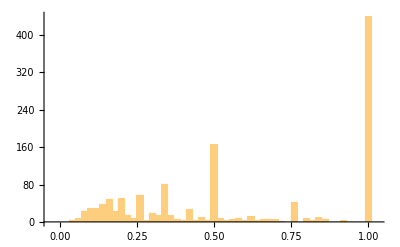

```mathematica
Histogram[TaAP,{-.03,1.03,.02}]
```

```mathematica
hlist=HistogramList[TaAP,{-.03,1.03,.02}]
```

{{-0.03,-0.01,0.01,0.03,0.05,0.07,0.09,0.11,0.13,0.15,0.17,0.19,0.21,0.23,0.25,0.27,0.29,0.31,0.33,0.35,0.37,0.39,0.41,0.43,0.45,0.47,0.49,0.51,0.53,0.55,0.57,0.59,0.61,0.63,0.65,0.67,0.69,0.71,0.73,0.75,0.77,0.79,0.81,0.83,0.85,0.87,0.89,0.91,0.93,0.95,0.97,0.99,1.01,1.03},{0,0,0,4,7,23,29,28,37,48,23,50,14,7,57,2,19,14,81,13,6,3,27,4,9,4,165,8,3,5,8,3,12,2,6,6,5,1,0,41,0,7,4,9,6,0,0,2,0,0,0,440,0}}

```mathematica
StringJoin["("<>ToString[#_⟦1⟧]<>","<>ToString[#_⟦2⟧]<>")"&/@Transpose[{Drop[hlist_⟦1⟧,-1],hlist_⟦2⟧}]]
```

(-0.03,0)(-0.01,0)(0.01,0)(0.03,4)(0.05,7)(0.07,23)(0.09,29)(0.11,28)(0.13,37)(0.15,48)(0.17,23)(0.19,50)(0.21,14)(0.23,7)(0.25,57)(0.27,2)(0.29,19)(0.31,14)(0.33,81)(0.35,13)(0.37,6)(0.39,3)(0.41,27)(0.43,4)(0.45,9)(0.47,4)(0.49,165)(0.51,8)(0.53,3)(0.55,5)(0.57,8)(0.59,3)(0.61,12)(0.63,2)(0.65,6)(0.67,6)(0.69,5)(0.71,1)(0.73,0)(0.75,41)(0.77,0)(0.79,7)(0.81,4)(0.83,9)(0.85,6)(0.87,0)(0.89,0)(0.91,2)(0.93,0)(0.95,0)(0.97,0)(0.99,440)(1.01,0)

```mathematica
Count[TaAP,1]
```

440

```mathematica
nTaAP=taAP1[nonnumRawTable]
```

{1,1,1/3,1,1/3,1,1/2,10821943/22790880,5/12,1,1,971/1680,1,1,237371/2522520,1/2,13/15,1/3,1/5,1/2,1/6,1/3,1,9/20,1/2,5/12,5/6,21524/45045,9/40,5/12,1/6,253/756,1/2,1,1/4,1/3,15739/25200,1/11,1,363/980,29/36,3/4,1/2,25/48,1/5,1/2,1/2,1/3,1/7,31/36,1/4,1/2,1/5,1/2,1/3,1,1,1,3/4,1/2,1/11,1,1,1,1266113/5285280,1,1,1/3,55/84,1,283/504,1/3,1,1/5,1,1,1/3,1,1,1,1,1/8,1,1/2,1/4,867323/1965600,11/60,1,1,1,1/6,1,1/2,1,1/6,1/2,5/12,1/7,1,347/1260,17/70,1/4,1/2,1/2,213189541/5150574000,1,11/18,3/4,1/2,1,1/2,1/7,11/60,1/3,1/2,1/2,1,485753/2162160,1/6,1,3/4,1,1,1,1/5,3/4,1,1587823/6534528,1,11/36,1,1/14,1/2,348911/3243240,1/5,1,15797/138600,11/18,1,1,1,1,1,3/4,1/2,1/3,3/4,1,5/12,11/60,1,7/24,1/2,11/18,1,1,49/80,1,1/4,1,1,1/2,1/3,1/2,1/8,1,1/2,17/21,223/840,5/12,1,1/3,1,1,1/4,1/2,1,1/5,1,1/8,5/12,7/24,1/4,29/100,1/5,1/2,1,25/48,1/7,1,1/2,3/4,31/36,1/7,1/6,1/7,1,1/2,15/56,9/40,1/5,1/5,1/3,1,1/4,1/3,1/4,1,1,1/5,11/18,1/7,1/2,5/6,1/2,237371/2522520,1,1,5/6,1,13/36,363/980,1,1,43/56,203/810,137/180,7/24,11/60,19/24,1,1/6,15797/138600,5/12,1/6,1/5,1/2,11/60,431/5148,1/5,1,1,1,25/48,1,1/7,1/2,1,1,1,1,1/4,1,19/80,1/2,1/4,37/180,11/18,18107/166320,1,1,1/2,1,696763/1081080,1/2,1/4,7/10,1,1/3,1/2,1,1,1/2,5/12,1,35/612,3/4,1/2,1,1/4,1,1/6,29/100,299/2970,7/12,1,1/2,3411973/14132580,1/2,1/7,9/40,1/23,13/24,1/3,1,1,41/72,1/2,13/84,1,1/4,1/6,1,49/72,137/300,1,1,1/6,1/5,1,1/14,13/36,1/2,1,1/3,1,211/315,1/7,3/4,1/5,13/36,1,1/7,1/2,1/2,1,1/2,3349/17640,1/12,7/24,1,1,9/20,1,1/10,1/7,1/2,1,1/2,1/3,1/2,153/700,1/13,1,1/7,38947/127512,1,1,1/5,1,1/3,191/360,25/312,3349/17640,47/180,1/3,1,1,1,153/700,1/5,7/24,131/220,11/18,1/3,1,191/1512,1,1,1,9/40,1,1/6,1/5,1,1/2,1,341/1680,5/6,557/3024,1,1,25/48,1,3/5,1,1,1,1,1/2,1/2,5/8,1/7,1,3/4,1,1,1,7/10,1/2,1,1,1,1/2,47/180,1,1/13,31/36,1,1/12,1,1/5,1,1,1/2,1/7,1,1,9/20,1,1,1,2843/4200,36293/221760,1,1,1,19/80,1,11/60,1/3,1/2,82/175,1,1/4,1/6,1,1/2,13/84,1/3,5/12,1/7,1/2,1/3,1/9,1,29/36,1/2,1/2,1/3,1,1/3,1/2,1273/1890,9/40,5/12,1/3,1,1,1,1/7,1/2,1/8,1/3,47/180,137/300,13/36,1/2,1,5/12,3349/17640,77/240,1,1,4657/8008,1/3,1,743/4200,1,1/2,1879/12600,13/30,2021/19800,1,1,13/84,1,1,5/12,121/1080,1,1/2,1/7,25961/194040,1,1/2,31/36,1/3,1/4,7/10,2509/15120,29/100,3/4,1,1/9,3/4,1,1,1,11/18,1/2,1/2,319/1680,1,1/4,1/2,3/4,1/3,1571/5040,2761/17640,1,1/5,1/8,5/12,1,1,1/2,1,47/180,1/2,9/14,1,31/36,1,6113/7560,7129/22680,477/2600,1,363/980,1,1/3,1,1,3/4,1/8,1,237/400,1/2,1/2,3/4,1/6,13/36,1,5/6,1,1,1,1/4,1/2,1/4,211/1080,1/2,1,1,1/4,68879/1162800,5/6,1/8,55/84,1/2,1/3,7/24,13/36,1/6,1,41/60,1,1/13,29/100,1,1,55/84,107/630,1/3,1/4,197/240,1/12,1/3,1,29/36,1188403/3088800,5/12,431/5148,1/3,1/12,1/7,1,12229277/190466640,29/100,1/2,1,1,1,1,1,1,1,1,1/2,1/9,1,1/13,1/11,1/10,1,1,1,93/224,1,1,1,1/4,1/5,1,1,509/720,9/40,7303/34320,3/4,105737/308880,1/2,49/120,1,1,1/2,13/84,1,1,1,3/4,1/2,13019/85680,5/12,1/2,1,1,197/240,1,1/3,1/6,18107/166320,1,1/8,1/2,1/5,17/24,1/8,1/3,1,1,1,3/4,1/7,1,25/48,1/2,1,1/5,889451/3243240,1,1/2,1/6,187637/428400,1,1,1,1,5/9,529/1260,1,1/3,13/36,1,1/12,1,1/2,1,1/5,1/5,1/2,1,1,197/240,1,1/6,1/2,1/2,1/3,11/18,1/2,1,1/3,3/4,397/2016,67/120,1/4,1,3/4,27899/48048,9/20,1,1/2,1,1,1,1/2,1,1,1/3,1,1,1/2,1/2,13/84,1/2,1/2,1,1/11,1879/12600,1,1,1,1,1/4,56436503/159279120,1,1,4/15,5/12,5/12,1/2,1,1/10,145903/831600,1/2,409/540,1,1,19/24,1,1,15/112,1,1/2,197/360,3/4,1,1/5,1/5,1,1/3,7/24,1,1/2,3/4,1/3,3/4,1,1/4,1,1,1,1,1/2,3/4,1,1,1/3,11/12,1/3,1,1/2,73/504,1,25961/194040,37/180,163/240,5/6,1,1,77/240,1,3/4,1,1/5,1/2,1,1,1,1,77/240,1,1,73/504,1,1/4,1/2,1,25/48,5/12,77/240,1/5,1,1,1,1/2,1/3,7/24,13/36,11/18,1/2,1,1,1/11,1,1,1,7/24,5/12,1/2,5/12,1/2,88189/277200,1/2,1,1/6,1,1,1/2,7/12,1,7129/22680,1/13,1,533/3360,1,1/2,1,3/4,1,1/4,1/4,1,1,1,1/7,77/240,5/6,1,1,1,4861/22680,1,47/180,1,3/4,1,1/9,1,197/240,1,1,1,1/2,3/4,1,1,1/2,1,1/9,1/2,1/3,1/4,1/2,1/4,28271/221760,1,3/4,1,1,1,1/3,1/6,1/5,11/12,3/4,3/4,1/2,1/2,1/4,1,1,1/3,1,4/7,1,1,1,9/40,1/7,1,1/2,1,1/2,1,3/4,1,1,1/4,1,13/36,1/2,1/2,1,3/4,1,1/2,13/36,1/4,1,23/264,2833255/29405376,1,49/120,1/6,1/9,1,1,80507/1395360,1,25/48,3/4,1/3,1,13/84,25/48,11/60,47/180,1,770921/3100800,1/2,1,1/22,1,1/3,1,1,1,8837/112112,1,1/3,1,1,1,1,7/24,1,6061/87360,1,1/3,1/4,1/6,1,1,1,1,1,13/120,1/3,1/2,137/300,1,9/40,1,1,1,1/2,13/18,25961/194040,41/60}

```mathematica
Mean[%]//N
```

0.60908

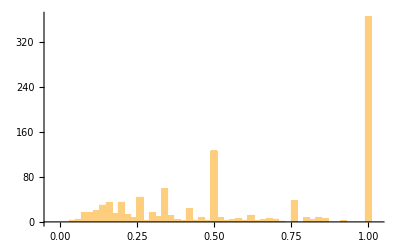

```mathematica
Histogram[nTaAP,{-.03,1.03,.02}]
```

```mathematica
hlist=HistogramList[nTaAP,{-.03,1.03,.02}]
```

{{-0.03,-0.01,0.01,0.03,0.05,0.07,0.09,0.11,0.13,0.15,0.17,0.19,0.21,0.23,0.25,0.27,0.29,0.31,0.33,0.35,0.37,0.39,0.41,0.43,0.45,0.47,0.49,0.51,0.53,0.55,0.57,0.59,0.61,0.63,0.65,0.67,0.69,0.71,0.73,0.75,0.77,0.79,0.81,0.83,0.85,0.87,0.89,0.91,0.93,0.95,0.97,0.99,1.01,1.03},{0,0,0,3,5,17,17,20,30,34,15,35,13,7,44,2,17,9,59,11,4,2,23,3,8,2,126,8,3,4,6,3,12,2,4,6,5,1,0,38,0,7,4,8,6,0,0,2,0,0,0,365,0}}

```mathematica
StringJoin["("<>ToString[#_⟦1⟧]<>","<>ToString[#_⟦2⟧]<>")"&/@Transpose[{Drop[hlist_⟦1⟧,-1],hlist_⟦2⟧}]]
```

(-0.03,0)(-0.01,0)(0.01,0)(0.03,3)(0.05,5)(0.07,17)(0.09,17)(0.11,20)(0.13,30)(0.15,34)(0.17,15)(0.19,35)(0.21,13)(0.23,7)(0.25,44)(0.27,2)(0.29,17)(0.31,9)(0.33,59)(0.35,11)(0.37,4)(0.39,2)(0.41,23)(0.43,3)(0.45,8)(0.47,2)(0.49,126)(0.51,8)(0.53,3)(0.55,4)(0.57,6)(0.59,3)(0.61,12)(0.63,2)(0.65,4)(0.67,6)(0.69,5)(0.71,1)(0.73,0)(0.75,38)(0.77,0)(0.79,7)(0.81,4)(0.83,8)(0.85,6)(0.87,0)(0.89,0)(0.91,2)(0.93,0)(0.95,0)(0.97,0)(0.99,365)(1.01,0)

```mathematica
Count[nTaAP,1]
```

365

### TaMRR

```mathematica
TaRR=taRR[RawTable]
```

{1,1,1/3,1/4,11/18,1/5,1,1/2,1/3,1,1/2,5/12,1,1/3,1,18107/166320,13/36,1,1/4,1/9,1,1/4,1,5/12,1/5,1,1/2,1,1,1/2,3/4,1,1,237371/2522520,1/2,37/180,1,1/3,1/5,1/2,1/6,1/6,1/3,1,1/2,1,1/2,1/2,1/3,1/7,1,5/12,9/40,5/12,1/6,5/12,1/2,1/2,1/4,1,1/4,1/6,1/3,1,1/11,1,13/84,1,363/980,5/6,3/4,1/2,19/180,25/48,1/5,1/3,5/12,1/2,1/2,1/3,1/7,1,1/4,1/2,1/5,1/2,1/3,1,1,1/3,1,1,1/9,1,1/5,1/2,1/11,1,1,1/3,1,452993/1829520,1,1,1/6,1/3,1,1/8,1,1/2,1,1/3,1/3,1/5,1,1/5,11/60,1,1,1/3,1,1/2,1/2,1,1/2,1,1,52279/576576,1,1/8,1,1/5,1/2,1/4,3/4,1/2,1/2,11/60,1,1,1,1,1/3,1/6,1,1/2,1,1/6,1/2,1,5/12,1/7,1,1/2,47/180,1/5,1/4,1/2,1/5,1/2,1/2,213189541/5150574000,1,11/18,1,1/2,1,1,1/4,1/2,1/7,1,11/60,1/3,1/2,1/2,1,1,11/60,1/6,1/3,1,3/4,1,1,1,1/5,3/4,1/2,1,1/3,1/8,1/6,1,1/4,1,1/3,1/5,1/14,1/2,1,348911/3243240,1/5,1,1,15797/138600,11/18,1,1,1,1,1/2,1,1/3,3/4,1/2,1/3,1/3,3/4,1,5/12,11/60,11/60,1,7/24,1/5,1/2,1/2,1,11/18,1,1,3/4,1,1/4,1,1,1/2,1/3,1,1,1/2,1/12,1/8,1,1/2,1,223/840,5/12,1,1/3,1,1,1,1,1/4,1/2,1,1/5,1,1/8,1/9,3/4,5/12,7/24,1/4,29/100,1/5,1/2,1/2,1,1,1,25/48,1/7,1/6,1,1,1,1/3,1/2,1/2,1,3/4,1,1/7,1/6,1/7,1/8,1,1/2,1/4,9/40,1/5,1/5,1/3,1/3,1/2,1,1/4,1/3,1/5,1/4,1691/15840,9/40,1,1,1/5,1,11/18,1/7,1/2,47/180,1,1,1/5,1/2,1/2,1/2,237371/2522520,1/2,1,1/5,1,1,1,1/3,1/11,13/36,363/980,1,1,1/2,1,1/5,1,7/24,1/8,11/60,1,1,1/6,15797/138600,19823/425040,1/3,1,1/6,1/5,1/2,11/60,431/5148,1/5,1,1/10,1,1,77/240,25/48,1,1/7,1/2,1,1,1/10,1,1,1/4,1,19/80,1/2,1/4,37/180,1,11/18,18107/166320,1,1,1/2,1,1,1/2,1/4,1,1,1/3,1/5,1/2,1,1,1/2,5/12,1,35/612,3/4,1/2,1,1/4,1,1/6,29/100,3349/17640,299/2970,1/2,1,1/2,1/5,1/2,1/7,9/40,7/24,1/23,1/2,1/3,1,1,1/7,1,1/2,13/84,1,1/4,1/6,1/12,1/4,1,1,13/18,137/300,1,1,319/1680,1/6,1/5,1,1/14,1/2,13/36,1/2,1,1/3,1,1879/12600,1,1/7,1,1/5,1/2,13/36,1,1,1/7,1/2,1/2,1,1/13,1,29/100,1/2,3349/17640,1/12,7/24,1,1,1/2,1,1/10,1/7,1,1/2,1,1/2,1/3,1/2,153/700,1/13,1,1/7,1/2,1,1,1/5,1,1/3,1,11/18,25/312,3349/17640,47/180,319/1680,1/11,1/3,1,1,1,1,153/700,1/5,7/24,1,11/18,17/60,1,191/1512,1,1,1,9/40,21/220,1,5/12,1/6,1/5,1,1,1/2,1,341/1680,1,23/168,1/3,1,1,25/48,1,1,1,1,1/2,1,1,1,1/2,1,1/2,1/2,1,1/7,1,29/72,1,1,1,1,1,1/2,1,11/60,1,1,1/2,1/7,47/180,1,1/13,1,1,1/12,1,1/5,1,1/2,1,1/2,1/7,1,1,1/2,1/4,1/2,1,1,1,1,275/2016,1,1,1,19/80,1,11/60,1/3,1/2,1/5,1/2,1,1/2,1,1/4,1/6,1,1,1/2,13/84,1/3,5/12,1/7,19/180,1/2,1/3,1/9,1,1,1/2,1/2,1/3,1,1/3,1/2,1,1,9/40,1/2,5/12,1/3,1,1,1/2,1/4,1,1,1/7,1/2,1/8,1/2,1/3,47/180,137/300,13/36,1/2,1/2,1,5/12,3349/17640,1/8,77/240,1,1,1,1/3,1,743/4200,1,1,1/2,1/3,1879/12600,1/2,1/4,2021/19800,1,1/2,1,13/84,1,1,5/12,121/1080,1,1/2,1/7,25961/194040,1,1,1/2,1,1/3,1/4,1,2509/15120,29/100,1,1,1,1/9,3/4,1,1/2,1,1,11/18,1/2,1/2,1,319/1680,1,1/4,1/2,3/4,1/3,1,1/5,2761/17640,1,1,1/5,1/8,3/4,5/12,1,1,1/2,1,1,47/180,1/2,1,1,1,137/300,1,1,5/6,7129/22680,153/700,1,1,363/980,1,1/3,1,1,1/3,1,1/8,1,77/120,1/2,1/2,3/4,1/6,13/36,1,1/2,1/3,1,1,1,1,1/4,1/2,1/4,1/6,1,1/2,1,1,1/4,1,68879/1162800,1,1/8,1,1/2,1/3,7/24,13/36,1/6,1,1/9,1/7,1,1,1,1/13,29/100,1,1,1,1,1,31/480,1,1/3,107/630,1/18,1/3,1/4,1,1/12,1/3,1/2,1,5/6,1,5/12,431/5148,1/3,1/12,1/7,1,1,12229277/190466640,1/6,29/100,1/2,1,1,107/630,1/5,1/12,1,1,1,1,1,1,1/2,1/9,1,1/13,1/11,1,1/6,1/10,1,1,1,11/60,25/48,1,1,1,1,1/4,1/5,1,1,1,3/4,1/3,9/40,1/4,3/4,1/3,1/2,49/120,1,1,1/2,1/2,13/84,1,1,1,1,1/2,1/8,5/12,1/2,1,1,1,1/2,1,1,1/3,1/6,18107/166320,1,1/8,1/2,1/5,5/12,3/4,1/8,1/3,1,1,1,1,3/4,1/7,1,25/48,1/2,1,11/60,1,1/5,1/3,1,1,1/2,1/6,3/4,1,1,1,1,11/18,1/2,1,1/3,13/36,1,1/12,1,1/7,1/2,1,1/5,1/5,1/2,1,1,1,1,1/6,1/2,1/2,1/3,11/18,1,1/2,1,1/3,3/4,17/112,3/4,1/4,1,1,1,1,1/2,1,1/2,13/36,1,1,1,1/2,1,1,1/3,1,1,1/2,1/2,13/84,1/2,1/3,1/2,1,1/11,1,1879/12600,1/5,1,1,1,1,1/4,1/2,1,1/2,1,1/5,5/12,5/12,1/2,1,1,1/10,5297/37800,1/2,1,1,1,1,1,1,1,15/112,1,1/2,1/2,3/4,1,1/5,1/5,1,431/5148,1/3,7/24,1,1,1/2,1,1/3,3/4,1/4,1,1/4,1,1,1,1,1/2,3/4,1,1,1/3,1,1/3,1,1/2,73/504,1,25961/194040,37/180,15/112,1/2,1,1,1,77/240,1,3/4,1,1/5,1/2,1,1,1,1,77/240,1,1,1,73/504,1,1/4,1/4,1/2,1,25/48,5/12,77/240,1/5,1,1,1,13/84,1/2,1/4,1/3,7/24,13/36,11/18,1/2,1,1,1/11,1,1,1,7/24,5/12,1/2,5/12,1/2,49/120,1/2,1,1/6,1,1,1/2,1/2,1,1/2,7129/22680,1/13,1,533/3360,1,1,1/2,1,3/4,1,1/4,1/4,1,1,1,1,1,1/6,1/7,77/240,1,1,1,1,4861/22680,1,1,47/180,1,1/3,3/4,1,1/3,1/12,1/9,1,1,1,1,1,1/2,1/2,3/4,1,1,1/2,1,1,1/9,1/2,1/6,1/3,1/4,1/2,1/4,1,28271/221760,1/2,1,3/4,1,1,1,1/3,1/6,1/5,1/2,1/11,1,3/4,3/4,1/2,1/2,1/2,1/4,1,1,1/3,1,1,1,1,1,9/40,1/7,1,1/6,1/2,1,1/2,1,3/4,1,1,1/4,1,1,13/36,1/2,1/2,1,3/4,1,1/2,13/36,1/4,1,1,23/264,2833255/29405376,1,49/120,1/6,1/9,1,1,80507/1395360,1,25/48,3/4,1/3,1,13/84,25/48,11/60,47/180,1,1/4,1/2,1,1/22,1,1/3,1/10,1,1,1,8837/112112,1,1/3,1,1,1,1,7/24,1,6061/87360,1,1/3,1/4,1/6,1,1,1,1,1,1/12,1/3,1/2,137/300,1,9/40,1,1,1,1/2,1,25961/194040,1/4,1}

```mathematica
Mean[%]//N
```

0.605953

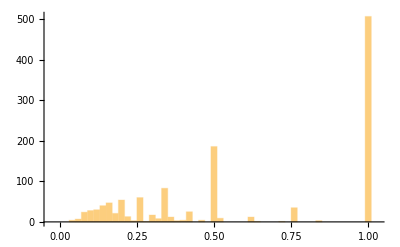

```mathematica
Histogram[TaRR,{-.03,1.03,.02}]
```

```mathematica
hlist=HistogramList[TaRR,{-.03,1.03,.02}]
```

{{-0.03,-0.01,0.01,0.03,0.05,0.07,0.09,0.11,0.13,0.15,0.17,0.19,0.21,0.23,0.25,0.27,0.29,0.31,0.33,0.35,0.37,0.39,0.41,0.43,0.45,0.47,0.49,0.51,0.53,0.55,0.57,0.59,0.61,0.63,0.65,0.67,0.69,0.71,0.73,0.75,0.77,0.79,0.81,0.83,0.85,0.87,0.89,0.91,0.93,0.95,0.97,0.99,1.01,1.03},{0,0,0,4,7,24,28,30,40,47,21,54,13,3,60,1,17,8,83,12,3,4,25,0,4,0,186,9,0,0,0,0,12,1,0,0,0,1,0,35,0,0,0,3,0,0,0,0,0,0,0,507,0}}

```mathematica
StringJoin["("<>ToString[#_⟦1⟧]<>","<>ToString[#_⟦2⟧]<>")"&/@Transpose[{Drop[hlist_⟦1⟧,-1],hlist_⟦2⟧}]]
```

(-0.03,0)(-0.01,0)(0.01,0)(0.03,4)(0.05,7)(0.07,24)(0.09,28)(0.11,30)(0.13,40)(0.15,47)(0.17,21)(0.19,54)(0.21,13)(0.23,3)(0.25,60)(0.27,1)(0.29,17)(0.31,8)(0.33,83)(0.35,12)(0.37,3)(0.39,4)(0.41,25)(0.43,0)(0.45,4)(0.47,0)(0.49,186)(0.51,9)(0.53,0)(0.55,0)(0.57,0)(0.59,0)(0.61,12)(0.63,1)(0.65,0)(0.67,0)(0.69,0)(0.71,1)(0.73,0)(0.75,35)(0.77,0)(0.79,0)(0.81,0)(0.83,3)(0.85,0)(0.87,0)(0.89,0)(0.91,0)(0.93,0)(0.95,0)(0.97,0)(0.99,507)(1.01,0)

```mathematica
Count[TaRR,1]
```

507

```mathematica
nTaRR=taRR[nonnumRawTable]
```

{1,1,1/3,1,1/3,1,1/2,1,5/12,1,1,3/4,1,1,237371/2522520,1/2,1,1/3,1/5,1/2,1/6,1/3,1,1/2,1/2,1/3,1,5/12,9/40,5/12,1/6,5/12,1/2,1,1/4,1/3,1,1/11,1,363/980,5/6,3/4,1/2,25/48,1/5,1/2,1/2,1/3,1/7,1,1/4,1/2,1/5,1/2,1/3,1,1,1,1,1/2,1/11,1,1,1,452993/1829520,1,1,1/3,1,1,1,1/3,1,1/5,1,1,1/3,1,1,1,1,1/8,1,1/2,1/4,3/4,11/60,1,1,1,1/6,1,1/2,1,1/6,1/2,5/12,1/7,1,47/180,1/5,1/4,1/2,1/2,213189541/5150574000,1,11/18,1,1/2,1,1/2,1/7,11/60,1/3,1/2,1/2,1,11/60,1/6,1,3/4,1,1,1,1/5,3/4,1,1/3,1,1/4,1,1/14,1/2,348911/3243240,1/5,1,15797/138600,11/18,1,1,1,1,1,3/4,1/2,1/3,3/4,1,5/12,11/60,1,7/24,1/2,11/18,1,1,3/4,1,1/4,1,1,1/2,1/3,1/2,1/8,1,1/2,1,223/840,5/12,1,1/3,1,1,1/4,1/2,1,1/5,1,1/8,5/12,7/24,1/4,29/100,1/5,1/2,1,25/48,1/7,1,1/2,3/4,1,1/7,1/6,1/7,1,1/2,1/4,9/40,1/5,1/5,1/3,1,1/4,1/3,1/4,1,1,1/5,11/18,1/7,1/2,1,1/2,237371/2522520,1,1,1,1,13/36,363/980,1,1,1,1/5,1,7/24,11/60,1,1,1/6,15797/138600,1/3,1/6,1/5,1/2,11/60,431/5148,1/5,1,1,1,25/48,1,1/7,1/2,1,1,1,1,1/4,1,19/80,1/2,1/4,37/180,11/18,18107/166320,1,1,1/2,1,1,1/2,1/4,1,1,1/3,1/2,1,1,1/2,5/12,1,35/612,3/4,1/2,1,1/4,1,1/6,29/100,299/2970,1/2,1,1/2,1/5,1/2,1/7,9/40,1/23,1/2,1/3,1,1,1,1/2,13/84,1,1/4,1/6,1,13/18,137/300,1,1,1/6,1/5,1,1/14,13/36,1/2,1,1/3,1,1,1/7,1,1/5,13/36,1,1/7,1/2,1/2,1,1/2,3349/17640,1/12,7/24,1,1,1/2,1,1/10,1/7,1/2,1,1/2,1/3,1/2,153/700,1/13,1,1/7,1/2,1,1,1/5,1,1/3,11/18,25/312,3349/17640,47/180,1/3,1,1,1,153/700,1/5,7/24,1,11/18,17/60,1,191/1512,1,1,1,9/40,1,1/6,1/5,1,1/2,1,341/1680,1,23/168,1,1,25/48,1,1,1,1,1,1,1/2,1/2,1,1/7,1,1,1,1,1,1,1/2,1,1,1,1/2,47/180,1,1/13,1,1,1/12,1,1/5,1,1,1/2,1/7,1,1,1/2,1,1,1,1,275/2016,1,1,1,19/80,1,11/60,1/3,1/2,1/2,1,1/4,1/6,1,1/2,13/84,1/3,5/12,1/7,1/2,1/3,1/9,1,1,1/2,1/2,1/3,1,1/3,1/2,1,9/40,5/12,1/3,1,1,1,1/7,1/2,1/8,1/3,47/180,137/300,13/36,1/2,1,5/12,3349/17640,77/240,1,1,1,1/3,1,743/4200,1,1/2,1879/12600,1/2,2021/19800,1,1,13/84,1,1,5/12,121/1080,1,1/2,1/7,25961/194040,1,1/2,1,1/3,1/4,1,2509/15120,29/100,1,1,1/9,3/4,1,1,1,11/18,1/2,1/2,319/1680,1,1/4,1/2,3/4,1/3,1/5,2761/17640,1,1/5,1/8,5/12,1,1,1/2,1,47/180,1/2,1,1,1,1,5/6,7129/22680,153/700,1,363/980,1,1/3,1,1,1,1/8,1,77/120,1/2,1/2,3/4,1/6,13/36,1,1,1,1,1,1/4,1/2,1/4,1/6,1/2,1,1,1/4,68879/1162800,1,1/8,1,1/2,1/3,7/24,13/36,1/6,1,1,1,1/13,29/100,1,1,1,107/630,1/3,1/4,1,1/12,1/3,1,5/6,1,5/12,431/5148,1/3,1/12,1/7,1,12229277/190466640,29/100,1/2,1,1,1,1,1,1,1,1,1/2,1/9,1,1/13,1/11,1/10,1,1,1,25/48,1,1,1,1/4,1/5,1,1,3/4,9/40,1/4,3/4,1/3,1/2,49/120,1,1,1/2,13/84,1,1,1,1,1/2,1/8,5/12,1/2,1,1,1,1,1/3,1/6,18107/166320,1,1/8,1/2,1/5,3/4,1/8,1/3,1,1,1,3/4,1/7,1,25/48,1/2,1,1/5,1/3,1,1/2,1/6,3/4,1,1,1,1,11/18,1/2,1,1/3,13/36,1,1/12,1,1/2,1,1/5,1/5,1/2,1,1,1,1,1/6,1/2,1/2,1/3,11/18,1/2,1,1/3,3/4,17/112,3/4,1/4,1,1,1,1/2,1,1/2,1,1,1,1/2,1,1,1/3,1,1,1/2,1/2,13/84,1/2,1/2,1,1/11,1879/12600,1,1,1,1,1/4,1/2,1,1,1/5,5/12,5/12,1/2,1,1/10,5297/37800,1/2,1,1,1,1,1,1,15/112,1,1/2,1/2,3/4,1,1/5,1/5,1,1/3,7/24,1,1/2,1,1/3,3/4,1,1/4,1,1,1,1,1/2,3/4,1,1,1/3,1,1/3,1,1/2,73/504,1,25961/194040,37/180,1/2,1,1,1,77/240,1,3/4,1,1/5,1/2,1,1,1,1,77/240,1,1,73/504,1,1/4,1/2,1,25/48,5/12,77/240,1/5,1,1,1,1/2,1/3,7/24,13/36,11/18,1/2,1,1,1/11,1,1,1,7/24,5/12,1/2,5/12,1/2,49/120,1/2,1,1/6,1,1,1/2,1/2,1,7129/22680,1/13,1,533/3360,1,1/2,1,3/4,1,1/4,1/4,1,1,1,1/7,77/240,1,1,1,1,4861/22680,1,47/180,1,3/4,1,1/9,1,1,1,1,1,1/2,3/4,1,1,1/2,1,1/9,1/2,1/3,1/4,1/2,1/4,28271/221760,1,3/4,1,1,1,1/3,1/6,1/5,1,3/4,3/4,1/2,1/2,1/4,1,1,1/3,1,1,1,1,1,9/40,1/7,1,1/2,1,1/2,1,3/4,1,1,1/4,1,13/36,1/2,1/2,1,3/4,1,1/2,13/36,1/4,1,23/264,2833255/29405376,1,49/120,1/6,1/9,1,1,80507/1395360,1,25/48,3/4,1/3,1,13/84,25/48,11/60,47/180,1,1/4,1/2,1,1/22,1,1/3,1,1,1,8837/112112,1,1/3,1,1,1,1,7/24,1,6061/87360,1,1/3,1/4,1/6,1,1,1,1,1,1/12,1/3,1/2,137/300,1,9/40,1,1,1,1/2,1,25961/194040,1}

```mathematica
Mean[%]//N
```

0.626779

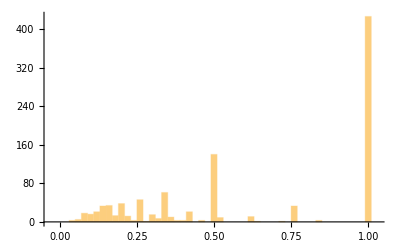

```mathematica
Histogram[nTaRR,{-.03,1.03,.02}]
```

```mathematica
hlist=HistogramList[nTaRR,{-.03,1.03,.02}]
```

{{-0.03,-0.01,0.01,0.03,0.05,0.07,0.09,0.11,0.13,0.15,0.17,0.19,0.21,0.23,0.25,0.27,0.29,0.31,0.33,0.35,0.37,0.39,0.41,0.43,0.45,0.47,0.49,0.51,0.53,0.55,0.57,0.59,0.61,0.63,0.65,0.67,0.69,0.71,0.73,0.75,0.77,0.79,0.81,0.83,0.85,0.87,0.89,0.91,0.93,0.95,0.97,0.99,1.01,1.03},{0,0,0,3,5,18,16,21,33,34,13,38,12,3,46,1,15,7,61,10,3,3,21,0,3,0,140,9,0,0,0,0,11,1,0,0,0,1,0,33,0,0,0,3,0,0,0,0,0,0,0,426,0}}

```mathematica
StringJoin["("<>ToString[#_⟦1⟧]<>","<>ToString[#_⟦2⟧]<>")"&/@Transpose[{Drop[hlist_⟦1⟧,-1],hlist_⟦2⟧}]]
```

(-0.03,0)(-0.01,0)(0.01,0)(0.03,3)(0.05,5)(0.07,18)(0.09,16)(0.11,21)(0.13,33)(0.15,34)(0.17,13)(0.19,38)(0.21,12)(0.23,3)(0.25,46)(0.27,1)(0.29,15)(0.31,7)(0.33,61)(0.35,10)(0.37,3)(0.39,3)(0.41,21)(0.43,0)(0.45,3)(0.47,0)(0.49,140)(0.51,9)(0.53,0)(0.55,0)(0.57,0)(0.59,0)(0.61,11)(0.63,1)(0.65,0)(0.67,0)(0.69,0)(0.71,1)(0.73,0)(0.75,33)(0.77,0)(0.79,0)(0.81,0)(0.83,3)(0.85,0)(0.87,0)(0.89,0)(0.91,0)(0.93,0)(0.95,0)(0.97,0)(0.99,426)(1.01,0)

```mathematica
Count[nTaRR,1]
```

426

## A special question

```mathematica
q=27
```

27

```mathematica
WikiAnswerQuestionPageSelectedSentences[QuestionPoolReg_⟦q,2⟧,TitleConversion[QuestionPool_⟦q,3⟧],{#_⟦2⟧,#_⟦3⟧}&/@AnswerPool_⟦q⟧]
```

{{{#[Anne]# #[Frank]# and her sister, Margot , were eventually transferred to the #[Bergen-Belsen]# #[concentration]# #[camp]# , where they #[died]# of #[typhus]# in March #[1945]#. ,0.6277865908808},{Annelies "#[Anne]#" Marie #[Frank]# (, ?, ; 12 June 1929early March #[1945]#) is one of the most discussed Jewish victims of the #[Holocaust]# . ,0.4177300905355},{Otto #[Frank]#, the only #[survivor]# of the family, returned to Amsterdam after the war to find that #[Anne's]# diary had been saved, and his efforts led to its publication in 1947. ,0.36443424410016},{As persecutions of the Jewish population increased in July 1942, the family went into hiding in the hidden rooms of #[Anne's]# father, Otto #[Frank]# 's, office building. ,0.31239734725114},{The #[Frank]# family moved from Germany to Amsterdam in #[1933]#, the year the Nazis gained control over Germany. ,0.20943738172307},{Born a German national, #[Frank]# lost her citizenship in 1941. ,0.16535048981071},{The diary, which was given to #[Anne]# on her 13th birthday, chronicles her life from 12 June 1942 until 1 August 1944. ,0.14704685744044},{After two years, the group was betrayed and transported to #[concentration]# #[camps]# . ,0.084257060778083},{Born in the city of #[Frankfurt]# am Main in Weimar Germany , she lived most of her life in or near Amsterdam , in the Netherlands. ,0.058610234953526},{Her diary has been the basis for several plays and #[films]#. ,0.048141155432847},{She gained international fame posthumously after her diary was published. ,-100},{It was translated from its original Dutch and first published in English in 1952 as The Diary of a Young Girl . ,-100},{It has since been translated into many languages. ,-100},{It documents her experiences hiding during the German occupation of the Netherlands in World War II . ,-100},{By the beginning of 1940, they were trapped in Amsterdam by the Nazi occupation of the Netherlands. ,-100}}}

```mathematica
ScoreTable
```

<|{{1933,4}}→0.024608365359838,{{1945,7}}→0.031739845425624,{{action,4}}→0.014270724087411,{{Bergen-belsen,3}}→0.017810569171264,{{concentration,4}}→0.017302573877524,{{documentary,3}}→0.017068411966815,{{Frankfurt,6}}→0.035078464378831,{{Goslar,6}}→0.032362150420715,{{Holocaust,12}}→0.026766535428486,{{typhus,4}}→0.045312553775174,{{Anne,89},{Anne's,12}}→0.16979492178325,{{camp,11},{camps,3}}→0.030935166969461,{{Center,2},{Centre,2}}→0.043796696250798,{{private,2},{privately,1}}→0.016192069921981,{{restored,2},{restoration,1}}→0.02820042520297,{{early,6},{earlier,5},{earliest,1}}→0.033813397623355,{{exist,1},{existed,2},{existence,1}}→0.022165144504672,{{film,2},{films,2},{filmmaker,1}}→0.027665944636453,{{Frank,128},{Frank's,14},{Franks,7}}→0.25551938085713,{{survived,9},{survival,1},{survivor,1}}→0.04109626323513,{{dead,1},{death,12},{deaths,3},{die,2},{died,9}}→0.068500395123112|>

### Plotting [1, Fig. 7a]

```mathematica
SortScoreTable[list_,ScalingFactor_,MaxClusters_]:=(AllCluster=Take[Sort[(prep=CensorCluster[#_⟦1⟧];{prep,#_⟦2⟧,Total[Transpose[prep]_⟦2⟧]})&/@list,#1[[2]]>#2[[2]]&],UpTo[MaxClusters]];SizedWords=Table[Width=Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@SplitEven[EvenOut[Transpose[AllCluster_⟦n,1⟧]]])];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

```mathematica
SortScoreTable[Transpose[{Keys[ScoreTable],Values[ScoreTable]}],40,125]
```

```mathematica
SizedWords
```

{{50.8212,8.49142},{38.355,7.4766},{24.3616,4.74885},{19.8138,3.86235},{19.4796,3.79719},{21.7886,3.18547},{21.3513,2.7747},{18.4875,3.08896},{16.7447,3.26408},{13.5399,3.95904},{14.945,3.4959},{18.0491,2.63876},{14.1332,3.30602},{18.6509,2.42378},{11.9222,3.48601},{14.9681,2.50094},{18.285,1.64507},{18.0223,1.62144},{16.4656,1.75072},{12.7933,2.13757},{11.1194,2.16753}}

```mathematica
AllCluster
```

{{{{Frank,128},{Frank's,14}},0.25551938085713,142},{{{Anne,89},{Anne's,12}},0.16979492178325,101},{{{death,12},{deaths,3},{die,2},{died,9}},0.068500395123112,26},{{{typhus,4}},0.045312553775174,4},{{{Center,2},{Centre,2}},0.043796696250798,4},{{{survived,9}},0.04109626323513,9},{{{Frankfurt,6}},0.035078464378831,6},{{{earlier,5},{early,6}},0.033813397623355,11},{{{Goslar,6}},0.032362150420715,6},{{{1945,7}},0.031739845425624,7},{{{camp,11},{camps,3}},0.030935166969461,14},{{{restored,2}},0.02820042520297,2},{{{film,2},{films,2}},0.027665944636453,4},{{{Holocaust,12}},0.026766535428486,12},{{{1933,4}},0.024608365359838,4},{{{existed,2}},0.022165144504672,2},{{{Bergen-belsen,3}},0.017810569171264,3},{{{concentration,4}},0.017302573877524,4},{{{documentary,3}},0.017068411966815,3},{{{private,2}},0.016192069921981,2},{{{action,4}},0.014270724087411,4}}

```mathematica
SmallWorldQAPlot[ScalingFactor_,MaxClusters_,OutputFileName_]:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,Total[WCCounts_⟦2⟧],AllCluster_⟦n,2⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];SetDirectory["D:\\Documents"];str=OpenWrite[OutputFileName];WriteString[str,"\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>"){\\textbf{"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor{red}{"<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[0.85*2.54/72 ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"cm}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H 0.85 ArrangedCluster_⟦k,1,2⟧*2.54/72<0.01),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}
",{k,1,Length[ArrangedCluster]}]]<>"}}\\end{picture}\\end{spacing}\\end{minipage}"];Close[str];)
```

```mathematica
SmallWorldQAPlot[1,125,"anne_frank.txt"];
```